#### 1. IMPORTANT: Definition of an appropriate derivative operator for the code Definition of theory parameters

In this notebook, I define a derivative operator that can take care of derivatives with respect to terms enclosed in the Re[...] and Im[...] operators picking the real and imaginary parts of expressions. This operator is necessary for the current and the following notebooks, hence its placement here. Please execute this before any of the other commands in any of the notebooks.

```mathematica
deriv[expr_,var_]:=D[expr,var]//.{Re'[e_]:>Re[D[e,var]]/D[e,var],Im'[e_]:>Im[D[e,var]]/D[e,var],Arg'[e_]:>Im[D[e,var]/e]/D[e,var],Abs'[e_]:>(Re[e] Re[D[e,var]]+Im[e] Im[D[e,var]])/(Abs[e] D[e,var])}
```

## Parameter setting

```mathematica
replaceVev={v->246.22};
replacePar={λ1->higgsmass^2/(2*v^2),λ3->λ345+2*(Hchmass^2-Hmass^2)/v^2,λ4->(Amass^2+Hmass^2-2*Hchmass^2)/v^2,λ5->(Hmass^2-Amass^2)/v^2,μ2sq->Hmass^2-(λ345*v^2)/2};
```

```mathematica
Q=v/.replaceVev;
higgsmass=125.3;
(*Hmass=71;
Hchmass=330;
Amass=340;
λ345=0.0020;
λ2=0.4;*)
mW0=80.38;
mZ0=91.19;
WeinbergTheta=ArcCos[mW0/mZ0];
g=(2*mW0)/246.22;
gp=g*Tan[WeinbergTheta];

yt=Sqrt[2]*173/246.22;
yb=(*Sqrt[2]*4.18/246.22*)0;
ytau=(*Sqrt[2]*1.78/246.22*)0;
```

```mathematica
list={};
For[i=0,i≤40,i++,{H=55+0.5*i,prelist=Table[{H,k,k,0.0025,0.005},{k,H+200,H+450,5}],
For[j=1,j≤Length[prelist],j++,AppendTo[list,prelist[[j]]]]}];
```

```mathematica
(*Hmasslist=Table[HM,{HM,55,75,0.5}];
(*Hchmasslist=Range[300,600,5];
Amasslist=Range[300,600,5];*)
HchandAmasslist=Table[{k,k},{k,265,515,5}];
λ2list={0.0025};
λ345list={0.005};
prelist=Flatten[Outer[{#1, #2,#3, #4} &, Hmasslist, HchandAmasslist,λ2list,λ345list ,1],3];
Print[Length[prelist]]
list=Table[Flatten[prelist[[i]]],{i,1,Length[prelist]}];
Print[Length[list]]
(*For[i=1,i≤Length[prelist],i++,
AppendTo[list,Flatten[prelist[[i]]]]
];
Print[Length[list]]*)*)
```

### Tree-level potential

```mathematica
Vtr=μ1sq*Φ1ch.Φ1+μ2sq*Φ2ch.Φ2+λ1*(Φ1ch.Φ1)*(Φ1ch.Φ1)+λ2*(Φ2ch.Φ2)*(Φ2ch.Φ2)+λ3*(Φ1ch.Φ1)*(Φ2ch.Φ2)+λ4*(Φ1ch.Φ2)*(Φ2ch.Φ1)+1/2*λ5*((Φ1ch.Φ2)*(Φ1ch.Φ2)+(Φ2ch.Φ1)*(Φ2ch.Φ1));
Fieldexpand={
Φ1->1/(√2)*{{ϕ1p},{h1+I ϕ1}},Φ1ch->1/(√2)*{ϕ1m,(h1-I ϕ1)},Φ2->{{ϕ2p},1/(√2)*{h2+I ϕ2}},Φ2ch->{ϕ2m,1/(√2)*(h2-I ϕ2)}};
Vtree=(Vtr/.Fieldexpand)[[1]]
```

### Tree-level minimization conditions

Note that the minimization condition is only applied at zero temperature.

```mathematica
zerofields={ϕ1p->0,ϕ1m->0,ϕ2p->0,ϕ2m->0,ϕ1->0,ϕ2->0};
(*veveval={h1->v1,h2->v2};*)
veveval={h1->v1,h2->0};
```

```mathematica
Dh10=D[Vtree,h1]/.zerofields/.veveval
(*Dh20=D[Vtree,h2]/.zerofields/.veveval*)
solμ1=Solve[Dh10==0,{μ1sq}];
minconds={solμ1[[1]][[1]]}
```

```mathematica
treepotential[T_,h1_,h2_]:=(h1^4 λ1)/4-1/2 h1^2 v^2 λ1+(h2^4 λ2)/4+1/4 h1^2 h2^2 λ3+1/4 h1^2 h2^2 λ4+1/4 h1^2 h2^2 λ5+(h2^2 μ2sq)/2;
```

```mathematica
FindMinimum[treepotential[0,h1,h2]/.replacePar/.replaceVev,{{h1,v/.replaceVev},{h2,0}}]
```

```mathematica
ContourPlot[{treepotential[0,h1,h2]/.replacePar/.replaceVev},{h1,-500,500},{h2,-500,500}]
```

## Mass matrices

```mathematica
scMass=1/2{{6*λ1*h1^2 - 2*λ1*v^2+λ345*h2^2,2*h1*h2*λ345},{2*h1*h2*λ345,6*λ2*h2^2+λ345*h1^2+2*μ2sq}};
pscMass=1/2{{2*λ1*h1^2-2*λ1*v^2+(λ3+λ4-λ5)*h2^2,2*h1*h2*λ5},{2*h1*h2*λ5,2*λ2*h2^2+(λ3+λ4-λ5)*h1^2+2*μ2sq}};
chMass=1/2{{2*λ1*h1^2-2*λ1*v^2+λ3*h2^2,h1*h2*(λ4+λ5)},{h1*h2*(λ4+λ5),2*λ2*h2^2+λ3*h1^2+2*μ2sq}};
PiMatrix=T^2/24{{6*yt^2+6*yb^2+6*ytau^2+9/2*g^2+3/2*gp^2+12*λ1+4*λ3+2*λ4,0},{0,9/2*g^2+3/2*gp^2+12*λ2+4*λ3+2*λ4}};
```

```mathematica
scMassTh=scMass+PiMatrix;
pscMassTh=pscMass+PiMatrix;
chMassTh=chMass+PiMatrix;
```

```mathematica
mGauge=(h1^2+h2^2)/v^2*mGauge0^2;
mFerm=h1^2/2*yf^2;
mWTh=(h1^2+h2^2)/v^2*mW^2+2*g^2*T^2;
DeltaSq=((h1^2+h2^2+8*T^2)^2)/64*(g^2+gp^2)^2-g^2*gp^2*T^2*(h1^2+h2^2+4*T^2);
mZTh=(h1^2+h2^2)/8*(g^2+gp^2)+(g^2+gp^2)*T^2+Sqrt[DeltaSq];
mγTh=(h1^2+h2^2)/8*(g^2+gp^2)+(g^2+gp^2)*T^2-Sqrt[DeltaSq];
```

```mathematica
masstsq[T_,h1_,h2_]:=1/2*yt^2*h1^2;
massbsq[T_,h1_,h2_]:=1/2*yb^2*h1^2;
massTausq[T_,h1_,h2_]:=1/2*ytau^2*h1^2;
massγsq[T_,h1_,h2_]:=(h1^2+h2^2)/8*(g^2+gp^2)+(g^2+gp^2)*T^2-Sqrt[((h1^2+h2^2+8*T^2)^2)/64*(g^2+gp^2)^2-g^2*gp^2*T^2*(h1^2+h2^2+4*T^2)];(*???*)
massZsq[T_,h1_,h2_]:=(h1^2+h2^2)/8*(g^2+gp^2)+(g^2+gp^2)*T^2+Sqrt[((h1^2+h2^2+8*T^2)^2)/64*(g^2+gp^2)^2-g^2*gp^2*T^2*(h1^2+h2^2+4*T^2)];(*???*)
massWsq[T_,h1_,h2_]:=(h1^2+h2^2)/v^2*mW0^2+2*g^2*T^2;
massHsq[T_,h1_,h2_]:=(1/96 (18 g^2 T^2+6 gp^2 T^2+12 T^2 yb^2+12 T^2 yt^2+12 T^2 ytau^2+144 h1^2 λ1+24 T^2 λ1-48 v^2 λ1+144 h2^2 λ2+24 T^2 λ2+16 T^2 λ3+24 h1^2 λ345+24 h2^2 λ345+8 T^2 λ4+48 μ2sq-12 √(T^4 yb^4+2 T^4 yb^2 yt^2+T^4 yt^4+2 T^4 yb^2 ytau^2+2 T^4 yt^2 ytau^2+T^4 ytau^4+24 h1^2 T^2 yb^2 λ1+4 T^4 yb^2 λ1-8 T^2 v^2 yb^2 λ1+24 h1^2 T^2 yt^2 λ1+4 T^4 yt^2 λ1-8 T^2 v^2 yt^2 λ1+24 h1^2 T^2 ytau^2 λ1+4 T^4 ytau^2 λ1-8 T^2 v^2 ytau^2 λ1+144 h1^4 λ1^2+48 h1^2 T^2 λ1^2+4 T^4 λ1^2-96 h1^2 v^2 λ1^2-16 T^2 v^2 λ1^2+16 v^4 λ1^2-24 h2^2 T^2 yb^2 λ2-4 T^4 yb^2 λ2-24 h2^2 T^2 yt^2 λ2-4 T^4 yt^2 λ2-24 h2^2 T^2 ytau^2 λ2-4 T^4 ytau^2 λ2-288 h1^2 h2^2 λ1 λ2-48 h1^2 T^2 λ1 λ2-48 h2^2 T^2 λ1 λ2-8 T^4 λ1 λ2+96 h2^2 v^2 λ1 λ2+16 T^2 v^2 λ1 λ2+144 h2^4 λ2^2+48 h2^2 T^2 λ2^2+4 T^4 λ2^2-4 h1^2 T^2 yb^2 λ345+4 h2^2 T^2 yb^2 λ345-4 h1^2 T^2 yt^2 λ345+4 h2^2 T^2 yt^2 λ345-4 h1^2 T^2 ytau^2 λ345+4 h2^2 T^2 ytau^2 λ345-48 h1^4 λ1 λ345+48 h1^2 h2^2 λ1 λ345-8 h1^2 T^2 λ1 λ345+8 h2^2 T^2 λ1 λ345+16 h1^2 v^2 λ1 λ345-16 h2^2 v^2 λ1 λ345+48 h1^2 h2^2 λ2 λ345-48 h2^4 λ2 λ345+8 h1^2 T^2 λ2 λ345-8 h2^2 T^2 λ2 λ345+4 h1^4 λ345^2+56 h1^2 h2^2 λ345^2+4 h2^4 λ345^2-8 T^2 yb^2 μ2sq-8 T^2 yt^2 μ2sq-8 T^2 ytau^2 μ2sq-96 h1^2 λ1 μ2sq-16 T^2 λ1 μ2sq+32 v^2 λ1 μ2sq+96 h2^2 λ2 μ2sq+16 T^2 λ2 μ2sq+16 h1^2 λ345 μ2sq-16 h2^2 λ345 μ2sq+16 μ2sq^2)));
massHiggssq[T_,h1_,h2_]:=(1/96 (18 g^2 T^2+6 gp^2 T^2+12 T^2 yb^2+12 T^2 yt^2+12 T^2 ytau^2+144 h1^2 λ1+24 T^2 λ1-48 v^2 λ1+144 h2^2 λ2+24 T^2 λ2+16 T^2 λ3+24 h1^2 λ345+24 h2^2 λ345+8 T^2 λ4+48 μ2sq+12 √(T^4 yb^4+2 T^4 yb^2 yt^2+T^4 yt^4+2 T^4 yb^2 ytau^2+2 T^4 yt^2 ytau^2+T^4 ytau^4+24 h1^2 T^2 yb^2 λ1+4 T^4 yb^2 λ1-8 T^2 v^2 yb^2 λ1+24 h1^2 T^2 yt^2 λ1+4 T^4 yt^2 λ1-8 T^2 v^2 yt^2 λ1+24 h1^2 T^2 ytau^2 λ1+4 T^4 ytau^2 λ1-8 T^2 v^2 ytau^2 λ1+144 h1^4 λ1^2+48 h1^2 T^2 λ1^2+4 T^4 λ1^2-96 h1^2 v^2 λ1^2-16 T^2 v^2 λ1^2+16 v^4 λ1^2-24 h2^2 T^2 yb^2 λ2-4 T^4 yb^2 λ2-24 h2^2 T^2 yt^2 λ2-4 T^4 yt^2 λ2-24 h2^2 T^2 ytau^2 λ2-4 T^4 ytau^2 λ2-288 h1^2 h2^2 λ1 λ2-48 h1^2 T^2 λ1 λ2-48 h2^2 T^2 λ1 λ2-8 T^4 λ1 λ2+96 h2^2 v^2 λ1 λ2+16 T^2 v^2 λ1 λ2+144 h2^4 λ2^2+48 h2^2 T^2 λ2^2+4 T^4 λ2^2-4 h1^2 T^2 yb^2 λ345+4 h2^2 T^2 yb^2 λ345-4 h1^2 T^2 yt^2 λ345+4 h2^2 T^2 yt^2 λ345-4 h1^2 T^2 ytau^2 λ345+4 h2^2 T^2 ytau^2 λ345-48 h1^4 λ1 λ345+48 h1^2 h2^2 λ1 λ345-8 h1^2 T^2 λ1 λ345+8 h2^2 T^2 λ1 λ345+16 h1^2 v^2 λ1 λ345-16 h2^2 v^2 λ1 λ345+48 h1^2 h2^2 λ2 λ345-48 h2^4 λ2 λ345+8 h1^2 T^2 λ2 λ345-8 h2^2 T^2 λ2 λ345+4 h1^4 λ345^2+56 h1^2 h2^2 λ345^2+4 h2^4 λ345^2-8 T^2 yb^2 μ2sq-8 T^2 yt^2 μ2sq-8 T^2 ytau^2 μ2sq-96 h1^2 λ1 μ2sq-16 T^2 λ1 μ2sq+32 v^2 λ1 μ2sq+96 h2^2 λ2 μ2sq+16 T^2 λ2 μ2sq+16 h1^2 λ345 μ2sq-16 h2^2 λ345 μ2sq+16 μ2sq^2)));
massAsq[T_,h1_,h2_]:=(1/96 (18 g^2 T^2+6 gp^2 T^2+12 T^2 yb^2+12 T^2 yt^2+12 T^2 ytau^2+48 h1^2 λ1+24 T^2 λ1-48 v^2 λ1+48 h2^2 λ2+24 T^2 λ2+24 h1^2 λ3+24 h2^2 λ3+16 T^2 λ3+24 h1^2 λ4+24 h2^2 λ4+8 T^2 λ4-24 h1^2 λ5-24 h2^2 λ5+48 μ2sq+12 √(T^4 yb^4+2 T^4 yb^2 yt^2+T^4 yt^4+2 T^4 yb^2 ytau^2+2 T^4 yt^2 ytau^2+T^4 ytau^4+8 h1^2 T^2 yb^2 λ1+4 T^4 yb^2 λ1-8 T^2 v^2 yb^2 λ1+8 h1^2 T^2 yt^2 λ1+4 T^4 yt^2 λ1-8 T^2 v^2 yt^2 λ1+8 h1^2 T^2 ytau^2 λ1+4 T^4 ytau^2 λ1-8 T^2 v^2 ytau^2 λ1+16 h1^4 λ1^2+16 h1^2 T^2 λ1^2+4 T^4 λ1^2-32 h1^2 v^2 λ1^2-16 T^2 v^2 λ1^2+16 v^4 λ1^2-8 h2^2 T^2 yb^2 λ2-4 T^4 yb^2 λ2-8 h2^2 T^2 yt^2 λ2-4 T^4 yt^2 λ2-8 h2^2 T^2 ytau^2 λ2-4 T^4 ytau^2 λ2-32 h1^2 h2^2 λ1 λ2-16 h1^2 T^2 λ1 λ2-16 h2^2 T^2 λ1 λ2-8 T^4 λ1 λ2+32 h2^2 v^2 λ1 λ2+16 T^2 v^2 λ1 λ2+16 h2^4 λ2^2+16 h2^2 T^2 λ2^2+4 T^4 λ2^2-4 h1^2 T^2 yb^2 λ3+4 h2^2 T^2 yb^2 λ3-4 h1^2 T^2 yt^2 λ3+4 h2^2 T^2 yt^2 λ3-4 h1^2 T^2 ytau^2 λ3+4 h2^2 T^2 ytau^2 λ3-16 h1^4 λ1 λ3+16 h1^2 h2^2 λ1 λ3-8 h1^2 T^2 λ1 λ3+8 h2^2 T^2 λ1 λ3+16 h1^2 v^2 λ1 λ3-16 h2^2 v^2 λ1 λ3+16 h1^2 h2^2 λ2 λ3-16 h2^4 λ2 λ3+8 h1^2 T^2 λ2 λ3-8 h2^2 T^2 λ2 λ3+4 h1^4 λ3^2-8 h1^2 h2^2 λ3^2+4 h2^4 λ3^2-4 h1^2 T^2 yb^2 λ4+4 h2^2 T^2 yb^2 λ4-4 h1^2 T^2 yt^2 λ4+4 h2^2 T^2 yt^2 λ4-4 h1^2 T^2 ytau^2 λ4+4 h2^2 T^2 ytau^2 λ4-16 h1^4 λ1 λ4+16 h1^2 h2^2 λ1 λ4-8 h1^2 T^2 λ1 λ4+8 h2^2 T^2 λ1 λ4+16 h1^2 v^2 λ1 λ4-16 h2^2 v^2 λ1 λ4+16 h1^2 h2^2 λ2 λ4-16 h2^4 λ2 λ4+8 h1^2 T^2 λ2 λ4-8 h2^2 T^2 λ2 λ4+8 h1^4 λ3 λ4-16 h1^2 h2^2 λ3 λ4+8 h2^4 λ3 λ4+4 h1^4 λ4^2-8 h1^2 h2^2 λ4^2+4 h2^4 λ4^2+4 h1^2 T^2 yb^2 λ5-4 h2^2 T^2 yb^2 λ5+4 h1^2 T^2 yt^2 λ5-4 h2^2 T^2 yt^2 λ5+4 h1^2 T^2 ytau^2 λ5-4 h2^2 T^2 ytau^2 λ5+16 h1^4 λ1 λ5-16 h1^2 h2^2 λ1 λ5+8 h1^2 T^2 λ1 λ5-8 h2^2 T^2 λ1 λ5-16 h1^2 v^2 λ1 λ5+16 h2^2 v^2 λ1 λ5-16 h1^2 h2^2 λ2 λ5+16 h2^4 λ2 λ5-8 h1^2 T^2 λ2 λ5+8 h2^2 T^2 λ2 λ5-8 h1^4 λ3 λ5+16 h1^2 h2^2 λ3 λ5-8 h2^4 λ3 λ5-8 h1^4 λ4 λ5+16 h1^2 h2^2 λ4 λ5-8 h2^4 λ4 λ5+4 h1^4 λ5^2+56 h1^2 h2^2 λ5^2+4 h2^4 λ5^2-8 T^2 yb^2 μ2sq-8 T^2 yt^2 μ2sq-8 T^2 ytau^2 μ2sq-32 h1^2 λ1 μ2sq-16 T^2 λ1 μ2sq+32 v^2 λ1 μ2sq+32 h2^2 λ2 μ2sq+16 T^2 λ2 μ2sq+16 h1^2 λ3 μ2sq-16 h2^2 λ3 μ2sq+16 h1^2 λ4 μ2sq-16 h2^2 λ4 μ2sq-16 h1^2 λ5 μ2sq+16 h2^2 λ5 μ2sq+16 μ2sq^2)));
masschHsq[T_,h1_,h2_]:=(1/96 (18 g^2 T^2+6 gp^2 T^2+12 T^2 yb^2+12 T^2 yt^2+12 T^2 ytau^2+48 h1^2 λ1+24 T^2 λ1-48 v^2 λ1+48 h2^2 λ2+24 T^2 λ2+24 h1^2 λ3+24 h2^2 λ3+16 T^2 λ3+8 T^2 λ4+48 μ2sq+12 √(T^4 yb^4+2 T^4 yb^2 yt^2+T^4 yt^4+2 T^4 yb^2 ytau^2+2 T^4 yt^2 ytau^2+T^4 ytau^4+8 h1^2 T^2 yb^2 λ1+4 T^4 yb^2 λ1-8 T^2 v^2 yb^2 λ1+8 h1^2 T^2 yt^2 λ1+4 T^4 yt^2 λ1-8 T^2 v^2 yt^2 λ1+8 h1^2 T^2 ytau^2 λ1+4 T^4 ytau^2 λ1-8 T^2 v^2 ytau^2 λ1+16 h1^4 λ1^2+16 h1^2 T^2 λ1^2+4 T^4 λ1^2-32 h1^2 v^2 λ1^2-16 T^2 v^2 λ1^2+16 v^4 λ1^2-8 h2^2 T^2 yb^2 λ2-4 T^4 yb^2 λ2-8 h2^2 T^2 yt^2 λ2-4 T^4 yt^2 λ2-8 h2^2 T^2 ytau^2 λ2-4 T^4 ytau^2 λ2-32 h1^2 h2^2 λ1 λ2-16 h1^2 T^2 λ1 λ2-16 h2^2 T^2 λ1 λ2-8 T^4 λ1 λ2+32 h2^2 v^2 λ1 λ2+16 T^2 v^2 λ1 λ2+16 h2^4 λ2^2+16 h2^2 T^2 λ2^2+4 T^4 λ2^2-4 h1^2 T^2 yb^2 λ3+4 h2^2 T^2 yb^2 λ3-4 h1^2 T^2 yt^2 λ3+4 h2^2 T^2 yt^2 λ3-4 h1^2 T^2 ytau^2 λ3+4 h2^2 T^2 ytau^2 λ3-16 h1^4 λ1 λ3+16 h1^2 h2^2 λ1 λ3-8 h1^2 T^2 λ1 λ3+8 h2^2 T^2 λ1 λ3+16 h1^2 v^2 λ1 λ3-16 h2^2 v^2 λ1 λ3+16 h1^2 h2^2 λ2 λ3-16 h2^4 λ2 λ3+8 h1^2 T^2 λ2 λ3-8 h2^2 T^2 λ2 λ3+4 h1^4 λ3^2-8 h1^2 h2^2 λ3^2+4 h2^4 λ3^2+16 h1^2 h2^2 λ4^2+32 h1^2 h2^2 λ4 λ5+16 h1^2 h2^2 λ5^2-8 T^2 yb^2 μ2sq-8 T^2 yt^2 μ2sq-8 T^2 ytau^2 μ2sq-32 h1^2 λ1 μ2sq-16 T^2 λ1 μ2sq+32 v^2 λ1 μ2sq+32 h2^2 λ2 μ2sq+16 T^2 λ2 μ2sq+16 h1^2 λ3 μ2sq-16 h2^2 λ3 μ2sq+16 μ2sq^2)));
massϕsq[T_,h1_,h2_]:=(1/96 (18 g^2 T^2+6 gp^2 T^2+12 T^2 yb^2+12 T^2 yt^2+12 T^2 ytau^2+48 h1^2 λ1+24 T^2 λ1-48 v^2 λ1+48 h2^2 λ2+24 T^2 λ2+24 h1^2 λ3+24 h2^2 λ3+16 T^2 λ3+24 h1^2 λ4+24 h2^2 λ4+8 T^2 λ4-24 h1^2 λ5-24 h2^2 λ5+48 μ2sq-12 √(T^4 yb^4+2 T^4 yb^2 yt^2+T^4 yt^4+2 T^4 yb^2 ytau^2+2 T^4 yt^2 ytau^2+T^4 ytau^4+8 h1^2 T^2 yb^2 λ1+4 T^4 yb^2 λ1-8 T^2 v^2 yb^2 λ1+8 h1^2 T^2 yt^2 λ1+4 T^4 yt^2 λ1-8 T^2 v^2 yt^2 λ1+8 h1^2 T^2 ytau^2 λ1+4 T^4 ytau^2 λ1-8 T^2 v^2 ytau^2 λ1+16 h1^4 λ1^2+16 h1^2 T^2 λ1^2+4 T^4 λ1^2-32 h1^2 v^2 λ1^2-16 T^2 v^2 λ1^2+16 v^4 λ1^2-8 h2^2 T^2 yb^2 λ2-4 T^4 yb^2 λ2-8 h2^2 T^2 yt^2 λ2-4 T^4 yt^2 λ2-8 h2^2 T^2 ytau^2 λ2-4 T^4 ytau^2 λ2-32 h1^2 h2^2 λ1 λ2-16 h1^2 T^2 λ1 λ2-16 h2^2 T^2 λ1 λ2-8 T^4 λ1 λ2+32 h2^2 v^2 λ1 λ2+16 T^2 v^2 λ1 λ2+16 h2^4 λ2^2+16 h2^2 T^2 λ2^2+4 T^4 λ2^2-4 h1^2 T^2 yb^2 λ3+4 h2^2 T^2 yb^2 λ3-4 h1^2 T^2 yt^2 λ3+4 h2^2 T^2 yt^2 λ3-4 h1^2 T^2 ytau^2 λ3+4 h2^2 T^2 ytau^2 λ3-16 h1^4 λ1 λ3+16 h1^2 h2^2 λ1 λ3-8 h1^2 T^2 λ1 λ3+8 h2^2 T^2 λ1 λ3+16 h1^2 v^2 λ1 λ3-16 h2^2 v^2 λ1 λ3+16 h1^2 h2^2 λ2 λ3-16 h2^4 λ2 λ3+8 h1^2 T^2 λ2 λ3-8 h2^2 T^2 λ2 λ3+4 h1^4 λ3^2-8 h1^2 h2^2 λ3^2+4 h2^4 λ3^2-4 h1^2 T^2 yb^2 λ4+4 h2^2 T^2 yb^2 λ4-4 h1^2 T^2 yt^2 λ4+4 h2^2 T^2 yt^2 λ4-4 h1^2 T^2 ytau^2 λ4+4 h2^2 T^2 ytau^2 λ4-16 h1^4 λ1 λ4+16 h1^2 h2^2 λ1 λ4-8 h1^2 T^2 λ1 λ4+8 h2^2 T^2 λ1 λ4+16 h1^2 v^2 λ1 λ4-16 h2^2 v^2 λ1 λ4+16 h1^2 h2^2 λ2 λ4-16 h2^4 λ2 λ4+8 h1^2 T^2 λ2 λ4-8 h2^2 T^2 λ2 λ4+8 h1^4 λ3 λ4-16 h1^2 h2^2 λ3 λ4+8 h2^4 λ3 λ4+4 h1^4 λ4^2-8 h1^2 h2^2 λ4^2+4 h2^4 λ4^2+4 h1^2 T^2 yb^2 λ5-4 h2^2 T^2 yb^2 λ5+4 h1^2 T^2 yt^2 λ5-4 h2^2 T^2 yt^2 λ5+4 h1^2 T^2 ytau^2 λ5-4 h2^2 T^2 ytau^2 λ5+16 h1^4 λ1 λ5-16 h1^2 h2^2 λ1 λ5+8 h1^2 T^2 λ1 λ5-8 h2^2 T^2 λ1 λ5-16 h1^2 v^2 λ1 λ5+16 h2^2 v^2 λ1 λ5-16 h1^2 h2^2 λ2 λ5+16 h2^4 λ2 λ5-8 h1^2 T^2 λ2 λ5+8 h2^2 T^2 λ2 λ5-8 h1^4 λ3 λ5+16 h1^2 h2^2 λ3 λ5-8 h2^4 λ3 λ5-8 h1^4 λ4 λ5+16 h1^2 h2^2 λ4 λ5-8 h2^4 λ4 λ5+4 h1^4 λ5^2+56 h1^2 h2^2 λ5^2+4 h2^4 λ5^2-8 T^2 yb^2 μ2sq-8 T^2 yt^2 μ2sq-8 T^2 ytau^2 μ2sq-32 h1^2 λ1 μ2sq-16 T^2 λ1 μ2sq+32 v^2 λ1 μ2sq+32 h2^2 λ2 μ2sq+16 T^2 λ2 μ2sq+16 h1^2 λ3 μ2sq-16 h2^2 λ3 μ2sq+16 h1^2 λ4 μ2sq-16 h2^2 λ4 μ2sq-16 h1^2 λ5 μ2sq+16 h2^2 λ5 μ2sq+16 μ2sq^2)));
masschϕsq[T_,h1_,h2_]:=(1/96 (18 g^2 T^2+6 gp^2 T^2+12 T^2 yb^2+12 T^2 yt^2+12 T^2 ytau^2+48 h1^2 λ1+24 T^2 λ1-48 v^2 λ1+48 h2^2 λ2+24 T^2 λ2+24 h1^2 λ3+24 h2^2 λ3+16 T^2 λ3+8 T^2 λ4+48 μ2sq-12 √(T^4 yb^4+2 T^4 yb^2 yt^2+T^4 yt^4+2 T^4 yb^2 ytau^2+2 T^4 yt^2 ytau^2+T^4 ytau^4+8 h1^2 T^2 yb^2 λ1+4 T^4 yb^2 λ1-8 T^2 v^2 yb^2 λ1+8 h1^2 T^2 yt^2 λ1+4 T^4 yt^2 λ1-8 T^2 v^2 yt^2 λ1+8 h1^2 T^2 ytau^2 λ1+4 T^4 ytau^2 λ1-8 T^2 v^2 ytau^2 λ1+16 h1^4 λ1^2+16 h1^2 T^2 λ1^2+4 T^4 λ1^2-32 h1^2 v^2 λ1^2-16 T^2 v^2 λ1^2+16 v^4 λ1^2-8 h2^2 T^2 yb^2 λ2-4 T^4 yb^2 λ2-8 h2^2 T^2 yt^2 λ2-4 T^4 yt^2 λ2-8 h2^2 T^2 ytau^2 λ2-4 T^4 ytau^2 λ2-32 h1^2 h2^2 λ1 λ2-16 h1^2 T^2 λ1 λ2-16 h2^2 T^2 λ1 λ2-8 T^4 λ1 λ2+32 h2^2 v^2 λ1 λ2+16 T^2 v^2 λ1 λ2+16 h2^4 λ2^2+16 h2^2 T^2 λ2^2+4 T^4 λ2^2-4 h1^2 T^2 yb^2 λ3+4 h2^2 T^2 yb^2 λ3-4 h1^2 T^2 yt^2 λ3+4 h2^2 T^2 yt^2 λ3-4 h1^2 T^2 ytau^2 λ3+4 h2^2 T^2 ytau^2 λ3-16 h1^4 λ1 λ3+16 h1^2 h2^2 λ1 λ3-8 h1^2 T^2 λ1 λ3+8 h2^2 T^2 λ1 λ3+16 h1^2 v^2 λ1 λ3-16 h2^2 v^2 λ1 λ3+16 h1^2 h2^2 λ2 λ3-16 h2^4 λ2 λ3+8 h1^2 T^2 λ2 λ3-8 h2^2 T^2 λ2 λ3+4 h1^4 λ3^2-8 h1^2 h2^2 λ3^2+4 h2^4 λ3^2+16 h1^2 h2^2 λ4^2+32 h1^2 h2^2 λ4 λ5+16 h1^2 h2^2 λ5^2-8 T^2 yb^2 μ2sq-8 T^2 yt^2 μ2sq-8 T^2 ytau^2 μ2sq-32 h1^2 λ1 μ2sq-16 T^2 λ1 μ2sq+32 v^2 λ1 μ2sq+32 h2^2 λ2 μ2sq+16 T^2 λ2 μ2sq+16 h1^2 λ3 μ2sq-16 h2^2 λ3 μ2sq+16 μ2sq^2)));
```

## Checking vacuum stability

```mathematica
(* Include the following inside a for loop. If the parameter point fulfills all conditions, include it in the next list. *)
```

```mathematica
vacuumstabilitylist={}
For[i=1,i≤Length[list],i++,
{Hmass=list[[i,1]],Hchmass=list[[i,2]],Amass=list[[i,3]],λ2=list[[i,4]],λ345=list[[i,5]],
If[(λ1>0./.replacePar/.replaceVev)&&
(λ2>0./.replacePar/.replaceVev)&&
(λ3>-2*Sqrt[λ1*λ2]/.replacePar/.replaceVev)&&
(λ3+λ4-Abs[λ5]>-2*Sqrt[λ1*λ2]/.replacePar/.replaceVev)&&
(λ4-Abs[λ5]<0./.replacePar/.replaceVev),AppendTo[vacuumstabilitylist,list[[i]]]],
Clear[Hmass,Hchmass,Amass,λ2,λ345]
}
]
Clear[i];
Print[Length[vacuumstabilitylist]]
```

{}

2091

## Checking perturbative unitarity

```mathematica
(* This requires that |Subscript[c, i]|<8π for all i. *)
```

```mathematica
c1=λ3+λ4; c2=λ3-λ4;c3=-3λ1-3λ2+Sqrt[9*(λ1-λ2)^2+(2*λ3+λ4)^2];c4=-3λ1-3λ2-Sqrt[9*(λ1-λ2)^2+(2*λ3+λ4)^2];c5=λ3+λ5;c6=λ3-λ5;c7=-λ1-λ2+Sqrt[(λ1-λ2)^2+λ5];c8=-λ1-λ2-Sqrt[(λ1-λ2)^2+λ5];c9=λ3+2λ4+3λ5;c10=λ3+2λ4-3λ5;c11=-λ1-λ2+Sqrt[(λ1-λ2)^2+λ4];
c12=-λ1-λ2-Sqrt[(λ1-λ2)^2+λ4];
unitpertlist={};
For[i=1,i≤Length[vacuumstabilitylist],i++,
{Hmass=vacuumstabilitylist[[i,1]],Hchmass=vacuumstabilitylist[[i,2]],Amass=vacuumstabilitylist[[i,3]],λ2=vacuumstabilitylist[[i,4]],λ345=vacuumstabilitylist[[i,5]],
If[(Abs[c1]<8π)&&(Abs[c2]<8π)&&(Abs[c3]<8π)&&(Abs[c4]<8π)&&(Abs[c5]<8π)&&(Abs[c6]<8π)&&(Abs[c7]<8π)&&(Abs[c8]<8π)&&(Abs[c9]<8π)&&(Abs[c10]<8π)&&(Abs[c11]<8π)&&(Abs[c12]<8π)/.replacePar/.replaceVev,AppendTo[unitpertlist,vacuumstabilitylist[[i]]]],
Clear[Hmass,Hchmass,Amass,λ2,λ345]
}
]
Clear[i];
Print[Length[unitpertlist]]
```

2091

## Checking conditions on the masses

```mathematica
masscondlist={};
massflag1=0;
massflag2=0;
For[i=1,i≤Length[unitpertlist],i++,
{Hmass=unitpertlist[[i,1]],Hchmass=unitpertlist[[i,2]],Amass=unitpertlist[[i,3]],λ2=unitpertlist[[i,4]],λ345=unitpertlist[[i,5]],
If[(massHsq[0,v,0]+masschHsq[0,v,0]>massWsq[0,v,0])&&
(massAsq[0,v,0]+masschHsq[0,v,0]>massWsq[0,v,0])&&
(masschHsq[0,v,0]+massAsq[0,v,0]>massZsq[0,v,0])&&
(2masschHsq[0,v,0]>massZsq[0,v,0])&&
(masschHsq[0,v,0]>70)
/.replacePar/.replaceVev,massflag1=1,massflag1=0],

If[(masschHsq[0,v,0]>80 )||
(massAsq[0,v,0]>100)||
(massAsq[0,v,0]-massHsq[0,v,0]<8)
/.replacePar/.replaceVev,massflag2=1,massflag2=0],

If[(massflag1==1)&&(massflag2==1),AppendTo[masscondlist,unitpertlist[[i]]]],
massflag1=0,massflag2=0,
Clear[Hmass,Hchmass,Amass,λ2,λ345]
}
]
Clear[i];
Print[Length[masscondlist]]
```

2091

## Checking oblique parameters S, T & U

```mathematica
alpha=1/127; (* at scale of Z boson mass *)
hvev=246.22;
fa[x_]:=-5+12*Log[x];fb[x_]:=3-4*Log[x];fc[x_,y_,flag_]:=flag*((x+y)/2-(x*y)/(x-y)*Log[x/y]);
S[x_,y_]:=1/(72π(y^2 - x^2)^3)*(y^6 * fa[y]-x^6*fa[x]+9*x^2 * y^2 *(y^2 * fb[y]-x^2 * fb[x]));
T[x_,y_,z_,flag1_,flag2_,flag3_]:=1/(32π^2 * alpha *hvev^2)*(fc[x,y,flag1]+fc[x,z,flag2]-fc[y,z,flag3]);
(* U = 0 *)
```

```mathematica
obliquelist={};
sflag=0;tflag=0;
For[i=1,i≤Length[masscondlist],i++,
{Hmass=masscondlist[[i,1]],Hchmass=masscondlist[[i,2]],Amass=masscondlist[[i,3]],λ2=masscondlist[[i,4]],λ345=masscondlist[[i,5]],

X=Sqrt[massHsq[0,v,0]/masschHsq[0,v,0]]/.replacePar/.replaceVev,Y=Sqrt[massAsq[0,v,0]/masschHsq[0,v,0]]/.replacePar/.replaceVev,
(*Print[S[X,Y]/.replacePar/.replaceVev],*)
If[IntervalMemberQ[Interval[{-0.21,0.33}],S[X,Y]/.replacePar/.replaceVev],sflag=1,sflag=0],

If[(masschHsq[0,v,0]==massAsq[0,v,0])/.replacePar/.replaceVev,flag1=0,flag1=1],
If[(masschHsq[0,v,0]==massHsq[0,v,0])/.replacePar/.replaceVev,flag2=0,flag2=1],
If[(massAsq[0,v,0]==massHsq[0,v,0])/.replacePar/.replaceVev,flag3=0,flag3=1],
If[IntervalMemberQ[Interval[{-0.11,0.31}],T[masschHsq[0,v,0],massAsq[0,v,0],massHsq[0,v,0],flag1,flag2,flag3]/.replacePar/.replaceVev],tflag=1,tflag=0],
(*Print[T[masschHsq[0,v,0],massAsq[0,v,0],massHsq[0,v,0],flag1,flag2,flag3]/.replacePar/.replaceVev],*)
If[(sflag==1)&&(tflag==1),AppendTo[obliquelist,masscondlist[[i]]]],
Clear[sflag,tflag,X,Y,flag1,flag2,flag3],
Clear[Hmass,Hchmass,Amass,λ2,λ345]
}
]
Clear[i];
Print[Length[obliquelist]]
```

2091

## Checking branching ratio

```mathematica
Γ[w_,x_,y_,z_]:=(w*x)^2/(8*π*g^2*z)*Sqrt[1-(y/z)^2];
ΓSM=0.00407;
```

```mathematica
branchlist={};
For[i=1,i≤Length[obliquelist],i++,
{Hmass=obliquelist[[i,1]],Hchmass=obliquelist[[i,2]],Amass=obliquelist[[i,3]],λ2=obliquelist[[i,4]],λ345=obliquelist[[i,5]],
ratio=Γ[λ345,Sqrt[massWsq[0,v,0]],Sqrt[massHsq[0,v,0]],Sqrt[massHiggssq[0,v,0]]]/(Γ[λ345,Sqrt[massWsq[0,v,0]],Sqrt[massHsq[0,v,0]],Sqrt[massHiggssq[0,v,0]]]+ΓSM)/.replacePar/.replaceVev,
If[(ratio<0.26),{AppendTo[branchlist,obliquelist[[i]]]},Print[]],
Clear[Hmass,Hchmass,Amass,λ2,λ345]
}
]
Clear[i];
Print[Length[branchlist]]
```

2091

```mathematica
branchlist
```

## Coleman-Weinberg potential

```mathematica
dofs={Subscript[n, Wboson]=6,Subscript[n, Zboson]=3,Subscript[n, top]=12,Subscript[n, b]=12,Subscript[n, tau]=4,Subscript[n, Higgs]=1,Subscript[n, H]=1,Subscript[n, A]=1,Subscript[n, ϕ]=1,Subscript[n, ϕch]=2,Subscript[n, Hch]=2,Subscript[n, γ]=3};
```

```mathematica
G[x_]:=Re[x^2/(64 π^2)((Log[x/Q^2 + 1*10^-100])-3/2)];
Ggauge[x_]:=Re[x^2/(64 π^2)((Log[x/Q^2 + 1*10^-100])-5/6)];
Gtrans[x_]:=Re[x^2/(64 π^2)((Log[x/Q^2 + 1*10^-100])-1/2)];
```

```mathematica
CWV[T_,h1_,h2_]:=-Subscript[n, top]*G[masstsq[T,h1,h2]](*-Subscript[n, b]*G[massbsq[T,h1,h2]]-Subscript[n, tau]*G[massTausq[T,h1,h2]]*)+(Subscript[n, Zboson]-1)*Gtrans[massZsq[T,h1,h2]]+(Subscript[n, Zboson]-2)*G[massZsq[T,h1,h2]]+(Subscript[n, Wboson]-2)*Gtrans[massWsq[T,h1,h2]]+(Subscript[n, Wboson]-4)*G[massWsq[T,h1,h2]]+Subscript[n, Higgs]*G[massHiggssq[T,h1,h2]]+Subscript[n, H]*G[massHsq[T,h1,h2]]+Subscript[n, A]*G[massAsq[T,h1,h2]]+Subscript[n, Hch]*G[masschHsq[T,h1,h2]];

(* should probably remove the Goldstones *)
```

```mathematica
CWpotential[T_,h1_,h2_]:=(CWV[T,h1,h2]//Rationalize[#,0]&)





CWVwithGB[T_,h1_,h2_]:=CWV[T,h1,h2]+Subscript[n, ϕ]*G[massϕsq[T,h1,h2]]+Subscript[n, ϕch]*G[masschϕsq[T,h1,h2]];
CWVpotentialwithGB[T_,h1_,h2_]:=(CWVwithGB[T,h1,h2]//Rationalize[#,0]&);



H1derivativeCWVwithGB[T_,h1_,h2_]:=deriv[CWVwithGB[a,b,c],b]/.{a-> T,b->h1,c->h2};
H1derivativeCWV[T_,h1_,h2_]:=deriv[CWV[a,b,c],b]/.{a-> T,b->h1,c->h2};
H1H1derivativeCWV[T_,h1_,h2_]:=deriv[deriv[CWV[a,b,c],b],b]/.{a-> T,b->h1,c->h2};
H2H2derivativeCWV[T_,h1_,h2_]:=deriv[deriv[CWV[a,b,c],c],c]/.{a-> T,b->h1,c->h2};
```

```mathematica
IRregH1[T_,h1_,h2_]:=1/(32π^2)*(Log[higgsmass^2]-2*Log[Q])*((deriv[massϕsq[a,b,c],b]^2)
+(deriv[masschϕsq[a,b,c],b]^2)+(deriv[masschϕsq[a,b,c],b]^2)) /.{a->T,b->h1,c->h2};
IRregH2[T_,h1_,h2_]:=1/(32π^2)*(Log[higgsmass^2]-2*Log[Q])*((deriv[massϕsq[a,b,c],c]^2)
+(deriv[masschϕsq[a,b,c],c]^2)+(deriv[masschϕsq[a,b,c],c]^2))/.{a->T,b->h1,c->h2};
```

### Counterterm potential

```mathematica
Counterterms[T_,h1_,h2_]:=1/2*deltamh*h1^2+1/2*deltamH*h2^2+1/4*deltaλ1*h1^4;
```

```mathematica
h1Counterterms[T_,h1_,h2_]:=deriv[Counterterms[a,b,c],b]/.{a->T,b->h1,c->h2};
h1h1Counterterms[T_,h1_,h2_]:=deriv[deriv[Counterterms[a,b,c],b],b]/.{a->T,b->h1,c->h2};
h2h2Counterterms[T_,h1_,h2_]:=deriv[deriv[Counterterms[a,b,c],c],c]/.{a->T,b->h1,c->h2};
Print[h1Counterterms[T,h1,h2]]
Print[h1h1Counterterms[T,h1,h2]]
Print[h2h2Counterterms[T,h1,h2]]
```

deltamh h1+deltaλ1 h1^3

deltamh+3 deltaλ1 h1^2

deltamH

```mathematica
deltaλ1
```

deltaλ1

```mathematica
Deltas=Solve[{h1Counterterms[0,v,0]==Aa,  
			h1h1Counterterms[0,v,0]== Bb,
			h2h2Counterterms[0,v,0] ==Cc}, (* sshCounterterms works as well *)
			{deltamh,deltamH,deltaλ1}];
Deltas=Flatten[Deltas];
Print[Deltas]
```

{deltamh→-(-3 Aa+Bb v)/(2 v),deltamH→Cc,deltaλ1→-(Aa-Bb v)/(2 v^3)}

```mathematica
replaceVev
```

{v→246.22}

```mathematica
Aa=-H1derivativeCWVwithGB[0,v+0.00000000001,0];
Bb=-(H1H1derivativeCWV[0,v,0]+IRregH1[0,246.22,0]);(* need to add the IR-regulator for the Goldstones *)
Cc=-(H2H2derivativeCWV[0,v,0]+IRregH2[0,246.22,0]);
```

```mathematica
deltaslist={};
For[i=1,i≤Length[branchlist],i++,
{Hmass=branchlist[[i,1]],Hchmass=branchlist[[i,2]],Amass=branchlist[[i,3]],λ2=branchlist[[i,4]],λ345=branchlist[[i,5]],
AppendTo[deltaslist,{deltamh,deltamH,deltaλ1}/.Deltas/.replacePar/.replaceVev],
Clear[Hmass,Hchmass,Amass,λ2,λ345]
}
]
Clear[i];
```

```mathematica
deltaslist
```

{{19941.9,-10803.,-0.526884}}

## Checking the correctness of the minimum at T=0

```mathematica
h1Der0Tpot[h1_,h2_]:=deriv[treepotential[0,b,c]+CWV(*potentialwithGB*)[0,b,c]+Counterterms[0,b,c],b]/.{b->h1,c->h2};h2Der0Tpot[h1_,h2_]:=deriv[treepotential[0,b,c]+CWV(*potentialwithGB*)[0,b,c]+Counterterms[0,b,c],c]/.{b->h1,c->h2};
h1h1Der0Tpot[h1_,h2_]:=deriv[deriv[treepotential[0,b,c]+CWV[0,b,c]+Counterterms[0,b,c],b],b]/.{b->h1,c->h2};
h1h2Der0Tpot[h1_,h2_]:=deriv[deriv[treepotential[0,b,c]+CWV[0,b,c]+Counterterms[0,b,c],b],c]/.{b->h1,c->h2};
h2h2Der0Tpot[h1_,h2_]:=deriv[deriv[treepotential[0,b,c]+CWV[0,b,c]+Counterterms[0,b,c],c],c]/.{b->h1,c->h2};
```

```mathematica
Options[FindRoots2D]={PlotPoints->Automatic,MaxRecursion->Automatic};

FindRoots2D[funcs_,{x_,a_,b_},{y_,c_,d_},opts___]:=Module[{fZero,seeds,signs,fy},fy=Compile[{x,y},Evaluate[funcs[[2]]]];
fZero=Cases[Normal[ContourPlot[funcs[[1]]==0,{x,a-(b-a)/97,b+(b-a)/103},{y,c-(d-c)/98,d+(d-c)/102},Evaluate[FilterRules[{opts},Options[ContourPlot]]]]],Line[z_]:>z,Infinity];
seeds=Flatten[((signs=Sign[Apply[fy,#1,{1}]];
#1[[1+Flatten[Position[Rest[signs*RotateRight[signs]],-1]]]])&)/@fZero,1];
If[seeds=={},{},Select[Union[({x,y}/.FindRoot[{funcs[[1]],funcs[[2]]},{x,#1[[1]]},{y,#1[[2]]},Evaluate[FilterRules[{opts},Options[FindRoot]]]]&)/@seeds,SameTest->(Norm[#1-#2]<10^(-6)&)],a≤#1[[1]]≤b&&c≤#1[[2]]≤d&]]]
```

```mathematica
sample=(*RandomSample[Range[Length[branchlist]],5000]*)Table[IT,{IT,1,Length[branchlist]}];
CounterCorrect=0;
CounterIncorrect=0;
CorrectMinima={};
AllMinima={};
massSplitting={};
CorrectParameters={};
CorrectDeltas={};

For[i=1,i≤Length[sample],i++,
{Hmass=branchlist[[sample[[i]],1]],
Hchmass=branchlist[[sample[[i]],2]],
Amass=branchlist[[sample[[i]],3]],
λ2=branchlist[[sample[[i]],4]],
λ345=branchlist[[sample[[i]],5]],
deltamh=deltaslist[[sample[[i]],1]],
deltamH=deltaslist[[sample[[i]],2]],
deltaλ1=deltaslist[[sample[[i]],3]],
split=Amass-Hmass,

If[Mod[i,10]==1,Print["List elements examined: ",i]],
variable=Quiet[FindRoots2D[{h1Der0Tpot[h1,h2]/.replacePar/.replaceVev,h2Der0Tpot[h1,h2]/.replacePar/.replaceVev},{h1,-1500,1500},{h2,-1500,1500}]],
Print["variable: ",variable],

corrminflag=0,
If[IntervalMemberQ[Interval[{246.15,246.25}],Abs[variable[[Extract[Ordering[MapThread[(treepotential[0,#1,#2]+CWVpotentialwithGB[0,#1,#2]+Counterterms[0,#1,#2]) &,Transpose[variable]],1],1],1]]]],
corrminflag=1,corrminflag=0] ,

iMinima={},
For[j=1,j≤ Length[variable],j++,
{
eigen1=1/2*(h1h1Der0Tpot[h1,h2]+h2h2Der0Tpot[h1,h2]+Sqrt[h1h1Der0Tpot[h1,h2]^2 +4*h1h2Der0Tpot[h1,h2]^2-2*h1h1Der0Tpot[h1,h2]*h2h2Der0Tpot[h1,h2]+h2h2Der0Tpot[h1,h2]])/.{h1->variable[[j,1]],h2->variable[[j,2]]}/.replacePar/.replaceVev,eigen2=1/2*(h1h1Der0Tpot[h1,h2]+h2h2Der0Tpot[h1,h2]-Sqrt[h1h1Der0Tpot[h1,h2]^2 +4*h1h2Der0Tpot[h1,h2]^2-2*h1h1Der0Tpot[h1,h2]*h2h2Der0Tpot[h1,h2]+h2h2Der0Tpot[h1,h2]])/.{h1->variable[[j,1]],h2->variable[[j,2]]}/.replacePar/.replaceVev,
If[(16000>eigen1>15000)&&(eigen2>0)&&(variable[[j,1]]>-5),{AppendTo[iMinima,variable[[j]]],AppendTo[CorrectMinima,i],AppendTo[massSplitting,split]},CounterIncorrect+=1]
}
],
If[corrminflag==1,
{AppendTo[AllMinima,Round[iMinima,0.01]],
AppendTo[CorrectParameters,{λ1,λ2,λ3,λ4,λ5,λ345,μ2sq}/.replacePar/.replaceVev],
AppendTo[CorrectDeltas,deltaslist[[i]]]}],

Clear[j],
Clear[Hmass,Hchmass,Amass,λ2,λ345]

}
]//AbsoluteTiming
Clear[i];
Print[Length[CorrectMinima]]
(*CorrectParameters=Table[branchlist[[i]],{i,CorrectMinima}];*)
(*CorrectParameters=Table[{λ1,λ2,λ3,λ4,λ5,λ345,μ2sq}/.replacePar/.replaceVev,{i,CorrectMinima}];
CorrectDeltas=Table[deltaslist[[i]],{i,CorrectMinima}];*)
```

List elements examined: 1

variable: {{-246.22,-3.15544×10^-29},{0.,-4.65868×10^-21},{246.22,4.73317×10^-30}}

variable: {{-246.22,1.3884×10^-28},{6.61744×10^-24,7.41154×10^-22},{246.22,3.40788×10^-27}}

variable: {{-246.22,-3.9443×10^-31},{1.32349×10^-23,-3.17637×10^-22},{246.22,1.08042×10^-25}}

variable: {{-246.22,3.31195×10^-26},{-1.32349×10^-23,-8.47033×10^-22},{246.22,-8.9867×10^-27}}

variable: {{-246.22,-1.26218×10^-29},{8.27181×10^-25,-2.11758×10^-22},{246.22,2.78527×10^-24}}

variable: {{-246.22,7.00357×10^-25},{-6.61744×10^-24,3.59989×10^-21},{246.22,8.20718×10^-24}}

variable: {{-246.22,-9.46633×10^-29},{-1.32349×10^-23,1.69407×10^-21},{246.22,-4.57211×10^-25}}

variable: {{-246.22,4.24576×10^-24},{1.32349×10^-23,-2.96462×10^-21},{246.22,5.71272×10^-23}}

variable: {{-246.22,1.05466×10^-23},{-1.32349×10^-23,1.58819×10^-21},{246.22,1.41267×10^-22}}

variable: {{-246.22,-1.18645×10^-27},{0.,-6.61744×10^-23},{246.22,2.77571×10^-22}}

List elements examined: 11

variable: {{-246.22,5.70238×10^-23},{0.,-1.32349×10^-23},{246.22,6.82269×10^-22}}

variable: {{-246.22,-4.49335×10^-27},{-6.61744×10^-24,-1.27055×10^-21},{246.22,-5.72952×10^-23}}

variable: {{-246.22,2.13878×10^-22},{-1.32349×10^-23,3.28225×10^-21},{246.22,-6.23487×10^-23}}

variable: {{-246.22,3.54013×10^-21},{1.29247×10^-26,-1.05879×10^-22},{246.22,2.95376×10^-21}}

variable: {{-246.22,1.18087×10^-20},{-6.61744×10^-24,-2.11758×10^-21},{246.22,9.2849×10^-21}}

variable: {{-246.22,2.74624×10^-21},{0.,-5.29396×10^-23},{246.22,1.54451×10^-20}}

variable: {{-246.22,1.62613×10^-19},{4.1359×10^-25,-1.32349×10^-23},{246.22,2.44105×10^-19}}

variable: {{-246.22,5.04678×10^-19},{0.,-1.69407×10^-21},{246.22,3.84846×10^-21}}

variable: {{-246.22,-4.12783×10^-25},{1.65436×10^-24,-1.32349×10^-23},{246.22,9.20238×10^-21}}

variable: {{-246.22,-7.49632×10^-25},{0.,-5.29396×10^-23},{246.22,-1.03183×10^-20}}

List elements examined: 21

variable: {{-246.22,-1.34255×10^-24},{0.,-4.23516×10^-21},{246.22,3.83502×10^-20}}

variable: {{-246.22,1.80265×10^-20},{6.61744×10^-24,-4.02341×10^-21},{246.22,-3.63893×10^-20}}

variable: {{-246.22,4.6545×10^-20},{0.,-5.29396×10^-23},{246.22,-5.27121×10^-20}}

variable: {{-246.22,-8.49153×10^-24},{-6.61744×10^-24,3.97047×10^-23},{246.22,2.37714×10^-19}}

variable: {{-246.22,9.90305×10^-20},{3.97047×10^-23,-3.49401×10^-21},{246.22,-1.9797×10^-19}}

variable: {{-246.22,-2.62113×10^-23},{-2.64698×10^-23,-9.26442×10^-23},{246.22,5.38624×10^-19}}

variable: {{-246.22,3.46757×10^-19},{4.23516×10^-22,-6.35275×10^-22},{246.22,-4.6763×10^-19}}

variable: {{-246.22,7.40671×10^-19},{1.05879×10^-22,0.},{246.22,5.77779×10^-34}}

variable: {{-246.22,5.31981×10^-23},{-5.29396×10^-21,-4.02341×10^-21},{246.22,-1.72502×10^-18}}

variable: {{-246.22,2.71674×10^-18},{1.58819×10^-22,-5.29396×10^-23},{246.22,-3.3643×10^-18}}

List elements examined: 31

variable: {{-246.22,-1.02881×10^-21},{-1.12999×10^-25,170.695},{-2.70171×10^-29,-149.419},{-2.25695×10^-36,-170.695},{4.23516×10^-22,2.38228×10^-22},{246.22,0.}}

variable: {{-246.22,-6.01774×10^-22},{-1.21126×10^-19,-4.95514×10^-20},{-3.18141×10^-21,-125.73},{-1.28393×10^-23,125.73},{-2.96834×10^-24,-189.069},{8.58094×10^-22,189.069},{246.22,4.62223×10^-33}}

Greater::nord: Invalid comparison with -3313.19+801.995 ⅈ attempted.

General::stop: Further output of Greater::nord will be suppressed during this calculation.

variable: {{-246.22,-7.99677×10^-22},{-4.13458×10^-17,-198.052},{1.21104×10^-23,-111.527},{7.43429×10^-23,111.527},{3.42201×10^-19,-2.96462×10^-21},{3.5475×10^-19,198.052},{246.22,3.69779×10^-32}}

variable: {{-246.22,9.61897×10^-18},{-2.52435×10^-28,4.93038×10^-32},{1.97215×10^-31,-100.069},{2.00313×10^-22,-204.384},{2.46967×10^-20,204.384},{5.62372×10^-20,100.069},{246.22,-2.43085×10^-17}}

variable: {{-246.22,-3.19172×10^-20},{-30.1066,-7.64577×10^-25},{9.86076×10^-32,-209.296},{1.36315×10^-27,209.296},{1.63073×10^-26,-90.1345},{2.96864×10^-24,90.1345},{2.66681×10^-15,1.1477×10^-16},{30.1066,1.07831×10^-18},{246.22,-3.69779×10^-32}}

variable: {{-246.22,-2.46519×10^-32},{-45.9979,4.53576×10^-25},{-2.28669×10^-21,-81.2335},{-6.2394×10^-24,213.292},{-3.08149×10^-33,81.2335},{7.6964×10^-21,-213.292},{1.31493×10^-17,4.27752×10^-20},{45.9979,-1.38436×10^-25},{246.22,2.46519×10^-31}}

variable: {{-246.22,-8.69942×10^-20},{-109.753,182.674},{-109.753,-182.674},{-58.332,-1.11871×10^-21},{-2.51313×10^-14,216.638},{-1.18196×10^-22,-216.638},{7.94093×10^-22,2.06795×10^-25},{5.43281×10^-19,-73.1267},{58.332,-2.79173×10^-24},{109.753,182.674},{109.753,-182.674},{246.22,-4.93038×10^-32}}

variable: {{-246.22,1.10934×10^-31},{-68.8674,-8.39453×10^-17},{-40.8756,-52.1191},{-40.8756,52.1191},{-2.58769×10^-19,-1.60089×10^-19},{-2.0523×10^-26,65.7023},{7.39557×10^-32,-219.496},{2.96428×10^-23,219.496},{40.8756,-52.1191},{40.8756,52.1191},{68.8674,3.94779×10^-14},{246.22,-3.9443×10^-31}}

variable: {{-246.22,-6.07572×10^-19},{-170.955,131.853},{-170.955,-131.853},{-78.2141,-1.00974×10^-28},{-16.8714,-58.7239},{-16.8714,58.7239},{-3.59203×10^-22,-221.971},{-9.20562×10^-24,-58.9467},{1.69407×10^-20,-8.47033×10^-21},{3.55155×10^-19,221.971},{16.8714,-58.7239},{16.8714,58.7239},{78.2141,-2.52435×10^-29},{170.955,-131.853},{170.955,131.853},{246.22,-1.47911×10^-30}}

variable: {{-246.22,5.91646×10^-31},{-184.054,116.624},{-184.054,-116.624},{-86.6735,-1.14707×10^-25},{-8.79729,54.9802},{-4.93038×10^-32,224.138},{1.60936×10^-19,1.28241×10^-18},{1.35947×10^-18,-224.138},{8.79729,-54.9802},{86.6735,-1.18915×10^-21},{184.054,116.624},{184.054,-116.624},{246.22,8.87469×10^-31}}

List elements examined: 41

variable: {{-246.22,-2.3762×10^-18},{-193.401,104.475},{-193.401,-104.475},{-94.4232,-2.81281×10^-19},{-1.1129,-51.1866},{-3.69779×10^-32,-226.052},{0.,-2.22305×10^-24},{1.62076×10^-15,226.052},{94.4232,1.32485×10^-18},{193.401,-104.475},{193.401,104.475},{246.22,-2.95823×10^-31}}

variable: {{-246.22,1.54074×10^-33},{-200.472,-94.4543},{-200.472,94.4543},{-101.58,4.79241×10^-18},{-1.48231×10^-21,-4.99749×10^-20},{-7.88861×10^-31,-227.754},{1.57772×10^-29,227.754},{101.58,-6.75445×10^-23},{200.472,-94.4543},{200.472,94.4543},{246.22,1.97215×10^-31}}

variable: {{-246.22,-1.38667×10^-32},{-206.033,-85.997},{-206.033,85.997},{-108.228,1.29642×10^-19},{-5.29396×10^-23,-4.44692×10^-21},{-1.41995×10^-29,-229.277},{4.25101×10^-26,229.277},{108.228,0.},{206.033,-85.997},{206.033,85.997},{246.22,4.33628×10^-15}}

variable: {{-246.22,2.92741×10^-32},{-210.531,78.7383},{-210.531,-78.7383},{-114.428,-5.91646×10^-31},{8.20415×10^-29,-230.646},{1.41364×10^-27,230.646},{1.48231×10^-21,-1.37643×10^-21},{114.428,1.50757×10^-19},{210.531,-78.7383},{210.531,78.7383},{246.22,0.}}

variable: {{-246.22,0.},{-214.248,-72.427},{-214.248,72.427},{-120.229,7.70372×10^-34},{5.36425×10^-29,231.882},{2.97874×10^-27,-231.882},{1.05879×10^-22,1.05879×10^-22},{120.229,1.2728×10^-20},{214.248,-72.427},{214.248,72.427},{246.22,1.25131×10^-14}}

variable: {{-246.22,3.10893×10^-15},{-217.371,-66.8826},{-217.371,66.8826},{-125.671,2.46605×10^-19},{5.1276×10^-30,233.001},{2.70106×10^-26,-233.001},{6.88214×10^-22,5.82335×10^-22},{125.671,0.},{217.371,-66.8826},{217.371,66.8826},{246.22,-3.85155×10^-15}}

variable: {{-246.22,-4.93038×10^-32},{-220.031,-61.9706},{-220.031,61.9706},{1.97215×10^-31,234.019},{1.78825×10^-25,-234.019},{6.35275×10^-22,2.11758×10^-22},{220.031,-61.9706},{220.031,61.9706},{246.22,1.26218×10^-29}}

variable: {{-246.22,7.9854×10^-15},{-222.324,-57.5878},{-222.324,57.5878},{2.46519×10^-32,234.947},{8.41115×10^-25,-234.947},{2.64698×10^-23,2.64698×10^-23},{222.324,-57.5878},{222.324,57.5878},{246.22,2.96612×10^-28}}

variable: {{-246.22,-1.52842×10^-30},{-224.319,-53.6538},{-224.319,53.6538},{-2.64698×10^-22,-5.29396×10^-23},{3.04336×10^-24,-235.795},{1.58431×10^-17,235.795},{224.319,-53.6538},{224.319,53.6538},{246.22,-9.46633×10^-30}}

variable: {{-246.22,-5.1276×10^-30},{-226.068,50.1041},{-226.068,-50.1041},{9.04567×10^-24,-236.572},{1.85288×10^-22,-1.58819×10^-22},{3.03603×10^-18,236.572},{226.068,50.1041},{226.068,-50.1041},{246.22,-1.36315×10^-27}}

List elements examined: 51

variable: {{-246.22,8.28304×10^-30},{-227.614,-46.8867},{-227.614,46.8867},{2.31901×10^-23,-237.285},{2.64698×10^-23,5.29396×10^-23},{5.81003×10^-19,237.285},{227.614,-46.8867},{227.614,46.8867},{246.22,-1.57772×10^-28}}

variable: {{-246.22,-1.73549×10^-29},{-6.61744×10^-24,0.},{246.22,3.9443×10^-30}}

variable: {{-246.22,1.89327×10^-28},{-6.61744×10^-24,-1.05879×10^-21},{246.22,4.94774×10^-27}}

variable: {{-246.22,5.04871×10^-27},{0.,-7.94093×10^-23},{246.22,1.22179×10^-25}}

variable: {{-246.22,3.43312×10^-26},{0.,1.79995×10^-21},{246.22,-9.99645×10^-27}}

variable: {{-246.22,-9.46633×10^-30},{0.,-6.61744×10^-23},{246.22,2.78043×10^-24}}

variable: {{-246.22,5.37183×10^-25},{-4.1359×10^-25,-6.61744×10^-23},{246.22,8.93743×10^-24}}

variable: {{-246.22,-1.00974×10^-28},{-4.1359×10^-25,-6.61744×10^-23},{246.22,-5.99383×10^-25}}

variable: {{-246.22,3.51875×10^-24},{-1.32349×10^-23,-3.38813×10^-21},{246.22,-1.31993×10^-24}}

variable: {{-246.22,-5.04871×10^-28},{1.32349×10^-23,1.05879×10^-21},{246.22,1.19644×10^-22}}

List elements examined: 61

variable: {{-246.22,-1.1612×10^-27},{-2.06795×10^-25,-2.64698×10^-23},{246.22,2.85067×10^-22}}

variable: {{-246.22,3.60082×10^-23},{4.1359×10^-25,-5.29396×10^-23},{246.22,5.25622×10^-22}}

variable: {{-246.22,-4.6953×10^-27},{-6.61744×10^-24,-3.81165×10^-21},{246.22,1.04721×10^-21}}

variable: {{-246.22,3.15673×10^-22},{-1.32349×10^-23,-2.64698×10^-21},{246.22,-8.0844×10^-23}}

variable: {{-246.22,3.00256×10^-21},{0.,-2.64698×10^-23},{246.22,5.48979×10^-21}}

variable: {{-246.22,1.19248×10^-20},{0.,-1.05879×10^-22},{246.22,1.15698×10^-20}}

variable: {{-246.22,3.08363×10^-21},{3.30872×10^-24,3.70577×10^-21},{246.22,2.33395×10^-20}}

variable: {{-246.22,1.64091×10^-19},{-1.65436×10^-24,-1.69407×10^-21},{246.22,2.39987×10^-19}}

variable: {{-246.22,-2.14873×10^-25},{0.,1.79995×10^-21},{246.22,6.88349×10^-21}}

variable: {{-246.22,-4.20053×10^-25},{0.,-5.29396×10^-23},{246.22,1.44271×10^-20}}

List elements examined: 71

variable: {{-246.22,-7.4317×10^-25},{-1.16612×10^-8,-1.11266×10^-7},{246.22,-1.15725×10^-20}}

variable: {{-246.22,-1.3894×10^-24},{-3.30872×10^-24,-3.49401×10^-21},{246.22,3.48851×10^-20}}

variable: {{-246.22,2.35964×10^-20},{6.61744×10^-24,1.58819×10^-21},{246.22,-3.92319×10^-20}}

variable: {{-246.22,4.7974×10^-20},{0.,-1.32349×10^-23},{246.22,-8.16539×10^-20}}

variable: {{-246.22,-8.14902×10^-24},{1.32349×10^-23,-3.81165×10^-21},{246.22,1.36955×10^-19}}

variable: {{-246.22,1.59013×10^-19},{-1.05879×10^-21,-9.52912×10^-21},{246.22,-2.02318×10^-19}}

variable: {{-246.22,-6.83587×10^-23},{-1.32349×10^-23,3.97047×10^-23},{246.22,7.659×10^-19}}

variable: {{-246.22,3.74695×10^-19},{7.94093×10^-22,-5.92923×10^-21},{246.22,-6.14984×10^-19}}

variable: {{-246.22,7.13733×10^-19},{1.32349×10^-22,0.},{246.22,1.54074×10^-33}}

variable: {{-246.22,-1.33796×10^-22},{3.17637×10^-22,4.44692×10^-21},{246.22,0.}}

List elements examined: 81

variable: {{-246.22,-3.85186×10^-34},{-2.0117×10^-21,-2.64698×10^-23},{246.22,1.15556×10^-33}}

variable: {{-246.22,-1.02286×10^-21},{-3.72689×10^-19,-164.354},{-1.18151×10^-27,155.562},{2.95835×10^-21,164.354},{3.68459×10^-20,-2.96462×10^-21},{246.22,3.08149×10^-33}}

variable: {{-246.22,0.},{-1.60684×10^-20,-187.545},{-7.16374×10^-22,-127.057},{-1.19218×10^-22,127.057},{4.30623×10^-19,187.545},{8.58891×10^-19,1.01644×10^-20},{246.22,3.08149×10^-33}}

variable: {{-246.22,9.29337×10^-22},{-1.15343×10^-18,-196.983},{-1.82112×10^-19,-1.37643×10^-21},{-4.59067×10^-21,112.396},{7.75482×10^-21,-112.396},{1.79961×10^-18,196.983},{246.22,1.2326×10^-32}}

variable: {{-246.22,-3.08149×10^-33},{-4.52364×10^-26,7.88861×10^-31},{1.25134×10^-21,-203.532},{2.71398×10^-21,203.532},{6.46552×10^-20,100.719},{2.49959×10^-16,-100.719},{246.22,-1.84889×10^-32}}

variable: {{-246.22,-5.49982×10^-20},{-31.4135,-5.74278×10^-21},{-1.51723×10^-15,1.54008×10^-17},{9.86076×10^-32,-208.58},{9.7945×10^-27,208.58},{6.31341×10^-26,-90.6465},{1.17191×10^-24,90.6465},{31.4135,-4.93038×10^-32},{246.22,-4.93038×10^-32}}

variable: {{-246.22,-8.62817×10^-32},{-46.9628,1.92013×10^-24},{-6.16298×10^-33,-212.672},{-1.54074×10^-33,-81.6459},{4.63916×10^-24,212.672},{2.29615×10^-21,81.6459},{3.41524×10^-18,8.00446×10^-20},{46.9628,-1.16373×10^-26},{246.22,2.46519×10^-32}}

variable: {{-246.22,7.17662×10^-21},{-109.881,-181.9},{-109.881,181.9},{-59.1533,-3.17771×10^-19},{-2.00371×10^-28,-216.09},{6.90253×10^-31,216.09},{1.61559×10^-27,2.52435×10^-29},{5.43236×10^-20,73.461},{59.1533,1.67633×10^-30},{109.881,181.9},{109.881,-181.9},{246.22,1.97215×10^-31}}

variable: {{-246.22,9.17656×10^-17},{-69.5996,-1.57772×10^-30},{-40.5497,-53.009},{-40.5497,53.009},{-4.67006×10^-27,65.9706},{-1.00974×10^-27,219.005},{5.52203×10^-30,-219.005},{1.06303×10^-19,7.36919×10^-20},{40.5497,-53.009},{40.5497,53.009},{69.5996,-3.15544×10^-30},{246.22,1.97215×10^-31}}

variable: {{-246.22,-3.37874×10^-19},{-170.49,-131.681},{-170.49,131.681},{-78.8813,-7.57306×10^-29},{-16.9001,59.0267},{-16.9001,-59.0267},{-5.0822×10^-21,-4.44692×10^-21},{-1.55096×10^-24,-221.527},{-3.55732×10^-25,-59.155},{6.08437×10^-20,221.527},{16.9001,-59.0267},{16.9001,59.0267},{78.8813,-6.31089×10^-30},{170.49,131.681},{170.49,-131.681},{246.22,-6.90253×10^-31}}

List elements examined: 91

variable: {{-246.22,3.45127×10^-31},{-183.59,-116.549},{-183.59,116.549},{-87.2889,-2.06989×10^-23},{-8.92512,55.1996},{3.08149×10^-33,223.734},{1.52889×10^-19,6.47133×10^-19},{3.28404×10^-19,-223.734},{8.92512,-55.1996},{87.2889,-4.18347×10^-21},{183.59,116.549},{183.59,-116.549},{246.22,-4.93038×10^-31}}

variable: {{-246.22,-1.97215×10^-31},{-192.958,-104.461},{-192.958,104.461},{-94.9953,7.49393×10^-20},{-1.80607,-51.3684},{0.,-1.29247×10^-25},{1.2326×10^-32,-225.682},{9.86076×10^-32,225.682},{94.9953,6.49919×10^-19},{192.958,104.461},{192.958,-104.461},{246.22,-3.9443×10^-31}}

variable: {{-246.22,-1.00148×10^-32},{-200.056,-94.4801},{-200.056,94.4801},{-102.115,4.7877×10^-18},{1.26218×10^-29,227.413},{3.38813×10^-21,-7.75035×10^-20},{7.56164×10^-16,-227.413},{102.115,-2.00236×10^-23},{200.056,-94.4801},{200.056,94.4801},{246.22,-2.5638×10^-30}}

variable: {{-246.22,-1.54074×10^-33},{-205.644,-86.0502},{-205.644,86.0502},{-108.729,7.9047×10^-20},{-1.57772×10^-30,-228.962},{7.28024×10^-26,228.962},{8.47033×10^-22,6.14099×10^-21},{108.729,5.94252×10^-22},{205.644,-86.0502},{205.644,86.0502},{246.22,-2.68213×10^-29}}

variable: {{-246.22,2.46519×10^-32},{-210.169,78.8104},{-210.169,-78.8104},{-114.9,0.},{-2.11758×10^-22,2.85874×10^-21},{-1.26218×10^-29,-230.353},{2.44862×10^-27,230.353},{114.9,1.09912×10^-19},{210.169,-78.8104},{210.169,78.8104},{246.22,4.79216×10^-15}}

variable: {{-246.22,-5.85483×10^-32},{-213.91,72.5122},{-213.91,-72.5122},{-120.674,-1.54074×10^-33},{1.92482×10^-28,231.609},{1.04761×10^-27,-231.609},{5.82335×10^-22,-2.64698×10^-22},{120.674,1.64857×10^-20},{213.91,-72.5122},{213.91,72.5122},{246.22,2.68213×10^-29}}

variable: {{-246.22,3.08149×10^-31},{-217.057,-66.9768},{-217.057,66.9768},{-126.091,3.15544×10^-30},{-3.17637×10^-22,3.70577×10^-22},{7.49418×10^-30,232.747},{1.33791×10^-26,-232.747},{126.091,1.57772×10^-30},{217.057,66.9768},{217.057,-66.9768},{246.22,-2.36658×10^-29}}

variable: {{-246.22,4.93038×10^-31},{-219.738,-62.0707},{-219.738,62.0707},{-3.70577×10^-22,-1.58819×10^-22},{4.93038×10^-31,233.781},{1.00974×10^-25,-233.781},{219.738,62.0707},{219.738,-62.0707},{246.22,1.07285×10^-28}}

variable: {{-246.22,1.09335×10^-14},{-222.05,-57.6918},{-222.05,57.6918},{4.93038×10^-32,234.724},{4.91138×10^-25,-234.724},{1.85288×10^-22,2.64698×10^-22},{222.05,-57.6918},{222.05,57.6918},{246.22,4.76113×10^-14}}

variable: {{-246.22,1.23062×10^-28},{-224.063,53.7599},{-224.063,-53.7599},{-2.64698×10^-23,5.29396×10^-23},{1.88983×10^-24,-235.586},{2.22974×10^-17,235.586},{224.063,-53.7599},{224.063,53.7599},{246.22,-1.13596×10^-28}}

List elements examined: 101

variable: {{-246.22,-5.52203×10^-30},{-225.828,50.2112},{-225.828,-50.2112},{5.97121×10^-24,-236.375},{7.94093×10^-23,-1.58819×10^-22},{4.32912×10^-18,236.375},{225.828,50.2112},{225.828,-50.2112},{246.22,1.18645×10^-27}}

variable: {{-246.22,3.27377×10^-29},{-227.389,46.9938},{-227.389,-46.9938},{-2.11758×10^-22,-7.94093×10^-23},{1.59798×10^-23,-237.099},{8.42591×10^-19,237.099},{227.389,-46.9938},{227.389,46.9938},{246.22,-2.52435×10^-28}}

variable: {{-246.22,-8.67747×10^-30},{6.61744×10^-24,-1.16467×10^-21},{246.22,3.15544×10^-30}}

variable: {{-246.22,-4.93038×10^-32},{-2.64698×10^-23,2.75286×10^-21},{246.22,-5.04871×10^-29}}

variable: {{-246.22,-1.97215×10^-30},{0.,2.64698×10^-23},{246.22,1.41566×10^-25}}

variable: {{-246.22,4.76598×10^-26},{-6.61744×10^-24,1.48231×10^-21},{246.22,-1.07033×10^-26}}

variable: {{-246.22,-1.26218×10^-29},{4.1359×10^-25,-1.32349×10^-23},{246.22,3.07446×10^-24}}

variable: {{-246.22,5.53339×10^-25},{4.1359×10^-25,2.64698×10^-23},{246.22,9.28639×10^-24}}

variable: {{-246.22,-1.19907×10^-28},{0.,3.97047×10^-23},{246.22,2.44148×10^-23}}

variable: {{-246.22,7.05365×10^-24},{3.30872×10^-23,7.41154×10^-22},{246.22,-1.37648×10^-24}}

List elements examined: 111

variable: {{-246.22,-5.04871×10^-28},{3.30872×10^-23,2.75286×10^-21},{246.22,1.43697×10^-22}}

variable: {{-246.22,-1.1612×10^-27},{0.,-2.11758×10^-22},{246.22,-9.83569×10^-24}}

variable: {{-246.22,6.99226×10^-23},{-1.32349×10^-23,1.79995×10^-21},{246.22,3.75747×10^-22}}

variable: {{-246.22,-4.64481×10^-27},{2.64698×10^-23,-5.18808×10^-21},{246.22,1.05502×10^-21}}

variable: {{-246.22,3.18361×10^-22},{0.,4.23516×10^-22},{246.22,-6.13148×10^-23}}

variable: {{-246.22,3.2243×10^-21},{0.,2.64698×10^-23},{246.22,4.9757×10^-21}}

variable: {{-246.22,1.39048×10^-20},{-2.06795×10^-25,1.32349×10^-23},{246.22,1.14337×10^-20}}

variable: {{-246.22,2.09029×10^-21},{9.92617×10^-24,2.11758×10^-22},{246.22,2.18822×10^-20}}

variable: {{-246.22,1.65525×10^-19},{-3.30872×10^-24,2.11758×10^-22},{246.22,2.40931×10^-19}}

variable: {{-246.22,1.23188×10^-21},{-8.27181×10^-25,-1.05879×10^-21},{246.22,-2.03941×10^-21}}

List elements examined: 121

variable: {{-246.22,-4.02281×10^-25},{0.,-3.97047×10^-23},{246.22,9.21355×10^-21}}

variable: {{-246.22,-7.39939×10^-25},{-1.65436×10^-24,1.32349×10^-23},{246.22,-6.3848×10^-21}}

variable: {{-246.22,-1.35386×10^-24},{0.,-3.38813×10^-21},{246.22,-1.92106×10^-20}}

variable: {{-246.22,1.52096×10^-20},{6.61744×10^-24,-4.76456×10^-21},{246.22,-4.58436×10^-20}}

variable: {{-246.22,3.40604×10^-20},{1.32349×10^-23,-3.17637×10^-21},{246.22,-1.03021×10^-19}}

variable: {{-246.22,-8.29119×10^-24},{1.32349×10^-23,-6.24687×10^-21},{246.22,1.49108×10^-19}}

variable: {{-246.22,1.28501×10^-19},{-5.29396×10^-23,1.27055×10^-21},{246.22,-3.18543×10^-19}}

variable: {{-246.22,-2.55521×10^-23},{0.,2.64698×10^-23},{246.22,8.0329×10^-19}}

variable: {{-246.22,4.09302×10^-19},{-5.29396×10^-23,0.},{246.22,-5.30251×10^-19}}

variable: {{-246.22,6.64418×10^-19},{-5.29396×10^-23,-7.94093×10^-23},{246.22,5.77779×10^-34}}

List elements examined: 131

variable: {{-246.22,1.0986×10^-22},{3.17637×10^-22,-5.29396×10^-23},{246.22,-7.70372×10^-34}}

variable: {{-246.22,-2.31112×10^-33},{3.54695×10^-21,0.},{246.22,-1.15556×10^-33}}

variable: {{-246.22,-1.92552×10^-21},{1.52466×10^-20,6.14099×10^-21},{246.22,-1.54074×10^-33}}

variable: {{-246.22,-1.54074×10^-33},{-1.25834×10^-18,-185.945},{-9.29586×10^-20,185.945},{-3.26108×10^-20,-3.97047×10^-22},{-8.48472×10^-22,-128.459},{-6.49345×10^-24,128.459},{246.22,0.}}

variable: {{-246.22,-9.24995×10^-22},{-4.58164×10^-20,113.292},{-9.36182×10^-21,-195.889},{3.22062×10^-19,-113.292},{6.29345×10^-19,1.27055×10^-21},{8.6582×10^-18,195.889},{246.22,2.52301×10^-17}}

variable: {{-246.22,3.08149×10^-33},{0.,-101.384},{1.48893×10^-23,5.04871×10^-29},{2.4312×10^-22,202.667},{7.19104×10^-21,-202.667},{6.56989×10^-20,101.384},{246.22,-6.16298×10^-32}}

variable: {{-246.22,-8.13325×10^-22},{-32.6792,-1.07416×10^-18},{-2.70427×10^-16,2.37×10^-17},{-3.08149×10^-32,-207.855},{3.5139×10^-26,207.855},{2.15428×10^-25,-91.1685},{4.32977×10^-25,91.1685},{32.6792,-2.78073×10^-29},{246.22,1.54074×10^-32}}

variable: {{-246.22,-6.16298×10^-32},{-47.9131,7.38323×10^-24},{-4.27582×10^-18,1.82112×10^-19},{-1.42105×10^-19,-82.0659},{-9.61274×10^-26,212.045},{-3.85186×10^-34,82.0659},{3.30226×10^-24,-212.045},{47.9131,-5.55358×10^-28},{246.22,1.63835×10^-16}}

variable: {{-246.22,-8.40569×10^-20},{-109.965,181.147},{-109.965,-181.147},{-59.9657,-3.08149×10^-32},{-1.93971×10^-19,7.53859×10^-20},{-1.65661×10^-29,-215.538},{-1.08468×10^-29,215.538},{2.42613×10^-20,73.8012},{59.9657,-6.31089×10^-30},{109.965,-181.147},{109.965,181.147},{246.22,6.40949×10^-31}}

variable: {{-246.22,1.2326×10^-31},{-70.3251,-2.8399×10^-28},{-40.2417,-53.8656},{-40.2417,53.8656},{-1.43257×10^-26,66.2441},{6.16298×10^-32,-218.511},{1.47911×10^-31,218.511},{9.44442×10^-20,-1.34678×10^-19},{40.2417,53.8656},{40.2417,-53.8656},{70.3251,-7.38868×10^-19},{246.22,9.86076×10^-32}}

List elements examined: 141

variable: {{-246.22,-6.82164×10^-19},{-170.024,-131.505},{-170.024,131.505},{-79.543,-1.26218×10^-29},{-16.9295,59.3309},{-16.9295,-59.3309},{-1.41364×10^-25,-221.081},{-1.95764×10^-26,-59.3679},{8.95216×10^-22,221.081},{1.37643×10^-20,4.27752×10^-20},{16.9295,59.3309},{16.9295,-59.3309},{79.543,-9.46633×10^-30},{170.024,-131.505},{170.024,131.505},{246.22,-5.91646×10^-31}}

variable: {{-246.22,3.17468×10^-16},{-183.126,116.468},{-183.126,-116.468},{-87.8997,-1.05814×10^-22},{-9.05065,55.4214},{-1.10114×10^-20,4.77727×10^-19},{7.70372×10^-34,223.328},{4.28029×10^-20,-223.328},{9.05065,-55.4214},{87.8997,-2.00965×10^-20},{183.126,116.468},{183.126,-116.468},{246.22,-4.93038×10^-31}}

variable: {{-246.22,-3.9443×10^-31},{-192.516,-104.441},{-192.516,104.441},{-95.5634,1.24216×10^-18},{-2.30105,-51.5525},{-9.24446×10^-33,-225.31},{1.2326×10^-32,-8.83524×10^-29},{1.47911×10^-31,225.31},{95.5634,2.17147×10^-18},{192.516,-104.441},{192.516,104.441},{246.22,1.97215×10^-30}}

variable: {{-246.22,-2.31112×10^-33},{-199.64,-94.5001},{-199.64,94.5001},{-102.646,4.89038×10^-18},{-4.93038×10^-32,-227.071},{4.73317×10^-30,227.071},{3.17637×10^-22,5.88688×10^-20},{102.646,-4.77891×10^-24},{199.64,-94.5001},{199.64,94.5001},{246.22,-1.18329×10^-30}}

variable: {{-246.22,-1.07852×10^-32},{-205.256,86.0977},{-205.256,-86.0977},{-109.228,3.19126×10^-20},{-5.82335×10^-22,1.05879×10^-21},{-3.9443×10^-30,-228.645},{1.33286×10^-25,228.645},{109.228,-9.26701×10^-24},{205.256,86.0977},{205.256,-86.0977},{246.22,7.09975×10^-30}}

variable: {{-246.22,4.62223×10^-32},{-209.807,78.877},{-209.807,-78.877},{-115.368,0.},{-1.05879×10^-21,-1.48231×10^-21},{-1.57772×10^-29,-230.059},{4.2914×10^-27,230.059},{115.368,7.88427×10^-20},{209.807,-78.877},{209.807,78.877},{246.22,5.15794×10^-15}}

variable: {{-246.22,-2.77334×10^-32},{-213.574,72.5923},{-213.574,-72.5923},{-121.116,-7.70372×10^-34},{-6.35275×10^-22,2.11758×10^-21},{1.54617×10^-28,231.336},{4.79627×10^-28,-231.336},{121.116,5.24743×10^-21},{213.574,72.5923},{213.574,-72.5923},{246.22,5.83757×10^-29}}

variable: {{-246.22,0.},{-216.743,-67.0662},{-216.743,67.0662},{-126.508,4.42044×10^-15},{-6.88214×10^-22,-7.41154×10^-22},{1.41995×10^-29,232.492},{6.61381×10^-27,-232.492},{126.508,6.70792×10^-24},{216.743,67.0662},{216.743,-67.0662},{246.22,-4.58631×10^-15}}

variable: {{-246.22,-1.97215×10^-31},{-219.446,-62.1664},{-219.446,62.1664},{4.93038×10^-31,233.543},{5.45261×10^-26,-233.543},{5.29396×10^-23,3.17637×10^-22},{219.446,62.1664},{219.446,-62.1664},{246.22,1.94858×10^-14}}

variable: {{-246.22,-6.31089×10^-29},{-221.777,-57.7916},{-221.777,57.7916},{-4.49986×10^-22,1.85288×10^-22},{1.2326×10^-31,234.501},{2.99691×10^-25,-234.501},{221.777,-57.7916},{221.777,57.7916},{246.22,-4.22829×10^-28}}

List elements examined: 151

variable: {{-246.22,-4.41762×10^-29},{-223.807,-53.8621},{-223.807,53.8621},{1.2326×10^-32,235.376},{1.22179×10^-24,-235.376},{2.64698×10^-23,-1.32349×10^-22},{223.807,53.8621},{223.807,-53.8621},{246.22,-1.8653×10^-14}}

variable: {{-246.22,-3.54987×10^-30},{-225.589,-50.3146},{-225.589,50.3146},{-4.23516×10^-22,5.29396×10^-23},{3.97919×10^-24,-236.177},{6.14372×10^-18,236.177},{225.589,-50.3146},{225.589,50.3146},{246.22,-8.58281×10^-28}}

variable: {{-246.22,2.2877×10^-29},{-227.164,-47.0975},{-227.164,47.0975},{1.10151×10^-23,-236.913},{5.29396×10^-23,1.32349×10^-22},{1.21815×10^-18,236.913},{227.164,47.0975},{227.164,-47.0975},{246.22,-4.73317×10^-28}}

variable: {{-246.22,-2.36658×10^-30},{0.,-3.59989×10^-21},{246.22,-1.97215×10^-31}}

variable: {{-246.22,-1.97215×10^-31},{6.61744×10^-24,-4.12929×10^-21},{246.22,-1.00974×10^-28}}

variable: {{-246.22,-7.88861×10^-31},{0.,3.97047×10^-23},{246.22,1.555×10^-25}}

variable: {{-246.22,4.13994×10^-26},{4.1359×10^-25,1.98523×10^-22},{246.22,-1.15111×10^-26}}

variable: {{-246.22,-1.41995×10^-29},{-2.64698×10^-23,7.0939×10^-21},{246.22,3.20856×10^-24}}

variable: {{-246.22,5.75149×10^-25},{-4.1359×10^-25,1.32349×10^-23},{246.22,1.07469×10^-23}}

variable: {{-246.22,-8.20415×10^-29},{0.,1.19114×10^-22},{246.22,2.51838×10^-23}}

List elements examined: 161

variable: {{-246.22,5.41222×10^-24},{-1.98523×10^-23,-2.11758×10^-21},{246.22,-1.34094×10^-24}}

variable: {{-246.22,-3.28166×10^-28},{6.61744×10^-24,2.43522×10^-21},{246.22,1.11967×10^-22}}

variable: {{-246.22,2.68317×10^-23},{0.,9.26442×10^-23},{246.22,-8.25888×10^-24}}

variable: {{-246.22,-2.42338×10^-27},{6.61744×10^-24,-2.96462×10^-21},{246.22,6.8961×10^-22}}

variable: {{-246.22,-4.59433×10^-27},{2.64698×10^-23,-9.52912×10^-22},{246.22,8.63318×10^-22}}

variable: {{-246.22,2.71238×10^-22},{3.30872×10^-23,-7.41154×10^-22},{246.22,-6.3848×10^-23}}

variable: {{-246.22,3.38172×10^-21},{-3.23117×10^-27,-6.61744×10^-23},{246.22,4.20901×10^-21}}

variable: {{-246.22,1.32191×10^-20},{0.,2.64698×10^-23},{246.22,1.75133×10^-20}}

variable: {{-246.22,3.0586×10^-21},{-3.30872×10^-24,1.69407×10^-21},{246.22,1.77718×10^-20}}

variable: {{-246.22,1.7204×10^-19},{6.61744×10^-24,4.44692×10^-21},{246.22,2.45917×10^-19}}

List elements examined: 171

variable: {{-246.22,1.38279×10^-21},{0.,-6.35275×10^-22},{246.22,-4.54598×10^-21}}

variable: {{-246.22,-4.05512×10^-25},{0.,-1.85288×10^-22},{246.22,1.40943×10^-20}}

variable: {{-246.22,-7.4317×10^-25},{-1.65436×10^-24,-2.64698×10^-23},{246.22,-1.12381×10^-20}}

variable: {{-246.22,9.91728×10^-21},{0.,1.79995×10^-21},{246.22,-2.93293×10^-20}}

variable: {{-246.22,1.79145×10^-20},{-6.61744×10^-24,-2.85874×10^-21},{246.22,-4.46942×10^-20}}

variable: {{-246.22,4.27342×10^-20},{6.61744×10^-24,1.0482×10^-20},{246.22,-9.54939×10^-20}}

variable: {{-246.22,-8.16841×10^-24},{3.97047×10^-23,-2.22346×10^-21},{246.22,2.19561×10^-19}}

variable: {{-246.22,8.27222×10^-20},{1.58819×10^-22,1.48231×10^-21},{246.22,-1.52339×10^-19}}

variable: {{-246.22,-2.61337×10^-23},{-2.64698×10^-23,1.05879×10^-22},{246.22,5.71992×10^-19}}

variable: {{-246.22,3.83845×10^-19},{-7.94093×10^-23,-2.64698×10^-23},{246.22,-7.51439×10^-19}}

List elements examined: 181

variable: {{-246.22,5.5098×10^-19},{-3.44107×10^-22,-5.29396×10^-23},{246.22,3.85186×10^-34}}

variable: {{-246.22,-8.9426×10^-22},{1.21761×10^-21,-5.29396×10^-23},{246.22,-7.70372×10^-34}}

variable: {{-246.22,0.},{-1.48231×10^-21,-1.05879×10^-22},{246.22,1.15556×10^-33}}

variable: {{-246.22,-3.82002×10^-22},{-2.96462×10^-21,-4.44692×10^-21},{246.22,-9.24446×10^-33}}

variable: {{-246.22,-1.54074×10^-33},{-6.17208×10^-21,-129.95},{-2.12106×10^-25,129.95},{-2.31112×10^-33,-184.26},{2.46519×10^-32,184.26},{6.77626×10^-21,6.35275×10^-22},{246.22,-7.70372×10^-33}}

variable: {{-246.22,-9.49397×10^-22},{-1.37599×10^-19,114.217},{-6.39126×10^-24,-194.767},{9.0209×10^-19,-1.90582×10^-21},{4.84808×10^-18,-114.217},{3.96785×10^-17,194.767},{246.22,1.2326×10^-32}}

variable: {{-246.22,-1.54074×10^-32},{-1.20852×10^-15,1.54074×10^-33},{-1.2326×10^-32,102.065},{1.82157×10^-25,-201.789},{4.92702×10^-21,201.789},{9.76052×10^-21,-102.065},{246.22,6.16298×10^-33}}

variable: {{-246.22,-1.12559×10^-21},{-33.908,-6.16298×10^-33},{-6.60371×10^-25,-207.122},{1.47826×10^-25,91.7008},{4.02281×10^-25,207.122},{6.87988×10^-25,-91.7008},{7.31023×10^-17,1.02355×10^-17},{33.908,-1.47201×10^-27},{246.22,3.08149×10^-32}}

variable: {{-246.22,4.93038×10^-32},{-48.8496,1.71656×10^-27},{-1.42736×10^-19,82.4933},{-6.16298×10^-33,-82.4933},{1.10934×10^-31,211.413},{1.89327×10^-29,-211.413},{3.42012×10^-16,-8.54521×10^-17},{48.8496,1.2971×10^-17},{246.22,1.72563×10^-31}}

variable: {{-246.22,-1.47948×10^-19},{-110.01,-180.414},{-110.01,180.414},{-60.7694,-3.59319×10^-16},{-1.1814×10^-26,-214.981},{-8.83524×10^-29,214.981},{1.16859×10^-20,74.1476},{5.96311×10^-19,2.41404×10^-20},{60.7694,-3.78653×10^-29},{110.01,180.414},{110.01,-180.414},{246.22,2.46519×10^-31}}

List elements examined: 191

variable: {{-246.22,-1.72563×10^-31},{-71.0442,1.41995×10^-29},{-39.9504,-54.6924},{-39.9504,54.6924},{-1.95633×10^-19,-218.014},{-8.04638×10^-27,66.5226},{6.30402×10^-22,218.014},{5.54807×10^-20,1.2282×10^-20},{39.9504,-54.6924},{39.9504,54.6924},{71.0442,-1.03642×10^-19},{246.22,2.95823×10^-31}}

variable: {{-246.22,-5.23167×10^-19},{-169.557,-131.325},{-169.557,131.325},{-80.1994,-2.20881×10^-29},{-16.9594,-59.6367},{-16.9594,59.6367},{-1.46413×10^-27,-220.632},{-4.60695×10^-28,-59.5853},{1.09936×10^-26,59.5853},{3.6215×10^-23,220.632},{2.6258×10^-20,-2.47757×10^-20},{16.9594,-59.6367},{16.9594,59.6367},{80.1994,1.38051×10^-30},{169.557,131.325},{169.557,-131.325},{246.22,-1.87354×10^-30}}

variable: {{-246.22,2.46519×10^-31},{-182.662,-116.382},{-182.662,116.382},{-88.5059,-7.37612×10^-22},{-9.17394,55.6458},{6.15236×10^-21,-222.919},{1.49501×10^-19,5.45489×10^-19},{1.31094×10^-18,222.919},{9.17394,-55.6458},{88.5059,-4.48667×10^-20},{182.662,-116.382},{182.662,116.382},{246.22,-1.97215×10^-31}}

variable: {{-246.22,1.97215×10^-31},{-192.073,104.414},{-192.073,-104.414},{-96.1274,1.29354×10^-18},{-2.7086,51.7387},{-4.76456×10^-21,1.87398×10^-17},{2.46519×10^-32,224.936},{4.1078×10^-18,-224.936},{96.1274,8.65715×10^-18},{192.073,-104.414},{192.073,104.414},{246.22,3.54987×10^-30}}

variable: {{-246.22,-9.62965×10^-33},{-199.225,94.5142},{-199.225,-94.5142},{-103.173,4.8544×10^-18},{-7.41154×10^-22,-2.11758×10^-21},{4.93038×10^-32,-226.727},{3.9443×10^-31,226.727},{103.173,-6.12308×10^-25},{199.225,94.5142},{199.225,-94.5142},{246.22,-2.5638×10^-30}}

variable: {{-246.22,-6.93335×10^-33},{-204.869,-86.1396},{-204.869,86.1396},{-109.723,8.48183×10^-26},{-8.99973×10^-22,5.29396×10^-21},{-1.57772×10^-30,-228.327},{2.13863×10^-25,228.327},{109.723,-7.29003×10^-20},{204.869,-86.1396},{204.869,86.1396},{246.22,-1.26218×10^-29}}

variable: {{-246.22,2.05889×10^-15},{-209.446,78.9384},{-209.446,-78.9384},{-115.834,-2.36658×10^-30},{-4.73317×10^-30,-229.765},{7.32063×10^-27,229.765},{1.21761×10^-21,-2.64698×10^-21},{115.834,1.1193×10^-19},{209.446,-78.9384},{209.446,78.9384},{246.22,3.63101×10^-15}}

variable: {{-246.22,2.15704×10^-32},{-213.237,72.6673},{-213.237,-72.6673},{-121.555,4.854×10^-18},{-6.35275×10^-22,-6.35275×10^-22},{1.70394×10^-28,-231.062},{2.77679×10^-28,231.062},{121.555,7.78067×10^-21},{213.237,-72.6673},{213.237,72.6673},{246.22,-4.73317×10^-29}}

variable: {{-246.22,2.09541×10^-31},{-216.429,67.1508},{-216.429,-67.1508},{-126.923,1.43969×10^-20},{1.73549×10^-29,232.236},{3.48361×10^-27,-232.236},{1.05879×10^-22,-5.29396×10^-22},{126.923,9.86076×10^-32},{216.429,-67.1508},{216.429,67.1508},{246.22,1.57772×10^-30}}

variable: {{-246.22,7.14905×10^-31},{-219.153,62.2576},{-219.153,-62.2576},{1.38051×10^-30,233.303},{2.89796×10^-26,-233.303},{1.58819×10^-22,-4.76456×10^-22},{219.153,-62.2576},{219.153,62.2576},{246.22,2.57602×10^-14}}

List elements examined: 201

variable: {{-246.22,1.41995×10^-29},{-221.503,-57.8871},{-221.503,57.8871},{-2.38228×10^-22,0.},{7.39557×10^-32,234.276},{1.74786×10^-25,-234.276},{221.503,57.8871},{221.503,-57.8871},{246.22,1.4515×10^-28}}

variable: {{-246.22,-7.57306×10^-29},{-223.55,-53.9604},{-223.55,53.9604},{-2.38228×10^-22,-5.29396×10^-23},{-1.2326×10^-32,235.165},{7.52864×10^-25,-235.165},{223.55,53.9604},{223.55,-53.9604},{246.22,-2.17726×10^-28}}

variable: {{-246.22,2.95823×10^-30},{-225.348,-50.4143},{-225.348,50.4143},{-2.64698×10^-23,-7.94093×10^-23},{2.6221×10^-24,-235.979},{8.6193×10^-18,235.979},{225.348,50.4143},{225.348,-50.4143},{246.22,9.87356×10^-14}}

variable: {{-246.22,3.9443×10^-30},{-226.939,-47.1976},{-226.939,47.1976},{-1.85288×10^-22,1.05879×10^-22},{7.52137×10^-24,-236.727},{1.7308×10^-18,236.727},{226.939,-47.1976},{226.939,47.1976},{246.22,3.5341×10^-28}}

variable: {{-246.22,1.15556×10^-33},{1.32349×10^-23,2.11758×10^-22},{246.22,-9.86076×10^-32}}

variable: {{-246.22,-4.93038×10^-32},{-6.61744×10^-24,1.58819×10^-21},{246.22,-1.07285×10^-28}}

variable: {{-246.22,-7.88861×10^-31},{0.,3.97047×10^-23},{246.22,1.76503×10^-25}}

variable: {{-246.22,4.42267×10^-26},{0.,-1.72054×10^-22},{246.22,-1.26218×10^-26}}

variable: {{-246.22,-9.46633×10^-30},{0.,-5.29396×10^-22},{246.22,-5.0891×10^-26}}

variable: {{-246.22,6.13115×10^-25},{4.1359×10^-25,-2.64698×10^-23},{246.22,9.81631×10^-24}}

List elements examined: 211

variable: {{-246.22,-1.00974×10^-28},{-6.61744×10^-24,3.38813×10^-21},{246.22,2.72129×10^-23}}

variable: {{-246.22,4.68197×10^-24},{-6.61744×10^-24,3.81165×10^-21},{246.22,-2.42015×10^-24}}

variable: {{-246.22,-5.30115×10^-28},{-6.61744×10^-24,-1.37643×10^-21},{246.22,1.48815×10^-22}}

variable: {{-246.22,3.21049×10^-23},{-2.06795×10^-25,-1.05879×10^-22},{246.22,-9.95848×10^-24}}

variable: {{-246.22,-2.22143×10^-27},{1.32349×10^-23,3.49401×10^-21},{246.22,-1.83918×10^-23}}

variable: {{-246.22,-4.64481×10^-27},{-1.98523×10^-23,1.90582×10^-21},{246.22,1.48184×10^-21}}

variable: {{-246.22,3.19835×10^-22},{6.61744×10^-24,-1.05879×10^-21},{246.22,-1.37092×10^-22}}

variable: {{-246.22,3.54152×10^-21},{0.,6.61744×10^-23},{246.22,4.21087×10^-21}}

variable: {{-246.22,1.43087×10^-21},{0.,-5.29396×10^-23},{246.22,1.82538×10^-20}}

variable: {{-246.22,3.72852×10^-21},{3.30872×10^-24,-4.23516×10^-22},{246.22,1.26519×10^-20}}

List elements examined: 221

variable: {{-246.22,1.72088×10^-19},{1.65436×10^-24,2.43522×10^-21},{246.22,2.62178×10^-19}}

variable: {{-246.22,1.39214×10^-21},{0.,-1.90582×10^-21},{246.22,-3.2989×10^-21}}

variable: {{-246.22,-3.8451×10^-25},{0.,-7.83505×10^-21},{246.22,1.11318×10^-20}}

variable: {{-246.22,-1.60266×10^-24},{0.,-4.23516×10^-22},{246.22,-1.35778×10^-20}}

variable: {{-246.22,8.29104×10^-21},{0.,-1.79995×10^-21},{246.22,-2.89087×10^-20}}

variable: {{-246.22,1.77025×10^-20},{6.61744×10^-24,-3.28225×10^-21},{246.22,-5.08232×10^-20}}

variable: {{-246.22,3.82004×10^-20},{-1.32349×10^-23,-1.48231×10^-21},{246.22,-5.03418×10^-20}}

variable: {{-246.22,-7.66435×10^-24},{-3.97047×10^-23,-2.96462×10^-21},{246.22,2.25609×10^-19}}

variable: {{-246.22,1.19682×10^-19},{1.58819×10^-22,7.30566×10^-21},{246.22,3.55597×10^-19}}

variable: {{-246.22,-2.5914×10^-23},{-1.32349×10^-23,-6.61744×10^-23},{246.22,-3.93316×10^-19}}

List elements examined: 231

variable: {{-246.22,3.03728×10^-19},{-2.64698×10^-23,1.19114×10^-22},{246.22,0.}}

variable: {{-246.22,7.00686×10^-19},{1.48231×10^-21,3.07049×10^-21},{246.22,-1.92593×10^-34}}

variable: {{-246.22,-3.42375×10^-22},{-3.17637×10^-22,-1.32349×10^-22},{246.22,-1.15556×10^-33}}

variable: {{-246.22,0.},{3.59989×10^-21,-7.94093×10^-23},{246.22,-3.85186×10^-34}}

variable: {{-246.22,-4.04646×10^-22},{-5.50571×10^-20,6.35275×10^-22},{246.22,-3.08149×10^-33}}

variable: {{-246.22,-7.70372×10^-34},{-1.20702×10^-20,1.05879×10^-22},{-1.0833×10^-27,131.545},{-1.54074×10^-33,-182.471},{0.,-131.545},{1.31345×10^-28,182.471},{246.22,1.54074×10^-33}}

variable: {{-246.22,2.82317×10^-21},{-2.49844×10^-19,115.173},{-1.84889×10^-32,-115.173},{1.18329×10^-30,-193.617},{7.0219×10^-19,-1.69407×10^-21},{1.74276×10^-16,193.617},{246.22,0.}}

variable: {{-246.22,-3.08149×10^-33},{-1.00974×10^-28,0.},{0.,102.762},{5.50309×10^-27,-200.896},{7.37959×10^-21,-102.762},{2.77464×10^-20,200.896},{246.22,-2.77334×10^-32}}

variable: {{-246.22,-2.98784×10^-20},{-35.1033,1.97215×10^-31},{-1.58836×10^-17,3.40507×10^-18},{3.15544×10^-29,-206.381},{4.57413×10^-26,92.2434},{1.97122×10^-24,-92.2434},{2.44988×10^-23,206.381},{35.1033,-3.22486×10^-26},{246.22,4.31408×10^-32}}

variable: {{-246.22,0.},{-49.7728,4.6949×10^-24},{-2.13315×10^-20,-82.9285},{-1.13596×10^-28,-210.775},{2.52435×10^-28,210.775},{8.13152×10^-20,1.69407×10^-21},{1.4183×10^-19,82.9285},{49.7728,5.29331×10^-16},{246.22,-7.39557×10^-32}}

List elements examined: 241

variable: {{-246.22,-9.87302×10^-20},{-110.018,179.699},{-110.018,-179.699},{-61.5647,-3.51253×10^-15},{-3.25261×10^-19,-8.72444×10^-20},{1.19907×10^-28,-214.42},{1.95638×10^-28,214.42},{4.81166×10^-21,74.5},{61.5647,5.80602×10^-28},{110.018,-179.699},{110.018,179.699},{246.22,-4.93038×10^-31}}

variable: {{-246.22,4.68386×10^-31},{-71.7568,4.50945×10^-15},{-39.6748,55.4926},{-39.6748,-55.4926},{-8.38563×10^-20,-8.25857×10^-21},{-4.03917×10^-21,-217.513},{-6.4371×10^-28,66.8064},{2.46519×10^-32,217.513},{39.6748,-55.4926},{39.6748,55.4926},{71.7568,-2.14849×10^-19},{246.22,-1.14928×10^-16}}

variable: {{-246.22,-4.68489×10^-19},{-169.088,131.141},{-169.088,-131.141},{-80.8506,0.},{-16.9896,-59.944},{-16.9896,59.944},{-4.87044×10^-21,-1.37643×10^-20},{-2.89512×10^-28,-59.8074},{1.57772×10^-30,-220.181},{7.65788×10^-25,220.181},{9.66108×10^-22,59.8074},{16.9896,-59.944},{16.9896,59.944},{80.8506,-7.70372×10^-34},{169.088,-131.141},{169.088,131.141},{246.22,-1.47911×10^-30}}

variable: {{-246.22,-1.42981×10^-30},{-182.199,-116.291},{-182.199,116.291},{-89.1076,-2.50336×10^-21},{-9.29503,55.8726},{0.,6.2511×10^-19},{1.30534×10^-21,-222.509},{2.42903×10^-19,222.509},{9.29503,-55.8726},{89.1076,-9.76077×10^-20},{182.199,-116.291},{182.199,116.291},{246.22,2.16937×10^-30}}

variable: {{-246.22,-5.91646×10^-31},{-191.632,-104.383},{-191.632,104.383},{-96.6875,2.59032×10^-19},{-3.06369,51.9272},{0.,3.30872×10^-24},{1.2326×10^-32,224.56},{1.16663×10^-18,-224.56},{96.6875,2.5964×10^-18},{191.632,104.383},{191.632,-104.383},{246.22,1.61297×10^-15}}

variable: {{-246.22,-3.03852×10^-18},{-198.81,-94.5225},{-198.81,94.5225},{-103.697,-1.00328×10^-23},{-9.52912×10^-22,5.63277×10^-20},{-1.2326×10^-32,-226.381},{1.4012×10^-23,226.381},{103.697,-7.70372×10^-34},{198.81,-94.5225},{198.81,94.5225},{246.22,2.76101×10^-30}}

variable: {{-246.22,-1.38667×10^-32},{-204.481,-86.1758},{-204.481,86.1758},{-110.214,-4.61218×10^-23},{-5.29396×10^-22,5.0822×10^-21},{-3.9443×10^-31,-228.008},{3.72191×10^-25,228.008},{110.214,-3.19459×10^-18},{204.481,-86.1758},{204.481,86.1758},{246.22,1.65661×10^-29}}

variable: {{-246.22,-1.97215×10^-30},{-209.085,-78.9943},{-209.085,78.9943},{-116.297,-3.54987×10^-30},{-1.57772×10^-30,-229.469},{1.29247×10^-26,229.469},{1.05879×10^-21,-6.35275×10^-22},{116.297,1.23259×10^-19},{209.085,78.9943},{209.085,-78.9943},{246.22,3.15544×10^-29}}

variable: {{-246.22,4.62223×10^-32},{-212.901,-72.7373},{-212.901,72.7373},{-121.992,1.05013×10^-26},{3.15544×10^-29,-230.786},{5.42736×10^-28,230.786},{1.58819×10^-21,1.00585×10^-21},{121.992,5.70848×10^-21},{212.901,72.7373},{212.901,-72.7373},{246.22,7.28859×10^-15}}

variable: {{-246.22,4.08093×10^-15},{-216.115,-67.2306},{-216.115,67.2306},{-127.335,-5.03655×10^-21},{2.99767×10^-29,231.979},{1.57772×10^-27,-231.979},{3.70577×10^-22,5.29396×10^-23},{127.335,-2.46519×10^-32},{216.115,-67.2306},{216.115,67.2306},{246.22,-2.76101×10^-29}}

List elements examined: 251

variable: {{-246.22,-4.93038×10^-32},{-218.86,-62.3443},{-218.86,62.3443},{-1.05879×10^-22,5.29396×10^-22},{9.86076×10^-31,233.063},{1.52976×10^-26,-233.063},{218.86,-62.3443},{218.86,62.3443},{246.22,1.70394×10^-28}}

variable: {{-246.22,9.8569×10^-15},{-221.229,-57.9785},{-221.229,57.9785},{2.46519×10^-31,234.051},{9.90557×10^-26,-234.051},{1.58819×10^-22,1.32349×10^-22},{221.229,-57.9785},{221.229,57.9785},{246.22,3.15065×10^-14}}

variable: {{-246.22,1.97215×10^-31},{-223.294,54.0547},{-223.294,-54.0547},{-4.49986×10^-22,-3.97047×10^-22},{-1.2326×10^-32,234.954},{4.67511×10^-25,-234.954},{223.294,-54.0547},{223.294,54.0547},{246.22,-1.86628×10^-14}}

variable: {{-246.22,3.15293×10^-14},{-225.108,-50.5103},{-225.108,50.5103},{1.66284×10^-24,-235.781},{2.38228×10^-22,-1.58819×10^-22},{1.20562×10^-17,235.781},{225.108,50.5103},{225.108,-50.5103},{246.22,-2.20421×10^-14}}

variable: {{-246.22,-2.53114×10^-15},{-226.713,-47.2944},{-226.713,47.2944},{-2.11758×10^-22,0.},{5.15251×10^-24,-236.54},{2.45063×10^-18,236.54},{226.713,-47.2944},{226.713,47.2944},{246.22,6.31089×10^-30}}

variable: {{-246.22,0.},{0.,2.64698×10^-21},{246.22,1.2326×10^-32}}

variable: {{-246.22,0.},{0.,-4.44692×10^-21},{246.22,-1.70394×10^-28}}

variable: {{-246.22,-3.9443×10^-31},{0.,2.64698×10^-23},{246.22,1.95486×10^-25}}

variable: {{-246.22,4.76598×10^-26},{0.,-7.94093×10^-23},{246.22,-1.34296×10^-26}}

variable: {{-246.22,-1.10441×10^-29},{1.32349×10^-23,0.},{246.22,-5.41222×10^-26}}

List elements examined: 261

variable: {{-246.22,6.29271×10^-25},{0.,-1.05879×10^-22},{246.22,1.00877×10^-23}}

variable: {{-246.22,-9.46633×10^-29},{1.32349×10^-23,3.17637×10^-22},{246.22,2.60885×10^-23}}

variable: {{-246.22,4.79829×10^-24},{6.61744×10^-24,-2.5411×10^-21},{246.22,-1.45888×10^-24}}

variable: {{-246.22,-5.04871×10^-28},{0.,9.26442×10^-23},{246.22,1.36666×10^-22}}

variable: {{-246.22,2.26699×10^-23},{0.,1.32349×10^-22},{246.22,-6.33956×10^-24}}

variable: {{-246.22,6.12243×10^-23},{0.,-3.97047×10^-23},{246.22,-1.8702×10^-23}}

variable: {{-246.22,-4.49335×10^-27},{-6.61744×10^-24,1.90582×10^-21},{246.22,1.16503×10^-21}}

variable: {{-246.22,2.73409×10^-22},{-2.64698×10^-23,4.02341×10^-21},{246.22,-8.3416×10^-23}}

variable: {{-246.22,3.69098×10^-21},{0.,1.72054×10^-22},{246.22,5.31908×10^-21}}

variable: {{-246.22,1.43418×10^-21},{0.,6.61744×10^-23},{246.22,1.94172×10^-20}}

List elements examined: 271

variable: {{-246.22,3.04764×10^-21},{-2.48154×10^-22,6.03511×10^-21},{246.22,1.76206×10^-20}}

variable: {{-246.22,1.74332×10^-19},{-1.65436×10^-24,-1.69407×10^-21},{246.22,3.98962×10^-20}}

variable: {{-246.22,1.94884×10^-21},{0.,-2.43522×10^-21},{246.22,6.18121×10^-21}}

variable: {{-246.22,-3.90972×10^-25},{1.65436×10^-24,0.},{246.22,8.13201×10^-21}}

variable: {{-246.22,-7.10858×10^-25},{0.,4.02341×10^-21},{246.22,-6.48551×10^-21}}

variable: {{-246.22,9.91769×10^-21},{0.,5.61159×10^-21},{246.22,-9.45674×10^-22}}

variable: {{-246.22,-2.44277×10^-24},{-3.30872×10^-24,0.},{246.22,4.82759×10^-20}}

variable: {{-246.22,3.12629×10^-20},{0.,2.64698×10^-23},{246.22,1.12376×10^-19}}

variable: {{-246.22,-8.28473×10^-24},{-7.94093×10^-23,4.23516×10^-22},{246.22,-1.00202×10^-19}}

variable: {{-246.22,1.30963×10^-19},{-1.05879×10^-22,2.96462×10^-21},{246.22,3.79913×10^-19}}

List elements examined: 281

variable: {{-246.22,1.82213×10^-19},{1.32349×10^-23,-1.32349×10^-23},{246.22,-3.7596×10^-19}}

variable: {{-246.22,-4.63997×10^-23},{1.32349×10^-22,0.},{246.22,-3.85186×10^-34}}

variable: {{-246.22,6.13626×10^-19},{2.43522×10^-21,4.12929×10^-21},{246.22,2.88889×10^-34}}

variable: {{-246.22,-3.17999×10^-22},{-7.94093×10^-22,-7.94093×10^-23},{246.22,0.}}

variable: {{-246.22,7.70372×10^-34},{1.37643×10^-21,-5.29396×10^-23},{246.22,1.54074×10^-33}}

variable: {{-246.22,-9.64389×10^-22},{1.27055×10^-21,8.25857×10^-21},{246.22,-3.08149×10^-33}}

variable: {{-246.22,0.},{-3.60084×10^-19,-180.557},{-5.85483×10^-32,133.268},{2.88889×10^-34,-133.268},{1.5124×10^-25,180.557},{6.05629×10^-20,-2.11758×10^-22},{246.22,-3.08149×10^-33}}

variable: {{-246.22,-8.03389×10^-21},{-3.9443×10^-30,192.435},{-4.93038×10^-32,-116.163},{4.81482×10^-35,116.163},{9.86076×10^-32,-192.435},{1.10114×10^-19,-1.05879×10^-22},{246.22,-3.08149×10^-33}}

variable: {{-246.22,-3.08149×10^-33},{3.78653×10^-29,-199.988},{3.71758×10^-21,-103.475},{1.48403×10^-19,199.988},{2.06552×10^-19,103.475},{6.18969×10^-19,3.23117×10^-27},{246.22,3.08149×10^-33}}

variable: {{-246.22,-5.72188×10^-20},{-36.2681,1.73549×10^-29},{-1.61559×10^-27,0.},{1.23189×10^-26,92.7968},{5.22178×10^-24,-92.7968},{3.82274×10^-22,205.63},{3.59232×10^-20,-205.63},{36.2681,-9.65687×10^-20},{246.22,1.2326×10^-32}}

List elements examined: 291

variable: {{-246.22,-3.69779×10^-32},{-50.6832,-2.36658×10^-30},{-3.40952×10^-20,83.3714},{-7.71997×10^-21,210.131},{0.,-83.3714},{3.95529×10^-20,-210.131},{2.24538×10^-16,-5.32377×10^-17},{50.6832,5.166×10^-23},{246.22,1.97215×10^-31}}

variable: {{-246.22,3.64042×10^-21},{-109.99,-179.001},{-109.99,179.001},{-62.3517,-1.79915×10^-14},{-1.7703×10^-19,-1.41031×10^-19},{-1.68829×10^-25,213.855},{8.83524×10^-29,-213.855},{1.62675×10^-21,74.8585},{62.3517,-4.74579×10^-27},{109.99,179.001},{109.99,-179.001},{246.22,2.03425×10^-16}}

variable: {{-246.22,2.46519×10^-32},{-72.4632,3.34001×10^-15},{-39.4139,-56.2687},{-39.4139,56.2687},{-4.03036×10^-19,217.01},{4.64324×10^-27,67.0953},{4.11975×10^-26,-217.01},{5.12455×10^-20,1.88465×10^-20},{39.4139,-56.2687},{39.4139,56.2687},{72.4632,-1.38886×10^-20},{246.22,2.46519×10^-32}}

variable: {{-246.22,-5.07776×10^-19},{-168.619,-130.952},{-168.619,130.952},{-81.4966,2.41497×10^-15},{-17.02,60.253},{-17.02,-60.253},{-8.38165×10^-31,-219.727},{8.48025×10^-30,-60.034},{3.23117×10^-27,219.727},{5.0822×10^-21,-3.28225×10^-20},{2.26053×10^-15,60.034},{17.02,-60.253},{17.02,60.253},{81.4966,9.42584×10^-19},{168.619,130.952},{168.619,-130.952},{246.22,-7.88861×10^-31}}

variable: {{-246.22,3.45127×10^-31},{-181.735,-116.194},{-181.735,116.194},{-89.7049,-7.40203×10^-21},{-9.41397,56.1018},{-6.35275×10^-22,-2.57498×10^-19},{4.51977×10^-23,-222.097},{4.8351×10^-20,222.097},{9.41397,-56.1018},{89.7049,-2.30761×10^-19},{181.735,-116.194},{181.735,116.194},{246.22,-1.97215×10^-31}}

variable: {{-246.22,2.95823×10^-31},{-191.19,-104.345},{-191.19,104.345},{-97.2436,1.22478×10^-18},{-3.38276,52.1178},{-5.82335×10^-21,4.84672×10^-18},{3.08149×10^-33,224.183},{3.13307×10^-19,-224.183},{97.2436,7.69729×10^-18},{191.19,-104.345},{191.19,104.345},{246.22,9.86076×10^-31}}

variable: {{-246.22,-3.08149×10^-33},{-198.396,94.5251},{-198.396,-94.5251},{-104.218,-2.28929×10^-24},{-2.64698×10^-21,-5.92923×10^-21},{-6.16298×10^-33,-226.035},{2.35084×10^-23,226.035},{104.218,3.85186×10^-34},{198.396,-94.5251},{198.396,94.5251},{246.22,5.1276×10^-30}}

variable: {{-246.22,2.31112×10^-33},{-204.094,-86.2065},{-204.094,86.2065},{-110.703,9.0417×10^-21},{-2.95823×10^-31,-227.688},{6.47447×10^-25,227.688},{1.37643×10^-21,3.38813×10^-21},{110.703,0.},{204.094,-86.2065},{204.094,86.2065},{246.22,-1.97215×10^-30}}

variable: {{-246.22,1.49774×10^-15},{-208.724,-79.045},{-208.724,79.045},{-116.757,7.09975×10^-30},{-4.76456×10^-22,2.96462×10^-21},{-3.9443×10^-30,-229.172},{2.1558×10^-26,229.172},{116.757,5.6829×10^-20},{208.724,79.045},{208.724,-79.045},{246.22,5.77966×10^-15}}

variable: {{-246.22,1.2326×10^-31},{-212.565,72.8022},{-212.565,-72.8022},{-122.425,7.70372×10^-34},{2.8399×10^-29,-230.51},{9.71877×10^-28,230.51},{1.16467×10^-21,2.64698×10^-22},{122.425,6.50274×10^-26},{212.565,-72.8022},{212.565,72.8022},{246.22,1.00369×10^-14}}

List elements examined: 301

variable: {{-246.22,-7.09975×10^-30},{-215.802,-67.3057},{-215.802,67.3057},{-127.745,-9.86076×10^-32},{-1.05879×10^-22,-5.29396×10^-22},{3.9443×10^-29,231.722},{7.69928×10^-28,-231.722},{127.745,2.62533×10^-25},{215.802,-67.3057},{215.802,67.3057},{246.22,5.52203×10^-30}}

variable: {{-246.22,1.2326×10^-32},{-218.567,-62.4266},{-218.567,62.4266},{-4.23516×10^-22,-1.58819×10^-22},{2.76101×10^-30,232.823},{7.77501×10^-27,-232.823},{218.567,-62.4266},{218.567,62.4266},{246.22,5.99534×10^-29}}

variable: {{-246.22,1.00974×10^-28},{-220.956,-58.0657},{-220.956,58.0657},{9.86076×10^-32,233.826},{5.65455×10^-26,-233.826},{2.64698×10^-23,-5.29396×10^-23},{220.956,-58.0657},{220.956,58.0657},{246.22,3.63587×10^-14}}

variable: {{-246.22,-5.62931×10^-16},{-223.038,-54.1451},{-223.038,54.1451},{-5.29396×10^-23,-7.94093×10^-23},{1.2326×10^-32,234.742},{2.84141×10^-25,-234.742},{223.038,-54.1451},{223.038,54.1451},{246.22,-2.8399×10^-29}}

variable: {{-246.22,-6.94198×10^-29},{-224.868,-50.6027},{-224.868,50.6027},{1.11455×10^-24,-235.582},{4.23516×10^-22,-2.64698×10^-23},{1.66813×10^-17,235.582},{224.868,-50.6027},{224.868,50.6027},{246.22,-1.4515×10^-28}}

variable: {{-246.22,-1.10441×10^-29},{-226.488,47.3877},{-226.488,-47.3877},{3.49451×10^-24,-236.352},{2.91168×10^-22,1.32349×10^-22},{3.44622×10^-18,236.352},{226.488,-47.3877},{226.488,47.3877},{246.22,-1.97509×10^-14}}

variable: {{-246.22,9.86076×10^-32},{6.61744×10^-24,1.90582×10^-21},{246.22,1.57772×10^-30}}

variable: {{-246.22,-1.97215×10^-31},{-1.32349×10^-23,1.58819×10^-21},{246.22,-2.1457×10^-28}}

variable: {{-246.22,-1.18329×10^-30},{2.64698×10^-23,-1.16467×10^-21},{246.22,2.22547×10^-25}}

variable: {{-246.22,5.12949×10^-26},{4.1359×10^-25,-7.94093×10^-23},{246.22,-1.47422×10^-26}}

List elements examined: 311

variable: {{-246.22,-1.73549×10^-29},{0.,-4.23516×10^-22},{246.22,-5.77572×10^-26}}

variable: {{-246.22,6.51082×10^-25},{0.,1.45584×10^-22},{246.22,1.0427×10^-23}}

variable: {{-246.22,-1.13596×10^-28},{1.32349×10^-23,4.23516×10^-22},{246.22,2.46409×10^-23}}

variable: {{-246.22,4.8823×10^-24},{-2.64698×10^-23,-5.29396×10^-22},{246.22,-1.04367×10^-24}}

variable: {{-246.22,-5.55358×10^-28},{0.,-1.05879×10^-22},{246.22,1.38889×10^-22}}

variable: {{-246.22,2.79949×10^-23},{0.,-9.26442×10^-23},{246.22,-8.41398×10^-24}}

variable: {{-246.22,-2.17095×10^-27},{0.,1.32349×10^-23},{246.22,-1.9051×10^-23}}

variable: {{-246.22,-4.6953×10^-27},{-1.98523×10^-23,-4.02341×10^-21},{246.22,1.37653×10^-21}}

variable: {{-246.22,3.23557×10^-22},{6.61744×10^-24,-2.11758×10^-22},{246.22,-8.4437×10^-23}}

variable: {{-246.22,3.94239×10^-21},{-2.58494×10^-26,0.},{246.22,4.91035×10^-21}}

List elements examined: 321

variable: {{-246.22,1.76551×10^-21},{0.,-6.61744×10^-23},{246.22,2.13863×10^-20}}

variable: {{-246.22,5.77411×10^-20},{0.,-2.64698×10^-23},{246.22,1.76419×10^-20}}

variable: {{-246.22,1.90342×10^-19},{0.,-8.47033×10^-22},{246.22,3.74055×10^-20}}

variable: {{-246.22,1.39721×10^-21},{0.,-3.59989×10^-21},{246.22,-3.2379×10^-21}}

variable: {{-246.22,-3.98242×10^-25},{0.,-1.58819×10^-21},{246.22,1.48481×10^-20}}

variable: {{-246.22,-7.36708×10^-25},{0.,-1.37643×10^-21},{246.22,2.4256×10^-20}}

variable: {{-246.22,8.4482×10^-21},{0.,5.71747×10^-21},{246.22,-2.22133×10^-20}}

variable: {{-246.22,-2.53324×10^-24},{3.30872×10^-24,0.},{246.22,8.46069×10^-20}}

variable: {{-246.22,4.56021×10^-20},{0.,3.97047×10^-23},{246.22,7.44984×10^-20}}

variable: {{-246.22,-8.1361×10^-24},{-5.29396×10^-23,4.44692×10^-21},{246.22,-7.79825×10^-20}}

List elements examined: 331

variable: {{-246.22,1.12575×10^-19},{-2.11758×10^-22,4.23516×10^-22},{246.22,3.64479×10^-19}}

variable: {{-246.22,1.80416×10^-19},{-3.97047×10^-23,-9.26442×10^-23},{246.22,-3.07045×10^-19}}

variable: {{-246.22,-1.67504×10^-22},{0.,-1.32349×10^-22},{246.22,1.92593×10^-34}}

variable: {{-246.22,7.18575×10^-19},{1.90582×10^-21,-5.61159×10^-21},{246.22,-9.30974×10^-19}}

variable: {{-246.22,-1.37674×10^-22},{8.47033×10^-22,1.05879×10^-22},{246.22,0.}}

variable: {{-246.22,1.15556×10^-33},{1.37643×10^-21,-7.94093×10^-23},{246.22,1.54074×10^-33}}

variable: {{-246.22,-3.21866×10^-21},{2.41404×10^-20,9.74088×10^-21},{246.22,-7.70372×10^-33}}

variable: {{-246.22,0.},{-2.92412×10^-19,178.486},{-2.99767×10^-28,135.149},{-9.62965×10^-35,-135.149},{8.65379×10^-22,-178.486},{1.43149×10^-18,-3.79047×10^-20},{246.22,1.54074×10^-33}}

variable: {{-246.22,-9.88481×10^-22},{-2.12944×10^-18,4.76456×10^-21},{-1.39542×10^-19,-191.218},{-3.54987×10^-30,-117.188},{-9.62965×10^-35,117.188},{2.95823×10^-31,191.218},{246.22,6.16298×10^-33}}

variable: {{-246.22,-6.16298×10^-33},{-14.9345,-2.96864×10^-26},{-2.58261×10^-15,-199.064},{8.21028×10^-22,-104.206},{3.07628×10^-21,104.206},{7.30024×10^-19,199.064},{246.22,-1.73385×10^-17}}

List elements examined: 341

variable: {{-246.22,-1.96125×10^-21},{-37.4049,5.80602×10^-28},{-2.01948×10^-28,1.26218×10^-29},{0.,204.871},{3.37001×10^-27,93.3611},{1.2892×10^-23,-93.3611},{1.82808×10^-20,-204.871},{37.4049,-4.42293×10^-20},{246.22,2.46519×10^-32}}

variable: {{-246.22,2.46519×10^-32},{-51.5813,5.40414×10^-25},{-5.709×10^-19,8.47033×10^-22},{-1.8181×10^-20,-209.481},{-7.94217×10^-21,-83.8222},{-4.43734×10^-30,209.481},{1.2326×10^-32,83.8222},{51.5813,2.47381×10^-19},{246.22,-4.93038×10^-32}}

variable: {{-246.22,-1.77862×10^-19},{-109.931,178.317},{-109.931,-178.317},{-63.1308,-6.31089×10^-28},{-1.35525×10^-20,-4.36222×10^-20},{-3.9443×10^-29,-213.286},{-2.20881×10^-29,213.286},{6.34887×10^-22,75.2233},{63.1308,-1.36517×10^-25},{109.931,-178.317},{109.931,178.317},{246.22,2.21867×10^-31}}

variable: {{-246.22,-2.86749×10^-19},{-73.1635,0.},{-39.1666,57.0233},{-39.1666,-57.0233},{-4.95514×10^-20,-7.6233×10^-21},{-1.0058×10^-29,67.3894},{7.88861×10^-30,-216.503},{6.50629×10^-22,216.503},{39.1666,57.0233},{39.1666,-57.0233},{73.1635,-8.45394×10^-21},{246.22,1.97215×10^-31}}

variable: {{-246.22,-8.75289×10^-20},{-168.148,-130.76},{-168.148,130.76},{-82.1375,0.},{-17.0505,-60.5637},{-17.0505,60.5637},{4.01826×10^-30,-60.2652},{1.76705×10^-28,219.271},{1.05879×10^-21,-1.99053×10^-20},{2.07198×10^-21,-219.271},{17.0505,-60.5637},{17.0505,60.5637},{82.1375,3.9443×10^-31},{168.148,-130.76},{168.148,130.76},{246.22,1.38051×10^-30}}

variable: {{-246.22,4.93038×10^-32},{-181.271,-116.092},{-181.271,116.092},{-90.2978,-2.02605×10^-20},{-9.53078,56.3335},{1.92255×10^-24,-221.682},{3.38813×10^-21,7.19978×10^-20},{8.05653×10^-21,221.682},{9.53078,-56.3335},{90.2978,-5.34093×10^-19},{181.271,-116.092},{181.271,116.092},{246.22,-8.38165×10^-31}}

variable: {{-246.22,-1.70318×10^-18},{-190.749,-104.302},{-190.749,104.302},{-97.7959,1.15556×10^-33},{-3.6751,52.3106},{-3.6751,-52.3106},{7.28448×10^-20,7.57756×10^-18},{7.44953×10^-20,-223.804},{4.87531×10^-18,223.804},{97.7959,1.54074×10^-33},{190.749,104.302},{190.749,-104.302},{246.22,3.9443×10^-31}}

variable: {{-246.22,6.93335×10^-33},{-197.982,94.522},{-197.982,-94.522},{-104.734,-4.17629×10^-25},{-3.17637×10^-22,9.65618×10^-20},{3.93686×10^-23,225.686},{1.16005×10^-17,-225.686},{104.734,-3.85186×10^-34},{197.982,-94.522},{197.982,94.522},{246.22,-6.31089×10^-30}}

variable: {{-246.22,-1.54074×10^-32},{-203.708,86.2317},{-203.708,-86.2317},{-111.188,-6.71567×10^-22},{-4.93038×10^-32,-227.366},{1.10102×10^-24,227.366},{3.17637×10^-22,5.29396×10^-21},{111.188,-7.39557×10^-32},{203.708,-86.2317},{203.708,86.2317},{246.22,-7.88861×10^-31}}

variable: {{-246.22,-7.29696×10^-30},{-208.364,-79.0905},{-208.364,79.0905},{-117.214,1.54074×10^-33},{-1.90582×10^-21,-4.87044×10^-21},{-1.18329×10^-30,-228.874},{3.77643×10^-26,228.874},{117.214,7.36617×10^-20},{208.364,-79.0905},{208.364,79.0905},{246.22,2.12992×10^-29}}

List elements examined: 351

variable: {{-246.22,7.70372×10^-32},{-212.229,-72.8622},{-212.229,72.8622},{-122.857,2.87106×10^-18},{-1.05879×10^-21,0.},{-1.57772×10^-30,-230.233},{1.40102×10^-27,230.233},{122.857,1.71656×10^-26},{212.229,-72.8622},{212.229,72.8622},{246.22,7.09975×10^-29}}

variable: {{-246.22,1.65661×10^-29},{-215.488,67.3762},{-215.488,-67.3762},{-128.152,2.46519×10^-32},{-5.29396×10^-22,2.64698×10^-22},{6.94198×10^-29,231.463},{2.71368×10^-28,-231.463},{128.152,7.55287×10^-26},{215.488,-67.3762},{215.488,67.3762},{246.22,-3.62876×10^-29}}

variable: {{-246.22,-1.26218×10^-29},{-218.275,-62.5045},{-218.275,62.5045},{-3.17637×10^-22,-5.29396×10^-22},{3.54987×10^-30,232.581},{4.44286×10^-27,-232.581},{218.275,-62.5045},{218.275,62.5045},{246.22,-1.57772×10^-29}}

variable: {{-246.22,-6.62643×10^-29},{-220.682,-58.1488},{-220.682,58.1488},{9.86076×10^-32,233.599},{3.28671×10^-26,-233.599},{2.38228×10^-22,-2.64698×10^-22},{220.682,-58.1488},{220.682,58.1488},{246.22,-2.8399×10^-28}}

variable: {{-246.22,-2.16937×10^-30},{-222.782,-54.2318},{-222.782,54.2318},{-2.64698×10^-23,-2.11758×10^-22},{1.71656×10^-25,-234.53},{1.10965×10^-16,234.53},{222.782,-54.2318},{222.782,54.2318},{246.22,4.2914×10^-28}}

variable: {{-246.22,2.06199×10^-14},{-224.628,50.6915},{-224.628,-50.6915},{7.1106×10^-25,-235.382},{2.64698×10^-22,2.38228×10^-22},{2.29611×10^-17,235.382},{224.628,50.6915},{224.628,-50.6915},{246.22,-2.55591×10^-28}}

variable: {{-246.22,5.91646×10^-30},{-226.262,47.4777},{-226.262,-47.4777},{-1.58819×10^-22,0.},{2.34301×10^-24,-236.164},{4.80959×10^-18,236.164},{226.262,-47.4777},{226.262,47.4777},{246.22,3.47099×10^-28}}

variable: {{-246.22,5.91646×10^-31},{4.1359×10^-25,1.32349×10^-23},{246.22,3.62876×10^-29}}

variable: {{-246.22,-3.9443×10^-31},{0.,-7.94093×10^-23},{246.22,-2.1457×10^-28}}

variable: {{-246.22,-1.57772×10^-30},{6.61744×10^-24,1.58819×10^-21},{246.22,2.40722×10^-25}}

List elements examined: 361

variable: {{-246.22,5.57378×10^-26},{-4.1359×10^-25,7.94093×10^-23},{246.22,-1.5752×10^-26}}

variable: {{-246.22,-1.89327×10^-29},{2.64698×10^-23,1.90582×10^-21},{246.22,-5.97767×10^-26}}

variable: {{-246.22,9.12807×10^-25},{0.,6.61744×10^-23},{246.22,1.0734×10^-23}}

variable: {{-246.22,-9.46633×10^-29},{-1.32349×10^-23,5.82335×10^-21},{246.22,3.06509×10^-23}}

variable: {{-246.22,4.98247×10^-24},{-6.61744×10^-24,-1.05879×10^-21},{246.22,-1.52673×10^-24}}

variable: {{-246.22,-4.79627×10^-28},{0.,-1.32349×10^-23},{246.22,1.39509×10^-22}}

variable: {{-246.22,3.85285×10^-23},{0.,-5.29396×10^-23},{246.22,-8.71771×10^-24}}

variable: {{-246.22,-2.32241×10^-27},{0.,3.59989×10^-21},{246.22,-1.91415×10^-23}}

variable: {{-246.22,-4.89725×10^-27},{1.12791×10^-9,-1.02471×10^-7},{246.22,-8.53547×10^-23}}

variable: {{-246.22,2.84654×10^-22},{6.61744×10^-24,-5.39984×10^-21},{246.22,-5.01737×10^-23}}

List elements examined: 371

variable: {{-246.22,4.12934×10^-21},{0.,-7.94093×10^-23},{246.22,5.68625×10^-21}}

variable: {{-246.22,1.11189×10^-21},{0.,-1.32349×10^-23},{246.22,2.11862×10^-20}}

variable: {{-246.22,5.54761×10^-20},{-4.1359×10^-25,5.29396×10^-23},{246.22,7.61697×10^-20}}

variable: {{-246.22,1.90765×10^-19},{4.96308×10^-24,3.81165×10^-21},{246.22,2.86184×10^-20}}

variable: {{-246.22,1.93379×10^-21},{0.,-4.23516×10^-22},{246.22,-4.36793×10^-21}}

variable: {{-246.22,3.39889×10^-21},{0.,-3.97047×10^-23},{246.22,6.27665×10^-21}}

variable: {{-246.22,-7.46401×10^-25},{0.,3.97047×10^-23},{246.22,8.45337×10^-21}}

variable: {{-246.22,1.75956×10^-20},{0.,-3.70577×10^-21},{246.22,-1.82406×10^-20}}

variable: {{-246.22,-2.50416×10^-24},{0.,-3.97047×10^-23},{246.22,6.59544×10^-20}}

variable: {{-246.22,2.91668×10^-20},{0.,-2.64698×10^-23},{246.22,-5.88026×10^-20}}

List elements examined: 381

variable: {{-246.22,6.9448×10^-20},{-6.61744×10^-23,-1.27055×10^-21},{246.22,-9.76148×10^-20}}

variable: {{-246.22,1.27616×10^-19},{-7.94093×10^-23,3.91753×10^-21},{246.22,2.0169×10^-19}}

variable: {{-246.22,2.51937×10^-19},{2.64698×10^-23,-6.14099×10^-21},{246.22,-4.15649×10^-19}}

variable: {{-246.22,-4.73432×10^-23},{-1.05879×10^-22,-2.64698×10^-23},{246.22,-3.85186×10^-34}}

variable: {{-246.22,4.87047×10^-19},{-6.35275×10^-22,-3.81165×10^-21},{246.22,-3.85186×10^-34}}

variable: {{-246.22,-8.63344×10^-22},{1.11173×10^-21,5.29396×10^-23},{246.22,7.70372×10^-34}}

variable: {{-246.22,-1.34815×10^-33},{9.52912×10^-22,-1.85288×10^-22},{246.22,0.}}

variable: {{-246.22,-6.81545×10^-22},{-6.52215×10^-20,2.49875×10^-20},{246.22,3.08149×10^-33}}

variable: {{-246.22,-7.70372×10^-34},{-2.95823×10^-31,-137.235},{9.28568×10^-27,-176.211},{1.86543×10^-20,176.211},{1.17738×10^-19,-6.35275×10^-22},{246.22,3.08149×10^-33}}

variable: {{-246.22,-1.13665×10^-21},{-1.30893×10^-16,-189.964},{-5.52203×10^-29,-118.253},{-4.81482×10^-35,118.253},{1.97215×10^-30,189.964},{3.77777×10^-19,-1.37643×10^-21},{246.22,0.}}

List elements examined: 391

variable: {{-246.22,1.2326×10^-32},{-17.256,-1.02305×10^-30},{-1.9227×10^-16,-198.124},{-1.39264×10^-24,-104.956},{7.33864×10^-22,104.956},{3.45295×10^-18,198.124},{246.22,-2.46519×10^-32}}

variable: {{-246.22,-3.32078×10^-20},{-38.5159,8.07794×10^-27},{-1.67682×10^-18,204.102},{2.01948×10^-28,0.},{6.75265×10^-28,93.9366},{2.97591×10^-23,-93.9366},{1.79224×10^-21,-204.102},{38.5159,-1.78583×10^-20},{246.22,1.2326×10^-32}}

variable: {{-246.22,9.86076×10^-32},{-52.4677,7.048×10^-26},{-5.12329×10^-19,208.825},{-3.20545×10^-21,-84.2809},{-4.47001×10^-23,-208.825},{0.,84.2809},{2.08794×10^-18,1.90582×10^-21},{52.4677,2.6095×10^-22},{246.22,9.24446×10^-32}}

variable: {{-246.22,-1.38461×10^-19},{-109.84,-177.647},{-109.84,177.647},{-63.902,-5.65455×10^-27},{-2.57881×10^-9,8.11985×10^-11},{-2.09541×10^-31,-212.712},{2.27192×10^-28,212.712},{1.56311×10^-22,75.5943},{63.902,8.62077×10^-24},{109.84,-177.647},{109.84,177.647},{246.22,1.72563×10^-31}}

variable: {{-246.22,-2.31195×10^-19},{-73.8577,-1.18329×10^-30},{-38.9322,-57.7585},{-38.9322,57.7585},{-7.86791×10^-25,215.993},{5.52203×10^-29,67.6887},{2.1457×10^-28,-215.993},{4.23516×10^-22,1.43996×10^-20},{38.9322,-57.7585},{38.9322,57.7585},{73.8577,-1.0666×10^-21},{246.22,3.9443×10^-31}}

variable: {{-246.22,-1.76251×10^-19},{-167.676,-130.563},{-167.676,130.563},{-82.7734,3.08149×10^-33},{-17.0811,-60.8763},{-17.0811,60.8763},{5.28297×10^-25,-218.812},{1.90582×10^-21,8.89385×10^-21},{4.67745×10^-17,-60.501},{3.49548×10^-16,218.812},{17.0811,-60.8763},{17.0811,60.8763},{82.7734,7.88861×10^-31},{167.676,-130.563},{167.676,130.563},{246.22,4.93038×10^-31}}

variable: {{-246.22,4.93038×10^-31},{-180.807,-115.985},{-180.807,115.985},{-90.8864,-6.55685×10^-20},{-9.64551,56.5677},{-3.17637×10^-21,-5.04832×10^-19},{2.38299×10^-26,-221.266},{5.41674×10^-22,221.266},{9.64551,-56.5677},{90.8864,-1.00799×10^-18},{180.807,-115.985},{180.807,115.985},{246.22,-3.35663×10^-16}}

variable: {{-246.22,-3.39988×10^-19},{-190.309,-104.253},{-190.309,104.253},{-98.3443,7.70372×10^-34},{-3.94657,52.5055},{-3.94657,-52.5055},{-3.38813×10^-21,-9.35124×10^-19},{1.65632×10^-20,-223.424},{1.442×10^-18,223.424},{98.3443,3.08149×10^-33},{190.309,104.253},{190.309,-104.253},{246.22,0.}}

variable: {{-246.22,4.62223×10^-33},{-197.568,-94.5133},{-197.568,94.5133},{-105.248,-7.8356×10^-26},{6.62197×10^-23,225.337},{5.29396×10^-22,-3.30343×10^-20},{4.39405×10^-18,-225.337},{105.248,1.40823×10^-18},{197.568,-94.5133},{197.568,94.5133},{246.22,-6.31089×10^-30}}

variable: {{-246.22,1.61778×10^-32},{-203.321,86.2515},{-203.321,-86.2515},{-111.67,-1.63409×10^-19},{4.93038×10^-32,-227.043},{1.86681×10^-24,227.043},{2.38228×10^-21,1.3976×10^-20},{111.67,7.61287×10^-20},{203.321,-86.2515},{203.321,86.2515},{246.22,3.9443×10^-30}}

List elements examined: 401

variable: {{-246.22,4.53595×10^-30},{-208.004,-79.1307},{-208.004,79.1307},{-117.668,-1.54074×10^-33},{-6.88214×10^-22,8.47033×10^-22},{-7.88861×10^-31,-228.575},{6.23011×10^-26,228.575},{117.668,5.24573×10^-20},{208.004,-79.1307},{208.004,79.1307},{246.22,3.98591×10^-15}}

variable: {{-246.22,4.93038×10^-32},{-211.893,-72.9173},{-211.893,72.9173},{-123.285,0.},{-1.57772×10^-30,-229.955},{2.51173×10^-27,229.955},{5.82335×10^-22,-2.11758×10^-22},{123.285,6.05845×10^-27},{211.893,-72.9173},{211.893,72.9173},{246.22,-9.46633×10^-30}}

variable: {{-246.22,1.65661×10^-29},{-215.175,-67.4421},{-215.175,67.4421},{-128.557,-6.30953×10^-21},{-1.05879×10^-22,1.05879×10^-22},{1.19907×10^-28,-231.204},{1.32529×10^-28,231.204},{128.557,0.},{215.175,-67.4421},{215.175,67.4421},{246.22,-1.89327×10^-29}}

variable: {{-246.22,-3.62876×10^-29},{-217.982,-62.5782},{-217.982,62.5782},{-1.58819×10^-22,-5.29396×10^-22},{7.09975×10^-30,232.339},{2.03211×10^-27,-232.339},{217.982,62.5782},{217.982,-62.5782},{246.22,-6.48345×10^-15}}

variable: {{-246.22,1.05213×10^-14},{-220.409,-58.2279},{-220.409,58.2279},{-6.35275×10^-22,-2.11758×10^-22},{9.86076×10^-32,233.372},{1.83773×10^-26,-233.372},{220.409,-58.2279},{220.409,58.2279},{246.22,6.94198×10^-29}}

variable: {{-246.22,-8.38165×10^-31},{-222.526,54.3146},{-222.526,-54.3146},{-3.44107×10^-22,7.94093×10^-23},{0.,234.317},{1.03297×10^-25,-234.317},{222.526,-54.3146},{222.526,54.3146},{246.22,1.26218×10^-28}}

variable: {{-246.22,6.31089×10^-30},{-224.388,-50.7767},{-224.388,50.7767},{4.62664×10^-25,-235.182},{1.85288×10^-22,-1.58819×10^-22},{3.13871×10^-17,235.182},{224.388,-50.7767},{224.388,50.7767},{246.22,-4.41762×10^-29}}

variable: {{-246.22,-1.02552×10^-29},{-226.036,-47.5643},{-226.036,47.5643},{-2.64698×10^-23,-1.32349×10^-22},{1.57075×10^-24,-235.975},{6.64628×10^-18,235.975},{226.036,47.5643},{226.036,-47.5643},{246.22,-2.52435×10^-28}}

variable: {{-246.22,5.52203×10^-30},{6.61744×10^-24,-4.12929×10^-21},{246.22,1.26218×10^-28}}

variable: {{-246.22,-3.9443×10^-31},{4.1359×10^-25,6.61744×10^-23},{246.22,-3.40788×10^-28}}

List elements examined: 411

variable: {{-246.22,-1.18329×10^-30},{0.,-1.48231×10^-21},{246.22,2.62533×10^-25}}

variable: {{-246.22,5.8767×10^-26},{-4.1359×10^-25,3.97047×10^-23},{246.22,-1.65598×10^-26}}

variable: {{-246.22,-1.73549×10^-29},{0.,-6.35275×10^-22},{246.22,-6.62391×10^-26}}

variable: {{-246.22,6.89856×10^-25},{-8.27181×10^-25,3.97047×10^-23},{246.22,1.04173×10^-23}}

variable: {{-246.22,-1.07285×10^-28},{-1.98523×10^-23,2.32934×10^-21},{246.22,2.76653×10^-23}}

variable: {{-246.22,5.11495×10^-24},{0.,5.18808×10^-21},{246.22,-1.17453×10^-24}}

variable: {{-246.22,-5.30115×10^-28},{-4.1359×10^-25,-1.32349×10^-23},{246.22,1.5215×10^-22}}

variable: {{-246.22,2.89772×10^-23},{-2.06795×10^-25,0.},{246.22,-4.82091×10^-24}}

variable: {{-246.22,-2.22143×10^-27},{-2.06795×10^-25,0.},{246.22,-1.94517×10^-23}}

variable: {{-246.22,-4.49335×10^-27},{2.06795×10^-25,1.45584×10^-22},{246.22,-4.15529×10^-23}}

List elements examined: 421

variable: {{-246.22,2.78941×10^-22},{1.03398×10^-25,0.},{246.22,-8.63628×10^-23}}

variable: {{-246.22,4.3033×10^-21},{0.,-1.19114×10^-22},{246.22,6.02229×10^-21}}

variable: {{-246.22,1.6098×10^-21},{2.06795×10^-25,-1.32349×10^-23},{246.22,2.1388×10^-20}}

variable: {{-246.22,1.84441×10^-21},{0.,1.32349×10^-22},{246.22,8.72738×10^-20}}

variable: {{-246.22,1.93933×10^-19},{0.,-3.81165×10^-21},{246.22,4.50119×10^-20}}

variable: {{-246.22,1.6571×10^-21},{0.,-8.47033×10^-22},{246.22,-2.11303×10^-21}}

variable: {{-246.22,3.81217×10^-21},{0.,-2.64698×10^-23},{246.22,-4.35076×10^-21}}

variable: {{-246.22,-7.10858×10^-25},{0.,6.61744×10^-23},{246.22,1.61075×10^-20}}

variable: {{-246.22,8.41842×10^-21},{-1.5551×10^-22,9.21148×10^-21},{246.22,-1.8125×10^-20}}

variable: {{-246.22,-2.52032×10^-24},{-2.74093×10^-8,-1.02723×10^-7},{246.22,8.71079×10^-20}}

List elements examined: 431

variable: {{-246.22,-4.57857×10^-24},{-6.61744×10^-24,0.},{246.22,-4.86895×10^-20}}

variable: {{-246.22,6.34369×10^-20},{-1.32349×10^-23,-1.90582×10^-21},{246.22,-6.16812×10^-20}}

variable: {{-246.22,1.02915×10^-19},{-7.94093×10^-23,9.52912×10^-22},{246.22,4.58638×10^-19}}

variable: {{-246.22,2.11254×10^-19},{-4.49986×10^-22,3.17637×10^-21},{246.22,-3.27268×10^-19}}

variable: {{-246.22,-4.89458×10^-23},{-1.58819×10^-22,-6.61744×10^-23},{246.22,3.85186×10^-34}}

variable: {{-246.22,8.4255×10^-19},{-8.47033×10^-22,4.65868×10^-21},{246.22,-3.85186×10^-34}}

variable: {{-246.22,-4.92689×10^-22},{-2.64698×10^-22,0.},{246.22,2.31112×10^-33}}

variable: {{-246.22,5.77779×10^-34},{1.37643×10^-21,2.64698×10^-23},{246.22,2.6963×10^-33}}

variable: {{-246.22,-1.5278×10^-21},{-1.09267×10^-19,2.11758×10^-22},{246.22,8.56738×10^-18}}

variable: {{-246.22,-3.08149×10^-33},{-9.91029×10^-20,-3.17637×10^-22},{-1.34236×10^-23,-173.654},{-7.20298×10^-32,173.654},{-1.20371×10^-35,-139.607},{246.22,-5.58546×10^-18}}

List elements examined: 441

variable: {{-246.22,-1.15712×10^-21},{-1.44605×10^-17,2.11758×10^-22},{-6.89149×10^-27,188.669},{-1.33791×10^-27,-119.361},{9.62965×10^-35,119.361},{1.42981×10^-30,-188.669},{246.22,-3.08149×10^-33}}

variable: {{-246.22,-1.91994×10^-20},{-19.3148,-2.15951×10^-28},{-7.24304×10^-20,-105.724},{-6.36722×10^-21,105.724},{6.16298×10^-32,-197.166},{6.90253×10^-31,197.166},{246.22,-3.69779×10^-32}}

variable: {{-246.22,-2.14219×10^-21},{-39.603,7.21602×10^-24},{4.73317×10^-30,-94.5237},{8.74291×10^-23,-203.323},{7.41878×10^-22,94.5237},{8.12969×10^-21,203.323},{1.96918×10^-17,-3.21873×10^-20},{39.603,-7.66576×10^-24},{246.22,-6.16298×10^-33}}

variable: {{-246.22,-3.09074×10^-20},{-53.3427,2.17095×10^-27},{-1.21311×10^-21,-84.7478},{-3.15544×10^-30,84.7478},{2.47387×10^-27,-208.163},{1.72408×10^-20,208.163},{9.71547×10^-19,-1.41878×10^-20},{53.3427,5.55358×10^-28},{246.22,-1.17097×10^-31}}

variable: {{-246.22,-1.36692×10^-19},{-109.721,176.989},{-109.721,-176.989},{-64.6656,-6.90663×10^-26},{-7.34588×10^-22,-212.134},{4.33873×10^-30,212.134},{5.16988×10^-26,1.61559×10^-27},{3.17624×10^-23,75.9715},{64.6656,3.22924×10^-23},{109.721,-176.989},{109.721,176.989},{246.22,-2.71171×10^-31}}

variable: {{-246.22,-1.53021×10^-19},{-74.546,5.29823×10^-16},{-38.7098,58.4763},{-38.7098,-58.4763},{-7.17863×10^-28,67.9932},{-2.1457×10^-28,215.48},{3.9178×10^-26,-215.48},{4.95514×10^-20,3.40931×10^-20},{38.7098,-58.4763},{38.7098,58.4763},{74.546,3.11808×10^-25},{246.22,4.06357×10^-16}}

variable: {{-246.22,-4.38754×10^-19},{-167.203,130.362},{-167.203,-130.362},{-83.4044,1.93232×10^-19},{-17.1115,61.1908},{-17.1115,-61.1908},{6.16298×10^-33,218.351},{2.06997×10^-27,-218.351},{1.48231×10^-21,-1.48231×10^-20},{9.62242×10^-18,-60.7414},{17.1115,61.1908},{17.1115,-61.1908},{83.4044,-1.57772×10^-30},{167.203,130.362},{167.203,-130.362},{246.22,-7.88861×10^-31}}

variable: {{-246.22,1.47911×10^-31},{-180.344,-115.872},{-180.344,115.872},{-91.4707,-1.00683×10^-19},{-9.75817,56.8043},{-2.52435×10^-28,-220.848},{3.9989×10^-23,220.848},{1.65171×10^-20,1.21973×10^-19},{9.75817,-56.8043},{91.4707,-1.76397×10^-18},{180.344,115.872},{180.344,-115.872},{246.22,-1.47911×10^-31}}

variable: {{-246.22,-1.65986×10^-18},{-189.868,104.198},{-189.868,-104.198},{-98.8889,-1.54074×10^-33},{-4.20112,-52.7026},{-4.20112,52.7026},{-1.16467×10^-21,3.23228×10^-18},{3.36683×10^-21,-223.042},{4.12272×10^-19,223.042},{98.8889,1.54108×10^-17},{189.868,104.198},{189.868,-104.198},{246.22,2.95823×10^-30}}

variable: {{-246.22,-9.62965×10^-35},{-197.155,94.4989},{-197.155,-94.4989},{-105.758,-8.9867×10^-27},{-8.47033×10^-22,-1.60089×10^-19},{1.0912×10^-22,224.986},{1.53445×10^-18,-224.986},{105.758,8.13717×10^-19},{197.155,-94.4989},{197.155,94.4989},{246.22,-1.18329×10^-30}}

List elements examined: 451

variable: {{-246.22,4.62223×10^-33},{-202.936,-86.2658},{-202.936,86.2658},{-112.15,1.54074×10^-33},{-2.64698×10^-22,-7.19978×10^-21},{-7.39557×10^-32,-226.72},{3.13585×10^-24,226.72},{112.15,1.56395×10^-19},{202.936,-86.2658},{202.936,86.2658},{246.22,-7.88861×10^-30}}

variable: {{-246.22,7.88861×10^-30},{-207.644,-79.1658},{-207.644,79.1658},{-118.119,3.78653×10^-28},{-2.64698×10^-22,-8.47033×10^-22},{-3.9443×10^-31,-228.275},{1.05316×10^-25,228.275},{118.119,6.30696×10^-20},{207.644,-79.1658},{207.644,79.1658},{246.22,2.91879×10^-29}}

variable: {{-246.22,6.77927×10^-32},{-211.557,72.9676},{-211.557,-72.9676},{-123.711,1.79234×10^-18},{-7.88861×10^-31,-229.676},{0.,-6.35275×10^-22},{4.1147×10^-27,229.676},{123.711,1.81754×10^-27},{211.557,-72.9676},{211.557,72.9676},{246.22,-4.33873×10^-30}}

variable: {{-246.22,-1.29422×10^-31},{-214.862,-67.5034},{-214.862,67.5034},{-128.959,-3.13858×10^-21},{-7.41154×10^-22,-1.05879×10^-22},{2.8399×10^-29,-230.944},{3.62876×10^-28,230.944},{128.959,7.12586×10^-19},{214.862,-67.5034},{214.862,67.5034},{246.22,-1.26218×10^-29}}

variable: {{-246.22,7.09481×10^-15},{-217.69,-62.6475},{-217.69,62.6475},{1.49884×10^-29,232.096},{1.02236×10^-27,-232.096},{1.05879×10^-22,4.76456×10^-22},{217.69,-62.6475},{217.69,62.6475},{246.22,-3.43388×10^-15}}

variable: {{-246.22,-1.47911×10^-31},{-220.135,-58.303},{-220.135,58.303},{1.57772×10^-30,233.145},{1.00974×10^-26,-233.145},{1.58819×10^-22,-5.29396×10^-23},{220.135,-58.303},{220.135,58.303},{246.22,-9.5116×10^-15}}

variable: {{-246.22,3.9443×10^-31},{-222.269,-54.3936},{-222.269,54.3936},{-1.05879×10^-22,1.05879×10^-22},{7.39557×10^-32,234.103},{6.03321×10^-26,-234.103},{222.269,54.3936},{222.269,-54.3936},{246.22,4.10444×10^-14}}

variable: {{-246.22,-7.29696×10^-30},{-224.147,-50.8584},{-224.147,50.8584},{-2.38228×10^-22,-2.64698×10^-22},{6.16298×10^-33,234.981},{2.91815×10^-25,-234.981},{224.147,50.8584},{224.147,-50.8584},{246.22,-1.73549×10^-28}}

variable: {{-246.22,-7.09975×10^-30},{-225.811,-47.6477},{-225.811,47.6477},{-1.05879×10^-22,5.29396×10^-23},{1.02751×10^-24,-235.786},{9.13287×10^-18,235.786},{225.811,-47.6477},{225.811,47.6477},{246.22,-1.89327×10^-28}}

variable: {{-246.22,1.26218×10^-29},{6.61744×10^-24,-3.17637×10^-22},{246.22,3.15544×10^-28}}

List elements examined: 461

variable: {{-246.22,9.86076×10^-32},{0.,-9.26442×10^-23},{246.22,3.58458×10^-26}}

variable: {{-246.22,-2.36658×10^-30},{6.61744×10^-24,4.23516×10^-21},{246.22,2.86363×10^-25}}

variable: {{-246.22,6.17962×10^-26},{2.3693×10^-9,-1.07802×10^-7},{246.22,-1.83773×10^-26}}

variable: {{-246.22,-2.52435×10^-29},{1.32349×10^-23,0.},{246.22,-6.86625×10^-26}}

variable: {{-246.22,9.61274×10^-25},{4.1359×10^-25,-5.29396×10^-23},{246.22,-2.11642×10^-25}}

variable: {{-246.22,-1.19907×10^-28},{0.,6.56451×10^-21},{246.22,2.47249×10^-23}}

variable: {{-246.22,6.21678×10^-24},{-4.1359×10^-25,-1.58819×10^-22},{246.22,-2.6431×10^-24}}

variable: {{-246.22,-5.30115×10^-28},{0.,-9.26442×10^-23},{246.22,1.65643×10^-22}}

variable: {{-246.22,2.96234×10^-23},{2.06795×10^-25,9.26442×10^-23},{246.22,3.47235×10^-22}}

variable: {{-246.22,-2.27192×10^-27},{-2.06795×10^-25,1.32349×10^-22},{246.22,-2.39236×10^-23}}

List elements examined: 471

variable: {{-246.22,1.16322×10^-22},{2.06795×10^-25,1.32349×10^-23},{246.22,-4.2057×10^-23}}

variable: {{-246.22,3.75669×10^-22},{0.,-3.97047×10^-23},{246.22,2.07974×10^-21}}

variable: {{-246.22,4.22281×10^-21},{0.,-2.64698×10^-23},{246.22,3.90801×10^-21}}

variable: {{-246.22,1.44586×10^-21},{0.,-6.61744×10^-23},{246.22,2.26991×10^-20}}

variable: {{-246.22,2.76919×10^-21},{-4.1359×10^-25,-5.29396×10^-23},{246.22,9.50613×10^-20}}

variable: {{-246.22,2.01249×10^-19},{0.,3.97047×10^-23},{246.22,3.04717×10^-20}}

variable: {{-246.22,1.14864×10^-21},{0.,3.81165×10^-21},{246.22,-3.20956×10^-21}}

variable: {{-246.22,3.59141×10^-21},{0.,-6.35275×10^-22},{246.22,-5.60694×10^-21}}

variable: {{-246.22,-7.38323×10^-25},{1.65436×10^-24,7.94093×10^-23},{246.22,1.77722×10^-20}}

variable: {{-246.22,9.89784×10^-21},{3.30872×10^-24,-1.79995×10^-21},{246.22,-1.2727×10^-20}}

List elements examined: 481

variable: {{-246.22,-3.81925×10^-24},{-3.30872×10^-24,5.29396×10^-23},{246.22,-3.56267×10^-20}}

variable: {{-246.22,-4.45579×10^-24},{-6.61744×10^-24,-3.97047×10^-23},{246.22,1.0893×10^-19}}

variable: {{-246.22,7.13625×10^-20},{-3.97047×10^-23,-1.00585×10^-20},{246.22,-6.48361×10^-20}}

variable: {{-246.22,1.05449×10^-19},{1.05879×10^-22,8.25857×10^-21},{246.22,5.41354×10^-19}}

variable: {{-246.22,2.09313×10^-19},{2.91168×10^-22,1.79995×10^-21},{246.22,-3.22803×10^-19}}

variable: {{-246.22,1.41784×10^-23},{-2.11758×10^-22,0.},{246.22,1.92593×10^-34}}

variable: {{-246.22,4.80213×10^-19},{1.16467×10^-21,1.48231×10^-21},{246.22,-1.92593×10^-34}}

variable: {{-246.22,-1.47833×10^-22},{-5.29396×10^-22,-1.05879×10^-22},{246.22,-3.85186×10^-34}}

variable: {{-246.22,-1.92593×10^-34},{0.,-1.05879×10^-22},{246.22,0.}}

variable: {{-246.22,-4.44196×10^-22},{-1.35525×10^-20,-4.44692×10^-21},{246.22,1.03886×10^-17}}

List elements examined: 491

variable: {{-246.22,4.62223×10^-33},{-1.26022×10^-25,-142.409},{-5.41208×10^-27,170.666},{3.52839×10^-24,-170.666},{6.77626×10^-21,-6.88214×10^-22},{246.22,0.}}

variable: {{-246.22,-1.14916×10^-21},{-5.79371×10^-18,1.02067×10^-19},{-1.17314×10^-19,120.516},{-5.05411×10^-22,187.328},{-2.20061×10^-26,-120.516},{2.66241×10^-30,-187.328},{246.22,-3.08149×10^-33}}

variable: {{-246.22,-1.77709×10^-21},{-21.1893,-4.75782×10^-29},{-1.2247×10^-19,-196.19},{2.46519×10^-32,196.19},{1.41396×10^-23,106.512},{3.74092×10^-22,-106.512},{246.22,2.82028×10^-17}}

variable: {{-246.22,-2.32541×10^-21},{-40.6679,8.05269×10^-27},{-3.9443×10^-31,-95.1226},{8.92334×10^-22,202.534},{1.35749×10^-21,95.1226},{9.53561×10^-21,-202.534},{2.18467×10^-17,7.38189×10^-19},{40.6679,-9.33931×10^-24},{246.22,6.16298×10^-33}}

variable: {{-246.22,-2.45755×10^-21},{-54.2068,1.03559×10^-24},{-4.23429×10^-22,-85.2229},{-3.78653×10^-29,-207.494},{-2.8399×10^-29,85.2229},{8.02365×10^-23,207.494},{1.52466×10^-20,-2.96462×10^-21},{54.2068,9.24446×10^-33},{246.22,-2.46519×10^-32}}

variable: {{-246.22,-1.48655×10^-19},{-109.575,-176.343},{-109.575,176.343},{-65.4217,-4.50749×10^-25},{-3.9443×10^-30,211.551},{7.57306×10^-29,-211.551},{6.46235×10^-27,2.01948×10^-28},{1.55581×10^-23,76.3551},{65.4217,-2.91129×10^-23},{109.575,-176.343},{109.575,176.343},{246.22,3.69779×10^-32}}

variable: {{-246.22,-3.11546×10^-19},{-75.2285,-1.47911×10^-31},{-38.4986,-59.1784},{-38.4986,59.1784},{-6.98802×10^-21,7.83505×10^-21},{-1.76705×10^-27,-214.963},{-2.87145×10^-28,68.3029},{3.63507×10^-27,214.963},{38.4986,-59.1784},{38.4986,59.1784},{75.2285,8.30412×10^-25},{246.22,-2.46519×10^-31}}

variable: {{-246.22,-8.98732×10^-20},{-166.73,130.156},{-166.73,-130.156},{-84.0306,3.93565×10^-16},{-17.1417,-61.5073},{-17.1417,61.5073},{-5.92923×10^-21,-1.56701×10^-20},{-5.91646×10^-30,-217.887},{2.08734×10^-24,217.887},{3.50678×10^-18,-60.9865},{17.1417,-61.5073},{17.1417,61.5073},{84.0306,-1.57772×10^-30},{166.73,130.156},{166.73,-130.156},{246.22,5.91646×10^-31}}

variable: {{-246.22,1.97215×10^-31},{-179.88,115.753},{-179.88,-115.753},{-92.0508,-2.35812×10^-19},{-9.8688,57.0433},{3.15544×10^-30,-220.427},{1.66082×10^-24,220.427},{2.5411×10^-21,9.31736×10^-21},{9.8688,-57.0433},{92.0508,-2.40108×10^-18},{179.88,-115.753},{179.88,115.753},{246.22,7.88861×10^-31}}

variable: {{-246.22,-1.89317×10^-18},{-189.428,-104.138},{-189.428,104.138},{-99.4298,3.08149×10^-33},{-4.44158,52.9017},{-4.44158,-52.9017},{-2.32934×10^-21,-6.82709×10^-19},{3.55455×10^-22,-222.658},{9.10904×10^-20,222.658},{99.4298,1.57471×10^-17},{189.428,-104.138},{189.428,104.138},{246.22,-2.36658×10^-30}}

List elements examined: 501

variable: {{-246.22,-2.31112×10^-33},{-196.742,-94.4789},{-196.742,94.4789},{-106.264,-7.57306×10^-28},{1.79582×10^-22,224.633},{7.41154×10^-22,1.12655×10^-19},{5.07035×10^-19,-224.633},{106.264,-5.91646×10^-31},{196.742,94.4789},{196.742,-94.4789},{246.22,-1.57772×10^-30}}

variable: {{-246.22,-6.16298×10^-33},{-202.55,-86.2747},{-202.55,86.2747},{-112.625,0.},{-7.94093×10^-22,4.87044×10^-21},{-6.16298×10^-33,-226.394},{5.20461×10^-24,226.394},{112.625,1.71767×10^-19},{202.55,-86.2747},{202.55,86.2747},{246.22,1.18329×10^-30}}

variable: {{-246.22,6.31089×10^-30},{-207.285,-79.1958},{-207.285,79.1958},{-118.568,7.57306×10^-28},{-1.97215×10^-31,-227.974},{1.79229×10^-25,227.974},{7.94093×10^-22,-3.07049×10^-21},{118.568,4.39518×10^-20},{207.285,-79.1958},{207.285,79.1958},{246.22,2.20881×10^-29}}

variable: {{-246.22,1.97215×10^-30},{-211.222,-73.013},{-211.222,73.013},{-124.134,1.32515×10^-18},{-7.88861×10^-31,-229.396},{6.68954×10^-27,229.396},{2.17052×10^-21,-8.47033×10^-22},{124.134,1.7438×10^-22},{211.222,73.013},{211.222,-73.013},{246.22,-3.9443×10^-31}}

variable: {{-246.22,-2.03378×10^-31},{-214.549,-67.5602},{-214.549,67.5602},{6.31089×10^-30,-230.683},{2.96612×10^-28,230.683},{5.29396×10^-22,-3.17637×10^-22},{214.549,-67.5602},{214.549,67.5602},{246.22,1.21574×10^-14}}

variable: {{-246.22,3.86542×10^-29},{-217.397,-62.7125},{-217.397,62.7125},{-3.70577×10^-22,-3.70577×10^-22},{1.97215×10^-29,231.852},{4.9856×10^-28,-231.852},{217.397,-62.7125},{217.397,62.7125},{246.22,1.16751×10^-28}}

variable: {{-246.22,-4.93038×10^-32},{-219.862,-58.374},{-219.862,58.374},{1.57772×10^-30,232.917},{5.20017×10^-27,-232.917},{5.29396×10^-23,3.97047×10^-22},{219.862,-58.374},{219.862,58.374},{246.22,-6.31089×10^-30}}

variable: {{-246.22,-3.9443×10^-31},{-222.013,-54.469},{-222.013,54.469},{-1.58819×10^-22,2.11758×10^-22},{9.86076×10^-32,233.889},{3.77643×10^-26,-233.889},{222.013,-54.469},{222.013,54.469},{246.22,1.3884×10^-28}}

variable: {{-246.22,-1.20301×10^-29},{-223.907,-50.9366},{-223.907,50.9366},{-7.94093×10^-23,0.},{2.46519×10^-32,234.779},{1.80542×10^-25,-234.779},{223.907,-50.9366},{223.907,50.9366},{246.22,-2.17273×10^-14}}

variable: {{-246.22,3.9443×10^-31},{-225.585,-47.7277},{-225.585,47.7277},{6.89654×10^-25,-235.597},{7.94093×10^-23,-1.05879×10^-22},{1.24783×10^-17,235.597},{225.585,-47.7277},{225.585,47.7277},{246.22,0.}}

List elements examined: 511

variable: {{-246.22,2.05104×10^-29},{6.61744×10^-24,1.37643×10^-21},{246.22,6.56332×10^-28}}

variable: {{-246.22,0.},{4.1359×10^-25,6.61744×10^-23},{246.22,-4.67006×10^-28}}

variable: {{-246.22,-1.18329×10^-30},{-1.32349×10^-23,2.11758×10^-22},{246.22,3.12616×10^-25}}

variable: {{-246.22,6.58352×10^-26},{4.1359×10^-25,6.61744×10^-23},{246.22,-1.87812×10^-26}}

variable: {{-246.22,-1.89327×10^-29},{2.64698×10^-23,2.0117×10^-21},{246.22,-9.97625×10^-26}}

variable: {{-246.22,7.41554×10^-25},{-4.1359×10^-25,1.32349×10^-23},{246.22,-2.26182×10^-25}}

variable: {{-246.22,-1.32529×10^-28},{1.98523×10^-23,-2.96462×10^-21},{246.22,2.86153×10^-23}}

variable: {{-246.22,4.44933×10^-24},{1.32349×10^-23,2.85874×10^-21},{246.22,-1.60589×10^-24}}

variable: {{-246.22,-5.04871×10^-28},{4.1359×10^-25,1.58819×10^-22},{246.22,1.46592×10^-22}}

variable: {{-246.22,3.46382×10^-23},{2.06795×10^-25,-7.94093×10^-23},{246.22,3.05488×10^-22}}

List elements examined: 521

variable: {{-246.22,-2.52435×10^-27},{1.32349×10^-23,7.6233×10^-21},{246.22,-1.98976×10^-23}}

variable: {{-246.22,1.61145×10^-22},{6.61744×10^-24,-2.75286×10^-21},{246.22,-5.95699×10^-23}}

variable: {{-246.22,-8.88573×10^-27},{-5.16988×10^-26,-9.26442×10^-23},{246.22,2.43956×10^-21}}

variable: {{-246.22,4.85731×10^-21},{-3.79864×10^-10,-9.94679×10^-8},{246.22,5.62731×10^-21}}

variable: {{-246.22,1.13815×10^-21},{0.,1.32349×10^-23},{246.22,9.00345×10^-21}}

variable: {{-246.22,6.04839×10^-20},{-8.27181×10^-25,3.97047×10^-23},{246.22,8.73817×10^-20}}

variable: {{-246.22,1.97018×10^-19},{0.,2.64698×10^-23},{246.22,3.42172×10^-20}}

variable: {{-246.22,1.3009×10^-21},{6.28657×10^-23,2.32934×10^-21},{246.22,7.51349×10^-21}}

variable: {{-246.22,2.91374×10^-21},{0.,-1.05879×10^-22},{246.22,-3.72955×10^-21}}

variable: {{-246.22,-6.94702×10^-25},{0.,3.70577×10^-21},{246.22,1.32504×10^-20}}

List elements examined: 531

variable: {{-246.22,1.04748×10^-20},{-3.30872×10^-24,3.17637×10^-21},{246.22,-2.83779×10^-20}}

variable: {{-246.22,-2.488×10^-24},{0.,-7.94093×10^-23},{246.22,-2.3841×10^-20}}

variable: {{-246.22,-4.59473×10^-24},{6.61744×10^-24,5.29396×10^-23},{246.22,9.87025×10^-20}}

variable: {{-246.22,6.77953×10^-20},{-1.32349×10^-23,4.23516×10^-22},{246.22,-5.33383×10^-20}}

variable: {{-246.22,-1.52705×10^-23},{-5.29396×10^-23,3.97047×10^-23},{246.22,4.11384×10^-19}}

variable: {{-246.22,1.7215×10^-19},{8.73503×10^-22,-3.49401×10^-21},{246.22,-3.1009×10^-19}}

variable: {{-246.22,-4.86356×10^-23},{2.64698×10^-23,-5.29396×10^-23},{246.22,-3.85186×10^-34}}

variable: {{-246.22,4.74563×10^-19},{-1.05879×10^-21,6.77626×10^-21},{246.22,-1.08813×10^-18}}

variable: {{-246.22,1.10307×10^-18},{-1.58819×10^-22,7.94093×10^-23},{246.22,0.}}

variable: {{-246.22,1.80616×10^-18},{9.52912×10^-22,1.05879×10^-22},{246.22,5.75628×10^-18}}

List elements examined: 541

variable: {{-246.22,-9.90445×10^-22},{4.99749×10^-20,-3.17637×10^-21},{246.22,9.24446×10^-33}}

variable: {{-246.22,1.26352×10^-22},{-8.34327×10^-20,4.23516×10^-22},{-4.44222×10^-22,166.897},{-1.36812×10^-22,-166.897},{-2.07248×10^-32,-145.995},{246.22,3.08149×10^-33}}

variable: {{-246.22,-7.90847×10^-21},{-1.53916×10^-17,-185.936},{-6.18871×10^-25,121.723},{2.40741×10^-35,-121.723},{1.25725×10^-30,185.936},{1.59405×10^-16,-7.84564×10^-18},{246.22,-1.2326×10^-32}}

variable: {{-246.22,-1.79643×10^-21},{-22.9256,-1.01689×10^-31},{-3.39403×10^-22,-195.194},{1.97215×10^-31,195.194},{1.90478×10^-24,107.322},{6.37161×10^-20,-107.322},{246.22,3.08149×10^-32}}

variable: {{-246.22,-6.17807×10^-20},{-41.7119,0.},{-9.86076×10^-32,-95.7337},{8.48442×10^-23,201.734},{2.32773×10^-21,95.7337},{3.53838×10^-19,-201.734},{2.04406×10^-17,7.01343×10^-19},{41.7119,-7.60093×10^-24},{246.22,1.2326×10^-32}}

variable: {{-246.22,-1.07887×10^-20},{-55.0604,2.46519×10^-32},{-1.35538×10^-22,-85.7064},{-2.24036×10^-28,85.7064},{2.2877×10^-29,-206.818},{2.20205×10^-24,206.818},{2.67662×10^-19,-9.27501×10^-20},{55.0604,0.},{246.22,2.71171×10^-31}}

variable: {{-246.22,-4.97926×10^-20},{-109.403,-175.708},{-109.403,175.708},{-66.1705,-2.30706×10^-24},{-2.46019×10^-18,210.964},{0.,1.00974×10^-28},{7.57306×10^-29,-210.964},{8.16712×10^-23,-76.7451},{66.1705,-4.84676×10^-27},{109.403,175.708},{109.403,-175.708},{246.22,0.}}

variable: {{-246.22,-3.30417×10^-19},{-75.9053,-3.08149×10^-31},{-38.2978,59.8665},{-38.2978,-59.8665},{-1.54074×10^-33,-214.443},{0.,-1.00974×10^-28},{4.10208×10^-29,68.6179},{5.47361×10^-24,214.443},{38.2978,-59.8665},{38.2978,59.8665},{75.9053,2.26182×10^-26},{246.22,-9.86076×10^-32}}

variable: {{-246.22,-1.33351×10^-19},{-166.255,-129.946},{-166.255,129.946},{-84.6519,0.},{-17.1715,-61.8259},{-17.1715,61.8259},{-7.0057×10^-22,-217.42},{7.27014×10^-27,217.42},{9.74088×10^-21,-2.28699×10^-20},{5.16899×10^-19,-61.2361},{17.1715,61.8259},{17.1715,-61.8259},{84.6519,-7.88861×10^-31},{166.255,129.946},{166.255,-129.946},{246.22,-1.88037×10^-16}}

variable: {{-246.22,4.93038×10^-32},{-179.416,-115.63},{-179.416,115.63},{-92.6267,-4.15698×10^-19},{-9.97741,57.2847},{-6.16298×10^-33,-220.005},{3.49371×10^-26,220.005},{1.82112×10^-20,-3.29496×10^-19},{9.97741,-57.2847},{92.6267,-2.83043×10^-18},{179.416,-115.63},{179.416,115.63},{246.22,1.67633×10^-30}}

List elements examined: 551

variable: {{-246.22,-8.63307×10^-19},{-188.989,-104.072},{-188.989,104.072},{-99.9669,-3.08149×10^-33},{-4.67005,53.103},{-4.67005,-53.103},{3.57756×10^-23,-222.272},{5.29396×10^-21,5.1669×10^-20},{2.02169×10^-20,222.272},{99.9669,-4.70981×10^-21},{188.989,104.072},{188.989,-104.072},{246.22,-3.9443×10^-31}}

variable: {{-246.22,-2.50371×10^-33},{-196.33,94.4534},{-196.33,-94.4534},{-106.768,1.17802×10^-18},{2.89739×10^-22,224.279},{3.07049×10^-21,2.37169×10^-19},{1.45884×10^-19,-224.279},{106.768,2.46519×10^-32},{196.33,-94.4534},{196.33,94.4534},{246.22,-9.86076×10^-30}}

variable: {{-246.22,7.70372×10^-34},{-202.165,-86.2783},{-202.165,86.2783},{-113.098,0.},{-7.70372×10^-33,-226.068},{8.49718×10^-24,226.068},{5.29396×10^-23,5.0822×10^-21},{113.098,1.55498×10^-19},{202.165,86.2783},{202.165,-86.2783},{246.22,-1.38051×10^-30}}

variable: {{-246.22,-4.93038×10^-30},{-206.926,-79.2207},{-206.926,79.2207},{-119.013,1.86802×10^-27},{-2.64698×10^-21,-2.11758×10^-22},{-1.97215×10^-31,-227.671},{2.88988×10^-25,227.671},{119.013,5.04113×10^-20},{206.926,-79.2207},{206.926,79.2207},{246.22,3.36505×10^-15}}

variable: {{-246.22,3.54987×10^-30},{-210.887,-73.0536},{-210.887,73.0536},{-124.554,9.44395×10^-19},{-8.47033×10^-22,-1.37643×10^-21},{-1.18329×10^-30,-229.115},{1.14606×10^-26,229.115},{124.554,4.45101×10^-22},{210.887,-73.0536},{210.887,73.0536},{246.22,-3.9443×10^-30}}

variable: {{-246.22,4.93038×10^-32},{-214.237,67.6124},{-214.237,-67.6124},{9.46633×10^-30,-230.422},{5.99534×10^-28,230.422},{8.47033×10^-22,2.11758×10^-22},{214.237,-67.6124},{214.237,67.6124},{246.22,4.73317×10^-29}}

variable: {{-246.22,3.76681×10^-15},{-217.105,-62.7734},{-217.105,62.7734},{2.8399×10^-29,231.608},{2.58746×10^-28,-231.608},{3.70577×10^-22,5.29396×10^-23},{217.105,62.7734},{217.105,-62.7734},{246.22,1.54617×10^-28}}

variable: {{-246.22,-1.57772×10^-30},{-219.588,58.4411},{-219.588,-58.4411},{0.,1.05879×10^-22},{2.95823×10^-30,232.688},{2.80203×10^-27,-232.688},{219.588,-58.4411},{219.588,58.4411},{246.22,-7.34935×10^-15}}

variable: {{-246.22,-1.2819×10^-30},{-221.757,54.5406},{-221.757,-54.5406},{0.,233.674},{2.21133×10^-26,-233.674},{3.97047×10^-22,-5.29396×10^-23},{221.757,-54.5406},{221.757,54.5406},{246.22,4.54384×10^-28}}

variable: {{-246.22,-5.71924×10^-30},{-223.667,-51.0114},{-223.667,51.0114},{1.2326×10^-32,234.577},{1.14303×10^-25,-234.577},{3.70577×10^-22,-1.85288×10^-22},{223.667,-51.0114},{223.667,51.0114},{246.22,-1.95638×10^-28}}

List elements examined: 561

variable: {{-246.22,1.65661×10^-29},{-225.359,-47.8045},{-225.359,47.8045},{4.52566×10^-25,-235.406},{2.38228×10^-22,1.85288×10^-22},{1.69469×10^-17,235.406},{225.359,-47.8045},{225.359,47.8045},{246.22,-1.19907×10^-28}}

variable: {{-246.22,4.10208×10^-29},{6.61744×10^-24,-1.37643×10^-21},{246.22,1.13596×10^-27}}

variable: {{-246.22,1.97215×10^-31},{0.,1.32349×10^-23},{246.22,-5.30115×10^-28}}

variable: {{-246.22,-7.88861×10^-31},{0.,3.81165×10^-21},{246.22,3.40485×10^-25}}

variable: {{-246.22,-4.73317×10^-30},{0.,-6.61744×10^-23},{246.22,1.39668×10^-24}}

variable: {{-246.22,2.50416×10^-25},{6.61744×10^-24,-1.05879×10^-21},{246.22,-1.18746×10^-25}}

variable: {{-246.22,-5.04871×10^-29},{0.,-5.29396×10^-23},{246.22,-2.30221×10^-25}}

variable: {{-246.22,2.14065×10^-24},{1.98523×10^-23,5.29396×10^-22},{246.22,2.95006×10^-23}}

variable: {{-246.22,6.45266×10^-24},{1.98523×10^-23,-4.02341×10^-21},{246.22,-9.32194×10^-25}}

variable: {{-246.22,-5.30115×10^-28},{0.,-9.26442×10^-23},{246.22,1.56544×10^-22}}

List elements examined: 571

variable: {{-246.22,3.99632×10^-23},{0.,-1.32349×10^-22},{246.22,3.06936×10^-22}}

variable: {{-246.22,-2.42338×10^-27},{-2.64698×10^-23,-1.37643×10^-21},{246.22,-2.86864×10^-23}}

variable: {{-246.22,1.42792×10^-22},{1.32349×10^-23,-1.37643×10^-21},{246.22,-4.3246×10^-23}}

variable: {{-246.22,-8.48183×10^-27},{4.10092×10^-10,-9.89678×10^-8},{246.22,2.29801×10^-21}}

variable: {{-246.22,4.81047×10^-21},{5.16988×10^-26,9.26442×10^-23},{246.22,4.25419×10^-21}}

variable: {{-246.22,1.13954×10^-21},{0.,7.94093×10^-23},{246.22,1.08305×10^-20}}

variable: {{-246.22,6.77082×10^-20},{-4.1359×10^-25,3.97047×10^-23},{246.22,9.54401×10^-20}}

variable: {{-246.22,2.1024×10^-19},{0.,2.64698×10^-23},{246.22,2.748×10^-21}}

variable: {{-246.22,1.54124×10^-21},{0.,1.27055×10^-21},{246.22,5.45991×10^-21}}

variable: {{-246.22,-4.07936×10^-25},{1.65436×10^-24,-1.58819×10^-22},{246.22,-4.93103×10^-21}}

List elements examined: 581

variable: {{-246.22,-7.73866×10^-25},{0.,-1.05879×10^-21},{246.22,1.33191×10^-20}}

variable: {{-246.22,1.43727×10^-20},{3.30872×10^-24,-2.22346×10^-21},{246.22,-2.27061×10^-20}}

variable: {{-246.22,1.75015×10^-20},{3.30872×10^-24,-3.97047×10^-23},{246.22,-2.37442×10^-20}}

variable: {{-246.22,-4.51395×10^-24},{6.61744×10^-24,-5.29396×10^-23},{246.22,9.45699×10^-20}}

variable: {{-246.22,6.72647×10^-20},{-1.32349×10^-23,-3.97047×10^-23},{246.22,-1.07552×10^-19}}

variable: {{-246.22,-1.49862×10^-23},{0.,-5.29396×10^-23},{246.22,4.40456×10^-19}}

variable: {{-246.22,1.90297×10^-19},{-3.17637×10^-22,-2.43522×10^-21},{246.22,-2.95156×10^-19}}

variable: {{-246.22,-4.92948×10^-23},{2.64698×10^-23,1.32349×10^-23},{246.22,3.85186×10^-34}}

variable: {{-246.22,-8.85083×10^-23},{5.82335×10^-21,-9.52912×10^-21},{246.22,-1.08992×10^-18}}

variable: {{-246.22,1.01729×10^-18},{-2.59404×10^-21,-2.64698×10^-23},{246.22,3.85186×10^-34}}

List elements examined: 591

variable: {{-246.22,-2.50843×10^-22},{-2.32934×10^-21,-1.32349×10^-22},{246.22,-4.62223×10^-33}}

variable: {{-246.22,-4.48745×10^-22},{1.17738×10^-19,-4.23516×10^-21},{246.22,1.54074×10^-33}}

variable: {{-246.22,-7.78894×10^-22},{8.04681×10^-20,4.76456×10^-22},{246.22,-9.24446×10^-33}}

variable: {{-246.22,-1.07852×10^-32},{-6.40681×10^-24,122.99},{8.27548×10^-36,-122.99},{1.77494×10^-30,-184.487},{1.92285×10^-30,184.487},{2.85367×10^-15,-1.00428×10^-17},{246.22,1.07852×10^-32}}

variable: {{-246.22,-4.42149×10^-21},{-24.5531,1.72771×10^-20},{-9.7945×10^-27,-194.178},{-1.97215×10^-31,194.178},{2.72711×10^-24,108.154},{5.51418×10^-19,-108.154},{246.22,1.84889×10^-32}}

variable: {{-246.22,1.2326×10^-32},{-42.7364,-3.9443×10^-31},{3.08149×10^-33,-96.3575},{6.16831×10^-24,200.923},{3.73853×10^-21,96.3575},{5.15335×10^-18,5.72171×10^-19},{6.87538×10^-18,-200.923},{42.7364,-4.20679×10^-24},{246.22,-2.15704×10^-32}}

variable: {{-246.22,-5.40292×10^-20},{-55.9037,-3.33767×10^-22},{-3.92604×10^-23,-86.1984},{-9.66606×10^-24,206.136},{-1.3884×10^-27,86.1984},{6.90253×10^-31,-206.136},{4.09964×10^-19,2.66815×10^-20},{55.9037,8.83524×10^-29},{246.22,-2.46519×10^-32}}

variable: {{-246.22,-1.5625×10^-20},{-109.206,175.083},{-109.206,-175.083},{-66.9123,-1.31444×10^-23},{-1.62638×10^-13,-210.372},{8.07794×10^-28,2.52435×10^-29},{1.66607×10^-27,210.372},{3.26866×10^-23,-77.1416},{66.9123,-3.78653×10^-29},{109.206,175.083},{109.206,-175.083},{246.22,-7.42221×10^-17}}

variable: {{-246.22,-2.07144×10^-19},{-76.5765,6.16298×10^-33},{-38.1069,-60.5419},{-38.1069,60.5419},{-4.07823×10^-16,-4.22805×10^-17},{-1.26437×10^-21,-213.919},{-7.88861×10^-30,-68.9383},{5.22174×10^-20,213.919},{38.1069,-60.5419},{38.1069,60.5419},{76.5765,-7.94223×10^-24},{246.22,1.97215×10^-31}}

variable: {{-246.22,-5.33052×10^-20},{-165.779,-129.732},{-165.779,129.732},{-85.2686,3.9443×10^-31},{-17.2009,-62.1465},{-17.2009,62.1465},{-2.90124×10^-14,216.951},{-3.80762×10^-23,-216.951},{2.1867×10^-24,61.4903},{7.6233×10^-21,2.26581×10^-20},{17.2009,-62.1465},{17.2009,62.1465},{85.2686,7.52217×10^-23},{165.779,-129.732},{165.779,129.732},{246.22,-1.97215×10^-31}}

List elements examined: 601

variable: {{-246.22,-4.05255×10^-19},{-178.952,-115.501},{-178.952,115.501},{-93.1985,-7.70277×10^-19},{-10.084,57.5286},{5.04871×10^-28,219.58},{2.66815×10^-20,-6.46286×10^-19},{9.30939×10^-18,-219.58},{10.084,-57.5286},{93.1985,-1.39681×10^-18},{178.952,-115.501},{178.952,115.501},{246.22,-1.77494×10^-30}}

variable: {{-246.22,-9.70986×10^-19},{-188.549,-104.},{-188.549,104.},{-100.5,-6.16298×10^-33},{-4.88815,53.3063},{-4.88815,-53.3063},{2.28606×10^-24,-221.885},{3.27956×10^-21,221.885},{3.91753×10^-21,-6.7085×10^-19},{100.5,-1.79883×10^-21},{188.549,-104.},{188.549,104.},{246.22,-2.76101×10^-30}}

variable: {{-246.22,1.15556×10^-33},{-195.918,94.4223},{-195.918,-94.4223},{-107.267,6.63728×10^-19},{-3.38813×10^-21,-3.72694×10^-20},{4.80715×10^-22,223.924},{3.91312×10^-20,-223.924},{107.267,-6.45815×10^-19},{195.918,-94.4223},{195.918,94.4223},{246.22,5.1276×10^-30}}

variable: {{-246.22,-2.23408×10^-32},{-201.78,-86.2766},{-201.78,86.2766},{-113.568,9.86076×10^-32},{1.37939×10^-23,225.741},{5.29396×10^-22,2.75286×10^-21},{5.54423×10^-18,-225.741},{113.568,1.95548×10^-19},{201.78,-86.2766},{201.78,86.2766},{246.22,8.67747×10^-30}}

variable: {{-246.22,-1.57772×10^-30},{-206.567,79.2405},{-206.567,-79.2405},{-119.456,2.62533×10^-27},{-7.39557×10^-32,-227.368},{4.81849×10^-25,227.368},{1.16467×10^-21,-5.0822×10^-21},{119.456,1.92282×10^-20},{206.567,-79.2405},{206.567,79.2405},{246.22,7.88861×10^-30}}

variable: {{-246.22,-1.10441×10^-29},{-210.553,-73.0894},{-210.553,73.0894},{-124.972,6.27853×10^-19},{-7.88861×10^-31,-228.834},{0.,-4.76456×10^-22},{1.95385×10^-26,228.834},{124.972,4.64514×10^-23},{210.553,-73.0894},{210.553,73.0894},{246.22,1.26218×10^-29}}

variable: {{-246.22,5.54668×10^-32},{-213.924,67.6602},{-213.924,-67.6602},{0.,-230.159},{9.2139×10^-28,230.159},{5.29396×10^-23,-7.41154×10^-22},{213.924,-67.6602},{213.924,67.6602},{246.22,4.73317×10^-29}}

variable: {{-246.22,5.61553×10^-15},{-216.813,-62.83},{-216.813,62.83},{4.73317×10^-29,231.362},{6.62643×10^-29,-231.362},{3.70577×10^-22,-4.76456×10^-22},{216.813,-62.83},{216.813,62.83},{246.22,6.94198×10^-29}}

variable: {{-246.22,4.19082×10^-31},{-219.315,-58.5043},{-219.315,58.5043},{3.15544×10^-30,232.458},{1.62821×10^-27,-232.458},{7.14684×10^-22,-2.64698×10^-22},{219.315,-58.5043},{219.315,58.5043},{246.22,-7.46057×10^-15}}

variable: {{-246.22,4.93038×10^-31},{-221.501,-54.6085},{-221.501,54.6085},{1.97215×10^-31,233.459},{1.26723×10^-26,-233.459},{6.08805×10^-22,-5.29396×10^-23},{221.501,-54.6085},{221.501,54.6085},{246.22,-1.89327×10^-28}}

List elements examined: 611

variable: {{-246.22,8.67747×10^-30},{-223.426,51.0827},{-223.426,-51.0827},{0.,-1.58819×10^-22},{2.46519×10^-32,234.375},{6.96217×10^-26,-234.375},{223.426,-51.0827},{223.426,51.0827},{246.22,-6.31089×10^-30}}

variable: {{-246.22,1.57772×10^-29},{-225.133,-47.878},{-225.133,47.878},{-1.05879×10^-22,5.29396×10^-23},{2.96561×10^-25,-235.216},{2.28702×10^-17,235.216},{225.133,-47.878},{225.133,47.878},{246.22,-1.13596×10^-28}}

variable: {{-246.22,-1.2326×10^-32},{-1.32349×10^-23,4.23516×10^-22},{246.22,1.77967×10^-27}}

variable: {{-246.22,2.22143×10^-27},{4.1359×10^-25,-2.64698×10^-23},{246.22,-5.80602×10^-28}}

variable: {{-246.22,1.67617×10^-26},{0.,3.81165×10^-21},{246.22,3.66334×10^-25}}

variable: {{-246.22,-3.15544×10^-30},{4.1359×10^-25,-1.32349×10^-23},{246.22,1.46372×10^-24}}

variable: {{-246.22,2.64148×10^-25},{1.98523×10^-23,1.90582×10^-21},{246.22,4.08097×10^-24}}

variable: {{-246.22,-4.10208×10^-29},{4.1359×10^-25,-3.97047×10^-23},{246.22,-2.42338×10^-25}}

variable: {{-246.22,2.23759×10^-24},{1.98523×10^-23,3.28225×10^-21},{246.22,2.99401×10^-23}}

variable: {{-246.22,5.58347×10^-24},{-1.32349×10^-23,-3.91753×10^-21},{246.22,5.89883×10^-23}}

List elements examined: 621

variable: {{-246.22,-5.30115×10^-28},{0.,2.64698×10^-23},{246.22,1.69184×10^-22}}

variable: {{-246.22,3.11744×10^-23},{0.,1.19114×10^-22},{246.22,3.10141×10^-22}}

variable: {{-246.22,-2.22143×10^-27},{6.61744×10^-24,-2.11758×10^-22},{246.22,-2.03758×10^-23}}

variable: {{-246.22,1.65126×10^-22},{-6.61744×10^-24,-2.11758×10^-22},{246.22,-4.2057×10^-23}}

variable: {{-246.22,1.27572×10^-21},{0.,-2.64698×10^-23},{246.22,3.37045×10^-21}}

variable: {{-246.22,5.36127×10^-21},{-3.97047×10^-23,-5.0822×10^-21},{246.22,5.26583×10^-21}}

variable: {{-246.22,1.89745×10^-21},{0.,-6.61744×10^-23},{246.22,1.02244×10^-20}}

variable: {{-246.22,6.61474×10^-20},{-4.1359×10^-25,9.26442×10^-23},{246.22,9.82649×10^-20}}

variable: {{-246.22,-2.31837×10^-25},{-1.65436×10^-24,-3.28225×10^-21},{246.22,2.72959×10^-21}}

variable: {{-246.22,-2.23759×10^-25},{0.,1.05879×10^-22},{246.22,6.46411×10^-21}}

List elements examined: 631

variable: {{-246.22,-4.07128×10^-25},{0.,-1.32349×10^-23},{246.22,-6.68114×10^-21}}

variable: {{-246.22,-7.49632×10^-25},{-7.11375×10^-23,4.65868×10^-21},{246.22,1.89031×10^-20}}

variable: {{-246.22,1.42236×10^-20},{-3.30872×10^-24,3.07049×10^-21},{246.22,-1.60911×10^-20}}

variable: {{-246.22,1.11301×10^-20},{-3.04937×10^-8,-9.89895×10^-8},{246.22,-2.65302×10^-20}}

variable: {{-246.22,-4.60442×10^-24},{6.61744×10^-24,-1.32349×10^-23},{246.22,9.42266×10^-20}}

variable: {{-246.22,4.86936×10^-20},{-1.19114×10^-22,-1.79995×10^-21},{246.22,-1.10145×10^-19}}

variable: {{-246.22,-1.85986×10^-23},{1.32349×10^-23,-5.29396×10^-23},{246.22,3.02938×10^-19}}

variable: {{-246.22,1.91804×10^-19},{5.29396×10^-23,2.11758×10^-21},{246.22,-1.94609×10^-19}}

variable: {{-246.22,2.67183×10^-19},{5.29396×10^-23,1.32349×10^-23},{246.22,1.92593×10^-34}}

variable: {{-246.22,-8.66989×10^-23},{-8.47033×10^-22,-8.36445×10^-21},{246.22,-9.74167×10^-19}}

List elements examined: 641

variable: {{-246.22,8.91206×10^-19},{-6.88214×10^-22,-1.58819×10^-22},{246.22,-3.85186×10^-34}}

variable: {{-246.22,-5.59433×10^-22},{-3.17637×10^-22,1.05879×10^-22},{246.22,4.62223×10^-33}}

variable: {{-246.22,-1.15556×10^-33},{-1.18585×10^-20,-4.02341×10^-21},{246.22,-6.16298×10^-33}}

variable: {{-246.22,-7.55578×10^-22},{6.18334×10^-20,-4.23516×10^-22},{246.22,-6.16298×10^-33}}

variable: {{-246.22,-3.08149×10^-33},{-5.72152×10^-23,124.324},{-4.5139×10^-36,-124.324},{2.95823×10^-31,182.971},{1.8696×10^-27,-182.971},{2.36112×10^-16,-1.29215×10^-17},{246.22,0.}}

variable: {{-246.22,-4.55373×10^-21},{-26.0922,5.45702×10^-26},{-5.21512×10^-24,109.009},{-1.02552×10^-29,193.14},{6.31089×10^-30,-109.009},{1.06105×10^-19,-193.14},{246.22,3.08149×10^-33}}

variable: {{-246.22,2.15704×10^-32},{-43.7426,4.73317×10^-29},{-2.41235×10^-18,-5.88688×10^-20},{-1.44811×10^-18,-96.9943},{1.35585×10^-31,-200.101},{3.57045×10^-25,200.101},{5.57967×10^-21,96.9943},{43.7426,-1.61367×10^-24},{246.22,1.10934×10^-31}}

variable: {{-246.22,4.40039×10^-21},{-56.7372,-9.86076×10^-32},{-1.01192×10^-23,-86.6992},{-7.52258×10^-27,86.6992},{-3.02923×10^-28,205.446},{2.46519×10^-31,-205.446},{2.89685×10^-19,-4.40457×10^-20},{56.7372,3.02923×10^-28},{246.22,-1.72563×10^-31}}

variable: {{-246.22,1.2326×10^-32},{-108.986,174.466},{-108.986,-174.466},{-67.6471,1.16632×10^-22},{-9.20336×10^-14,4.83203×10^-15},{-1.63174×10^-25,77.5446},{2.67582×10^-27,209.775},{7.62355×10^-27,-209.775},{67.6471,-2.86541×10^-22},{108.986,-174.466},{108.986,174.466},{246.22,9.86076×10^-32}}

variable: {{-246.22,4.18057×10^-21},{-77.2421,-2.00297×10^-32},{-37.925,61.206},{-37.925,-61.206},{-1.20075×10^-17,-4.13521×10^-18},{-2.26182×10^-24,-213.392},{-2.95823×10^-31,-69.2639},{3.1924×10^-24,213.392},{37.925,-61.206},{37.925,61.206},{77.2421,-2.80466×10^-24},{246.22,-3.9443×10^-31}}

List elements examined: 651

variable: {{-246.22,4.93038×10^-32},{-165.302,129.512},{-165.302,-129.512},{-85.8806,2.36658×10^-30},{-17.2297,-62.4694},{-17.2297,62.4694},{-6.10692×10^-24,-216.479},{5.3926×10^-33,216.479},{1.70485×10^-24,61.7492},{2.26581×10^-20,-1.18585×10^-20},{17.2297,62.4694},{17.2297,-62.4694},{85.8806,-4.42397×10^-21},{165.302,-129.512},{165.302,129.512},{246.22,-9.86076×10^-32}}

variable: {{-246.22,-1.24795×10^-18},{-178.489,-115.366},{-178.489,115.366},{-93.7663,-1.00024×10^-18},{-10.1887,57.7748},{-3.38813×10^-21,2.90532×10^-19},{3.9443×10^-31,219.153},{3.23117×10^-27,-219.153},{10.1887,-57.7748},{93.7663,1.8913×10^-17},{178.489,-115.366},{178.489,115.366},{246.22,-3.9443×10^-31}}

variable: {{-246.22,-2.06423×10^-18},{-188.11,-103.923},{-188.11,103.923},{-101.03,-6.16298×10^-33},{-5.09714,-53.5117},{-5.09714,53.5117},{8.07794×10^-26,-221.496},{4.58103×10^-22,221.496},{4.02341×10^-21,-2.6258×10^-19},{101.03,-5.82413×10^-22},{188.11,-103.923},{188.11,103.923},{246.22,-5.28072×10^-16}}

variable: {{-246.22,7.70372×10^-34},{-195.506,94.3857},{-195.506,-94.3857},{-107.764,4.24402×10^-19},{-1.16467×10^-21,1.36372×10^-19},{7.55281×10^-22,223.568},{1.01041×10^-20,-223.568},{107.764,-5.9305×10^-23},{195.506,-94.3857},{195.506,94.3857},{246.22,-5.91646×10^-31}}

variable: {{-246.22,-9.24446×10^-33},{-201.396,-86.2695},{-201.396,86.2695},{-114.035,-1.12478×10^-15},{-1.53525×10^-21,3.81165×10^-21},{2.24728×10^-23,225.412},{2.21799×10^-18,-225.412},{114.035,1.51493×10^-19},{201.396,-86.2695},{201.396,86.2695},{246.22,-3.9443×10^-31}}

variable: {{-246.22,2.95823×10^-30},{-206.208,-79.2553},{-206.208,79.2553},{-119.896,1.54074×10^-33},{-4.23516×10^-22,-2.96462×10^-21},{0.,-227.064},{7.66192×10^-25,227.064},{119.896,3.09564×10^-20},{206.208,-79.2553},{206.208,79.2553},{246.22,4.23904×10^-15}}

variable: {{-246.22,7.88861×10^-31},{-210.218,-73.1206},{-210.218,73.1206},{-125.387,3.7893×10^-19},{-3.9443×10^-31,-228.551},{3.18069×10^-26,228.551},{2.11758×10^-22,1.74701×10^-21},{125.387,1.89327×10^-29},{210.218,-73.1206},{210.218,73.1206},{246.22,-1.97215×10^-30}}

variable: {{-246.22,1.47911×10^-31},{-213.612,67.7035},{-213.612,-67.7035},{-3.15544×10^-30,-229.896},{1.5651×10^-27,229.896},{5.82335×10^-22,0.},{213.612,-67.7035},{213.612,67.7035},{246.22,4.10208×10^-29}}

variable: {{-246.22,1.26218×10^-29},{-216.521,-62.8825},{-216.521,62.8825},{3.47099×10^-29,-231.117},{9.30856×10^-29,231.117},{9.52912×10^-22,-1.58819×10^-22},{216.521,-62.8825},{216.521,62.8825},{246.22,1.60928×10^-28}}

variable: {{-246.22,5.66994×10^-31},{-219.041,-58.5636},{-219.041,58.5636},{-1.05879×10^-22,5.29396×10^-23},{6.31089×10^-30,232.228},{7.95172×10^-28,-232.228},{219.041,58.5636},{219.041,-58.5636},{246.22,7.88861×10^-29}}

List elements examined: 661

variable: {{-246.22,-1.38051×10^-30},{-221.245,54.6728},{-221.245,-54.6728},{-2.91168×10^-22,5.29396×10^-23},{5.91646×10^-31,233.243},{6.74003×10^-27,-233.243},{221.245,-54.6728},{221.245,54.6728},{246.22,4.31555×10^-14}}

variable: {{-246.22,1.18329×10^-30},{-223.186,51.1505},{-223.186,-51.1505},{-1.85288×10^-22,2.91168×10^-22},{9.86076×10^-32,234.172},{4.20558×10^-26,-234.172},{223.186,51.1505},{223.186,-51.1505},{246.22,-1.38563×10^-14}}

variable: {{-246.22,-1.57772×10^-28},{-224.907,-47.9484},{-224.907,47.9484},{-1.05879×10^-22,1.32349×10^-22},{1.91144×10^-25,-235.025},{3.06686×10^-17,235.025},{224.907,47.9484},{224.907,-47.9484},{246.22,8.58281×10^-28}}

variable: {{-246.22,7.57306×10^-29},{1.32349×10^-23,-1.90582×10^-21},{246.22,2.49911×10^-27}}

variable: {{-246.22,2.62533×10^-27},{-4.1359×10^-25,-1.05879×10^-22},{246.22,6.42196×10^-26}}

variable: {{-246.22,1.85793×10^-26},{-1.98523×10^-23,-3.07049×10^-21},{246.22,-4.94774×10^-27}}

variable: {{-246.22,-6.31089×10^-30},{0.,2.64698×10^-23},{246.22,1.51704×10^-24}}

variable: {{-246.22,2.85959×10^-25},{0.,5.18808×10^-21},{246.22,4.71428×10^-24}}

variable: {{-246.22,-5.04871×10^-29},{-1.32349×10^-23,1.37643×10^-21},{246.22,-5.03255×10^-25}}

variable: {{-246.22,2.28767×10^-24},{1.98523×10^-23,-2.11758×10^-21},{246.22,-6.8824×10^-25}}

List elements examined: 671

variable: {{-246.22,-2.27192×10^-28},{2.27173×10^-9,-9.90898×10^-8},{246.22,6.97546×10^-23}}

variable: {{-246.22,-5.80602×10^-28},{0.,-5.29396×10^-23},{246.22,1.62102×10^-22}}

variable: {{-246.22,3.61245×10^-23},{-2.06795×10^-25,-5.29396×10^-23},{246.22,3.10503×10^-22}}

variable: {{-246.22,-2.22143×10^-27},{-6.61744×10^-24,1.58819×10^-21},{246.22,8.0526×10^-22}}

variable: {{-246.22,1.87641×10^-22},{-2.64698×10^-23,2.22346×10^-21},{246.22,-4.428×10^-23}}

variable: {{-246.22,1.34453×10^-21},{0.,3.97047×10^-23},{246.22,2.3067×10^-21}}

variable: {{-246.22,5.23874×10^-21},{1.03398×10^-25,0.},{246.22,6.25214×10^-21}}

variable: {{-246.22,1.16493×10^-21},{0.,-4.44692×10^-21},{246.22,1.06756×10^-20}}

variable: {{-246.22,6.82709×10^-20},{-9.92617×10^-24,-4.76456×10^-21},{246.22,1.09499×10^-19}}

variable: {{-246.22,-2.30625×10^-25},{-1.65436×10^-24,2.43522×10^-21},{246.22,4.33494×10^-21}}

List elements examined: 681

variable: {{-246.22,-2.21335×10^-25},{0.,7.94093×10^-23},{246.22,5.45898×10^-21}}

variable: {{-246.22,-4.01473×10^-25},{-1.157×10^-8,-9.6402×10^-8},{246.22,-7.81148×10^-21}}

variable: {{-246.22,-7.65788×10^-25},{1.65436×10^-24,-4.23516×10^-22},{246.22,-8.32371×10^-21}}

variable: {{-246.22,8.51438×10^-21},{0.,-2.0117×10^-21},{246.22,-1.90899×10^-20}}

variable: {{-246.22,2.17793×10^-20},{6.61744×10^-24,6.61744×10^-23},{246.22,-2.87958×10^-20}}

variable: {{-246.22,-4.56888×10^-24},{1.32349×10^-23,-4.34104×10^-21},{246.22,9.70068×10^-20}}

variable: {{-246.22,5.7937×10^-20},{2.64698×10^-23,1.05879×10^-22},{246.22,-6.13206×10^-20}}

variable: {{-246.22,-1.54579×10^-23},{-1.32349×10^-23,7.94093×10^-23},{246.22,2.93427×10^-19}}

variable: {{-246.22,1.91591×10^-19},{5.29396×10^-23,1.19114×10^-22},{246.22,-3.72995×10^-19}}

variable: {{-246.22,3.12088×10^-19},{-1.58819×10^-22,-2.64698×10^-23},{246.22,-3.85186×10^-34}}

List elements examined: 691

variable: {{-246.22,-1.29997×10^-22},{-2.64698×10^-22,7.94093×10^-23},{246.22,-6.54507×10^-19}}

variable: {{-246.22,8.8849×10^-19},{1.21761×10^-21,1.19114×10^-22},{246.22,1.92593×10^-34}}

variable: {{-246.22,-2.76847×10^-22},{9.1056×10^-20,2.11758×10^-21},{246.22,1.54074×10^-33}}

variable: {{-246.22,-2.6963×10^-33},{2.19382×10^-19,-3.17637×10^-21},{246.22,-7.70372×10^-34}}

variable: {{-246.22,-4.22146×10^-21},{4.61633×10^-20,6.88214×10^-22},{246.22,-3.08149×10^-32}}

variable: {{-246.22,-3.08149×10^-33},{-5.67828×10^-18,181.381},{-4.36173×10^-22,125.735},{7.52316×10^-37,-125.735},{4.98737×10^-25,-181.381},{6.54167×10^-16,-2.40081×10^-19},{246.22,-4.62223×10^-33}}

variable: {{-246.22,-7.54254×10^-21},{-27.5576,-8.97854×10^-22},{-1.99599×10^-15,-109.89},{-1.07295×10^-20,109.89},{-9.78188×10^-29,192.078},{-2.52435×10^-29,0.},{1.55556×10^-18,-192.078},{27.5576,5.70252×10^-26},{246.22,-2.46519×10^-32}}

variable: {{-246.22,-1.54074×10^-32},{-44.7314,3.48361×10^-27},{-1.2326×10^-32,-97.6445},{0.,-199.268},{1.76705×10^-26,199.268},{7.64739×10^-21,97.6445},{1.60868×10^-17,-2.6258×10^-20},{44.7314,-3.90619×10^-25},{246.22,2.46519×10^-32}}

variable: {{-246.22,-6.76685×10^-20},{-57.5611,-2.7263×10^-27},{-1.28286×10^-23,87.2088},{-2.33503×10^-28,-87.2088},{1.66018×10^-19,6.77626×10^-21},{2.99676×10^-16,204.75},{2.50973×10^-15,-204.75},{57.5611,-1.74716×10^-21},{246.22,-9.86076×10^-32}}

variable: {{-246.22,-1.17097×10^-31},{-108.743,-173.858},{-108.743,173.858},{-68.3751,5.36698×10^-22},{-2.10064×10^-19,-1.21549×10^-19},{7.87599×10^-27,209.173},{1.40354×10^-26,-209.173},{1.00469×10^-25,77.9542},{68.3751,-9.16846×10^-25},{108.743,173.858},{108.743,-173.858},{246.22,1.2326×10^-32}}

List elements examined: 701

variable: {{-246.22,-1.33889×10^-19},{-77.9024,4.34918×10^-18},{-37.7516,61.86},{-37.7516,-61.86},{-2.07981×10^-17,-212.862},{-1.50348×10^-20,6.98802×10^-21},{-2.1102×10^-29,-69.5948},{1.51461×10^-28,212.862},{37.7516,-61.86},{37.7516,61.86},{77.9024,-7.33477×10^-25},{246.22,-4.43734×10^-31}}

variable: {{-246.22,-1.72563×10^-31},{-164.823,-129.289},{-164.823,129.289},{-86.488,-2.36658×10^-30},{-17.2579,-62.7945},{-17.2579,62.7945},{-3.59307×10^-23,216.005},{1.13394×10^-24,62.0127},{3.64218×10^-23,-216.005},{8.68209×10^-21,1.05879×10^-21},{17.2579,-62.7945},{17.2579,62.7945},{86.488,3.31575×10^-21},{164.823,129.289},{164.823,-129.289},{246.22,4.93038×10^-32}}

variable: {{-246.22,9.86076×10^-32},{-178.025,-115.226},{-178.025,115.226},{-94.3301,-9.94934×10^-19},{-10.2913,58.0234},{2.01948×10^-28,-218.725},{1.69407×10^-21,5.75982×10^-20},{8.13069×10^-19,218.725},{10.2913,-58.0234},{94.3301,0.},{178.025,115.226},{178.025,-115.226},{246.22,-8.87469×10^-31}}

variable: {{-246.22,-1.67994×10^-18},{-187.671,-103.84},{-187.671,103.84},{-101.557,-7.70372×10^-33},{-5.29803,53.7191},{-5.29803,-53.7191},{4.03897×10^-28,-221.106},{4.82737×10^-23,221.106},{2.11758×10^-22,-3.38813×10^-21},{101.557,-2.00721×10^-22},{187.671,-103.84},{187.671,103.84},{246.22,-5.91646×10^-31}}

variable: {{-246.22,-3.08149×10^-33},{-195.095,94.3437},{-195.095,-94.3437},{-108.258,2.55891×10^-19},{-6.35275×10^-22,-1.86347×10^-19},{1.20483×10^-21,223.21},{1.94488×10^-21,-223.21},{108.258,7.88861×10^-31},{195.095,-94.3437},{195.095,94.3437},{246.22,3.54987×10^-30}}

variable: {{-246.22,-1.69482×10^-32},{-201.012,-86.2573},{-201.012,86.2573},{-114.499,3.9443×10^-31},{3.63265×10^-23,225.082},{9.52912×10^-22,-1.48231×10^-21},{8.41956×10^-19,-225.082},{114.499,1.88242×10^-19},{201.012,-86.2573},{201.012,86.2573},{246.22,-1.02552×10^-29}}

variable: {{-246.22,1.2326×10^-32},{-205.85,-79.2651},{-205.85,79.2651},{-120.333,-3.08149×10^-33},{1.26702×10^-24,226.759},{4.76456×10^-22,2.85874×10^-21},{3.42358×10^-17,-226.759},{120.333,1.42838×10^-20},{205.85,-79.2651},{205.85,79.2651},{246.22,5.24479×10^-15}}

variable: {{-246.22,-2.15704×10^-32},{-209.884,-73.147},{-209.884,73.147},{-125.8,1.26218×10^-29},{0.,-228.268},{5.0992×10^-26,228.268},{7.41154×10^-22,-3.17637×10^-22},{125.8,2.36658×10^-30},{209.884,-73.147},{209.884,73.147},{246.22,-1.18329×10^-30}}

variable: {{-246.22,4.93038×10^-32},{-213.3,-67.7424},{-213.3,67.7424},{-1.18329×10^-30,-229.632},{0.,6.35275×10^-22},{2.28454×10^-27,229.632},{213.3,-67.7424},{213.3,67.7424},{246.22,6.7842×10^-29}}

variable: {{-246.22,3.07656×10^-29},{-216.229,-62.9308},{-216.229,62.9308},{-3.70577×10^-22,7.41154×10^-22},{2.05104×10^-29,-230.87},{1.10441×10^-28,230.87},{216.229,62.9308},{216.229,-62.9308},{246.22,1.57772×10^-29}}

List elements examined: 711

variable: {{-246.22,-2.52435×10^-29},{-218.768,-58.619},{-218.768,58.619},{7.88861×10^-30,231.997},{2.90301×10^-28,-231.997},{3.44107×10^-22,-1.58819×10^-22},{218.768,58.619},{218.768,-58.619},{246.22,4.57539×10^-29}}

variable: {{-246.22,-3.8457×10^-30},{-220.989,-54.7334},{-220.989,54.7334},{-9.86076×10^-32,233.026},{4.16519×10^-27,-233.026},{5.29396×10^-22,-7.14684×10^-22},{220.989,-54.7334},{220.989,54.7334},{246.22,3.28166×10^-28}}

variable: {{-246.22,1.16357×10^-29},{-222.945,51.215},{-222.945,-51.215},{2.46519×10^-32,233.969},{2.60513×10^-26,-233.969},{1.32349×10^-22,5.29396×10^-23},{222.945,-51.215},{222.945,51.215},{246.22,0.}}

variable: {{-246.22,-3.9443×10^-31},{-224.681,48.0155},{-224.681,-48.0155},{-1.58819×10^-22,-2.38228×10^-22},{0.,234.833},{1.25511×10^-25,-234.833},{224.681,-48.0155},{224.681,48.0155},{246.22,-1.26218×10^-28}}

variable: {{-246.22,1.32529×10^-28},{-6.61744×10^-24,-2.96462×10^-21},{246.22,3.66031×10^-27}}

variable: {{-246.22,2.82728×10^-27},{0.,9.26442×10^-23},{246.22,7.27014×10^-26}}

variable: {{-246.22,1.99929×10^-26},{1.98523×10^-23,3.81165×10^-21},{246.22,-5.55358×10^-27}}

variable: {{-246.22,-1.10441×10^-29},{0.,-1.32349×10^-22},{246.22,1.61559×10^-24}}

variable: {{-246.22,2.47993×10^-25},{-4.1359×10^-25,-1.32349×10^-22},{246.22,4.88554×10^-24}}

variable: {{-246.22,-4.41762×10^-29},{-4.1359×10^-25,5.29396×10^-23},{246.22,1.28924×10^-23}}

List elements examined: 721

variable: {{-246.22,2.36522×10^-24},{3.97047×10^-23,-3.17637×10^-22},{246.22,-7.17321×10^-25}}

variable: {{-246.22,-1.51461×10^-28},{6.61744×10^-24,1.27055×10^-21},{246.22,7.56224×10^-23}}

variable: {{-246.22,-5.55358×10^-28},{0.,1.05879×10^-22},{246.22,-5.13434×10^-24}}

variable: {{-246.22,4.65289×10^-23},{0.,-9.52912×10^-22},{246.22,3.14406×10^-22}}

variable: {{-246.22,-2.47387×10^-27},{0.,-1.90582×10^-21},{246.22,9.05246×10^-22}}

variable: {{-246.22,2.71031×10^-22},{-1.98523×10^-23,-4.02341×10^-21},{246.22,-4.44997×10^-23}}

variable: {{-246.22,1.38349×10^-21},{0.,-1.32349×10^-23},{246.22,2.83216×10^-21}}

variable: {{-246.22,5.62348×10^-21},{-1.03398×10^-25,0.},{246.22,4.94158×10^-21}}

variable: {{-246.22,1.16224×10^-21},{6.61744×10^-24,3.28225×10^-21},{246.22,7.73269×10^-21}}

variable: {{-246.22,7.1814×10^-20},{0.,4.23516×10^-22},{246.22,1.08223×10^-19}}

List elements examined: 731

variable: {{-246.22,8.1865×10^-22},{3.30872×10^-24,-2.11758×10^-21},{246.22,-2.31202×10^-21}}

variable: {{-246.22,-2.18912×10^-25},{0.,1.05879×10^-22},{246.22,4.11295×10^-21}}

variable: {{-246.22,-3.93395×10^-25},{1.65436×10^-24,-7.94093×10^-23},{246.22,-6.58849×10^-21}}

variable: {{-246.22,-7.35092×10^-25},{1.65436×10^-24,8.47033×10^-22},{246.22,-8.48377×10^-21}}

variable: {{-246.22,1.11107×10^-20},{0.,-3.28225×10^-21},{246.22,-1.88008×10^-20}}

variable: {{-246.22,1.55338×10^-20},{-6.61744×10^-24,8.47033×10^-22},{246.22,-2.33066×10^-20}}

variable: {{-246.22,-2.45375×10^-23},{-1.32349×10^-23,4.5528×10^-21},{246.22,1.41882×10^-19}}

variable: {{-246.22,7.22923×10^-20},{-1.05879×10^-22,5.29396×10^-21},{246.22,-6.11758×10^-20}}

variable: {{-246.22,-3.35396×10^-23},{-3.97047×10^-23,-6.61744×10^-23},{246.22,2.90172×10^-19}}

variable: {{-246.22,2.04744×10^-19},{-7.94093×10^-23,2.64698×10^-23},{246.22,-2.16083×10^-19}}

List elements examined: 741

variable: {{-246.22,4.28949×10^-19},{-1.32349×10^-22,7.94093×10^-23},{246.22,-5.77628×10^-19}}

variable: {{-246.22,-2.73125×10^-22},{4.76456×10^-22,-5.29396×10^-23},{246.22,1.15556×10^-33}}

variable: {{-246.22,1.0827×10^-18},{7.41154×10^-22,3.97047×10^-23},{246.22,5.77779×10^-34}}

variable: {{-246.22,-2.79975×10^-22},{-6.77626×10^-21,-4.87044×10^-21},{246.22,-4.62223×10^-33}}

variable: {{-246.22,-3.85186×10^-34},{2.75286×10^-21,1.05879×10^-22},{246.22,-1.92593×10^-33}}

variable: {{-246.22,-4.2408×10^-21},{-4.34528×10^-19,2.5411×10^-21},{246.22,9.24446×10^-33}}

variable: {{-246.22,-4.62223×10^-33},{-2.80506×10^-21,127.236},{-2.69938×10^-30,179.702},{5.64237×10^-37,-127.236},{3.15544×10^-30,0.},{6.62433×10^-23,-179.702},{246.22,1.54074×10^-33}}

variable: {{-246.22,-2.17×10^-21},{-28.9602,-3.22441×10^-19},{0.,4.93038×10^-32},{1.97215×10^-31,-110.798},{8.14104×10^-28,-190.991},{3.68556×10^-27,190.991},{5.77338×10^-21,110.798},{28.9602,2.65922×10^-21},{246.22,3.08149×10^-33}}

variable: {{-246.22,0.},{-45.7038,6.13923×10^-26},{-1.57772×10^-30,-198.422},{0.,-98.3086},{7.44685×10^-28,198.422},{9.59013×10^-21,98.3086},{2.57498×10^-19,6.14099×10^-20},{45.7038,-6.72993×10^-26},{246.22,3.69779×10^-32}}

variable: {{-246.22,-4.16816×10^-21},{-58.3757,-1.12348×10^-23},{-3.28732×10^-24,87.7274},{-1.28742×10^-27,-87.7274},{-8.62817×10^-32,204.046},{1.47911×10^-30,-204.046},{1.18585×10^-18,4.99749×10^-20},{58.3757,-5.47383×10^-20},{246.22,-1.72563×10^-31}}

List elements examined: 751

variable: {{-246.22,-8.01187×10^-32},{-108.479,173.257},{-108.479,-173.257},{-69.0964,7.59817×10^-22},{-1.1119×10^-15,8.08442×10^-17},{4.79627×10^-28,78.3704},{1.49442×10^-26,208.567},{5.57378×10^-26,-208.567},{69.0964,2.51308×10^-22},{108.479,-173.257},{108.479,173.257},{246.22,-2.46519×10^-32}}

variable: {{-246.22,-1.56307×10^-19},{-78.5573,-2.3943×10^-24},{-37.586,-62.505},{-37.586,62.505},{-2.79521×10^-20,-1.05879×10^-21},{-3.29741×10^-24,-69.9312},{-3.8451×10^-25,212.328},{-6.31089×10^-30,-212.328},{37.586,-62.505},{37.586,62.505},{78.5573,-1.5752×10^-25},{246.22,1.47911×10^-31}}

variable: {{-246.22,0.},{-164.344,-129.06},{-164.344,129.06},{-87.0909,-4.00174×10^-22},{-17.2853,-63.1219},{-17.2853,63.1219},{-1.48231×10^-20,8.47033×10^-20},{-3.47933×10^-23,215.528},{-3.12051×10^-24,-62.2808},{-1.71252×10^-25,-215.528},{2.13056×10^-26,62.2808},{17.2853,63.1219},{17.2853,-63.1219},{87.0909,-6.30063×10^-21},{164.344,-129.06},{164.344,129.06},{246.22,-4.93038×10^-32}}

variable: {{-246.22,9.86076×10^-32},{-177.561,-115.081},{-177.561,115.081},{-94.8899,-6.52928×10^-20},{-10.392,58.2745},{-10.392,-58.2745},{-1.57772×10^-30,-218.294},{2.81638×10^-20,5.2516×10^-19},{1.68113×10^-18,218.294},{94.8899,9.32347×10^-19},{177.561,-115.081},{177.561,115.081},{246.22,-4.93038×10^-31}}

variable: {{-246.22,-1.65097×10^-18},{-187.233,-103.752},{-187.233,103.752},{-102.079,1.04856×10^-17},{-5.49165,-53.9286},{-5.49165,53.9286},{-1.57772×10^-29,-220.714},{1.3684×10^-24,220.714},{5.29396×10^-22,-1.75336×10^-19},{102.079,-4.23478×10^-23},{187.233,-103.752},{187.233,103.752},{246.22,-1.97215×10^-31}}

variable: {{-246.22,-1.92593×10^-33},{-194.684,94.2961},{-194.684,-94.2961},{-108.748,1.07024×10^-19},{-9.52912×10^-22,4.35375×10^-19},{3.24578×10^-22,-222.85},{1.91119×10^-21,222.85},{108.748,3.54473×10^-21},{194.684,-94.2961},{194.684,94.2961},{246.22,-2.76101×10^-30}}

variable: {{-246.22,-1.69482×10^-32},{-200.628,-86.2398},{-200.628,86.2398},{-114.96,-7.88861×10^-31},{5.77831×10^-23,224.751},{1.05879×10^-22,1.52466×10^-20},{2.99468×10^-19,-224.751},{114.96,1.87942×10^-19},{200.628,86.2398},{200.628,-86.2398},{246.22,5.52203×10^-30}}

variable: {{-246.22,-2.46519×10^-32},{-205.492,-79.27},{-205.492,79.27},{-120.767,-1.54074×10^-33},{-1.32349×10^-21,-1.90582×10^-21},{2.01625×10^-24,226.453},{1.66273×10^-17,-226.453},{120.767,1.11479×10^-20},{205.492,79.27},{205.492,-79.27},{246.22,-1.65661×10^-29}}

variable: {{-246.22,-9.24446×10^-33},{-209.55,-73.1688},{-209.55,73.1688},{-126.21,4.73317×10^-30},{-8.99973×10^-22,4.76456×10^-22},{-9.86076×10^-32,-227.984},{8.40105×10^-26,227.984},{126.21,1.18329×10^-30},{209.55,73.1688},{209.55,-73.1688},{246.22,-4.33873×10^-30}}

variable: {{-246.22,-6.16298×10^-32},{-212.988,-67.777},{-212.988,67.777},{-7.88861×10^-31,-229.368},{4.0011×10^-27,229.368},{1.58819×10^-22,-1.53525×10^-21},{212.988,-67.777},{212.988,67.777},{246.22,1.04792×10^-14}}

List elements examined: 761

variable: {{-246.22,-4.25985×10^-29},{-215.938,-62.9751},{-215.938,62.9751},{6.31089×10^-30,-230.623},{2.11415×10^-28,230.623},{7.41154×10^-22,-1.58819×10^-22},{215.938,-62.9751},{215.938,62.9751},{246.22,8.20415×10^-29}}

variable: {{-246.22,0.},{-218.495,-58.6706},{-218.495,58.6706},{-2.11758×10^-22,-4.49986×10^-22},{1.41995×10^-29,231.766},{1.3884×10^-28,-231.766},{218.495,-58.6706},{218.495,58.6706},{246.22,-8.64763×10^-15}}

variable: {{-246.22,-1.38051×10^-30},{-220.732,-54.7904},{-220.732,54.7904},{1.38051×10^-30,232.809},{2.18357×10^-27,-232.809},{2.91168×10^-22,-1.58819×10^-22},{220.732,-54.7904},{220.732,54.7904},{246.22,1.19907×10^-28}}

variable: {{-246.22,-2.16937×10^-30},{-222.705,-51.2761},{-222.705,51.2761},{1.47911×10^-31,233.765},{1.4818×10^-26,-233.765},{1.05879×10^-22,2.64698×10^-23},{222.705,51.2761},{222.705,-51.2761},{246.22,-1.52985×10^-14}}

variable: {{-246.22,1.22273×10^-29},{-224.455,-48.0795},{-224.455,48.0795},{1.2326×10^-32,234.641},{8.06279×10^-26,-234.641},{4.49986×10^-22,2.64698×10^-23},{224.455,48.0795},{224.455,-48.0795},{246.22,1.89327×10^-28}}

variable: {{-246.22,-7.39557×10^-32},{0.,8.47033×10^-22},{246.22,-4.10208×10^-29}}

variable: {{-246.22,-3.9443×10^-31},{-4.1359×10^-25,5.29396×10^-23},{246.22,8.1991×10^-26}}

variable: {{-246.22,2.14065×10^-26},{0.,1.79995×10^-21},{246.22,-5.95748×10^-27}}

variable: {{-246.22,-4.73317×10^-30},{0.,1.32349×10^-23},{246.22,1.68667×10^-24}}

variable: {{-246.22,3.10193×10^-25},{0.,-1.32349×10^-23},{246.22,4.78537×10^-24}}

List elements examined: 771

variable: {{-246.22,-5.04871×10^-29},{4.1359×10^-25,1.05879×10^-22},{246.22,1.3222×10^-23}}

variable: {{-246.22,2.41046×10^-24},{-2.64698×10^-23,9.52912×10^-22},{246.22,-7.2863×10^-25}}

variable: {{-246.22,-2.52435×10^-28},{-1.32349×10^-23,0.},{246.22,7.2081×10^-23}}

variable: {{-246.22,-6.31089×10^-28},{0.,1.32349×10^-23},{246.22,-3.49613×10^-24}}

variable: {{-246.22,-1.18645×10^-27},{-1.98523×10^-23,-5.18808×10^-21},{246.22,3.60082×10^-22}}

variable: {{-246.22,-2.42338×10^-27},{-4.63221×10^-23,-1.05879×10^-21},{246.22,7.73724×10^-22}}

variable: {{-246.22,1.48686×10^-22},{2.64698×10^-23,2.0117×10^-21},{246.22,-4.50943×10^-23}}

variable: {{-246.22,1.45294×10^-21},{5.16988×10^-26,2.64698×10^-23},{246.22,2.31249×10^-21}}

variable: {{-246.22,5.96811×10^-21},{-6.81974×10^-10,-9.42222×10^-8},{246.22,7.53686×10^-21}}

variable: {{-246.22,1.1761×10^-21},{6.61744×10^-24,-1.05879×10^-22},{246.22,1.06923×10^-20}}

List elements examined: 781

variable: {{-246.22,7.06702×10^-20},{0.,8.47033×10^-22},{246.22,1.11436×10^-19}}

variable: {{-246.22,7.61161×10^-22},{0.,-1.58819×10^-21},{246.22,-1.58157×10^-21}}

variable: {{-246.22,-2.22951×10^-25},{-1.65436×10^-24,0.},{246.22,5.47697×10^-21}}

variable: {{-246.22,-1.1818×10^-24},{1.65436×10^-24,1.32349×10^-23},{246.22,-6.05372×10^-21}}

variable: {{-246.22,4.78596×10^-21},{1.65436×10^-24,-9.52912×10^-22},{246.22,-7.56974×10^-21}}

variable: {{-246.22,1.0438×10^-20},{3.30872×10^-24,5.92923×10^-21},{246.22,-2.18791×10^-20}}

variable: {{-246.22,1.9628×10^-20},{-6.61744×10^-24,4.23516×10^-22},{246.22,-5.11119×10^-20}}

variable: {{-246.22,-4.57857×10^-24},{-3.97047×10^-23,-5.61159×10^-21},{246.22,1.33911×10^-19}}

variable: {{-246.22,5.35943×10^-20},{9.26442×10^-23,1.48231×10^-21},{246.22,1.88747×10^-19}}

variable: {{-246.22,-1.54902×10^-23},{-1.32349×10^-23,-5.29396×10^-23},{246.22,2.67524×10^-19}}

List elements examined: 791

variable: {{-246.22,2.03501×10^-19},{2.64698×10^-22,3.97047×10^-23},{246.22,6.13207×10^-19}}

variable: {{-246.22,2.57872×10^-19},{-1.85574×10^-7,-1.02912×10^-7},{246.22,-5.17712×10^-19}}

variable: {{-246.22,-8.94648×10^-23},{-1.05879×10^-22,1.05879×10^-22},{246.22,-7.70372×10^-34}}

variable: {{-246.22,9.19936×10^-19},{4.76456×10^-22,1.32349×10^-23},{246.22,3.85186×10^-34}}

variable: {{-246.22,-2.84292×10^-22},{9.40207×10^-20,9.74088×10^-21},{246.22,7.70372×10^-34}}

variable: {{-246.22,-1.15556×10^-33},{1.99053×10^-20,5.29396×10^-23},{246.22,-2.31112×10^-33}}

variable: {{-246.22,-8.45068×10^-22},{-6.97955×10^-19,-1.05879×10^-21},{246.22,-3.08149×10^-33}}

variable: {{-246.22,1.54074×10^-33},{-1.50463×10^-36,-128.844},{3.70765×10^-29,-177.917},{1.70394×10^-28,-1.54074×10^-33},{6.09236×10^-25,128.844},{4.9384×10^-22,177.917},{246.22,-9.24446×10^-33}}

variable: {{-246.22,-2.27247×10^-21},{-30.3085,-1.8658×10^-24},{3.9443×10^-30,4.93038×10^-32},{5.17493×10^-28,-189.876},{3.31157×10^-22,189.876},{1.48752×10^-21,-111.734},{2.46941×10^-19,111.734},{30.3085,-1.92593×10^-34},{246.22,1.2326×10^-32}}

variable: {{-246.22,1.74704×10^-17},{-46.6606,4.05512×10^-25},{-3.15544×10^-30,197.563},{-3.85186×10^-34,98.9873},{1.2326×10^-31,-197.563},{1.63385×10^-21,-98.9873},{8.49527×10^-16,-1.24267×10^-16},{46.6606,-3.47099×10^-29},{246.22,5.61643×10^-17}}

List elements examined: 801

variable: {{-246.22,-4.64441×10^-21},{-59.1814,-5.04141×10^-22},{-6.57298×10^-19,-3.2399×10^-20},{-7.44786×10^-25,88.2553},{-5.70504×10^-27,-88.2553},{2.33457×10^-17,203.334},{4.88423×10^-17,-203.334},{59.1814,-7.10541×10^-19},{246.22,-7.39557×10^-32}}

variable: {{-246.22,-4.31408×10^-32},{-108.194,-172.663},{-108.194,172.663},{-69.8112,2.23222×10^-22},{-1.33628×10^-16,1.01716×10^-17},{-1.41218×10^-23,-207.955},{4.73317×10^-29,78.7935},{5.97767×10^-26,207.955},{69.8112,9.92151×10^-22},{108.194,-172.663},{108.194,172.663},{246.22,9.86076×10^-32}}

variable: {{-246.22,-1.76313×10^-19},{-79.207,-1.04528×10^-24},{-37.4278,63.142},{-37.4278,-63.142},{-2.58494×10^-26,0.},{2.92825×10^-27,211.79},{2.51183×10^-24,-70.2729},{4.98521×10^-19,-211.79},{37.4278,63.142},{37.4278,-63.142},{79.207,-1.49442×10^-26},{246.22,-3.9443×10^-31}}

variable: {{-246.22,1.47911×10^-31},{-163.864,-128.827},{-163.864,128.827},{-87.6894,-7.28177×10^-22},{-17.3118,63.4516},{-17.3118,-63.4516},{-3.81165×10^-21,1.17314×10^-19},{-3.27156×10^-26,-215.048},{6.87887×10^-28,-62.5536},{3.19886×10^-25,215.048},{6.17912×10^-25,62.5536},{17.3118,-63.4516},{17.3118,63.4516},{87.6894,-1.10347×10^-19},{163.864,-128.827},{163.864,128.827},{246.22,4.93038×10^-32}}

variable: {{-246.22,-2.95823×10^-31},{-177.097,-114.93},{-177.097,114.93},{-95.4458,3.09352×10^-18},{-10.4908,58.5279},{-10.4908,-58.5279},{-1.56701×10^-20,-4.48927×10^-20},{-9.08768×10^-27,217.861},{1.1713×10^-24,-217.861},{95.4458,1.54074×10^-33},{177.097,114.93},{177.097,-114.93},{246.22,2.76101×10^-30}}

variable: {{-246.22,-1.88104×10^-18},{-186.794,103.658},{-186.794,-103.658},{-102.599,1.54074×10^-33},{-5.67868,-54.1401},{-5.67868,54.1401},{-2.32934×10^-21,-3.04932×10^-19},{-1.97215×10^-31,-220.32},{1.67213×10^-25,220.32},{102.599,-9.22823×10^-24},{186.794,-103.658},{186.794,103.658},{246.22,8.87469×10^-31}}

variable: {{-246.22,-1.66809×10^-18},{-194.274,94.2432},{-194.274,-94.2432},{-109.235,6.81043×10^-20},{-1.05879×10^-22,3.15096×10^-19},{4.38276×10^-23,-222.49},{3.00406×10^-21,222.49},{109.235,8.25888×10^-24},{194.274,-94.2432},{194.274,94.2432},{246.22,7.88861×10^-31}}

variable: {{-246.22,-9.86076×10^-31},{-200.245,-86.217},{-200.245,86.217},{-115.418,-4.53606×10^-15},{9.23663×10^-23,224.419},{1.32349×10^-21,7.41154×10^-21},{9.87848×10^-20,-224.419},{115.418,1.50301×10^-19},{200.245,-86.217},{200.245,86.217},{246.22,2.76101×10^-30}}

variable: {{-246.22,4.42964×10^-33},{-205.135,79.27},{-205.135,-79.27},{-121.199,-2.31112×10^-33},{3.26954×10^-24,226.146},{1.27055×10^-21,1.37643×10^-21},{7.74721×10^-18,-226.146},{121.199,8.34915×10^-21},{205.135,79.27},{205.135,-79.27},{246.22,-1.02552×10^-29}}

variable: {{-246.22,-9.24446×10^-33},{-209.216,73.1859},{-209.216,-73.1859},{-126.617,7.88861×10^-31},{-1.00585×10^-21,2.0117×10^-21},{0.,-227.699},{1.35305×10^-25,227.699},{126.617,1.97215×10^-31},{209.216,73.1859},{209.216,-73.1859},{246.22,2.36658×10^-30}}

List elements examined: 811

variable: {{-246.22,1.72563×10^-31},{-212.676,-67.8072},{-212.676,67.8072},{-2.11758×10^-22,-1.58819×10^-22},{-7.88861×10^-31,-229.102},{6.46235×10^-27,229.102},{212.676,-67.8072},{212.676,67.8072},{246.22,5.80522×10^-15}}

variable: {{-246.22,3.19435×10^-15},{-215.646,-63.0152},{-215.646,63.0152},{-1.05879×10^-22,-1.05879×10^-22},{-3.15544×10^-30,-230.375},{4.41762×10^-28,230.375},{215.646,-63.0152},{215.646,63.0152},{246.22,1.5246×10^-14}}

variable: {{-246.22,3.9443×10^-29},{-218.222,-58.7183},{-218.222,58.7183},{-5.29396×10^-23,3.44107×10^-22},{2.68213×10^-29,231.534},{9.15079×10^-29,-231.534},{218.222,-58.7183},{218.222,58.7183},{246.22,-3.15544×10^-30}}

variable: {{-246.22,-1.2819×10^-30},{-220.476,-54.8439},{-220.476,54.8439},{1.18329×10^-30,232.592},{1.06023×10^-27,-232.592},{8.20563×10^-22,1.05879×10^-22},{220.476,54.8439},{220.476,-54.8439},{246.22,3.98385×10^-14}}

variable: {{-246.22,1.77494×10^-30},{-222.464,-51.3338},{-222.464,51.3338},{-3.97047×10^-22,-1.05879×10^-22},{9.86076×10^-32,233.56},{9.7945×10^-27,-233.56},{222.464,-51.3338},{222.464,51.3338},{246.22,-3.02923×10^-28}}

variable: {{-246.22,-2.36658×10^-30},{-224.229,-48.1404},{-224.229,48.1404},{-1.2326×10^-32,234.449},{5.24056×10^-26,-234.449},{3.44107×10^-22,2.64698×10^-23},{224.229,-48.1404},{224.229,48.1404},{246.22,-4.41762×10^-29}}

variable: {{-246.22,-1.47911×10^-31},{0.,-8.47033×10^-22},{246.22,-6.94198×10^-29}}

variable: {{-246.22,-1.97215×10^-31},{-4.1359×10^-25,-1.19114×10^-22},{246.22,9.30982×10^-26}}

variable: {{-246.22,2.3426×10^-26},{4.1359×10^-25,6.61744×10^-23},{246.22,-6.56332×10^-27}}

variable: {{-246.22,-9.46633×10^-30},{1.98523×10^-23,5.18808×10^-21},{246.22,-2.78689×10^-26}}

List elements examined: 821

variable: {{-246.22,3.19078×10^-25},{-4.1359×10^-25,1.32349×10^-22},{246.22,5.19896×10^-24}}

variable: {{-246.22,-6.31089×10^-29},{4.1359×10^-25,2.64698×10^-23},{246.22,1.35677×10^-23}}

variable: {{-246.22,2.87898×10^-24},{-1.98523×10^-23,-8.47033×10^-22},{246.22,-7.39939×10^-25}}

variable: {{-246.22,-2.77679×10^-28},{-1.32349×10^-23,2.43522×10^-21},{246.22,7.23525×10^-23}}

variable: {{-246.22,1.4844×10^-23},{0.,2.64698×10^-23},{246.22,-4.47195×10^-24}}

variable: {{-246.22,-1.13596×10^-27},{-6.61744×10^-24,-1.69407×10^-21},{246.22,-1.3726×10^-23}}

variable: {{-246.22,-2.42338×10^-27},{-1.32349×10^-23,1.48231×10^-21},{246.22,6.42564×10^-22}}

variable: {{-246.22,1.92862×10^-22},{-6.61744×10^-24,2.22346×10^-21},{246.22,-6.17413×10^-23}}

variable: {{-246.22,1.52868×10^-21},{0.,-6.61744×10^-23},{246.22,3.00194×10^-21}}

variable: {{-246.22,6.16767×10^-22},{0.,-1.32349×10^-23},{246.22,8.15445×10^-21}}

List elements examined: 831

variable: {{-246.22,1.17894×10^-21},{0.,-1.16467×10^-21},{246.22,9.48507×10^-21}}

variable: {{-246.22,7.39537×10^-20},{0.,-2.11758×10^-21},{246.22,1.17093×10^-19}}

variable: {{-246.22,6.96383×10^-22},{0.,4.87044×10^-21},{246.22,-2.12301×10^-21}}

variable: {{-246.22,-2.15681×10^-25},{1.65436×10^-24,3.49401×10^-21},{246.22,5.93885×10^-21}}

variable: {{-246.22,-4.10359×10^-25},{0.,5.61159×10^-21},{246.22,-3.82664×10^-21}}

variable: {{-246.22,7.18613×10^-21},{0.,6.35275×10^-22},{246.22,-1.0292×10^-20}}

variable: {{-246.22,1.09459×10^-20},{-3.30872×10^-24,9.52912×10^-22},{246.22,-1.12486×10^-20}}

variable: {{-246.22,2.13766×10^-20},{0.,3.38813×10^-21},{246.22,-3.0604×10^-20}}

variable: {{-246.22,-4.66258×10^-24},{-1.32349×10^-23,4.23516×10^-22},{246.22,1.18483×10^-19}}

variable: {{-246.22,5.74961×10^-20},{2.64698×10^-23,-5.29396×10^-21},{246.22,1.965×10^-19}}

List elements examined: 841

variable: {{-246.22,1.46458×10^-19},{-2.64698×10^-23,1.32349×10^-23},{246.22,-1.6898×10^-19}}

variable: {{-246.22,-2.77881×10^-23},{-1.58819×10^-22,1.32349×10^-23},{246.22,5.70733×10^-19}}

variable: {{-246.22,3.06418×10^-19},{1.69407×10^-21,-2.96462×10^-21},{246.22,-4.48741×10^-19}}

variable: {{-246.22,-8.74227×10^-23},{6.88214×10^-22,1.32349×10^-23},{246.22,1.94818×10^-18}}

variable: {{-246.22,1.08704×10^-18},{7.94093×10^-22,7.94093×10^-23},{246.22,-1.92593×10^-34}}

variable: {{-246.22,-2.73564×10^-22},{-8.89385×10^-20,-9.52912×10^-22},{246.22,5.42721×10^-18}}

variable: {{-246.22,-7.70372×10^-34},{-1.41878×10^-20,0.},{246.22,1.54074×10^-33}}

variable: {{-246.22,6.55386×10^-22},{-3.13402×10^-19,-3.70577×10^-22},{246.22,1.52106×10^-17}}

variable: {{-246.22,-6.16298×10^-33},{-1.46795×10^-21,-176.003},{4.21297×10^-35,-130.583},{6.46235×10^-27,0.},{9.16558×10^-27,130.583},{4.44861×10^-20,176.003},{246.22,-1.07852×10^-32}}

variable: {{-246.22,-1.51244×10^-20},{-31.6092,-6.06474×10^-21},{-1.91467×10^-15,4.28497×10^-17},{-3.1403×10^-26,188.733},{0.,112.701},{1.08863×10^-28,-188.733},{2.59714×10^-19,-112.701},{31.6092,-1.17097×10^-31},{246.22,6.16298×10^-33}}

List elements examined: 851

variable: {{-246.22,1.2326×10^-32},{-47.6025,8.64339×10^-25},{-4.05512×10^-25,-196.69},{1.97215×10^-31,-99.6809},{4.93038×10^-31,196.69},{9.89003×10^-21,99.6809},{4.82809×10^-18,-2.32934×10^-20},{47.6025,-3.5341×10^-28},{246.22,-1.2326×10^-31}}

variable: {{-246.22,-1.89933×10^-20},{-59.9783,-2.31262×10^-20},{-1.35204×10^-25,88.7927},{-2.68086×10^-26,-88.7927},{-1.30963×10^-32,202.615},{-6.35557×10^-33,-202.615},{9.30042×10^-19,1.82112×10^-20},{59.9783,-4.62223×10^-33},{246.22,9.86076×10^-32}}

variable: {{-246.22,-6.16298×10^-32},{-107.889,-172.075},{-107.889,172.075},{-70.5196,1.30268×10^-22},{0.,79.2233},{2.26586×10^-25,207.338},{1.25127×10^-23,-207.338},{2.80368×10^-19,5.59042×10^-20},{70.5196,1.43929×10^-22},{107.889,-172.075},{107.889,172.075},{246.22,-1.2326×10^-32}}

variable: {{-246.22,-2.83901×10^-19},{-79.8515,-3.14232×10^-25},{-37.2762,63.7719},{-37.2762,-63.7719},{-1.17631×10^-10,-2.60018×10^-11},{-2.64108×10^-24,-70.62},{-2.15704×10^-32,211.249},{5.16367×10^-22,-211.249},{37.2762,63.7719},{37.2762,-63.7719},{79.8515,-7.57306×10^-28},{246.22,-2.46519×10^-31}}

variable: {{-246.22,-2.21867×10^-31},{-163.383,-128.589},{-163.383,128.589},{-88.2835,1.78992×10^-21},{-17.3374,63.7837},{-17.3374,-63.7837},{-8.36268×10^-25,62.831},{-8.48183×10^-27,-214.565},{2.52032×10^-25,214.565},{1.69407×10^-21,-1.18585×10^-20},{2.1729×10^-21,-62.831},{17.3374,63.7837},{17.3374,-63.7837},{88.2835,-4.72443×10^-19},{163.383,128.589},{163.383,-128.589},{246.22,1.97215×10^-31}}

variable: {{-246.22,1.47911×10^-31},{-176.633,-114.773},{-176.633,114.773},{-95.9979,3.08149×10^-33},{-10.5875,58.7838},{-10.5875,-58.7838},{-2.43522×10^-21,-1.37643×10^-20},{-2.52435×10^-29,217.426},{3.37658×10^-25,-217.426},{95.9979,6.16298×10^-33},{176.633,-114.773},{176.633,114.773},{246.22,2.95823×10^-31}}

variable: {{-246.22,-1.51705×10^-18},{-186.356,-103.558},{-186.356,103.558},{-103.115,1.09757×10^-17},{-5.8597,54.3536},{-5.8597,-54.3536},{-7.41154×10^-21,-5.71747×10^-20},{2.87776×10^-27,219.924},{6.70744×10^-20,-219.924},{103.115,-1.71252×10^-24},{186.356,103.558},{186.356,-103.558},{246.22,-5.09512×10^-16}}

variable: {{-246.22,-3.85186×10^-33},{-193.864,-94.1848},{-193.864,94.1848},{-109.719,-3.9443×10^-31},{-4.23516×10^-22,-1.74489×10^-19},{4.34916×10^-24,-222.127},{4.69441×10^-21,222.127},{109.719,-1.15037×10^-19},{193.864,-94.1848},{193.864,94.1848},{246.22,2.76101×10^-30}}

variable: {{-246.22,-4.33873×10^-30},{-199.862,-86.1891},{-199.862,86.1891},{-115.873,0.},{0.,4.02341×10^-21},{1.45762×10^-22,224.086},{2.99833×10^-20,-224.086},{115.873,1.61043×10^-19},{199.862,-86.1891},{199.862,86.1891},{246.22,1.26218×10^-29}}

variable: {{-246.22,1.54074×10^-32},{-204.777,79.2651},{-204.777,-79.2651},{-121.628,1.26218×10^-26},{-8.47033×10^-22,1.79995×10^-21},{5.26439×10^-24,225.837},{3.48356×10^-18,-225.837},{121.628,8.35949×10^-21},{204.777,-79.2651},{204.777,79.2651},{246.22,2.76101×10^-30}}

List elements examined: 861

variable: {{-246.22,-5.1276×10^-30},{-208.883,-73.1984},{-208.883,73.1984},{-127.023,3.52468×10^-21},{-4.93038×10^-32,-227.413},{2.20023×10^-25,227.413},{1.00585×10^-21,-1.21761×10^-21},{127.023,-4.93038×10^-32},{208.883,-73.1984},{208.883,73.1984},{246.22,-5.91646×10^-30}}

variable: {{-246.22,2.46519×10^-32},{-212.365,-67.8331},{-212.365,67.8331},{9.86076×10^-32,-228.836},{1.01227×10^-26,228.836},{4.23516×10^-22,3.17637×10^-22},{212.365,-67.8331},{212.365,67.8331},{246.22,1.10441×10^-29}}

variable: {{-246.22,-2.99767×10^-29},{-215.355,63.0514},{-215.355,-63.0514},{-3.15544×10^-30,-230.127},{5.42736×10^-28,230.127},{5.29396×10^-22,-2.11758×10^-22},{215.355,-63.0514},{215.355,63.0514},{246.22,6.94198×10^-29}}

variable: {{-246.22,1.03538×10^-30},{-217.949,-58.7623},{-217.949,58.7623},{2.52435×10^-29,-231.301},{3.9443×10^-29,231.301},{5.02926×10^-22,-2.11758×10^-22},{217.949,-58.7623},{217.949,58.7623},{246.22,-4.97917×10^-15}}

variable: {{-246.22,-1.13399×10^-30},{-220.22,-54.8939},{-220.22,54.8939},{2.36658×10^-30,232.374},{6.4371×10^-28,-232.374},{7.94093×10^-23,-1.32349×10^-22},{220.22,-54.8939},{220.22,54.8939},{246.22,1.89327×10^-28}}

variable: {{-246.22,-3.15544×10^-30},{-222.224,-51.3882},{-222.224,51.3882},{3.45127×10^-31,233.355},{5.45261×10^-27,-233.355},{3.97047×10^-22,2.64698×10^-23},{222.224,-51.3882},{222.224,51.3882},{246.22,-3.78653×10^-29}}

variable: {{-246.22,-1.02552×10^-29},{-224.003,48.1981},{-224.003,-48.1981},{-2.11758×10^-22,0.},{3.26147×10^-26,-234.256},{9.38099×10^-17,234.256},{224.003,-48.1981},{224.003,48.1981},{246.22,-4.92249×10^-28}}

variable: {{-246.22,-9.86076×10^-32},{1.98523×10^-23,-5.50571×10^-21},{246.22,-9.46633×10^-29}}

variable: {{-246.22,-1.97215×10^-31},{4.1359×10^-25,-7.94093×10^-23},{246.22,1.0259×10^-25}}

variable: {{-246.22,2.52435×10^-26},{-4.1359×10^-25,-6.61744×10^-23},{246.22,-7.27014×10^-27}}

List elements examined: 871

variable: {{-246.22,-1.10441×10^-29},{-1.32349×10^-23,-3.81165×10^-21},{246.22,-2.90806×10^-26}}

variable: {{-246.22,3.34427×10^-25},{0.,-1.32349×10^-23},{246.22,5.37344×10^-24}}

variable: {{-246.22,-5.04871×10^-29},{6.61744×10^-24,-1.05879×10^-22},{246.22,1.39813×10^-23}}

variable: {{-246.22,2.5397×10^-24},{-1.98523×10^-23,-4.02341×10^-21},{246.22,-8.33643×10^-25}}

variable: {{-246.22,-2.52435×10^-28},{0.,1.32349×10^-23},{246.22,8.32997×10^-23}}

variable: {{-246.22,1.05013×10^-23},{0.,2.64698×10^-23},{246.22,-3.66738×10^-24}}

variable: {{-246.22,3.35913×10^-23},{2.06795×10^-25,-7.94093×10^-23},{246.22,-1.0301×10^-23}}

variable: {{-246.22,-2.22143×10^-27},{-3.30872×10^-23,3.28225×10^-21},{246.22,6.41634×10^-22}}

variable: {{-246.22,1.51658×10^-22},{6.61744×10^-24,-4.02341×10^-21},{246.22,-3.0386×10^-23}}

variable: {{-246.22,1.55262×10^-21},{-2.58494×10^-26,-1.32349×10^-23},{246.22,2.00198×10^-21}}

List elements examined: 881

variable: {{-246.22,4.65341×10^-22},{0.,-6.61744×10^-23},{246.22,8.43352×10^-21}}

variable: {{-246.22,1.34655×10^-21},{6.61744×10^-24,1.16467×10^-21},{246.22,7.29966×10^-21}}

variable: {{-246.22,7.89523×10^-20},{6.61744×10^-24,-3.07049×10^-21},{246.22,1.89412×10^-20}}

variable: {{-246.22,7.01656×10^-22},{-1.65436×10^-24,5.29396×10^-21},{246.22,2.99584×10^-21}}

variable: {{-246.22,-2.13258×10^-25},{-1.65436×10^-24,1.05879×10^-22},{246.22,4.59768×10^-21}}

variable: {{-246.22,-4.01473×10^-25},{-4.1359×10^-25,6.14099×10^-21},{246.22,-8.57187×10^-21}}

variable: {{-246.22,4.75319×10^-21},{0.,-4.34104×10^-21},{246.22,-1.38822×10^-20}}

variable: {{-246.22,-4.59311×10^-24},{0.,-6.61744×10^-23},{246.22,4.26796×10^-20}}

variable: {{-246.22,2.13442×10^-20},{0.,-5.29396×10^-23},{246.22,5.49×10^-20}}

variable: {{-246.22,-4.61412×10^-24},{0.,4.23516×10^-22},{246.22,-5.55013×10^-20}}

List elements examined: 891

variable: {{-246.22,-8.65308×10^-24},{-2.64698×10^-23,-2.11758×10^-22},{246.22,1.75696×10^-19}}

variable: {{-246.22,9.79039×10^-20},{0.,-1.32349×10^-23},{246.22,-1.63068×10^-19}}

variable: {{-246.22,-2.82275×10^-23},{5.29396×10^-23,-3.97047×10^-23},{246.22,5.64476×10^-19}}

variable: {{-246.22,2.99569×10^-19},{-5.29396×10^-23,5.29396×10^-22},{246.22,-5.81093×10^-19}}

variable: {{-246.22,-1.51994×10^-23},{-5.82335×10^-22,-5.29396×10^-23},{246.22,1.15556×10^-33}}

variable: {{-246.22,8.57164×10^-19},{-9.52912×10^-22,-3.97047×10^-23},{246.22,-1.92593×10^-34}}

variable: {{-246.22,-1.3352×10^-21},{-9.74088×10^-21,-2.32934×10^-21},{246.22,-1.54074×10^-33}}

variable: {{-246.22,-7.70372×10^-34},{3.34578×10^-20,-2.64698×10^-22},{246.22,-2.31112×10^-33}}

variable: {{-246.22,-8.67816×10^-22},{-9.57147×10^-19,1.27055×10^-21},{246.22,3.08149×10^-33}}

variable: {{-246.22,1.07852×10^-32},{-6.20385×10^-25,1.57772×10^-30},{-1.19408×10^-32,173.925},{4.57408×10^-34,-132.488},{7.71142×10^-31,132.488},{1.92416×10^-19,-173.925},{246.22,-1.00249×10^-17}}

List elements examined: 901

variable: {{-246.22,-3.44117×10^-20},{-32.8675,-8.11409×10^-19},{-5.24971×10^-16,2.11216×10^-17},{-8.91216×10^-22,187.557},{8.28304×10^-30,-187.557},{3.12711×10^-18,113.701},{6.11949×10^-18,-113.701},{32.8675,-2.54408×10^-29},{246.22,0.}}

variable: {{-246.22,-1.84889×10^-32},{-48.5303,7.69928×10^-28},{-4.21573×10^-20,-195.804},{-2.22143×10^-27,195.804},{-3.08149×10^-33,100.39},{1.29495×10^-21,-100.39},{6.66052×10^-16,-7.564×10^-17},{48.5303,1.52883×10^-17},{246.22,5.36577×10^-17}}

variable: {{-246.22,-4.36127×10^-20},{-60.7667,-3.16154×10^-19},{-3.3119×10^-19,8.83032×10^-20},{-8.75446×10^-26,-89.3397},{-2.06997×10^-26,89.3397},{3.08149×10^-33,201.888},{1.21436×10^-19,-201.888},{60.7667,-3.08149×10^-32},{246.22,-1.72563×10^-31}}

variable: {{-246.22,7.39557×10^-32},{-107.565,-171.493},{-107.565,171.493},{-71.2218,4.31408×10^-32},{-1.84889×10^-32,79.6601},{9.59659×10^-25,206.717},{6.45912×10^-24,-206.717},{7.41154×10^-20,2.22346×10^-21},{71.2218,-2.17154×10^-22},{107.565,-171.493},{107.565,171.493},{246.22,6.16298×10^-32}}

variable: {{-246.22,-2.38356×10^-19},{-80.491,-9.45118×10^-26},{-37.1309,-64.3956},{-37.1309,64.3956},{-1.21492×10^-24,-210.704},{-1.29247×10^-26,3.23117×10^-27},{4.91987×10^-24,-70.9727},{1.70852×10^-20,210.704},{37.1309,-64.3956},{37.1309,64.3956},{80.491,-1.26218×10^-29},{246.22,-3.9443×10^-31}}

variable: {{-246.22,-9.86076×10^-32},{-162.9,128.345},{-162.9,-128.345},{-88.8732,-2.81318×10^-20},{-17.3619,64.1183},{-17.3619,-64.1183},{-8.78274×10^-25,63.113},{-2.62533×10^-27,-214.08},{7.99716×10^-26,214.08},{1.03673×10^-21,-63.113},{2.56227×10^-20,-1.69407×10^-21},{17.3619,64.1183},{17.3619,-64.1183},{88.8732,-1.18599×10^-18},{162.9,-128.345},{162.9,128.345},{246.22,3.20475×10^-31}}

variable: {{-246.22,2.46519×10^-31},{-176.169,-114.611},{-176.169,114.611},{-96.5461,1.20929×10^-21},{-10.6824,59.042},{-10.6824,-59.042},{-6.40949×10^-31,216.989},{8.1991×10^-26,-216.989},{9.52912×10^-22,-2.09641×10^-20},{96.5461,0.},{176.169,114.611},{176.169,-114.611},{246.22,-9.86076×10^-32}}

variable: {{-246.22,-7.17819×10^-19},{-185.919,103.453},{-185.919,-103.453},{-103.627,-3.08149×10^-33},{-6.0352,-54.5691},{-6.0352,54.5691},{5.04871×10^-29,219.527},{2.28699×10^-20,2.21923×10^-19},{1.24523×10^-18,-219.527},{103.627,-2.50416×10^-25},{185.919,103.453},{185.919,-103.453},{246.22,3.45127×10^-31}}

variable: {{-246.22,-1.34815×10^-32},{-193.454,94.121},{-193.454,-94.121},{-110.199,3.18961×10^-20},{2.66976×10^-25,-221.764},{4.34104×10^-21,3.61683×10^-19},{7.31595×10^-21,221.764},{110.199,7.70372×10^-34},{193.454,94.121},{193.454,-94.121},{246.22,-1.18329×10^-30}}

variable: {{-246.22,2.5638×10^-30},{-199.48,86.1561},{-199.48,-86.1561},{-116.326,-1.57772×10^-30},{-1.27055×10^-21,-3.38813×10^-21},{2.28231×10^-22,223.751},{8.22378×10^-21,-223.751},{116.326,1.52079×10^-19},{199.48,86.1561},{199.48,-86.1561},{246.22,6.70532×10^-30}}

List elements examined: 911

variable: {{-246.22,5.3926×10^-33},{-204.42,-79.2553},{-204.42,79.2553},{-122.055,0.},{-1.21761×10^-21,-7.19978×10^-21},{8.27181×10^-24,225.528},{1.49122×10^-18,-225.528},{122.055,1.69637×10^-25},{204.42,-79.2553},{204.42,79.2553},{246.22,2.36658×10^-30}}

variable: {{-246.22,7.49418×10^-30},{-208.55,-73.2064},{-208.55,73.2064},{-127.425,2.95823×10^-31},{1.84889×10^-32,-227.126},{3.41091×10^-25,227.126},{5.29396×10^-23,-3.07049×10^-21},{127.425,-2.46519×10^-32},{208.55,73.2064},{208.55,-73.2064},{246.22,-2.76101×10^-30}}

variable: {{-246.22,-7.39557×10^-32},{-212.053,-67.8547},{-212.053,67.8547},{-1.00585×10^-21,3.70577×10^-22},{1.59034×10^-26,228.569},{4.64871×10^-16,-228.569},{212.053,-67.8547},{212.053,67.8547},{246.22,8.07456×10^-15}}

variable: {{-246.22,4.91683×10^-15},{-215.063,63.0835},{-215.063,-63.0835},{-4.76456×10^-22,6.88214×10^-22},{-2.76101×10^-30,-229.878},{8.45659×10^-28,229.878},{215.063,63.0835},{215.063,-63.0835},{246.22,7.25752×10^-29}}

variable: {{-246.22,-7.39557×10^-31},{-217.676,-58.8025},{-217.676,58.8025},{7.88861×10^-30,-231.068},{5.20648×10^-29,231.068},{3.70577×10^-22,0.},{217.676,-58.8025},{217.676,58.8025},{246.22,6.31089×10^-30}}

variable: {{-246.22,-1.89327×10^-29},{-219.964,-54.9403},{-219.964,54.9403},{1.18329×10^-30,232.155},{3.09233×10^-28,-232.155},{7.41154×10^-22,-2.64698×10^-22},{219.964,54.9403},{219.964,-54.9403},{246.22,6.31089×10^-30}}

variable: {{-246.22,8.28304×10^-30},{-221.983,-51.4394},{-221.983,51.4394},{3.9443×10^-31,233.15},{3.2438×10^-27,-233.15},{2.64698×10^-23,2.64698×10^-22},{221.983,51.4394},{221.983,-51.4394},{246.22,-1.50341×10^-14}}

variable: {{-246.22,-9.46633×10^-29},{-223.776,-48.2528},{-223.776,48.2528},{-1.32349×10^-22,2.11758×10^-22},{9.86076×10^-32,234.063},{2.00181×10^-26,-234.063},{223.776,-48.2528},{223.776,48.2528},{246.22,9.43679×10^-14}}

variable: {{-246.22,-4.93038×10^-32},{1.32349×10^-23,-1.05879×10^-22},{246.22,-1.19907×10^-28}}

variable: {{-246.22,-9.86076×10^-31},{-1.98523×10^-23,-1.27055×10^-21},{246.22,1.12687×10^-25}}

List elements examined: 921

variable: {{-246.22,2.68591×10^-26},{4.1359×10^-25,2.64698×10^-23},{246.22,-7.77501×10^-27}}

variable: {{-246.22,-7.88861×10^-30},{1.32349×10^-23,-4.23516×10^-21},{246.22,-1.9387×10^-26}}

variable: {{-246.22,3.43312×10^-25},{-4.1359×10^-25,1.32349×10^-23},{246.22,5.5867×10^-24}}

variable: {{-246.22,-6.31089×10^-29},{6.61744×10^-24,1.69407×10^-21},{246.22,1.42236×10^-23}}

variable: {{-246.22,2.64633×10^-24},{-1.32349×10^-23,1.16467×10^-21},{246.22,-7.75482×10^-25}}

variable: {{-246.22,-2.77679×10^-28},{0.,-1.45584×10^-22},{246.22,7.99393×10^-23}}

variable: {{-246.22,2.40205×10^-23},{-4.1359×10^-25,5.29396×10^-23},{246.22,-4.62381×10^-24}}

variable: {{-246.22,-1.13596×10^-27},{0.,5.29396×10^-23},{246.22,-1.02493×10^-23}}

variable: {{-246.22,-2.32241×10^-27},{-6.61744×10^-24,1.05879×10^-21},{246.22,6.45408×10^-22}}

variable: {{-246.22,1.74225×10^-22},{6.61744×10^-24,-7.41154×10^-22},{246.22,-7.04267×10^-23}}

List elements examined: 931

variable: {{-246.22,1.81054×10^-21},{0.,-7.94093×10^-23},{246.22,2.51049×10^-21}}

variable: {{-246.22,6.24883×10^-22},{-1.03398×10^-25,-5.29396×10^-23},{246.22,8.94761×10^-21}}

variable: {{-246.22,2.43371×10^-20},{0.,9.26442×10^-23},{246.22,1.05929×10^-20}}

variable: {{-246.22,8.09307×10^-20},{0.,-2.0117×10^-21},{246.22,1.58889×10^-20}}

variable: {{-246.22,8.91546×10^-22},{0.,-1.79995×10^-21},{246.22,-1.39587×10^-21}}

variable: {{-246.22,-2.22143×10^-25},{0.,1.79995×10^-21},{246.22,5.91941×10^-21}}

variable: {{-246.22,3.41697×10^-25},{0.,-2.75286×10^-21},{246.22,9.10622×10^-21}}

variable: {{-246.22,6.8017×10^-21},{1.65436×10^-24,-9.52912×10^-22},{246.22,-1.01243×10^-20}}

variable: {{-246.22,-1.3684×10^-24},{-2.5834×10^-8,-9.16386×10^-8},{246.22,3.62611×10^-20}}

variable: {{-246.22,1.95438×10^-20},{-6.61744×10^-24,-5.29396×10^-23},{246.22,-3.73282×10^-20}}

List elements examined: 941

variable: {{-246.22,-2.23468×10^-23},{0.,-1.16467×10^-21},{246.22,-6.25411×10^-20}}

variable: {{-246.22,7.44202×10^-20},{-1.58819×10^-22,1.48231×10^-21},{246.22,1.18279×10^-19}}

variable: {{-246.22,1.19411×10^-19},{-3.97047×10^-23,1.05879×10^-22},{246.22,-1.84711×10^-19}}

variable: {{-246.22,-2.83697×10^-23},{-1.32349×10^-22,3.97047×10^-23},{246.22,4.82384×10^-19}}

variable: {{-246.22,3.99789×10^-19},{-3.86459×10^-21,0.},{246.22,-4.14987×10^-19}}

variable: {{-246.22,-9.4221×10^-23},{-1.05879×10^-22,1.32349×10^-23},{246.22,1.7236×10^-18}}

variable: {{-246.22,8.01568×10^-19},{-4.23516×10^-21,-9.26442×10^-23},{246.22,1.92593×10^-34}}

variable: {{-246.22,-2.93701×10^-22},{-1.56701×10^-19,-3.81165×10^-21},{246.22,7.70372×10^-34}}

variable: {{-246.22,-3.85186×10^-34},{-3.34578×10^-20,2.64698×10^-23},{246.22,-1.15556×10^-33}}

variable: {{-246.22,-8.87203×10^-22},{9.13102×10^-19,-1.27055×10^-21},{246.22,-1.54074×10^-32}}

List elements examined: 951

variable: {{-246.22,-4.62223×10^-33},{-9.33854×10^-20,1.00974×10^-28},{-3.2897×10^-23,134.61},{-1.49884×10^-29,171.631},{-1.61658×10^-32,-134.61},{1.51111×10^-23,-171.631},{246.22,3.08149×10^-33}}

variable: {{-246.22,-2.46727×10^-21},{-34.088,-6.16298×10^-33},{-3.73481×10^-16,7.88926×10^-18},{-1.84646×10^-19,186.347},{-1.97215×10^-31,-186.347},{1.54074×10^-33,114.738},{1.2326×10^-32,-114.738},{34.088,-1.14227×10^-27},{246.22,6.16298×10^-33}}

variable: {{-246.22,-1.2326×10^-32},{-49.4446,1.02953×10^-24},{-1.92974×10^-19,194.903},{4.93038×10^-32,-101.116},{3.36259×10^-21,101.116},{1.43819×10^-19,-194.903},{2.72406×10^-18,-1.43996×10^-20},{49.4446,-3.9443×10^-31},{246.22,-3.69779×10^-32}}

variable: {{-246.22,-5.60601×10^-21},{-61.5468,-2.31112×10^-33},{-8.5608×10^-22,-201.152},{-2.57686×10^-25,-89.8967},{-2.06997×10^-27,89.8967},{2.50371×10^-33,201.152},{4.82809×10^-20,-1.37643×10^-20},{61.5468,9.86076×10^-32},{246.22,-1.47911×10^-31}}

variable: {{-246.22,-6.5856×10^-21},{-107.222,170.915},{-107.222,-170.915},{-71.9178,1.93525×10^-17},{-1.00797×10^-18,-5.82335×10^-22},{-1.03757×10^-19,80.1038},{5.01801×10^-24,206.089},{5.23773×10^-23,-206.089},{71.9178,-6.25878×10^-24},{107.222,170.915},{107.222,-170.915},{246.22,0.}}

variable: {{-246.22,-3.18469×10^-19},{-81.1254,-1.13091×10^-26},{-36.9912,-65.0139},{-36.9912,65.0139},{-4.406×10^-11,-9.78982×10^-12},{-1.99557×10^-23,210.155},{-1.7105×10^-25,-71.3308},{-2.76669×10^-26,-210.155},{36.9912,65.0139},{81.1254,-4.93038×10^-31},{246.22,2.95823×10^-31}}

variable: {{-246.22,1.13087×10^-16},{-162.417,-128.097},{-162.417,128.097},{-89.4587,-1.27471×10^-19},{-17.3853,64.4555},{-17.3853,-64.4555},{-2.26581×10^-20,5.92923×10^-20},{-3.10193×10^-25,63.3998},{-2.52435×10^-28,-213.592},{-1.29176×10^-29,-63.3998},{2.98884×10^-26,213.592},{17.3853,-64.4555},{17.3853,64.4555},{89.4587,-1.88355×10^-18},{162.417,-128.097},{162.417,128.097},{246.22,2.95823×10^-31}}

variable: {{-246.22,4.67316×10^-20},{-175.704,-114.444},{-175.704,114.444},{-97.0906,2.36801×10^-18},{-10.7753,59.3027},{-10.7753,-59.3027},{-6.14099×10^-21,5.92923×10^-21},{2.38299×10^-26,-216.549},{1.75614×10^-24,216.549},{97.0906,2.13701×10^-17},{175.704,-114.444},{175.704,114.444},{246.22,-4.93038×10^-31}}

variable: {{-246.22,-6.44473×10^-20},{-185.481,-103.343},{-185.481,103.343},{-104.136,-7.06012×10^-24},{-6.20558,-54.7867},{-6.20558,54.7867},{-1.58819×10^-21,3.854×10^-20},{4.54384×10^-28,-219.128},{4.35214×10^-19,219.128},{104.136,-3.93799×10^-26},{185.481,-103.343},{185.481,103.343},{246.22,4.43734×10^-31}}

variable: {{-246.22,-9.24446×10^-33},{-193.044,-94.0518},{-193.044,94.0518},{-110.677,1.58277×10^-20},{7.87599×10^-27,-221.399},{3.59989×10^-21,3.13402×10^-19},{1.12902×10^-20,221.399},{110.677,-1.2326×10^-32},{193.044,94.0518},{193.044,-94.0518},{246.22,3.15544×10^-30}}

List elements examined: 961

variable: {{-246.22,9.86076×10^-31},{-199.097,-86.1179},{-199.097,86.1179},{-116.775,3.08149×10^-33},{3.55054×10^-22,223.416},{2.0086×10^-21,-223.416},{2.91168×10^-21,8.25857×10^-21},{116.775,1.41656×10^-19},{199.097,86.1179},{199.097,-86.1179},{246.22,0.}}

variable: {{-246.22,-2.15704×10^-32},{-204.064,-79.2406},{-204.064,79.2406},{-122.478,-7.70372×10^-34},{-1.74701×10^-21,2.32934×10^-21},{1.31428×10^-23,225.218},{6.15641×10^-19,-225.218},{122.478,7.51248×10^-26},{204.064,79.2406},{204.064,-79.2406},{246.22,2.82779×10^-15}}

variable: {{-246.22,-9.86076×10^-30},{-208.217,73.2098},{-208.217,-73.2098},{-127.826,4.93038×10^-32},{3.08149×10^-33,-226.838},{5.57378×10^-25,226.838},{1.21761×10^-21,-1.05879×10^-22},{127.826,1.95486×10^-25},{208.217,-73.2098},{208.217,73.2098},{246.22,-3.9443×10^-30}}

variable: {{-246.22,3.03327×10^-15},{-211.742,-67.872},{-211.742,67.872},{-1.47911×10^-31,-228.301},{2.61018×10^-26,228.301},{6.35275×10^-22,-1.58819×10^-22},{211.742,-67.872},{211.742,67.872},{246.22,-1.10441×10^-29}}

variable: {{-246.22,7.88861×10^-31},{-214.772,-63.1116},{-214.772,63.1116},{-1.57772×10^-30,-229.628},{1.21169×10^-27,229.628},{3.70577×10^-22,5.29396×10^-22},{214.772,-63.1116},{214.772,63.1116},{246.22,1.37022×10^-14}}

variable: {{-246.22,-2.34728×10^-16},{-217.404,-58.839},{-217.404,58.839},{-5.82335×10^-22,-2.64698×10^-23},{1.57772×10^-30,-230.835},{8.36193×10^-29,230.835},{217.404,-58.839},{217.404,58.839},{246.22,2.96612×10^-28}}

variable: {{-246.22,1.82424×10^-30},{-219.709,-54.9832},{-219.709,54.9832},{5.52203×10^-30,231.936},{1.70394×10^-28,-231.936},{5.29396×10^-23,-1.85288×10^-22},{219.709,-54.9832},{219.709,54.9832},{246.22,3.78653×10^-29}}

variable: {{-246.22,1.97215×10^-30},{-221.743,-51.4872},{-221.743,51.4872},{-2.38228×10^-22,-7.94093×10^-23},{6.90253×10^-31,232.944},{1.72918×10^-27,-232.944},{221.743,-51.4872},{221.743,51.4872},{246.22,0.}}

variable: {{-246.22,3.15544×10^-30},{-223.55,-48.3044},{-223.55,48.3044},{2.46519×10^-32,233.869},{1.23693×10^-26,-233.869},{1.32349×10^-22,-1.05879×10^-22},{223.55,-48.3044},{223.55,48.3044},{246.22,8.96146×10^-28}}

variable: {{-246.22,-2.46519×10^-31},{-1.98523×10^-23,2.22346×10^-21},{246.22,-1.26218×10^-28}}

List elements examined: 971

variable: {{-246.22,-3.9443×10^-31},{6.61744×10^-24,0.},{246.22,1.27026×10^-25}}

variable: {{-246.22,2.96864×10^-26},{0.,-7.94093×10^-23},{246.22,-8.38086×10^-27}}

variable: {{-246.22,-3.15544×10^-30},{-1.98523×10^-23,-1.90582×10^-21},{246.22,-3.31195×10^-26}}

variable: {{-246.22,3.69162×10^-25},{4.1359×10^-25,-7.94093×10^-23},{246.22,6.03583×10^-24}}

variable: {{-246.22,-4.41762×10^-29},{6.61744×10^-24,-2.75286×10^-21},{246.22,1.54062×10^-23}}

variable: {{-246.22,2.6948×10^-24},{0.,-5.82335×10^-21},{246.22,-6.54313×10^-25}}

variable: {{-246.22,-2.65057×10^-28},{-4.1359×10^-25,0.},{246.22,7.08532×10^-23}}

variable: {{-246.22,1.77262×10^-23},{4.1359×10^-25,3.97047×10^-23},{246.22,-4.68843×10^-24}}

variable: {{-246.22,-1.26218×10^-27},{-3.57342×10^-22,3.49401×10^-21},{246.22,-1.06241×10^-23}}

variable: {{-246.22,-2.57484×10^-27},{-2.06795×10^-25,1.32349×10^-23},{246.22,-2.28832×10^-23}}

List elements examined: 981

variable: {{-246.22,1.56932×10^-22},{-4.63221×10^-23,1.69407×10^-21},{246.22,-4.69296×10^-23}}

variable: {{-246.22,1.77011×10^-21},{0.,-3.97047×10^-23},{246.22,2.66869×10^-21}}

variable: {{-246.22,7.66383×10^-22},{-9.55816×10^-10,-9.11189×10^-8},{246.22,9.3702×10^-21}}

variable: {{-246.22,2.54943×10^-20},{0.,3.97047×10^-23},{246.22,3.53316×10^-20}}

variable: {{-246.22,8.16855×10^-20},{6.61744×10^-24,-1.69407×10^-21},{246.22,1.69781×10^-20}}

variable: {{-246.22,6.53731×10^-22},{-1.65436×10^-24,2.96462×10^-21},{246.22,-7.20009×10^-22}}

variable: {{-246.22,1.37757×10^-21},{0.,-2.64698×10^-23},{246.22,3.01032×10^-21}}

variable: {{-246.22,-4.08744×10^-25},{0.,-1.32349×10^-23},{246.22,1.05048×10^-20}}

variable: {{-246.22,4.82681×10^-21},{0.,6.35275×10^-22},{246.22,-1.43543×10^-20}}

variable: {{-246.22,-1.39102×10^-24},{-2.64883×10^-8,-9.16048×10^-8},{246.22,5.01987×10^-20}}

List elements examined: 991

variable: {{-246.22,2.11951×10^-20},{0.,5.29396×10^-23},{246.22,-2.99634×10^-20}}

variable: {{-246.22,3.59873×10^-20},{-2.64698×10^-23,-7.41154×10^-22},{246.22,-5.09258×10^-20}}

variable: {{-246.22,5.80668×10^-20},{-1.05879×10^-22,3.59989×10^-21},{246.22,1.57467×10^-19}}

variable: {{-246.22,9.12045×10^-20},{-3.70577×10^-22,-3.17637×10^-21},{246.22,-1.41866×10^-19}}

variable: {{-246.22,-5.79543×10^-23},{1.05879×10^-22,-2.64698×10^-23},{246.22,7.16219×10^-19}}

variable: {{-246.22,3.42209×10^-19},{9.52912×10^-22,-9.52912×10^-22},{246.22,-5.11476×10^-19}}

variable: {{-246.22,-1.74354×10^-22},{-2.64698×10^-22,7.94093×10^-23},{246.22,0.}}

variable: {{-246.22,1.15665×10^-18},{2.43522×10^-21,-6.61744×10^-23},{246.22,-1.34815×10^-33}}

variable: {{-246.22,-5.58916×10^-22},{7.7927×10^-20,-4.23516×10^-21},{246.22,7.70372×10^-34}}

variable: {{-246.22,1.92593×10^-33},{1.75759×10^-20,2.38228×10^-22},{246.22,2.31112×10^-33}}

List elements examined: 1001

variable: {{-246.22,-9.00593×10^-22},{1.72032×10^-18,1.27055×10^-21},{246.22,-9.24446×10^-33}}

variable: {{-246.22,0.},{-3.93708×10^-21,169.03},{6.01853×10^-36,-137.039},{6.40949×10^-31,-169.03},{5.36425×10^-29,1.46937×10^-39},{246.22,-3.08149×10^-33}}

variable: {{-246.22,-1.47813×10^-20},{-35.2743,4.63317×10^-21},{-8.90561×10^-16,-185.099},{-1.46394×10^-16,7.1227×10^-18},{-8.28304×10^-30,115.814},{-2.49601×10^-31,-115.814},{4.38859×10^-26,185.099},{35.2743,-2.11762×10^-26},{246.22,2.77334×10^-32}}

variable: {{-246.22,0.},{-50.346,5.75957×10^-25},{-2.57667×10^-18,-2.41404×10^-20},{-1.64017×10^-21,193.986},{-1.15111×10^-26,-193.986},{-4.93038×10^-32,-101.859},{6.34551×10^-22,101.859},{50.346,1.76415×10^-17},{246.22,-9.24446×10^-33}}

variable: {{-246.22,-1.27994×10^-20},{-62.3189,-2.15704×10^-32},{-2.35475×10^-19,3.91753×10^-20},{-7.2136×10^-25,-90.4638},{-1.76705×10^-28,90.4638},{-2.52435×10^-29,-200.407},{2.69536×10^-18,200.407},{62.3189,-1.97215×10^-31},{246.22,2.09541×10^-31}}

variable: {{-246.22,-1.02108×10^-19},{-106.86,170.343},{-106.86,-170.343},{-72.6078,-5.85483×10^-32},{-8.25857×10^-20,-4.44692×10^-21},{-9.10984×10^-22,-205.456},{3.54987×10^-30,80.5547},{2.21768×10^-22,205.456},{72.6078,-1.45726×10^-24},{106.86,170.343},{106.86,-170.343},{246.22,4.93038×10^-32}}

variable: {{-246.22,-2.53685×10^-19},{-81.755,-5.55358×10^-28},{-36.8568,-65.6276},{-36.8568,65.6276},{-2.66572×10^-25,209.603},{-3.23117×10^-27,-8.07794×10^-28},{-5.04871×10^-28,-209.603},{1.36497×10^-24,-71.6944},{36.8568,65.6276},{81.755,8.70801×10^-25},{246.22,-1.97215×10^-31}}

variable: {{-246.22,-1.2326×10^-32},{-161.932,-127.844},{-161.932,127.844},{-90.0399,-2.79159×10^-19},{-17.4073,-64.7951},{-17.4073,64.7951},{-1.05296×10^-23,-63.6912},{7.87599×10^-27,213.101},{3.22108×10^-26,63.6912},{3.1552×10^-20,4.61633×10^-20},{6.0476×10^-14,-213.101},{17.4073,-64.7951},{17.4073,64.7951},{90.0399,0.},{161.932,-127.844},{161.932,127.844},{246.22,-7.39557×10^-32}}

variable: {{-246.22,-3.956×10^-19},{-175.24,-114.271},{-175.24,114.271},{-97.6313,3.85186×10^-33},{-10.8662,59.5657},{-10.8662,-59.5657},{4.34189×10^-27,-216.108},{5.29105×10^-25,216.108},{4.02341×10^-21,-2.30816×10^-20},{97.6313,6.16298×10^-33},{175.24,-114.271},{175.24,114.271},{246.22,1.08468×10^-30}}

variable: {{-246.22,-2.95681×10^-19},{-185.044,-103.226},{-185.044,103.226},{-104.642,-1.45403×10^-24},{-6.3712,-55.0062},{-6.3712,55.0062},{-6.35275×10^-22,-7.32683×10^-20},{1.89327×10^-29,-218.727},{6.61661×10^-19,218.727},{104.642,-3.73605×10^-27},{185.044,103.226},{185.044,-103.226},{246.22,3.15544×10^-30}}

List elements examined: 1011

variable: {{-246.22,-1.2326×10^-32},{-192.635,-93.9772},{-192.635,93.9772},{-111.152,-4.60765×10^-22},{-2.11758×10^-22,-2.59361×10^-18},{-7.57306×10^-29,-221.033},{1.7367×10^-20,221.033},{111.152,1.90578×10^-19},{192.635,-93.9772},{192.635,93.9772},{246.22,6.90253×10^-31}}

variable: {{-246.22,-1.97215×10^-31},{-198.716,86.0747},{-198.716,-86.0747},{-117.222,1.03757×10^-17},{4.2331×10^-22,-223.079},{4.76456×10^-22,1.90582×10^-21},{5.5171×10^-22,223.079},{117.222,8.99559×10^-20},{198.716,-86.0747},{198.716,86.0747},{246.22,-1.97215×10^-30}}

variable: {{-246.22,-2.31112×10^-32},{-203.707,-79.2212},{-203.707,79.2212},{-122.9,0.},{2.03112×10^-23,224.907},{8.47033×10^-22,1.69407×10^-21},{2.39562×10^-19,-224.907},{122.9,2.78689×10^-26},{203.707,-79.2212},{203.707,79.2212},{246.22,-7.88861×10^-31}}

variable: {{-246.22,2.76101×10^-30},{-207.884,-73.2087},{-207.884,73.2087},{-128.223,0.},{8.4677×10^-25,226.55},{4.76456×10^-22,-2.2764×10^-21},{1.14747×10^-17,-226.55},{128.223,1.54074×10^-33},{207.884,73.2087},{207.884,-73.2087},{246.22,7.88861×10^-30}}

variable: {{-246.22,-9.0719×10^-30},{-211.431,-67.8852},{-211.431,67.8852},{-7.41154×10^-22,-3.70577×10^-22},{-7.39557×10^-32,-228.033},{4.09955×10^-26,228.033},{211.431,-67.8852},{211.431,67.8852},{246.22,-2.40408×10^-15}}

variable: {{-246.22,-7.88861×10^-30},{-214.481,-63.1358},{-214.481,63.1358},{-7.41154×10^-22,-5.29396×10^-23},{-5.91646×10^-31,-229.377},{2.22143×10^-27,229.377},{214.481,-63.1358},{214.481,63.1358},{246.22,1.64463×10^-14}}

variable: {{-246.22,-1.71281×10^-16},{-217.131,-58.8717},{-217.131,58.8717},{0.,-230.6},{1.41995×10^-28,230.6},{7.94093×10^-23,3.97047×10^-22},{217.131,-58.8717},{217.131,58.8717},{246.22,-6.62643×10^-29}}

variable: {{-246.22,5.91646×10^-31},{-219.453,-55.0226},{-219.453,55.0226},{-2.38228×10^-22,2.38228×10^-22},{1.02552×10^-29,231.716},{6.62643×10^-29,-231.716},{219.453,-55.0226},{219.453,55.0226},{246.22,7.88861×10^-30}}

variable: {{-246.22,4.53595×10^-30},{-221.503,51.5318},{-221.503,-51.5318},{9.86076×10^-31,232.738},{1.09809×10^-27,-232.738},{2.11758×10^-22,1.32349×10^-22},{221.503,51.5318},{221.503,-51.5318},{246.22,-4.73317×10^-29}}

variable: {{-246.22,-3.9443×10^-30},{-223.324,-48.3529},{-223.324,48.3529},{9.86076×10^-32,233.675},{7.95172×10^-27,-233.675},{3.70577×10^-22,5.29396×10^-23},{223.324,-48.3529},{223.324,48.3529},{246.22,4.54384×10^-28}}

List elements examined: 1021

variable: {{-246.22,-1.47911×10^-31},{-4.1359×10^-25,-1.32349×10^-23},{246.22,-1.70394×10^-28}}

variable: {{-246.22,0.},{0.,9.52912×10^-22},{246.22,1.3894×10^-25}}

variable: {{-246.22,3.08981×10^-26},{-4.1359×10^-25,-9.26442×10^-23},{246.22,-9.18865×10^-27}}

variable: {{-246.22,-3.15544×10^-30},{1.32349×10^-23,1.05879×10^-22},{246.22,-3.43312×10^-26}}

variable: {{-246.22,3.78855×10^-25},{2.56583×10^-9,-9.29608×10^-8},{246.22,6.46235×10^-24}}

variable: {{-246.22,-3.15544×10^-29},{3.30872×10^-23,-1.16467×10^-21},{246.22,1.41396×10^-23}}

variable: {{-246.22,2.7465×10^-24},{-2.64698×10^-23,-1.58819×10^-21},{246.22,-8.44952×10^-25}}

variable: {{-246.22,-2.90301×10^-28},{-4.1359×10^-25,-5.29396×10^-23},{246.22,8.6673×10^-23}}

variable: {{-246.22,1.58392×10^-23},{4.1359×10^-25,5.29396×10^-23},{246.22,-4.74983×10^-24}}

variable: {{-246.22,-1.23693×10^-27},{0.,3.97047×10^-23},{246.22,-1.06758×10^-23}}

List elements examined: 1031

variable: {{-246.22,-2.57484×10^-27},{2.06795×10^-25,1.05879×10^-22},{246.22,-3.87482×10^-23}}

variable: {{-246.22,1.57811×10^-22},{-1.03398×10^-25,1.32349×10^-23},{246.22,-4.86356×10^-23}}

variable: {{-246.22,1.85485×10^-21},{3.23117×10^-27,1.05879×10^-22},{246.22,2.17755×10^-21}}

variable: {{-246.22,6.34654×10^-22},{2.06795×10^-25,-2.64698×10^-23},{246.22,9.52871×10^-21}}

variable: {{-246.22,9.57927×10^-22},{4.1359×10^-25,-6.61744×10^-23},{246.22,3.72463×10^-20}}

variable: {{-246.22,8.75517×10^-20},{-3.30872×10^-24,-1.37643×10^-21},{246.22,2.15472×10^-20}}

variable: {{-246.22,7.15821×10^-22},{-1.65436×10^-24,-4.23516×10^-22},{246.22,-8.93975×10^-22}}

variable: {{-246.22,1.92625×10^-21},{0.,2.64698×10^-23},{246.22,-4.25853×10^-21}}

variable: {{-246.22,-4.16821×10^-25},{0.,3.97047×10^-23},{246.22,9.15606×10^-21}}

variable: {{-246.22,4.88016×10^-21},{1.65436×10^-24,2.0117×10^-21},{246.22,-1.08683×10^-20}}

List elements examined: 1041

variable: {{-246.22,-1.41364×10^-24},{0.,3.97047×10^-23},{246.22,3.98585×10^-20}}

variable: {{-246.22,-2.61079×10^-24},{6.61744×10^-24,-1.32349×10^-23},{246.22,-3.59575×10^-20}}

variable: {{-246.22,3.91209×10^-20},{-3.97047×10^-23,6.35275×10^-22},{246.22,-7.2169×10^-20}}

variable: {{-246.22,7.97878×10^-20},{-5.29396×10^-23,-8.47033×10^-22},{246.22,2.29136×10^-19}}

variable: {{-246.22,1.01124×10^-19},{2.91168×10^-22,-7.19978×10^-21},{246.22,-9.94528×10^-20}}

variable: {{-246.22,-4.00666×10^-25},{1.05879×10^-22,0.},{246.22,5.22095×10^-19}}

variable: {{-246.22,2.84079×10^-19},{1.79995×10^-21,-2.32934×10^-21},{246.22,-5.04651×10^-19}}

variable: {{-246.22,-4.12957×10^-22},{1.21761×10^-21,-3.97047×10^-23},{246.22,5.77779×10^-34}}

variable: {{-246.22,7.43783×10^-19},{-1.79995×10^-21,1.32349×10^-23},{246.22,1.92593×10^-34}}

variable: {{-246.22,-5.69979×10^-23},{3.13402×10^-20,-6.45863×10^-21},{246.22,-4.62223×10^-33}}

List elements examined: 1051

variable: {{-246.22,-1.92593×10^-33},{2.75286×10^-20,-7.94093×10^-23},{246.22,-1.15556×10^-33}}

variable: {{-246.22,-9.2029×10^-22},{5.15843×10^-19,2.43522×10^-21},{246.22,1.54074×10^-33}}

variable: {{-246.22,-1.43991×10^-21},{-6.3951×10^-20,1.61559×10^-27},{-2.83435×10^-21,-165.948},{-1.09791×10^-21,165.948},{6.49704×10^-25,139.953},{246.22,-1.46047×10^-17}}

variable: {{-246.22,-2.60851×10^-21},{-36.4295,3.33075×10^-21},{-1.46638×10^-17,2.81046×10^-18},{-2.40603×10^-28,116.934},{-4.80712×10^-31,-116.934},{1.25429×10^-28,183.809},{2.08259×10^-28,-183.809},{36.4295,-1.68728×10^-25},{246.22,-3.08149×10^-33}}

variable: {{-246.22,-4.13756×10^-21},{-51.235,1.96698×10^-25},{-6.69795×10^-17,-102.619},{-1.77715×10^-26,-193.052},{-3.5341×10^-27,193.052},{1.30766×10^-23,102.619},{8.08069×10^-19,1.50348×10^-20},{51.235,3.63705×10^-19},{246.22,-1.54074×10^-32}}

variable: {{-246.22,-6.269×10^-21},{-63.0832,-1.00991×10^-16},{-1.6588×10^-24,-91.0413},{-6.31089×10^-30,91.0413},{3.74454×10^-22,-199.654},{3.55754×10^-20,-7.47507×10^-20},{2.34421×10^-18,199.654},{63.0832,1.57772×10^-30},{246.22,-4.93038×10^-32}}

variable: {{-246.22,-8.10927×10^-21},{-106.481,169.774},{-106.481,-169.774},{-73.2919,1.10896×10^-17},{-1.14132×10^-16,81.0129},{-1.03766×10^-20,-204.818},{3.70629×10^-22,204.818},{1.60936×10^-20,1.16467×10^-21},{73.2919,-1.70444×10^-25},{106.481,-169.774},{106.481,169.774},{246.22,-7.39557×10^-32}}

variable: {{-246.22,-6.93045×10^-20},{-82.3797,-8.83524×10^-29},{-36.727,-66.2373},{-36.727,66.2373},{-6.1255×10^-11,-2.3598×10^-11},{-1.81754×10^-27,209.047},{-3.78653×10^-29,-209.047},{7.91133×10^-25,-72.0637},{36.727,66.2373},{82.3797,-3.02923×10^-28},{246.22,4.93038×10^-31}}

variable: {{-246.22,-2.46519×10^-32},{-161.446,-127.585},{-161.446,127.585},{-90.617,-5.58052×10^-19},{-17.428,-65.1374},{-17.428,65.1374},{-2.05405×10^-20,1.03338×10^-19},{-3.8804×10^-23,63.9873},{0.,-212.608},{1.46413×10^-27,212.608},{17.428,65.1374},{17.428,-65.1374},{90.617,-8.901×10^-18},{161.446,127.585},{161.446,-127.585},{246.22,9.86076×10^-32}}

variable: {{-246.22,-7.01423×10^-19},{-174.775,-114.092},{-174.775,114.092},{-98.1684,6.16298×10^-33},{-10.9552,-59.8312},{-10.9552,59.8312},{-4.76456×10^-21,1.67289×10^-20},{1.31266×10^-27,-215.664},{1.555×10^-25,215.664},{98.1684,0.},{174.775,-114.092},{174.775,114.092},{246.22,-9.86076×10^-32}}

List elements examined: 1061

variable: {{-246.22,-1.46447×10^-18},{-184.607,103.104},{-184.607,-103.104},{-105.144,-2.24567×10^-25},{-6.53238,55.2277},{-6.53238,-55.2277},{-1.16467×10^-21,-6.43745×10^-20},{-4.93038×10^-32,-218.325},{-1.2326×10^-32,218.325},{105.144,3.46667×10^-33},{184.607,-103.104},{184.607,103.104},{246.22,-7.88861×10^-31}}

variable: {{-246.22,1.15556×10^-33},{-192.226,-93.8973},{-192.226,93.8973},{-111.623,2.845×10^-19},{-2.5411×10^-21,1.0266×10^-18},{-3.9443×10^-30,-220.665},{2.648×10^-20,220.665},{111.623,2.19746×10^-19},{192.226,93.8973},{192.226,-93.8973},{246.22,0.}}

variable: {{-246.22,5.91646×10^-31},{-198.334,86.0263},{-198.334,-86.0263},{-117.666,1.3884×10^-28},{7.50602×10^-23,-222.741},{6.88214×10^-22,2.24464×10^-20},{8.51137×10^-22,222.741},{117.666,1.27708×10^-19},{198.334,86.0263},{198.334,-86.0263},{246.22,1.97215×10^-30}}

variable: {{-246.22,6.16298×10^-33},{-203.351,79.197},{-203.351,-79.197},{-123.318,7.70372×10^-34},{-4.76456×10^-22,-7.41154×10^-22},{3.14943×10^-23,224.595},{8.75559×10^-20,-224.595},{123.318,5.04871×10^-27},{203.351,79.197},{203.351,-79.197},{246.22,2.16937×10^-30}}

variable: {{-246.22,7.70372×10^-32},{-207.552,-73.2031},{-207.552,73.2031},{-128.619,-4.84407×10^-21},{1.32922×10^-24,226.261},{1.48231×10^-21,-1.00585×10^-21},{5.6358×10^-18,-226.261},{128.619,0.},{207.552,-73.2031},{207.552,73.2031},{246.22,1.57772×10^-30}}

variable: {{-246.22,4.33873×10^-30},{-211.121,67.8941},{-211.121,-67.8941},{5.83631×10^-26,227.764},{1.05879×10^-22,4.76456×10^-22},{9.74798×10^-17,-227.764},{211.121,-67.8941},{211.121,67.8941},{246.22,-2.0116×10^-29}}

variable: {{-246.22,-9.86076×10^-32},{-214.191,-63.156},{-214.191,63.156},{-5.91646×10^-31,-229.126},{3.44574×10^-27,229.126},{3.17637×10^-22,5.29396×10^-23},{214.191,-63.156},{214.191,63.156},{246.22,3.15544×10^-29}}

variable: {{-246.22,7.88861×10^-31},{-216.858,-58.9008},{-216.858,58.9008},{-1.85288×10^-22,-2.64698×10^-22},{0.,-230.366},{2.1457×10^-28,230.366},{216.858,-58.9008},{216.858,58.9008},{246.22,2.29246×10^-14}}

variable: {{-246.22,-6.40949×10^-31},{-219.197,55.0586},{-219.197,-55.0586},{1.65661×10^-29,231.496},{2.20881×10^-29,-231.496},{3.97047×10^-22,-1.05879×10^-22},{219.197,-55.0586},{219.197,55.0586},{246.22,-1.89327×10^-29}}

variable: {{-246.22,5.71924×10^-30},{-221.262,-51.5732},{-221.262,51.5732},{1.57772×10^-30,232.531},{5.49047×10^-28,-232.531},{1.32349×10^-22,1.58819×10^-22},{221.262,51.5732},{221.262,-51.5732},{246.22,7.57306×10^-29}}

List elements examined: 1071

variable: {{-246.22,3.9443×10^-30},{-223.098,48.3984},{-223.098,-48.3984},{9.86076×10^-32,233.48},{4.50597×10^-27,-233.48},{2.38228×10^-22,-1.58819×10^-22},{223.098,-48.3984},{223.098,48.3984},{246.22,5.09286×10^-14}}

variable: {{-246.22,-9.86076×10^-32},{0.,-5.29396×10^-23},{246.22,-2.27192×10^-28}}

variable: {{-246.22,-3.9443×10^-31},{-1.32349×10^-23,-2.43522×10^-21},{246.22,1.51461×10^-25}}

variable: {{-246.22,3.31195×10^-26},{0.,1.32349×10^-22},{246.22,-9.18865×10^-27}}

variable: {{-246.22,-7.88861×10^-30},{3.30872×10^-23,-3.17637×10^-21},{246.22,-3.65527×10^-26}}

variable: {{-246.22,3.95819×10^-25},{4.1359×10^-25,3.97047×10^-23},{246.22,6.14569×10^-24}}

variable: {{-246.22,-7.57306×10^-29},{6.61744×10^-24,-2.32934×10^-21},{246.22,1.52964×10^-23}}

variable: {{-246.22,2.87575×10^-24},{-2.64698×10^-23,1.16467×10^-21},{246.22,-1.16645×10^-24}}

variable: {{-246.22,-3.15544×10^-28},{-4.1359×10^-25,0.},{246.22,7.86339×10^-23}}

variable: {{-246.22,1.39199×10^-23},{0.,-7.94093×10^-23},{246.22,-4.95016×10^-24}}

List elements examined: 1081

variable: {{-246.22,-1.13596×10^-27},{2.06795×10^-25,6.61744×10^-23},{246.22,-1.09343×10^-23}}

variable: {{-246.22,4.67486×10^-23},{2.06795×10^-25,0.},{246.22,-2.35617×10^-23}}

variable: {{-246.22,1.57888×10^-22},{-1.03398×10^-25,1.05879×10^-22},{246.22,1.26915×10^-21}}

variable: {{-246.22,1.94506×10^-21},{0.,5.29396×10^-23},{246.22,2.22388×10^-21}}

variable: {{-246.22,8.47291×10^-22},{-1.09955×10^-9,-8.83858×10^-8},{246.22,1.01242×10^-20}}

variable: {{-246.22,1.36635×10^-21},{0.,-7.94093×10^-23},{246.22,3.85772×10^-20}}

variable: {{-246.22,8.72998×10^-20},{0.,-3.97047×10^-23},{246.22,1.5946×10^-20}}

variable: {{-246.22,9.65423×10^-22},{-1.65436×10^-24,-1.79995×10^-21},{246.22,-2.08811×10^-21}}

variable: {{-246.22,1.40186×10^-21},{0.,-3.70577×10^-21},{246.22,-2.81107×10^-21}}

variable: {{-246.22,-4.12783×10^-25},{0.,-3.97047×10^-23},{246.22,1.05168×10^-20}}

List elements examined: 1091

variable: {{-246.22,6.1201×10^-21},{0.,-2.96462×10^-21},{246.22,-8.37272×10^-21}}

variable: {{-246.22,-1.41364×10^-24},{-3.30872×10^-24,0.},{246.22,-1.40925×10^-20}}

variable: {{-246.22,-2.56555×10^-24},{0.,5.29396×10^-23},{246.22,5.68104×10^-20}}

variable: {{-246.22,3.44742×10^-20},{-1.32349×10^-23,1.79995×10^-21},{246.22,-7.63752×10^-20}}

variable: {{-246.22,6.39435×10^-20},{2.64698×10^-23,-2.11758×10^-22},{246.22,1.686×10^-19}}

variable: {{-246.22,1.1741×10^-19},{5.29396×10^-23,2.96462×10^-21},{246.22,-1.37898×10^-19}}

variable: {{-246.22,-9.84216×10^-23},{-5.29396×10^-23,2.64698×10^-23},{246.22,3.72648×10^-19}}

variable: {{-246.22,2.57234×10^-19},{-1.37643×10^-21,1.90582×10^-21},{246.22,-4.71817×10^-19}}

variable: {{-246.22,-3.31687×10^-22},{-2.64698×10^-22,0.},{246.22,0.}}

variable: {{-246.22,7.93465×10^-19},{3.17637×10^-22,9.26442×10^-23},{246.22,-1.34815×10^-33}}

List elements examined: 1101

variable: {{-246.22,-1.29045×10^-21},{-1.3976×10^-20,-4.44692×10^-21},{246.22,-6.93335×10^-33}}

variable: {{-246.22,0.},{1.01644×10^-20,3.44107×10^-22},{246.22,3.08149×10^-33}}

variable: {{-246.22,-9.18326×10^-22},{2.4564×10^-19,-1.32349×10^-21},{246.22,-6.16298×10^-33}}

variable: {{-246.22,-8.01093×10^-21},{7.85835×10^-19,-6.46235×10^-27},{246.22,-1.54074×10^-32}}

variable: {{-246.22,-2.67614×10^-21},{-37.5562,9.51442×10^-22},{-7.86906×10^-17,182.472},{-4.26616×10^-27,118.102},{-7.76535×10^-31,-118.102},{5.10425×10^-26,-182.472},{2.08885×10^-16,2.10488×10^-18},{37.5562,-7.47335×10^-25},{246.22,3.08149×10^-33}}

variable: {{-246.22,-2.51519×10^-20},{-52.1121,1.40354×10^-26},{-3.78963×10^-18,1.12232×10^-20},{-2.31771×10^-21,-192.102},{-6.11183×10^-22,103.399},{-3.67869×10^-24,192.102},{1.54074×10^-32,-103.399},{52.1121,1.20359×10^-21},{246.22,5.54668×10^-32}}

variable: {{-246.22,-1.31499×10^-20},{-63.8398,-4.4141×10^-16},{-35.6134,-201.714},{-6.69822×10^-24,-198.892},{-3.69404×10^-24,-91.6296},{-1.71656×10^-27,198.892},{1.97215×10^-31,91.6296},{6.80167×10^-19,-3.49401×10^-20},{63.8398,1.10441×10^-29},{246.22,2.46519×10^-32}}

variable: {{-246.22,-1.35221×10^-19},{-106.084,169.209},{-106.084,-169.209},{-73.9701,-3.85186×10^-32},{-3.12273×10^-16,81.4783},{-5.87616×10^-19,-204.174},{-6.09864×10^-20,-3.28225×10^-21},{-1.13841×10^-20,204.174},{73.9701,-2.52435×10^-26},{106.084,-169.209},{106.084,169.209},{246.22,-2.46519×10^-32}}

variable: {{-246.22,-2.6836×10^-19},{-82.9996,-4.43734×10^-31},{-36.6014,-66.8437},{-36.6014,66.8437},{-3.23117×10^-27,-1.61559×10^-27},{-7.88861×10^-30,-208.486},{1.91649×10^-25,-72.4386},{1.02236×10^-13,208.486},{36.6014,66.8437},{82.9996,-3.18069×10^-27},{246.22,-2.95823×10^-31}}

variable: {{-246.22,-3.45127×10^-31},{-160.959,-127.322},{-160.959,127.322},{-91.19,-8.39876×10^-19},{-17.4472,65.4824},{-17.4472,-65.4824},{-3.00997×10^-22,64.2881},{-9.46633×10^-30,-212.111},{5.04871×10^-28,212.111},{1.27055×10^-21,-3.81165×10^-20},{17.4472,-65.4824},{17.4472,65.4824},{91.19,-2.46519×10^-32},{160.959,127.322},{160.959,-127.322},{246.22,1.97215×10^-31}}

List elements examined: 1111

variable: {{-246.22,-9.40906×10^-19},{-174.31,113.908},{-174.31,-113.908},{-98.7018,1.34454×10^-17},{-11.0422,-60.099},{-2.64698×10^-21,-4.23516×10^-21},{1.51461×10^-28,-215.219},{4.74579×10^-26,215.219},{11.0422,60.099},{98.7018,5.07866×10^-17},{174.31,-113.908},{174.31,113.908},{246.22,8.87469×10^-31}}

variable: {{-246.22,-9.20925×10^-19},{-184.17,-102.977},{-184.17,102.977},{-105.643,-1.60751×10^-25},{-6.68938,-55.4512},{-6.68938,55.4512},{-1.88216×10^-24,217.921},{5.25066×10^-26,-217.921},{2.11758×10^-21,-5.37866×10^-20},{105.643,-1.77495×10^-14},{184.17,-102.977},{184.17,102.977},{246.22,-1.97215×10^-31}}

variable: {{-246.22,3.85186×10^-33},{-191.818,-93.812},{-191.818,93.812},{-112.092,-7.70372×10^-34},{4.93038×10^-32,-220.296},{2.11758×10^-22,4.09964×10^-19},{4.0183×10^-20,220.296},{112.092,2.23863×10^-19},{191.818,-93.812},{191.818,93.812},{246.22,6.90253×10^-31}}

variable: {{-246.22,1.47911×10^-30},{-197.953,85.9728},{-197.953,-85.9728},{-118.107,6.94198×10^-28},{-3.28225×10^-21,2.77403×10^-20},{1.02784×10^-23,-222.402},{1.30296×10^-21,222.402},{118.107,1.35368×10^-19},{197.953,-85.9728},{197.953,85.9728},{246.22,1.77494×10^-29}}

variable: {{-246.22,-5.91646×10^-31},{-202.996,79.168},{-202.996,-79.168},{-123.734,-3.85186×10^-34},{-7.94093×10^-22,-2.85874×10^-21},{4.91058×10^-23,224.282},{2.99172×10^-20,-224.282},{123.734,7.8789×10^-22},{202.996,-79.168},{202.996,79.168},{246.22,-3.74709×10^-30}}

variable: {{-246.22,1.84889×10^-31},{-207.219,-73.1931},{-207.219,73.1931},{-129.012,-2.06604×10^-21},{2.06836×10^-24,225.971},{3.17637×10^-22,1.00585×10^-21},{2.70959×10^-18,-225.971},{129.012,3.96183×10^-19},{207.219,-73.1931},{207.219,73.1931},{246.22,-3.07656×10^-29}}

variable: {{-246.22,3.54987×10^-30},{-210.81,-67.8988},{-210.81,67.8988},{-1.05879×10^-21,2.64698×10^-22},{0.,-227.494},{1.01984×10^-25,227.494},{210.81,-67.8988},{210.81,67.8988},{246.22,3.47099×10^-29}}

variable: {{-246.22,-2.46519×10^-32},{-213.9,63.1724},{-213.9,-63.1724},{-1.97215×10^-31,-228.875},{5.37688×10^-27,228.875},{2.64698×10^-22,-5.82335×10^-22},{213.9,63.1724},{213.9,-63.1724},{246.22,-2.8399×10^-29}}

variable: {{-246.22,-4.43734×10^-31},{-216.586,58.9263},{-216.586,-58.9263},{-5.82335×10^-22,-5.29396×10^-23},{-3.9443×10^-31,-230.13},{3.43943×10^-28,230.13},{216.586,-58.9263},{216.586,58.9263},{246.22,4.41762×10^-29}}

variable: {{-246.22,2.31728×10^-30},{-218.941,55.0912},{-218.941,-55.0912},{1.41995×10^-29,-231.276},{1.89327×10^-29,231.276},{3.70577×10^-22,5.29396×10^-23},{218.941,-55.0912},{218.941,55.0912},{246.22,-1.89327×10^-29}}

List elements examined: 1121

variable: {{-246.22,1.67633×10^-30},{-221.022,-51.6114},{-221.022,51.6114},{2.16937×10^-30,232.324},{3.09233×10^-28,-232.324},{5.29396×10^-23,1.58819×10^-22},{221.022,-51.6114},{221.022,51.6114},{246.22,-7.90199×10^-15}}

variable: {{-246.22,-7.88861×10^-31},{-222.872,-48.441},{-222.872,48.441},{9.86076×10^-32,233.285},{2.91563×10^-27,-233.285},{2.91168×10^-22,7.94093×10^-23},{222.872,48.441},{222.872,-48.441},{246.22,8.83524×10^-29}}

variable: {{-246.22,-2.95823×10^-31},{4.1359×10^-25,-6.61744×10^-23},{246.22,-2.27192×10^-28}}

variable: {{-246.22,-7.88861×10^-31},{-1.32349×10^-23,1.16467×10^-21},{246.22,1.66809×10^-25}}

variable: {{-246.22,3.55429×10^-26},{0.,3.97047×10^-23},{246.22,-1.01984×10^-26}}

variable: {{-246.22,-1.26218×10^-29},{-6.61744×10^-24,-3.81165×10^-21},{246.22,-3.73605×10^-26}}

variable: {{-246.22,4.11975×10^-25},{2.59986×10^-9,-9.07013×10^-8},{246.22,-1.21977×10^-25}}

variable: {{-246.22,-5.04871×10^-29},{6.61744×10^-24,-8.47033×10^-22},{246.22,1.55743×10^-23}}

variable: {{-246.22,2.89836×10^-24},{4.1359×10^-25,2.64698×10^-23},{246.22,-8.86957×10^-25}}

variable: {{-246.22,-2.65057×10^-28},{-4.1359×10^-25,-1.32349×10^-23},{246.22,7.96291×10^-23}}

List elements examined: 1131

variable: {{-246.22,7.61265×10^-24},{0.,-1.32349×10^-23},{246.22,1.96869×10^-22}}

variable: {{-246.22,-1.36315×10^-27},{-1.32349×10^-23,3.17637×10^-22},{246.22,-1.11088×10^-23}}

variable: {{-246.22,7.72768×10^-23},{0.,3.97047×10^-23},{246.22,-2.36522×10^-23}}

variable: {{-246.22,-4.54384×10^-27},{1.03398×10^-25,-1.32349×10^-23},{246.22,1.27732×10^-21}}

variable: {{-246.22,2.04691×10^-21},{-1.29247×10^-26,2.64698×10^-23},{246.22,3.3293×10^-21}}

variable: {{-246.22,5.02512×10^-22},{0.,2.64698×10^-23},{246.22,3.80658×10^-21}}

variable: {{-246.22,2.72451×10^-20},{-4.1359×10^-25,-1.32349×10^-23},{246.22,3.93341×10^-20}}

variable: {{-246.22,9.01561×10^-20},{0.,2.64698×10^-23},{246.22,1.68031×10^-20}}

variable: {{-246.22,5.6057×10^-22},{0.,2.43522×10^-21},{246.22,3.48533×10^-21}}

variable: {{-246.22,1.19341×10^-21},{0.,-3.17637×10^-21},{246.22,-3.37521×10^-21}}

List elements examined: 1141

variable: {{-246.22,-4.09551×10^-25},{0.,-2.75286×10^-21},{246.22,7.84974×10^-21}}

variable: {{-246.22,4.92338×10^-21},{0.,-1.69407×10^-21},{246.22,-5.89635×10^-21}}

variable: {{-246.22,-1.43141×10^-24},{0.,1.32349×10^-23},{246.22,-2.60173×10^-20}}

variable: {{-246.22,-2.61725×10^-24},{0.,6.61744×10^-23},{246.22,7.17108×10^-20}}

variable: {{-246.22,3.46942×10^-20},{0.,5.29396×10^-23},{246.22,-4.97148×10^-20}}

variable: {{-246.22,-8.96974×10^-24},{1.32349×10^-23,5.29396×10^-23},{246.22,1.56815×10^-19}}

variable: {{-246.22,1.06696×10^-19},{-1.4029×10^-21,2.0117×10^-21},{246.22,-1.33408×10^-19}}

variable: {{-246.22,-2.94554×10^-23},{2.38228×10^-22,-2.64698×10^-23},{246.22,5.86959×10^-19}}

variable: {{-246.22,3.11271×10^-19},{2.43522×10^-21,1.27055×10^-21},{246.22,-4.45701×10^-19}}

variable: {{-246.22,5.4511×10^-19},{7.94093×10^-22,-3.97047×10^-23},{246.22,-4.91724×10^-19}}

List elements examined: 1151

variable: {{-246.22,1.0998×10^-18},{2.22346×10^-21,7.94093×10^-23},{246.22,1.15556×10^-33}}

variable: {{-246.22,-7.80083×10^-22},{6.56451×10^-20,6.67038×10^-21},{246.22,-2.31112×10^-33}}

variable: {{-246.22,-5.48472×10^-22},{1.05032×10^-19,-2.11758×10^-22},{246.22,7.04256×10^-18}}

variable: {{-246.22,4.29617×10^-22},{1.42945×10^-16,-7.70376×10^-19},{246.22,-1.2326×10^-32}}

variable: {{-246.22,-1.65064×10^-21},{-15.8166,3.78776×10^-29},{246.22,2.15704×10^-32}}

variable: {{-246.22,-1.43742×10^-20},{-38.6566,8.66649×10^-23},{-1.66764×10^-16,1.83171×10^-18},{-2.83252×10^-19,181.083},{-5.81296×10^-26,119.323},{-7.82698×10^-31,-119.323},{5.23672×10^-24,-181.083},{38.6566,-2.03261×10^-24},{246.22,-3.08149×10^-33}}

variable: {{-246.22,-4.36152×10^-21},{-52.9778,3.00398×10^-27},{-1.04185×10^-18,-2.32934×10^-21},{-7.70372×10^-34,-104.198},{3.15544×10^-30,191.133},{3.47788×10^-21,104.198},{6.25096×10^-19,-191.133},{52.9778,1.18645×10^-25},{246.22,-3.08149×10^-32}}

variable: {{-246.22,-6.83801×10^-20},{-64.589,1.18329×10^-30},{-35.9316,-200.94},{-2.87991×10^-20,-1.77877×10^-20},{-9.88158×10^-23,92.2289},{-4.15981×10^-23,198.12},{7.88861×10^-30,-92.2289},{2.07926×10^-24,-198.12},{35.3372,-201.02},{64.589,3.5341×10^-28},{246.22,4.93038×10^-32}}

variable: {{-246.22,-9.48114×10^-21},{-105.67,168.646},{-105.67,-168.646},{-74.6427,-5.3926×10^-33},{-2.33123×10^-19,203.524},{-1.62703×10^-30,-203.524},{0.,81.9512},{7.70372×10^-34,-81.9512},{8.47033×10^-22,6.14099×10^-21},{74.6427,-3.73605×10^-27},{105.67,168.646},{105.67,-168.646},{246.22,2.95823×10^-31}}

variable: {{-246.22,-1.89484×10^-19},{-83.6148,6.31089×10^-29},{-36.4796,67.4474},{-36.4796,-67.4474},{-1.27055×10^-20,3.49401×10^-21},{1.38051×10^-30,-207.922},{6.31089×10^-30,207.922},{1.85389×10^-25,-72.8191},{36.4796,67.4474},{83.6148,-7.77501×10^-27},{246.22,-8.62817×10^-32}}

List elements examined: 1161

variable: {{-246.22,-1.42914×10^-19},{-160.471,-127.053},{-160.471,127.053},{-91.7589,3.08149×10^-33},{-17.4648,-65.8301},{-17.4648,65.8301},{-7.22483×10^-21,64.5936},{-1.69407×10^-21,3.26108×10^-20},{-5.52203×10^-30,-211.612},{2.1457×10^-28,211.612},{17.4648,65.8301},{17.4648,-65.8301},{91.7589,-3.08149×10^-33},{160.471,127.053},{160.471,-127.053},{246.22,8.87469×10^-31}}

variable: {{-246.22,-3.90851×10^-20},{-173.846,113.718},{-173.846,-113.718},{-99.2316,-6.16298×10^-33},{-11.1272,-60.3693},{-1.00974×10^-28,-214.771},{1.38335×10^-26,214.771},{6.35275×10^-22,-3.81165×10^-21},{11.1272,60.3693},{99.2316,-4.5105×10^-20},{173.846,-113.718},{173.846,113.718},{246.22,1.97215×10^-31}}

variable: {{-246.22,-1.54426×10^-18},{-183.733,-102.844},{-183.733,102.844},{-106.139,3.56271×10^-18},{-6.84244,-55.6766},{-6.84244,55.6766},{-6.62588×10^-18,217.515},{1.5752×10^-26,-217.515},{1.81053×10^-20,7.7927×10^-20},{106.139,-2.90758×10^-15},{183.733,-102.844},{183.733,102.844},{246.22,3.9443×10^-31}}

variable: {{-246.22,1.15556×10^-33},{-191.41,-93.7214},{-191.41,93.7214},{-112.557,1.2326×10^-32},{0.,3.74897×10^-18},{4.91201×10^-21,-219.926},{6.08068×10^-20,219.926},{112.557,1.60344×10^-19},{191.41,-93.7214},{191.41,93.7214},{246.22,-6.90253×10^-31}}

variable: {{-246.22,-1.38051×10^-30},{-197.572,-85.9143},{-197.572,85.9143},{-118.545,1.3884×10^-27},{-1.16467×10^-21,-1.14349×10^-20},{1.0881×10^-24,-222.062},{1.98214×10^-21,222.062},{118.545,7.92224×10^-20},{197.572,-85.9143},{197.572,85.9143},{246.22,-5.52203×10^-30}}

variable: {{-246.22,-1.97215×10^-31},{-202.64,-79.1342},{-202.64,79.1342},{-124.148,1.6163×10^-18},{7.5141×10^-23,223.969},{5.82335×10^-22,-4.76456×10^-21},{9.38478×10^-21,-223.969},{124.148,4.91138×10^-22},{202.64,-79.1342},{202.64,79.1342},{246.22,6.11367×10^-30}}

variable: {{-246.22,9.55261×10^-32},{-206.888,-73.1786},{-206.888,73.1786},{3.19078×10^-24,225.68},{1.05879×10^-22,-5.29396×10^-23},{1.25411×10^-18,-225.68},{206.888,-73.1786},{206.888,73.1786},{246.22,-3.70765×10^-29}}

variable: {{-246.22,0.},{-210.5,-67.8994},{-210.5,67.8994},{-1.84889×10^-32,-227.224},{1.57217×10^-25,227.224},{1.74701×10^-21,3.70577×10^-22},{210.5,-67.8994},{210.5,67.8994},{246.22,6.46866×10^-29}}

variable: {{-246.22,-6.90253×10^-31},{-213.61,-63.1848},{-213.61,63.1848},{-1.47911×10^-31,-228.622},{8.50708×10^-27,228.622},{6.88214×10^-22,1.05879×10^-22},{213.61,63.1848},{213.61,-63.1848},{246.22,1.26218×10^-29}}

variable: {{-246.22,-2.46519×10^-32},{-216.314,-58.9481},{-216.314,58.9481},{-2.11758×10^-22,1.85288×10^-22},{0.,-229.894},{8.26726×10^-28,229.894},{216.314,58.9481},{216.314,-58.9481},{246.22,1.51461×10^-28}}

List elements examined: 1171

variable: {{-246.22,-1.42981×10^-30},{-218.686,-55.1204},{-218.686,55.1204},{-1.58819×10^-22,4.23516×10^-22},{7.88861×10^-30,-231.055},{3.31322×10^-29,231.055},{218.686,-55.1204},{218.686,55.1204},{246.22,-7.22818×10^-15}}

variable: {{-246.22,-5.91646×10^-31},{-220.782,51.6463},{-220.782,-51.6463},{1.57772×10^-30,232.116},{1.7986×10^-28,-232.116},{7.94093×10^-23,2.64698×10^-23},{220.782,-51.6463},{220.782,51.6463},{246.22,-5.6798×10^-29}}

variable: {{-246.22,7.09975×10^-30},{-222.646,-48.4805},{-222.646,48.4805},{1.97215×10^-31,233.09},{1.71656×10^-27,-233.09},{3.97047×10^-22,-5.29396×10^-23},{222.646,-48.4805},{222.646,48.4805},{246.22,4.79627×10^-28}}

variable: {{-246.22,-1.97215×10^-31},{4.1359×10^-25,-3.97047×10^-23},{246.22,-2.52435×10^-28}}

variable: {{-246.22,-3.9443×10^-31},{-1.32349×10^-23,7.41154×10^-22},{246.22,1.80946×10^-25}}

variable: {{-246.22,-3.15544×10^-30},{8.27181×10^-25,1.32349×10^-23},{246.22,-1.09052×10^-26}}

variable: {{-246.22,1.37325×10^-25},{-1.32349×10^-23,1.69407×10^-21},{246.22,-3.8976×10^-26}}

variable: {{-246.22,-2.20881×10^-29},{0.,6.61744×10^-23},{246.22,-1.2642×10^-25}}

variable: {{-246.22,-5.6798×10^-29},{0.,-8.47033×10^-22},{246.22,1.59297×10^-23}}

variable: {{-246.22,3.00822×10^-24},{0.,6.61744×10^-23},{246.22,-8.99882×10^-25}}

List elements examined: 1181

variable: {{-246.22,-2.90301×10^-28},{4.1359×10^-25,-2.64698×10^-23},{246.22,8.06372×10^-23}}

variable: {{-246.22,1.65501×10^-23},{-4.1359×10^-25,6.61744×10^-23},{246.22,1.5794×10^-22}}

variable: {{-246.22,-1.36315×10^-27},{1.32349×10^-23,-7.41154×10^-22},{246.22,-1.11411×10^-23}}

variable: {{-246.22,7.94998×10^-23},{0.,2.22346×10^-21},{246.22,-2.40464×10^-23}}

variable: {{-246.22,-5.0992×10^-27},{0.,-1.32349×10^-23},{246.22,1.45072×10^-21}}

variable: {{-246.22,2.19436×10^-21},{-2.58494×10^-26,9.26442×10^-23},{246.22,1.61724×10^-21}}

variable: {{-246.22,5.7732×10^-22},{2.06795×10^-25,7.94093×10^-23},{246.22,5.00527×10^-21}}

variable: {{-246.22,2.74072×10^-20},{4.1359×10^-25,-2.64698×10^-23},{246.22,4.28271×10^-20}}

variable: {{-246.22,9.68049×10^-20},{8.27181×10^-25,1.32349×10^-23},{246.22,1.77958×10^-21}}

variable: {{-246.22,7.4012×10^-22},{-1.65436×10^-24,2.96462×10^-21},{246.22,3.0554×10^-21}}

List elements examined: 1191

variable: {{-246.22,-7.87599×10^-25},{-1.65436×10^-24,1.32349×10^-22},{246.22,-3.91991×10^-21}}

variable: {{-246.22,-4.05512×10^-25},{-8.27181×10^-25,-2.22346×10^-21},{246.22,1.11212×10^-20}}

variable: {{-246.22,4.94633×10^-21},{0.,6.03511×10^-21},{246.22,-1.14393×10^-20}}

variable: {{-246.22,8.49721×10^-21},{0.,-1.32349×10^-23},{246.22,-1.79573×10^-20}}

variable: {{-246.22,-2.60756×10^-24},{6.61744×10^-24,1.32349×10^-23},{246.22,6.24257×10^-20}}

variable: {{-246.22,3.10292×10^-20},{-1.32349×10^-23,-3.97047×10^-23},{246.22,-6.15902×10^-20}}

variable: {{-246.22,-8.87927×10^-24},{-1.32349×10^-23,-1.32349×10^-23},{246.22,1.76277×10^-19}}

variable: {{-246.22,1.08041×10^-19},{-3.70577×10^-22,8.47033×10^-22},{246.22,-1.90946×10^-19}}

variable: {{-246.22,-3.00111×10^-23},{-2.11758×10^-22,-1.32349×10^-23},{246.22,4.9449×10^-19}}

variable: {{-246.22,-1.84474×10^-22},{1.16467×10^-21,7.72918×10^-21},{246.22,-4.99863×10^-19}}

List elements examined: 1201

variable: {{-246.22,4.82151×10^-19},{-1.42937×10^-21,-5.29396×10^-23},{246.22,-8.88634×10^-19}}

variable: {{-246.22,-3.79211×10^-23},{4.34104×10^-21,-3.97047×10^-23},{246.22,1.15556×10^-33}}

variable: {{-246.22,-3.14794×10^-22},{1.35949×10^-19,-2.61521×10^-20},{246.22,-3.85186×10^-34}}

variable: {{-246.22,-1.17149×10^-22},{-6.4798×10^-20,-1.32349×10^-22},{246.22,-1.07852×10^-32}}

variable: {{-246.22,4.15339×10^-18},{2.57966×10^-16,-1.94818×10^-20},{246.22,-1.54074×10^-33}}

variable: {{-246.22,-1.65746×10^-21},{-18.0742,-1.29282×10^-26},{246.22,4.62223×10^-33}}

variable: {{-246.22,6.16298×10^-33},{-39.7328,1.39526×10^-24},{-2.51603×10^-17,1.59115×10^-18},{-2.10438×10^-23,179.634},{-5.82432×10^-25,120.605},{-4.39112×10^-31,-120.605},{3.23158×10^-22,-179.634},{39.7328,-3.52329×10^-24},{246.22,-4.62223×10^-33}}

variable: {{-246.22,-8.18992×10^-21},{-53.8325,-3.06445×10^-23},{-8.65668×10^-19,1.65171×10^-20},{-5.57378×10^-26,-190.144},{3.08149×10^-33,-105.018},{1.2326×10^-32,190.144},{9.09324×10^-20,105.018},{53.8325,-2.29529×10^-17},{246.22,1.10934×10^-31}}

variable: {{-246.22,1.2326×10^-32},{-65.3308,7.88861×10^-31},{-36.1777,-200.177},{-35.7413,200.234},{-1.31089×10^-23,-92.8396},{-1.28237×10^-26,-197.338},{0.,92.8396},{1.09537×10^-24,197.338},{3.94717×10^-19,2.75286×10^-21},{34.1219,200.445},{65.3308,1.00974×10^-28},{246.22,-1.2326×10^-32}}

variable: {{-246.22,-1.32619×10^-19},{-105.239,168.087},{-105.239,-168.087},{-75.3097,3.24004×10^-18},{-4.97632×10^-20,-2.75286×10^-21},{-3.23376×10^-23,82.4318},{-6.16298×10^-33,-82.4318},{6.16298×10^-32,202.868},{8.68378×10^-27,-202.868},{75.3097,-9.40595×10^-24},{105.239,168.087},{105.239,-168.087},{246.22,-1.2326×10^-31}}

List elements examined: 1211

variable: {{-246.22,-1.26414×10^-20},{-84.2254,1.86045×10^-26},{-36.3611,-68.0489},{-36.3611,68.0489},{-1.99358×10^-17,1.4674×10^-16},{-1.10441×10^-29,207.354},{-1.97215×10^-30,73.2053},{2.46519×10^-31,-207.354},{36.3611,-68.0489},{84.2254,-3.75286×10^-20},{246.22,4.93038×10^-32}}

variable: {{-246.22,-4.48685×10^-19},{-159.982,-126.778},{-159.982,126.778},{-92.3238,-6.93335×10^-33},{-17.4806,-66.1805},{-17.4806,66.1805},{-1.01414×10^-19,64.9039},{-4.15046×10^-20,-1.99053×10^-20},{-1.30162×10^-29,-64.9039},{-7.88861×10^-31,-211.11},{2.52435×10^-29,211.11},{17.4806,-66.1805},{17.4806,66.1805},{92.3238,-1.84889×10^-32},{159.982,126.778},{159.982,-126.778},{246.22,2.95823×10^-31}}

variable: {{-246.22,-5.71928×10^-19},{-173.38,-113.523},{-173.38,113.523},{-99.7579,6.16298×10^-33},{-11.2102,-60.642},{-2.5411×10^-21,-7.83505×10^-21},{-3.15544×10^-29,-214.321},{3.78653×10^-27,214.321},{11.2102,60.642},{99.7579,-2.53443×10^-20},{173.38,-113.523},{173.38,113.523},{246.22,-1.18329×10^-30}}

variable: {{-246.22,-1.84484×10^-18},{-183.297,-102.705},{-183.297,102.705},{-106.632,0.},{-6.99176,55.904},{-6.99176,-55.904},{-5.42321×10^-16,217.108},{4.64481×10^-27,-217.108},{3.07049×10^-21,-2.4564×10^-20},{106.632,-3.42534×10^-16},{183.297,-102.705},{183.297,102.705},{246.22,3.9443×10^-31}}

variable: {{-246.22,1.11704×10^-32},{-191.002,-93.6254},{-191.002,93.6254},{-113.02,2.46519×10^-32},{-2.17052×10^-21,1.27733×10^-17},{9.18767×10^-20,219.554},{9.53142×10^-19,-219.554},{113.02,3.93833×10^-19},{191.002,93.6254},{191.002,-93.6254},{246.22,1.18329×10^-30}}

variable: {{-246.22,-1.97215×10^-31},{-197.192,-85.8508},{-197.192,85.8508},{-118.981,2.52435×10^-27},{6.90663×10^-26,-221.721},{8.99973×10^-22,1.12232×10^-20},{3.00543×10^-21,221.721},{118.981,5.94325×10^-20},{197.192,-85.8508},{197.192,85.8508},{246.22,-7.88861×10^-31}}

variable: {{-246.22,-4.33873×10^-30},{-202.285,-79.0957},{-202.285,79.0957},{-124.559,1.11161×10^-18},{-5.29396×10^-23,-4.5528×10^-21},{1.15195×10^-22,223.654},{2.79716×10^-21,-223.654},{124.559,6.40393×10^-22},{202.285,-79.0957},{202.285,79.0957},{246.22,-1.18329×10^-30}}

variable: {{-246.22,8.62817×10^-32},{-206.556,-73.1596},{-206.556,73.1596},{-1.05879×10^-21,-4.23516×10^-22},{5.01559×10^-24,225.388},{5.51407×10^-19,-225.388},{206.556,-73.1596},{206.556,73.1596},{246.22,-1.26218×10^-29}}

variable: {{-246.22,1.38051×10^-29},{-210.19,-67.8958},{-210.19,67.8958},{2.41429×10^-25,226.953},{5.29396×10^-23,0.},{1.72236×10^-17,-226.953},{210.19,-67.8958},{210.19,67.8958},{246.22,6.90036×10^-15}}

variable: {{-246.22,1.60237×10^-31},{-213.319,63.1934},{-213.319,-63.1934},{-3.17637×10^-22,1.05879×10^-22},{0.,-228.37},{1.31771×10^-26,228.37},{213.319,63.1934},{213.319,-63.1934},{246.22,2.76101×10^-29}}

List elements examined: 1221

variable: {{-246.22,5.91646×10^-31},{-216.042,-58.9663},{-216.042,58.9663},{-4.23516×10^-22,5.29396×10^-23},{-9.86076×10^-31,-229.658},{8.39348×10^-28,229.658},{216.042,-58.9663},{216.042,58.9663},{246.22,1.94519×10^-14}}

variable: {{-246.22,-1.97215×10^-31},{-218.43,-55.1462},{-218.43,55.1462},{-1.85288×10^-22,2.64698×10^-23},{-7.88861×10^-31,-230.833},{5.36425×10^-29,230.833},{218.43,55.1462},{218.43,-55.1462},{246.22,3.47099×10^-29}}

variable: {{-246.22,-1.38051×10^-30},{-220.541,-51.6782},{-220.541,51.6782},{-4.23516×10^-22,-2.38228×10^-22},{5.91646×10^-30,231.908},{1.00974×10^-28,-231.908},{220.541,-51.6782},{220.541,51.6782},{246.22,-1.02188×10^-14}}

variable: {{-246.22,6.31089×10^-30},{-222.419,48.517},{-222.419,-48.517},{-155.397,-4.24092×10^-27},{-2.11758×10^-22,5.29396×10^-23},{5.91646×10^-31,232.894},{1.02236×10^-27,-232.894},{155.397,-3.42504×10^-25},{222.419,-48.517},{222.419,48.517},{246.22,3.02923×10^-28}}

variable: {{-246.22,-1.97215×10^-31},{-4.1359×10^-25,0.},{246.22,-3.02923×10^-28}}

variable: {{-246.22,-3.9443×10^-31},{6.61744×10^-24,-6.35275×10^-22},{246.22,1.9589×10^-25}}

variable: {{-246.22,-3.15544×10^-30},{0.,-3.97047×10^-23},{246.22,7.90022×10^-25}}

variable: {{-246.22,1.61559×10^-25},{6.61744×10^-24,4.5528×10^-21},{246.22,2.47508×10^-24}}

variable: {{-246.22,-3.47099×10^-29},{4.1359×10^-25,5.29396×10^-23},{246.22,-1.32074×10^-25}}

variable: {{-246.22,1.38456×10^-24},{-2.64698×10^-23,-1.16467×10^-21},{246.22,1.6395×10^-23}}

List elements examined: 1231

variable: {{-246.22,3.10516×10^-24},{3.30872×10^-23,2.11758×10^-22},{246.22,3.75527×10^-23}}

variable: {{-246.22,-3.15544×10^-28},{-4.1359×10^-25,-5.29396×10^-23},{246.22,8.16453×10^-23}}

variable: {{-246.22,1.72803×10^-23},{0.,3.97047×10^-23},{246.22,1.91622×10^-22}}

variable: {{-246.22,-1.1612×10^-27},{3.97047×10^-23,1.05879×10^-21},{246.22,-1.32737×10^-23}}

variable: {{-246.22,8.09862×10^-23},{2.64698×10^-23,2.32934×10^-21},{246.22,-2.45763×10^-23}}

variable: {{-246.22,5.81301×10^-22},{0.,-3.97047×10^-23},{246.22,1.37415×10^-21}}

variable: {{-246.22,2.246×10^-21},{-6.61744×10^-24,2.43522×10^-21},{246.22,2.40699×10^-21}}

variable: {{-246.22,6.59625×10^-22},{2.06795×10^-25,-1.05879×10^-22},{246.22,4.70676×10^-21}}

variable: {{-246.22,3.09564×10^-20},{-4.1359×10^-25,0.},{246.22,4.30548×10^-20}}

variable: {{-246.22,9.7039×10^-20},{9.92617×10^-24,8.47033×10^-22},{246.22,1.13008×10^-21}}

List elements examined: 1241

variable: {{-246.22,-1.18342×10^-25},{0.,-1.32349×10^-23},{246.22,2.37328×10^-21}}

variable: {{-246.22,1.58328×10^-25},{-1.09051×10^-8,-8.42491×10^-8},{246.22,-4.17075×10^-21}}

variable: {{-246.22,-6.62391×10^-26},{0.,1.16467×10^-21},{246.22,9.90776×10^-21}}

variable: {{-246.22,6.45842×10^-21},{0.,-5.29396×10^-21},{246.22,-9.93775×10^-21}}

variable: {{-246.22,9.11843×10^-21},{-3.005×10^-8,-8.61501×10^-8},{246.22,-1.92204×10^-20}}

variable: {{-246.22,-2.66895×10^-24},{-6.61744×10^-24,-1.32349×10^-23},{246.22,6.19273×10^-20}}

variable: {{-246.22,3.96701×10^-20},{-9.26442×10^-23,-1.05879×10^-21},{246.22,-5.12116×10^-20}}

variable: {{-246.22,-9.04729×10^-24},{2.64698×10^-23,-2.64698×10^-23},{246.22,2.05959×10^-19}}

variable: {{-246.22,1.08711×10^-19},{3.17637×10^-22,-6.35275×10^-22},{246.22,-1.56487×10^-19}}

variable: {{-246.22,1.68587×10^-19},{-5.29396×10^-23,-2.64698×10^-23},{246.22,5.32079×10^-19}}

List elements examined: 1251

variable: {{-246.22,-2.66572×10^-22},{-5.29396×10^-22,5.29396×10^-22},{246.22,-4.78937×10^-19}}

variable: {{-246.22,5.72412×10^-19},{-8.47033×10^-22,-2.64698×10^-23},{246.22,-7.86874×10^-19}}

variable: {{-246.22,-1.78102×10^-22},{1.75759×10^-20,2.85874×10^-21},{246.22,3.20078×10^-18}}

variable: {{-246.22,1.61111×10^-18},{-5.97158×10^-20,4.87044×10^-21},{246.22,-1.60258×10^-18}}

variable: {{-246.22,-5.70393×10^-22},{7.6233×10^-20,-1.85288×10^-22},{246.22,7.70372×10^-33}}

variable: {{-246.22,-7.70372×10^-34},{2.3435×10^-16,-2.09259×10^-18},{246.22,0.}}

variable: {{-246.22,-8.18051×10^-21},{-20.0883,-5.4745×10^-27},{246.22,4.62223×10^-33}}

variable: {{-246.22,7.70372×10^-33},{-40.7864,9.90809×10^-28},{-2.75929×10^-17,1.30951×10^-18},{-1.72383×10^-22,-178.117},{-4.38609×10^-24,121.957},{-1.6486×10^-31,-121.957},{1.09529×10^-19,178.117},{40.7864,-4.03675×10^-24},{246.22,-1.2326×10^-32}}

variable: {{-246.22,-3.54672×10^-20},{-54.6765,-5.6798×10^-29},{-1.77459×10^-21,-189.135},{2.84242×10^-26,189.135},{6.49182×10^-19,105.86},{1.92709×10^-18,-105.86},{3.52874×10^-18,-1.67289×10^-19},{54.6765,-7.24795×10^-16},{246.22,7.39557×10^-32}}

variable: {{-246.22,0.},{-66.0656,-9.09854×10^-15},{-36.4799,-199.407},{-34.7687,199.625},{-1.75336×10^-19,2.58345×10^-20},{-2.16311×10^-23,-93.462},{-7.06819×10^-28,-196.546},{-2.95823×10^-31,93.462},{1.1196×10^-24,196.546},{34.0689,199.714},{66.0656,1.51461×10^-28},{246.22,-1.84889×10^-32}}

List elements examined: 1261

variable: {{-246.22,-2.20311×10^-20},{-104.792,167.53},{-104.792,-167.53},{-75.9713,6.09128×10^-19},{-2.0163×10^-17,-82.92},{-1.63054×10^-20,1.48231×10^-21},{-5.2526×10^-23,-202.206},{-9.46633×10^-30,202.206},{0.,82.92},{75.9713,-5.0891×10^-25},{104.792,167.53},{104.792,-167.53},{246.22,-7.39557×10^-32}}

variable: {{-246.22,-9.86076×10^-32},{-84.8314,-1.71656×10^-27},{-36.2455,68.6489},{-36.2455,-68.6489},{-9.95264×10^-21,4.44692×10^-21},{-9.86076×10^-31,73.5974},{1.47911×10^-31,-206.782},{2.36658×10^-30,206.782},{36.2455,-68.6489},{84.8314,-1.25309×10^-18},{246.22,-2.34193×10^-31}}

variable: {{-246.22,-5.10999×10^-19},{-159.492,-126.498},{-159.492,126.498},{-92.8848,1.54074×10^-33},{-17.4947,66.5338},{-17.4947,-66.5338},{-4.87705×10^-26,-65.2189},{9.86076×10^-31,-210.605},{1.26218×10^-29,210.605},{1.10114×10^-20,-5.92923×10^-21},{17.4947,-66.5338},{17.4947,66.5338},{92.8848,-3.9443×10^-31},{159.492,126.498},{159.492,-126.498},{246.22,-7.39557×10^-32}}

variable: {{-246.22,-4.56428×10^-19},{-172.915,-113.321},{-172.915,113.321},{-100.281,2.6629×10^-17},{-11.2912,-60.9171},{-9.46633×10^-30,-213.869},{1.36315×10^-27,213.869},{3.70577×10^-21,-7.6233×10^-21},{11.2912,60.9171},{100.281,-9.60946×10^-21},{172.915,-113.321},{172.915,113.321},{246.22,-2.71171×10^-31}}

variable: {{-246.22,-1.12927×10^-18},{-182.86,-102.561},{-182.86,102.561},{-107.121,-1.15556×10^-33},{-7.13754,56.1334},{-7.13754,-56.1334},{1.13596×10^-27,-216.699},{4.87044×10^-21,-1.11808×10^-19},{1.12265×10^-19,216.699},{107.121,-1.54074×10^-33},{182.86,102.561},{182.86,-102.561},{246.22,2.36658×10^-30}}

variable: {{-246.22,-6.54816×10^-33},{-190.594,93.524},{-190.594,-93.524},{-113.48,-6.14804×10^-16},{-1.10441×10^-29,-219.181},{2.2764×10^-21,-4.6641×10^-17},{1.36397×10^-19,219.181},{113.48,2.4759×10^-19},{190.594,-93.524},{190.594,93.524},{246.22,2.36658×10^-30}}

variable: {{-246.22,2.66241×10^-30},{-196.811,-85.7822},{-196.811,85.7822},{-119.414,-6.16298×10^-33},{-9.52912×10^-22,-5.31513×10^-20},{2.17095×10^-27,-221.379},{4.5451×10^-21,221.379},{119.414,4.94571×10^-20},{196.811,-85.7822},{196.811,85.7822},{246.22,9.46633×10^-30}}

variable: {{-246.22,-2.16937×10^-30},{-201.931,-79.0525},{-201.931,79.0525},{-124.968,7.12297×10^-19},{1.05879×10^-22,-5.29396×10^-21},{1.7597×10^-22,223.338},{6.8868×10^-22,-223.338},{124.968,1.56156×10^-22},{201.931,-79.0525},{201.931,79.0525},{246.22,-1.97215×10^-31}}

variable: {{-246.22,4.93038×10^-32},{-206.225,-73.1363},{-206.225,73.1363},{7.69423×10^-24,225.096},{4.76456×10^-22,1.53525×10^-21},{2.36704×10^-19,-225.096},{206.225,-73.1363},{206.225,73.1363},{246.22,1.65661×10^-29}}

variable: {{-246.22,-9.86076×10^-30},{-209.88,67.8881},{-209.88,-67.8881},{-1.05879×10^-22,1.11173×10^-21},{3.70171×10^-25,226.681},{9.24948×10^-18,-226.681},{209.88,-67.8881},{209.88,67.8881},{246.22,-3.47099×10^-29}}

List elements examined: 1271

variable: {{-246.22,2.03378×10^-31},{-213.029,-63.1981},{-213.029,63.1981},{-5.82335×10^-22,-4.76456×10^-22},{-2.46519×10^-32,-228.116},{1.99172×10^-26,228.116},{213.029,-63.1981},{213.029,63.1981},{246.22,-2.32572×10^-15}}

variable: {{-246.22,-8.87469×10^-31},{-215.77,-58.9809},{-215.77,58.9809},{-1.97215×10^-31,-229.421},{1.18014×10^-27,229.421},{2.64698×10^-22,-1.85288×10^-22},{215.77,-58.9809},{215.77,58.9809},{246.22,1.00974×10^-28}}

variable: {{-246.22,6.90253×10^-31},{-218.175,-55.1687},{-218.175,55.1687},{-7.88861×10^-31,-230.611},{8.20415×10^-29,230.611},{6.88214×10^-22,-2.38228×10^-22},{218.175,-55.1687},{218.175,55.1687},{246.22,-4.57539×10^-29}}

variable: {{-246.22,1.36397×10^-14},{-220.301,-51.7068},{-220.301,51.7068},{-1.05879×10^-22,5.29396×10^-23},{6.70532×10^-30,231.699},{5.36425×10^-29,-231.699},{220.301,51.7068},{220.301,-51.7068},{246.22,-1.07707×10^-14}}

variable: {{-246.22,2.31826×10^-14},{-222.193,-48.5507},{-222.193,48.5507},{-155.681,-3.04942×10^-26},{3.9443×10^-31,232.698},{5.30115×10^-28,-232.698},{3.70577×10^-22,0.},{155.681,-2.32645×10^-25},{222.193,-48.5507},{222.193,48.5507},{246.22,-2.65057×10^-28}}

variable: {{-246.22,-1.97215×10^-31},{4.1359×10^-25,7.94093×10^-23},{246.22,3.42303×10^-26}}

variable: {{-246.22,9.59255×10^-27},{1.98523×10^-23,1.37643×10^-21},{246.22,2.03968×10^-25}}

variable: {{-246.22,-5.52203×10^-30},{0.,-1.32349×10^-23},{246.22,8.28796×10^-25}}

variable: {{-246.22,1.53077×10^-25},{-1.32349×10^-23,-2.11758×10^-21},{246.22,2.56071×10^-24}}

variable: {{-246.22,-2.52435×10^-29},{3.97047×10^-23,1.79995×10^-21},{246.22,-1.36113×10^-25}}

List elements examined: 1281

variable: {{-246.22,1.265×10^-24},{2.64698×10^-23,-3.59989×10^-21},{246.22,1.68473×10^-23}}

variable: {{-246.22,3.21825×10^-24},{-3.97047×10^-23,1.79995×10^-21},{246.22,3.80115×10^-23}}

variable: {{-246.22,-2.77679×10^-28},{0.,-2.64698×10^-23},{246.22,7.81298×10^-23}}

variable: {{-246.22,2.40852×10^-23},{0.,1.32349×10^-23},{246.22,1.72752×10^-22}}

variable: {{-246.22,-1.33791×10^-27},{0.,-3.07049×10^-21},{246.22,3.90481×10^-22}}

variable: {{-246.22,1.01058×10^-22},{0.,2.0117×10^-21},{246.22,-2.46086×10^-23}}

variable: {{-246.22,6.05238×10^-22},{0.,1.32349×10^-23},{246.22,1.29371×10^-21}}

variable: {{-246.22,2.35964×10^-21},{0.,7.94093×10^-23},{246.22,2.72908×10^-21}}

variable: {{-246.22,6.64485×10^-22},{-6.61744×10^-24,-1.58819×10^-21},{246.22,4.74419×10^-21}}

variable: {{-246.22,3.1864×10^-20},{6.61744×10^-24,-2.96462×10^-21},{246.22,4.6354×10^-20}}

List elements examined: 1291

variable: {{-246.22,-6.58352×10^-26},{6.61744×10^-24,-1.05879×10^-22},{246.22,2.02023×10^-21}}

variable: {{-246.22,-1.24804×10^-25},{0.,6.61744×10^-23},{246.22,3.48998×10^-21}}

variable: {{-246.22,-2.29413×10^-25},{0.,2.64698×10^-23},{246.22,-4.16196×10^-21}}

variable: {{-246.22,-4.15206×10^-25},{0.,-1.37643×10^-21},{246.22,-4.88946×10^-21}}

variable: {{-246.22,5.29747×10^-21},{0.,-1.37643×10^-21},{246.22,-6.11617×10^-21}}

variable: {{-246.22,1.05779×10^-20},{0.,-5.29396×10^-23},{246.22,-1.40368×10^-20}}

variable: {{-246.22,-2.63664×10^-24},{0.,-1.05879×10^-22},{246.22,6.14657×10^-20}}

variable: {{-246.22,3.16943×10^-20},{-5.29396×10^-23,1.05879×10^-21},{246.22,-6.19674×10^-20}}

variable: {{-246.22,-5.58993×10^-24},{3.97047×10^-23,1.32349×10^-23},{246.22,2.05079×10^-19}}

variable: {{-246.22,1.15534×10^-19},{1.32349×10^-23,-3.97047×10^-23},{246.22,-1.81935×10^-19}}

List elements examined: 1301

variable: {{-246.22,1.53522×10^-19},{5.29396×10^-23,3.97047×10^-23},{246.22,5.46311×10^-19}}

variable: {{-246.22,-5.50463×10^-23},{4.76456×10^-22,-1.32349×10^-23},{246.22,-3.89477×10^-19}}

variable: {{-246.22,5.39294×10^-19},{5.29396×10^-22,1.32349×10^-23},{246.22,-6.50768×10^-19}}

variable: {{-246.22,-1.76758×10^-22},{-3.38813×10^-21,4.87044×10^-21},{246.22,1.92593×10^-33}}

variable: {{-246.22,0.},{1.10114×10^-20,-7.94093×10^-23},{246.22,0.}}

variable: {{-246.22,-2.2139×10^-21},{1.49501×10^-19,-5.29396×10^-23},{246.22,6.16298×10^-33}}

variable: {{-246.22,1.54074×10^-33},{5.23751×10^-16,2.40811×10^-18},{246.22,-7.70372×10^-34}}

variable: {{-246.22,-1.71733×10^-21},{-21.9281,-1.50081×10^-28},{246.22,-1.54074×10^-33}}

variable: {{-246.22,6.16298×10^-33},{-41.8189,-1.84889×10^-32},{-2.3042×10^-23,123.389},{-2.58075×10^-32,-123.389},{9.86076×10^-32,176.521},{2.46125×10^-24,-176.521},{1.03202×10^-17,9.19031×10^-20},{41.8189,-3.14999×10^-24},{246.22,3.69779×10^-32}}

variable: {{-246.22,-4.82267×10^-21},{-55.5103,0.},{-4.21822×10^-19,1.24937×10^-20},{-5.5739×10^-22,188.104},{-1.10441×10^-29,-188.104},{6.99666×10^-22,106.726},{5.05625×10^-19,-106.726},{55.5103,-2.52435×10^-29},{246.22,6.16298×10^-33}}

List elements examined: 1311

variable: {{-246.22,2.46519×10^-32},{-66.7935,-1.76786×10^-14},{-35.5649,-198.79},{-35.1792,198.838},{-5.92923×10^-20,3.81165×10^-20},{-3.26672×10^-23,-94.0966},{-1.73549×10^-29,-195.743},{1.97215×10^-30,94.0966},{6.74508×10^-26,195.743},{33.0046,199.107},{66.7935,9.59255×10^-28},{246.22,0.}}

variable: {{-246.22,-1.18001×10^-20},{-104.328,166.974},{-104.328,-166.974},{-76.6274,7.69118×10^-19},{-3.43048×10^-20,-2.75286×10^-21},{-6.28166×10^-21,201.537},{1.38667×10^-32,-201.537},{2.02595×10^-20,-83.4161},{3.26153×10^-16,83.4161},{76.6274,-3.30388×10^-25},{104.328,166.974},{104.328,-166.974},{246.22,-2.21867×10^-31}}

variable: {{-246.22,9.86076×10^-32},{-85.4329,-4.84676×10^-27},{-36.1323,69.2478},{-36.1323,-69.2478},{-2.75286×10^-21,-5.50571×10^-21},{2.15704×10^-32,-206.205},{9.86076×10^-32,206.205},{1.57772×10^-30,73.9953},{36.1323,-69.2478},{85.4329,-4.62223×10^-32},{246.22,6.16298×10^-32}}

variable: {{-246.22,2.09541×10^-31},{-159.,126.212},{-159.,-126.212},{-93.4418,-7.70372×10^-33},{-17.5068,66.8899},{-17.5068,-66.8899},{-2.11758×10^-20,4.87044×10^-20},{2.46519×10^-31,-210.096},{2.36658×10^-30,210.096},{1.86487×10^-27,-65.5387},{17.5068,-66.8899},{17.5068,66.8899},{93.4418,2.46519×10^-31},{159.,126.212},{159.,-126.212},{246.22,-5.91646×10^-31}}

variable: {{-246.22,-2.84862×10^-19},{-172.449,-113.114},{-172.449,113.114},{-100.8,2.46519×10^-32},{-11.3702,-61.1947},{-6.45863×10^-21,-6.35275×10^-22},{-6.31089×10^-30,-213.414},{3.78653×10^-28,213.414},{11.3702,61.1947},{100.8,-3.46139×10^-21},{172.449,-113.114},{172.449,113.114},{246.22,-2.46519×10^-31}}

variable: {{-246.22,-1.71216×10^-18},{-182.424,-102.411},{-182.424,102.411},{-107.607,0.},{-7.27994,56.3647},{-7.27994,-56.3647},{2.95823×10^-31,216.288},{3.78653×10^-28,-216.288},{1.37643×10^-21,-4.65868×10^-20},{107.607,-9.07345×10^-21},{182.424,102.411},{182.424,-102.411},{246.22,1.97215×10^-30}}

variable: {{-246.22,-1.34815×10^-33},{-190.187,-93.4174},{-190.187,93.4174},{-113.937,0.},{-1.05879×10^-22,-1.52659×10^-16},{7.88861×10^-30,-218.807},{2.03049×10^-19,218.807},{113.937,4.02526×10^-19},{190.187,-93.4174},{190.187,93.4174},{246.22,7.88861×10^-31}}

variable: {{-246.22,3.85186×10^-33},{-196.431,85.7086},{-196.431,-85.7086},{-119.844,0.},{-1.89327×10^-29,-221.035},{1.74701×10^-21,-5.03985×10^-20},{6.79999×10^-21,221.035},{119.844,2.33637×10^-20},{196.431,85.7086},{196.431,-85.7086},{246.22,-5.1276×10^-30}}

variable: {{-246.22,7.70372×10^-33},{-201.576,-79.0046},{-201.576,79.0046},{-125.374,4.43204×10^-19},{-1.27055×10^-21,-1.48231×10^-21},{1.55316×10^-22,-223.021},{2.64039×10^-22,223.021},{125.374,0.},{201.576,79.0046},{201.576,-79.0046},{246.22,-1.97215×10^-30}}

variable: {{-246.22,1.2326×10^-32},{-205.894,-73.1086},{-205.894,73.1086},{-8.99973×10^-22,6.35275×10^-22},{1.1608×10^-23,224.803},{9.41785×10^-20,-224.803},{205.894,-73.1086},{205.894,73.1086},{246.22,2.99767×10^-29}}

List elements examined: 1321

variable: {{-246.22,-1.53828×10^-29},{-209.57,-67.8764},{-209.57,67.8764},{-4.76456×10^-22,-4.76456×10^-22},{5.69898×10^-25,226.408},{4.81792×10^-18,-226.408},{209.57,67.8764},{209.57,-67.8764},{246.22,4.73317×10^-30}}

variable: {{-246.22,1.02552×10^-29},{-212.739,-63.199},{-212.739,63.199},{-2.46519×10^-32,-227.862},{3.16049×10^-26,227.862},{7.94093×10^-22,6.35275×10^-22},{212.739,63.199},{212.739,-63.199},{246.22,-2.16937×10^-29}}

variable: {{-246.22,-9.1212×10^-31},{-215.498,-58.9919},{-215.498,58.9919},{0.,-229.183},{1.94375×10^-27,229.183},{3.97047×10^-22,-2.91168×10^-22},{215.498,58.9919},{215.498,-58.9919},{246.22,1.10441×10^-28}}

variable: {{-246.22,1.42981×10^-30},{-217.919,-55.1878},{-217.919,55.1878},{7.88861×10^-31,-230.388},{1.23062×10^-28,230.388},{1.05879×10^-22,-7.94093×10^-23},{217.919,-55.1878},{217.919,55.1878},{246.22,-3.15544×10^-30}}

variable: {{-246.22,3.05684×10^-30},{-220.061,-51.7324},{-220.061,51.7324},{0.,1.05879×10^-22},{1.26218×10^-29,231.49},{2.68213×10^-29,-231.49},{220.061,-51.7324},{220.061,51.7324},{246.22,2.52435×10^-28}}

variable: {{-246.22,1.72717×10^-14},{-221.967,-48.5813},{-221.967,48.5813},{-155.964,-1.61559×10^-26},{-1.58819×10^-22,7.94093×10^-23},{7.88861×10^-31,232.501},{3.15544×10^-28,-232.501},{155.964,-1.34902×10^-25},{221.967,-48.5813},{221.967,48.5813},{246.22,4.12952×10^-14}}

variable: {{-246.22,1.43888×10^-27},{-4.1359×10^-25,-2.64698×10^-23},{246.22,3.83702×10^-26}}

variable: {{-246.22,1.06023×10^-26},{0.,4.44692×10^-21},{246.22,-2.92825×10^-27}}

variable: {{-246.22,-5.52203×10^-30},{-4.1359×10^-25,0.},{246.22,8.03755×10^-25}}

variable: {{-246.22,1.57924×10^-25},{-4.1359×10^-25,-5.29396×10^-23},{246.22,2.66895×10^-24}}

List elements examined: 1331

variable: {{-246.22,-1.89327×10^-29},{4.1359×10^-25,7.94093×10^-23},{246.22,-1.39344×10^-25}}

variable: {{-246.22,9.54812×10^-25},{5.29396×10^-23,-9.52912×10^-22},{246.22,-2.57686×10^-25}}

variable: {{-246.22,-1.4515×10^-28},{-1.32349×10^-23,-2.11758×10^-21},{246.22,4.12686×10^-23}}

variable: {{-246.22,-3.02923×10^-28},{-4.1359×10^-25,-3.97047×10^-23},{246.22,8.93614×10^-23}}

variable: {{-246.22,1.77198×10^-23},{-2.64698×10^-23,2.0117×10^-21},{246.22,1.73656×10^-22}}

variable: {{-246.22,-1.31266×10^-27},{-2.64698×10^-23,-3.49401×10^-21},{246.22,3.51733×10^-22}}

variable: {{-246.22,8.29766×10^-23},{0.,2.11758×10^-22},{246.22,-2.91969×10^-23}}

variable: {{-246.22,6.2098×10^-22},{0.,-3.97047×10^-23},{246.22,1.30948×10^-21}}

variable: {{-246.22,2.47523×10^-21},{-3.09625×10^-10,-8.39721×10^-8},{246.22,2.59042×10^-21}}

variable: {{-246.22,6.68931×10^-22},{-1.98523×10^-23,-1.16467×10^-21},{246.22,5.30057×10^-21}}

List elements examined: 1341

variable: {{-246.22,3.16818×10^-20},{-1.98523×10^-23,-6.35275×10^-22},{246.22,4.88659×10^-20}}

variable: {{-246.22,2.62682×10^-22},{6.61744×10^-24,-1.48231×10^-21},{246.22,-7.05844×10^-22}}

variable: {{-246.22,-1.244×10^-25},{0.,1.32349×10^-23},{246.22,3.05633×10^-21}}

variable: {{-246.22,-2.23759×10^-25},{0.,-5.29396×10^-23},{246.22,-2.29739×10^-21}}

variable: {{-246.22,-4.2086×10^-25},{0.,7.41154×10^-22},{246.22,-6.23777×10^-21}}

variable: {{-246.22,3.90326×10^-21},{0.,-2.0117×10^-21},{246.22,-9.78989×10^-21}}

variable: {{-246.22,9.98417×10^-21},{0.,-1.48231×10^-21},{246.22,-1.16002×10^-20}}

variable: {{-246.22,-2.62048×10^-24},{6.61744×10^-24,9.52912×10^-22},{246.22,5.85619×10^-20}}

variable: {{-246.22,3.11944×10^-20},{2.64698×10^-23,1.58819×10^-21},{246.22,-4.5581×10^-20}}

variable: {{-246.22,-9.02144×10^-24},{2.64698×10^-23,1.32349×10^-23},{246.22,1.73525×10^-19}}

List elements examined: 1351

variable: {{-246.22,9.1822×10^-20},{-1.05879×10^-22,-2.64698×10^-23},{246.22,-1.45187×10^-19}}

variable: {{-246.22,1.79186×10^-19},{0.,2.64698×10^-23},{246.22,-2.79953×10^-19}}

variable: {{-246.22,-5.50204×10^-23},{-1.58819×10^-22,0.},{246.22,1.08366×10^-18}}

variable: {{-246.22,5.35259×10^-19},{6.88214×10^-22,-7.94093×10^-23},{246.22,-9.6669×10^-19}}

variable: {{-246.22,-1.80739×10^-22},{-2.71051×10^-20,4.23516×10^-22},{246.22,1.92593×10^-33}}

variable: {{-246.22,1.57758×10^-18},{1.48231×10^-20,-1.05879×10^-22},{246.22,-3.85186×10^-34}}

variable: {{-246.22,-5.78044×10^-22},{3.63377×10^-19,-4.23516×10^-22},{246.22,6.16298×10^-33}}

variable: {{-246.22,0.},{1.65138×10^-17,-2.5411×10^-21},{246.22,0.}}

variable: {{-246.22,-1.79384×10^-21},{-23.6354,-3.42816×10^-32},{246.22,3.08149×10^-33}}

variable: {{-246.22,9.24446×10^-33},{-42.8317,1.97215×10^-31},{-2.42251×10^-17,5.49724×10^-19},{-6.9952×10^-23,124.916},{-9.36772×10^-31,174.832},{-1.42037×10^-33,-124.916},{8.06724×10^-20,-174.832},{42.8317,-1.67759×10^-24},{246.22,-3.69779×10^-32}}

List elements examined: 1361

variable: {{-246.22,-5.21393×10^-21},{-56.3341,-5.80643×10^-17},{-2.81108×10^-18,-187.049},{-4.21516×10^-19,187.049},{-3.98105×10^-19,-2.49875×10^-20},{4.03897×10^-28,107.617},{1.92628×10^-18,-107.617},{56.3341,-7.61345×10^-26},{246.22,0.}}

variable: {{-246.22,1.2326×10^-32},{-67.5145,-3.78653×10^-29},{-35.2787,-198.089},{-34.9971,198.123},{-2.04982×10^-19,1.88465×10^-20},{-4.27452×10^-23,-94.7437},{-9.36772×10^-31,-194.929},{1.18329×10^-30,94.7437},{1.77671×10^-13,194.929},{31.0598,198.597},{67.5145,4.93038×10^-31},{246.22,-2.46519×10^-32}}

variable: {{-246.22,-1.72784×10^-19},{-103.848,-166.42},{-103.848,166.42},{-77.2782,2.56822×10^-19},{-7.75035×10^-20,3.07049×10^-21},{-6.01806×10^-26,-83.9202},{-1.57772×10^-30,83.9202},{6.94198×10^-29,200.862},{1.22053×10^-20,-200.862},{77.2782,-1.25612×10^-25},{103.848,-166.42},{103.848,166.42},{246.22,-2.95823×10^-31}}

variable: {{-246.22,3.69779×10^-32},{-86.03,-1.33286×10^-26},{-36.021,69.8461},{-36.021,-69.8461},{-1.36015×10^-11,7.24248×10^-12},{-9.62965×10^-34,-205.624},{0.,74.399},{2.46519×10^-32,205.624},{36.021,-69.8461},{86.03,-1.10934×10^-31},{246.22,-8.62817×10^-32}}

variable: {{-246.22,-1.84889×10^-31},{-158.507,125.921},{-158.507,-125.921},{-93.995,1.84889×10^-32},{-17.5169,67.2489},{-17.5169,-67.2489},{-1.65171×10^-20,5.92923×10^-21},{1.2326×10^-31,-209.585},{2.95823×10^-30,209.585},{3.01465×10^-22,65.8632},{17.5169,67.2489},{17.5169,-67.2489},{93.995,1.2326×10^-32},{158.507,125.921},{158.507,-125.921},{246.22,-8.87469×10^-31}}

variable: {{-246.22,-4.57934×10^-19},{-171.984,-112.901},{-171.984,112.901},{-101.316,1.2326×10^-32},{-11.4471,-61.4747},{-3.9443×10^-30,-212.957},{1.13596×10^-28,212.957},{2.0117×10^-21,-1.69407×10^-21},{11.4471,61.4747},{101.316,-1.43195×10^-21},{171.984,-112.901},{171.984,112.901},{246.22,-2.95823×10^-31}}

variable: {{-246.22,-1.50831×10^-18},{-181.988,-102.256},{-181.988,102.256},{-108.09,4.44669×10^-19},{-7.41909,-56.598},{-7.41909,56.598},{2.52435×10^-29,215.875},{3.78653×10^-29,-215.875},{8.47033×10^-22,4.87044×10^-21},{108.09,3.15544×10^-30},{181.988,-102.256},{181.988,102.256},{246.22,-1.38051×10^-30}}

variable: {{-246.22,-1.54074×10^-33},{-189.78,93.3053},{-189.78,-93.3053},{-114.391,3.9443×10^-31},{-7.70372×10^-34,218.431},{0.,-218.431},{4.08588×10^-19,1.08351×10^-15},{114.391,3.77381×10^-19},{189.78,-93.3053},{189.78,93.3053},{246.22,-2.95823×10^-30}}

variable: {{-246.22,3.85186×10^-33},{-196.052,-85.63},{-196.052,85.63},{-120.272,1.27945×10^-17},{-2.85874×10^-21,5.46336×10^-20},{-7.88861×10^-31,-220.691},{1.0146×10^-20,220.691},{120.272,3.22327×10^-20},{196.052,-85.63},{196.052,85.63},{246.22,2.76101×10^-30}}

variable: {{-246.22,-2.77334×10^-32},{-201.222,-78.9521},{-201.222,78.9521},{-125.778,1.89327×10^-29},{2.92583×10^-23,-222.704},{1.05879×10^-22,3.17637×10^-22},{3.97661×10^-22,222.704},{125.778,1.57772×10^-30},{201.222,-78.9521},{201.222,78.9521},{246.22,-2.76101×10^-30}}

List elements examined: 1371

variable: {{-246.22,6.16298×10^-33},{-205.563,-73.0765},{-205.563,73.0765},{1.75525×10^-23,224.509},{1.05879×10^-22,-7.41154×10^-22},{3.58372×10^-20,-224.509},{205.563,-73.0765},{205.563,73.0765},{246.22,-2.12992×10^-29}}

variable: {{-246.22,-1.18329×10^-30},{-209.261,-67.8605},{-209.261,67.8605},{8.72417×10^-25,226.135},{5.29396×10^-23,7.41154×10^-22},{2.44828×10^-18,-226.135},{209.261,-67.8605},{209.261,67.8605},{246.22,-3.78653×10^-29}}

variable: {{-246.22,2.47758×10^-15},{-212.449,-63.1961},{-212.449,63.1961},{-1.58819×10^-22,5.82335×10^-22},{-6.16298×10^-33,-227.607},{4.78618×10^-26,227.607},{212.449,-63.1961},{212.449,63.1961},{246.22,-2.07237×10^-15}}

variable: {{-246.22,8.38165×10^-31},{-215.226,-58.9994},{-215.226,58.9994},{1.47911×10^-31,-228.945},{3.0166×10^-27,228.945},{5.29396×10^-23,0.},{215.226,58.9994},{215.226,-58.9994},{246.22,1.70538×10^-14}}

variable: {{-246.22,1.03538×10^-30},{-217.664,-55.2035},{-217.664,55.2035},{0.,-230.165},{2.17726×10^-28,230.165},{4.23516×10^-22,5.29396×10^-23},{217.664,-55.2035},{217.664,55.2035},{246.22,2.94327×10^-14}}

variable: {{-246.22,2.07076×10^-30},{-219.821,51.7548},{-219.821,-51.7548},{1.57772×10^-29,-231.281},{1.57772×10^-29,231.281},{4.49986×10^-22,2.91168×10^-22},{219.821,-51.7548},{219.821,51.7548},{246.22,6.24778×10^-28}}

variable: {{-246.22,1.56761×10^-14},{-221.741,-48.6091},{-221.741,48.6091},{-156.246,-2.01948×10^-26},{-1.85288×10^-22,-1.32349×10^-22},{2.5638×10^-30,232.304},{1.73549×10^-28,-232.304},{156.246,-7.4317×10^-26},{221.741,-48.6091},{221.741,48.6091},{246.22,1.00974×10^-28}}

variable: {{-246.22,1.7418×10^-27},{0.,-7.94093×10^-23},{246.22,4.3116×10^-26}}

variable: {{-246.22,1.15111×10^-26},{6.61744×10^-24,5.29396×10^-22},{246.22,-3.23117×10^-27}}

variable: {{-246.22,-4.73317×10^-30},{2.65496×10^-9,-8.63309×10^-8},{246.22,9.11191×10^-25}}

List elements examined: 1381

variable: {{-246.22,1.66002×10^-25},{8.27181×10^-25,-7.94093×10^-23},{246.22,2.86444×10^-24}}

variable: {{-246.22,-2.52435×10^-29},{-4.1359×10^-25,7.94093×10^-23},{246.22,7.29276×10^-24}}

variable: {{-246.22,1.33609×10^-24},{-4.63221×10^-23,1.05879×10^-21},{246.22,-4.07936×10^-25}}

variable: {{-246.22,-1.32529×10^-28},{1.32349×10^-23,2.96462×10^-21},{246.22,3.94333×10^-23}}

variable: {{-246.22,-3.5341×10^-28},{-4.1359×10^-25,-1.32349×10^-23},{246.22,-2.42984×10^-24}}

variable: {{-246.22,1.79912×10^-23},{-1.32349×10^-23,-2.0117×10^-21},{246.22,1.77043×10^-22}}

variable: {{-246.22,-1.3884×10^-27},{1.32349×10^-23,-2.43522×10^-21},{246.22,3.52405×10^-22}}

variable: {{-246.22,7.34898×10^-23},{2.64698×10^-23,1.05879×10^-21},{246.22,-2.5494×10^-23}}

variable: {{-246.22,6.70507×10^-22},{1.03398×10^-25,0.},{246.22,1.40181×10^-21}}

variable: {{-246.22,2.59564×10^-21},{-3.68734×10^-10,-8.3091×10^-8},{246.22,2.61286×10^-21}}

List elements examined: 1391

variable: {{-246.22,6.77254×10^-22},{6.61744×10^-24,-1.05879×10^-22},{246.22,5.01685×10^-21}}

variable: {{-246.22,3.37455×10^-20},{1.32349×10^-23,5.29396×10^-21},{246.22,5.02965×10^-20}}

variable: {{-246.22,5.21744×10^-22},{-3.30872×10^-24,-5.29396×10^-22},{246.22,-9.63614×10^-22}}

variable: {{-246.22,-1.23592×10^-25},{0.,1.19114×10^-22},{246.22,3.09945×10^-21}}

variable: {{-246.22,-2.30221×10^-25},{0.,-1.32349×10^-23},{246.22,-3.10524×10^-21}}

variable: {{-246.22,3.11123×10^-21},{8.27181×10^-25,3.91753×10^-21},{246.22,-3.99187×10^-21}}

variable: {{-246.22,5.45743×10^-21},{0.,1.16467×10^-21},{246.22,-6.98844×10^-21}}

variable: {{-246.22,1.19967×10^-20},{0.,-2.5411×10^-21},{246.22,-1.27456×10^-20}}

variable: {{-246.22,-2.64633×10^-24},{1.98523×10^-23,-5.29396×10^-22},{246.22,6.72196×10^-20}}

variable: {{-246.22,4.09428×10^-20},{-5.9557×10^-22,1.48231×10^-21},{246.22,1.23131×10^-19}}

List elements examined: 1401

variable: {{-246.22,-9.00205×10^-24},{1.32349×10^-23,2.64698×10^-23},{246.22,2.38359×10^-19}}

variable: {{-246.22,9.3866×10^-20},{-2.64698×10^-23,5.29396×10^-23},{246.22,3.18003×10^-19}}

variable: {{-246.22,1.99805×10^-19},{1.58819×10^-22,0.},{246.22,-3.14886×10^-19}}

variable: {{-246.22,-5.50721×10^-23},{4.76456×10^-22,2.64698×10^-23},{246.22,9.53069×10^-19}}

variable: {{-246.22,5.60839×10^-19},{8.47033×10^-22,-7.94093×10^-23},{246.22,-6.22131×10^-19}}

variable: {{-246.22,-1.84952×10^-22},{-5.1669×10^-20,-6.35275×10^-21},{246.22,0.}}

variable: {{-246.22,1.4121×10^-18},{1.58819×10^-20,1.05879×10^-22},{246.22,-1.92593×10^-34}}

variable: {{-246.22,-5.90865×10^-22},{3.84976×10^-19,1.58819×10^-22},{246.22,3.08149×10^-33}}

variable: {{-246.22,-1.54074×10^-33},{4.1281×10^-17,2.11758×10^-22},{246.22,3.08149×10^-33}}

variable: {{-246.22,-8.05715×10^-21},{-25.2375,6.30421×10^-22},{246.22,-4.62223×10^-33}}

List elements examined: 1411

variable: {{-246.22,9.24446×10^-33},{-43.8259,1.15794×10^-22},{-4.00504×10^-16,-3.88307×10^-16},{-2.14326×10^-19,173.03},{-4.70198×10^-38,126.558},{-5.87747×10^-39,-126.558},{1.46301×10^-21,-173.03},{43.8259,-1.2209×10^-23},{246.22,-3.69779×10^-32}}

variable: {{-246.22,-5.2191×10^-21},{-57.1484,2.36658×10^-30},{-2.96462×10^-18,1.07997×10^-20},{-4.96793×10^-26,108.535},{8.01187×10^-32,185.969},{3.15544×10^-29,-185.969},{6.09295×10^-18,-108.535},{57.1484,-1.25596×10^-23},{246.22,-3.08149×10^-32}}

variable: {{-246.22,4.93038×10^-32},{-68.2289,-1.51461×10^-28},{-35.3561,-197.342},{-34.6083,197.43},{-3.65918×10^-19,-4.91279×10^-20},{-5.70916×10^-23,-95.4039},{-1.73549×10^-28,194.103},{-3.5129×10^-31,-194.103},{1.18329×10^-30,95.4039},{29.2903,198.054},{68.2289,-1.57772×10^-30},{246.22,4.93038×10^-32}}

variable: {{-246.22,-2.02962×10^-19},{-103.351,165.867},{-103.351,-165.867},{-77.9238,3.53136×10^-20},{-2.13876×10^-20,-6.35275×10^-22},{-8.92127×10^-24,200.181},{-2.20881×10^-29,-84.4325},{0.,-200.181},{7.57306×10^-29,84.4325},{77.9238,-4.88715×10^-26},{103.351,-165.867},{103.351,165.867},{246.22,2.46519×10^-32}}

variable: {{-246.22,3.69779×10^-32},{-86.6226,-5.51398×10^-19},{-35.9113,70.4443},{-35.9113,-70.4443},{-1.32349×10^-23,0.},{2.77334×10^-32,205.039},{2.37283×10^-19,-205.039},{3.46081×10^-15,74.8087},{35.9113,-70.4443},{86.6226,1.2819×10^-30},{246.22,-2.46519×10^-32}}

variable: {{-246.22,-4.93038×10^-32},{-158.013,-125.624},{-158.013,125.624},{-94.5444,-1.54074×10^-33},{-17.5248,-67.6108},{-17.5248,67.6108},{-3.34477×10^-28,66.1926},{-1.84889×10^-32,-209.071},{5.91646×10^-31,209.071},{3.36696×10^-20,-3.7693×10^-20},{17.5248,-67.6108},{17.5248,67.6108},{94.5444,2.95823×10^-31},{158.013,-125.624},{158.013,125.624},{246.22,-9.86076×10^-32}}

variable: {{-246.22,-5.69199×10^-19},{-171.518,-112.682},{-171.518,112.682},{-101.828,1.2326×10^-32},{-11.522,-61.7571},{-9.74088×10^-21,-8.47033×10^-21},{-1.77494×10^-30,-212.498},{4.73317×10^-29,212.498},{11.522,61.7571},{101.828,-2.97061×10^-22},{171.518,112.682},{171.518,-112.682},{246.22,2.46519×10^-31}}

variable: {{-246.22,-1.60545×10^-18},{-181.552,-102.095},{-181.552,102.095},{-108.571,3.92428×10^-19},{-7.55514,56.8333},{-7.55514,-56.8333},{-9.52912×10^-22,-1.48231×10^-21},{-1.57772×10^-29,-215.461},{5.75553×10^-27,215.461},{108.571,2.46377×10^-26},{181.552,102.095},{181.552,-102.095},{246.22,-2.36658×10^-30}}

variable: {{-246.22,-6.90253×10^-31},{-189.374,-93.188},{-189.374,93.188},{-114.842,-4.27881×10^-15},{-0.39656,52.8873},{-0.39656,-52.8873},{-1.17882×10^-20,-218.054},{-1.97215×10^-31,218.054},{7.47401×10^-19,3.47151×10^-15},{114.842,3.81165×10^-19},{189.374,-93.188},{189.374,93.188},{246.22,-1.97215×10^-31}}

variable: {{-246.22,-3.85186×10^-33},{-195.673,-85.5464},{-195.673,85.5464},{-120.697,0.},{2.22346×10^-21,8.89385×10^-21},{1.50725×10^-20,220.345},{8.7455×10^-17,-220.345},{120.697,3.28866×10^-20},{195.673,-85.5464},{195.673,85.5464},{246.22,-5.1276×10^-30}}

List elements examined: 1421

variable: {{-246.22,1.61778×10^-32},{-200.868,78.8948},{-200.868,-78.8948},{-126.179,0.},{4.50426×10^-24,-222.385},{5.29396×10^-22,-2.96462×10^-21},{5.97464×10^-22,222.385},{126.179,3.28934×10^-23},{200.868,-78.8948},{200.868,78.8948},{246.22,1.18329×10^-30}}

variable: {{-246.22,4.62223×10^-32},{-205.232,-73.0401},{-205.232,73.0401},{-8.47033×10^-22,8.47033×10^-22},{2.6767×10^-23,224.214},{1.2783×10^-20,-224.214},{205.232,-73.0401},{205.232,73.0401},{246.22,1.73549×10^-29}}

variable: {{-246.22,-6.70532×10^-30},{-208.952,67.8406},{-208.952,-67.8406},{-9.52912×10^-22,-1.05879×10^-22},{1.32599×10^-24,225.861},{1.20744×10^-18,-225.861},{208.952,-67.8406},{208.952,67.8406},{246.22,-4.73317×10^-30}}

variable: {{-246.22,4.1093×10^-15},{-212.16,-63.1895},{-212.16,63.1895},{7.32063×10^-26,227.352},{8.47033×10^-22,-3.70577×10^-22},{2.62188×10^-17,-227.352},{212.16,-63.1895},{212.16,63.1895},{246.22,-6.31089×10^-30}}

variable: {{-246.22,5.1769×10^-31},{-214.954,-59.0033},{-214.954,59.0033},{-5.29396×10^-22,-2.11758×10^-22},{4.405×10^-27,228.707},{2.52256×10^-16,-228.707},{214.954,-59.0033},{214.954,59.0033},{246.22,8.5197×10^-29}}

variable: {{-246.22,-5.91646×10^-31},{-217.409,55.216},{-217.409,-55.216},{-1.97215×10^-31,-229.942},{2.74524×10^-28,229.942},{1.05879×10^-22,1.58819×10^-22},{217.409,-55.216},{217.409,55.216},{246.22,2.31732×10^-14}}

variable: {{-246.22,7.88861×10^-31},{-219.581,-51.7742},{-219.581,51.7742},{-5.29396×10^-23,0.},{3.9443×10^-30,-231.071},{1.89327×10^-29,231.071},{219.581,-51.7742},{219.581,51.7742},{246.22,-3.15544×10^-30}}

variable: {{-246.22,1.84508×10^-14},{-221.515,-48.634},{-221.515,48.634},{-156.526,-5.00832×10^-26},{1.57772×10^-30,232.107},{9.46633×10^-29,-232.107},{3.70577×10^-22,0.},{156.526,-5.57378×10^-26},{221.515,-48.634},{221.515,48.634},{246.22,4.79627×10^-28}}

variable: {{-246.22,-6.90253×10^-31},{4.1359×10^-25,0.},{246.22,4.90735×10^-26}}

variable: {{-246.22,1.24198×10^-26},{0.,-2.64698×10^-23},{246.22,-3.43312×10^-27}}

List elements examined: 1431

variable: {{-246.22,-3.9443×10^-30},{6.61744×10^-24,-1.58819×10^-21},{246.22,9.51581×10^-25}}

variable: {{-246.22,1.70041×10^-25},{-4.1359×10^-25,3.97047×10^-23},{246.22,2.85959×10^-24}}

variable: {{-246.22,-2.8399×10^-29},{4.1359×10^-25,-1.32349×10^-23},{246.22,7.43816×10^-24}}

variable: {{-246.22,1.38617×10^-24},{-2.64698×10^-23,3.59989×10^-21},{246.22,-4.16014×10^-25}}

variable: {{-246.22,-1.4515×10^-28},{-1.32349×10^-23,-2.85874×10^-21},{246.22,4.03574×10^-23}}

variable: {{-246.22,8.05532×10^-24},{0.,1.32349×10^-23},{246.22,-2.87575×10^-24}}

variable: {{-246.22,-6.56332×10^-28},{1.32349×10^-23,-1.05879×10^-22},{246.22,1.79059×10^-22}}

variable: {{-246.22,-1.26218×10^-27},{-1.32349×10^-23,-1.69407×10^-21},{246.22,3.58169×10^-22}}

variable: {{-246.22,1.13776×10^-22},{-3.97047×10^-23,8.47033×10^-22},{246.22,-2.57912×10^-23}}

variable: {{-246.22,6.91575×10^-22},{0.,-3.97047×10^-23},{246.22,1.4075×10^-21}}

List elements examined: 1441

variable: {{-246.22,3.52922×10^-22},{-5.16988×10^-26,-2.64698×10^-23},{246.22,3.60098×10^-21}}

variable: {{-246.22,6.17645×10^-22},{-2.64698×10^-23,1.16467×10^-21},{246.22,4.52633×10^-21}}

variable: {{-246.22,3.52745×10^-20},{-1.32349×10^-23,1.79995×10^-21},{246.22,5.25773×10^-20}}

variable: {{-246.22,4.01881×10^-22},{-6.61744×10^-24,-3.81165×10^-21},{246.22,-1.0529×10^-21}}

variable: {{-246.22,-1.71252×10^-25},{-8.27181×10^-25,3.38813×10^-21},{246.22,3.50714×10^-21}}

variable: {{-246.22,-2.2699×10^-25},{4.1359×10^-25,-3.81165×10^-21},{246.22,-2.05689×10^-21}}

variable: {{-246.22,3.1164×10^-21},{-8.27181×10^-25,3.38813×10^-21},{246.22,-2.71687×10^-21}}

variable: {{-246.22,5.60735×10^-21},{0.,-2.5411×10^-21},{246.22,-6.9142×10^-21}}

variable: {{-246.22,1.01463×10^-20},{6.61744×10^-24,-3.38813×10^-21},{246.22,-2.22793×10^-20}}

variable: {{-246.22,-2.69803×10^-24},{-1.32349×10^-23,-2.11758×10^-22},{246.22,5.46287×10^-20}}

List elements examined: 1451

variable: {{-246.22,2.8936×10^-20},{-2.64698×10^-23,2.0117×10^-21},{246.22,8.98409×10^-20}}

variable: {{-246.22,6.3628×10^-20},{1.32349×10^-23,-6.61744×10^-23},{246.22,-8.40581×10^-20}}

variable: {{-246.22,-1.65888×10^-23},{5.29396×10^-23,0.},{246.22,3.49975×10^-19}}

variable: {{-246.22,1.44313×10^-19},{-5.29396×10^-22,-1.58819×10^-21},{246.22,-2.75103×10^-19}}

variable: {{-246.22,-9.79821×10^-23},{0.,1.32349×10^-23},{246.22,8.52534×10^-19}}

variable: {{-246.22,5.33962×10^-19},{1.58819×10^-22,-2.64698×10^-23},{246.22,-8.62435×10^-19}}

variable: {{-246.22,-1.84358×10^-22},{-3.68459×10^-20,-6.35275×10^-22},{246.22,2.99568×10^-18}}

variable: {{-246.22,1.50344×10^-18},{-1.41878×10^-20,1.58819×10^-22},{246.22,-7.70372×10^-34}}

variable: {{-246.22,-2.97402×10^-21},{-1.37219×10^-19,3.70577×10^-22},{246.22,3.08149×10^-33}}

variable: {{-246.22,0.},{1.15596×10^-16,9.06325×10^-20},{246.22,2.31112×10^-33}}

List elements examined: 1461

variable: {{-246.22,-1.36527×10^-20},{-26.7535,5.57133×10^-30},{-5.55358×10^-28,0.},{26.7535,4.68386×10^-31},{246.22,-3.08149×10^-33}}

variable: {{-246.22,-4.62223×10^-33},{-44.8026,1.57772×10^-27},{-7.18652×10^-28,-171.088},{-5.87747×10^-38,128.34},{0.,-128.34},{1.28567×10^-22,171.088},{1.01678×10^-17,-1.69407×10^-20},{44.8026,-1.48205×10^-25},{246.22,1.2326×10^-32}}

variable: {{-246.22,-5.4383×10^-21},{-57.9534,-1.1612×10^-26},{-4.55983×10^-23,-109.481},{-2.99767×10^-29,109.481},{-1.2326×10^-32,-184.861},{9.86076×10^-31,184.861},{9.91029×10^-19,-1.69407×10^-20},{57.9534,-6.13729×10^-22},{246.22,1.04771×10^-31}}

variable: {{-246.22,-3.08149×10^-32},{-68.9369,-5.55358×10^-28},{-35.7252,-196.56},{-34.6159,196.688},{-6.13341×10^-23,-96.0776},{0.,96.0776},{2.95823×10^-31,193.266},{6.99795×10^-22,-193.266},{2.81215×10^-19,3.89635×10^-20},{28.4409,197.395},{68.9369,1.12081×10^-26},{246.22,-6.16298×10^-33}}

variable: {{-246.22,-1.39382×10^-19},{-102.838,165.314},{-102.838,-165.314},{-78.5642,3.34952×10^-24},{-2.13876×10^-20,-3.49401×10^-21},{-1.09052×10^-26,199.492},{3.8042×10^-26,-84.9532},{6.97227×10^-26,84.9532},{1.21595×10^-17,-199.492},{78.5642,-9.89547×10^-27},{102.838,165.314},{102.838,-165.314},{246.22,1.47911×10^-31}}

variable: {{-246.22,7.39557×10^-32},{-87.211,-2.15704×10^-32},{-35.8027,-71.0428},{-35.8027,71.0428},{-2.36658×10^-30,75.2245},{2.6963×10^-33,204.449},{3.9443×10^-31,-3.9443×10^-31},{5.50985×10^-20,-204.449},{35.8027,-71.0428},{87.211,1.34106×10^-29},{246.22,-6.16298×10^-32}}

variable: {{-246.22,-1.72563×10^-31},{-157.518,125.32},{-157.518,-125.32},{-95.09,6.19841×10^-18},{-17.5304,67.9758},{-17.5304,-67.9758},{-6.16298×10^-33,-208.554},{9.86076×10^-32,208.554},{2.51992×10^-20,1.05879×10^-20},{17.5304,-67.9758},{17.5304,67.9758},{95.09,-6.5598×10^-21},{157.518,125.32},{157.518,-125.32},{246.22,9.86076×10^-32}}

variable: {{-246.22,-8.97006×10^-19},{-171.051,-112.457},{-171.051,112.457},{-102.337,4.59226×10^-17},{-11.5947,-62.042},{-2.43522×10^-21,-2.5411×10^-21},{-1.18329×10^-30,-212.037},{1.18329×10^-29,212.037},{11.5947,62.042},{102.337,-1.38462×10^-22},{171.051,-112.457},{171.051,112.457},{246.22,7.39557×10^-32}}

variable: {{-246.22,-1.49689×10^-18},{-181.116,-101.928},{-181.116,101.928},{-109.048,2.88889×10^-34},{-7.68819,-57.0705},{-1.41995×10^-29,-215.045},{0.,3.00697×10^-20},{2.33048×10^-25,215.045},{7.68819,57.0705},{109.048,-5.45261×10^-27},{181.116,-101.928},{181.116,101.928},{246.22,-1.47911×10^-30}}

variable: {{-246.22,1.38051×10^-30},{-188.967,93.0653},{-188.967,-93.0653},{-115.291,-4.73317×10^-30},{-1.46145,53.0909},{-1.52929×10^-19,217.675},{-1.85288×10^-21,2.60778×10^-16},{1.66607×10^-27,-217.675},{115.291,4.91598×10^-19},{188.967,-93.0653},{188.967,93.0653},{246.22,3.9443×10^-30}}

List elements examined: 1471

variable: {{-246.22,-5.71083×10^-18},{-195.294,-85.4578},{-195.294,85.4578},{-121.12,1.54074×10^-33},{-1.53525×10^-21,2.96462×10^-20},{2.06601×10^-20,-219.998},{2.23122×10^-20,219.998},{121.12,1.07128×10^-20},{195.294,-85.4578},{195.294,85.4578},{246.22,2.07986×10^-15}}

variable: {{-246.22,-1.07852×10^-32},{-200.515,-78.8329},{-200.515,78.8329},{-126.578,3.7359×10^-20},{-7.41154×10^-22,-3.17637×10^-21},{5.12949×10^-25,-222.066},{8.8423×10^-22,222.066},{126.578,-1.97215×10^-31},{200.515,-78.8329},{200.515,78.8329},{246.22,-1.57772×10^-30}}

variable: {{-246.22,-4.31408×10^-32},{-204.902,72.9993},{-204.902,-72.9993},{3.99777×10^-23,223.918},{3.70577×10^-22,3.91753×10^-21},{4.22612×10^-21,-223.918},{204.902,-72.9993},{204.902,72.9993},{246.22,4.45341×10^-15}}

variable: {{-246.22,7.88861×10^-30},{-208.643,-67.8167},{-208.643,67.8167},{1.99525×10^-24,225.587},{6.35275×10^-22,-2.11758×10^-22},{5.75196×10^-19,-225.587},{208.643,-67.8167},{208.643,67.8167},{246.22,2.52435×10^-29}}

variable: {{-246.22,3.4144×10^-15},{-211.871,-63.179},{-211.871,63.179},{1.08547×10^-25,227.096},{5.29396×10^-23,4.76456×10^-22},{1.50574×10^-17,-227.096},{211.871,-63.179},{211.871,63.179},{246.22,-3.06899×10^-15}}

variable: {{-246.22,-1.72563×10^-31},{-214.683,-59.0037},{-214.683,59.0037},{-1.37643×10^-21,-5.29396×10^-23},{6.34875×10^-27,228.468},{1.62533×10^-16,-228.468},{214.683,-59.0037},{214.683,59.0037},{246.22,1.70355×10^-14}}

variable: {{-246.22,4.43734×10^-31},{-217.154,-55.2252},{-217.154,55.2252},{-1.85288×10^-22,-2.64698×10^-23},{0.,-229.718},{4.32296×10^-28,229.718},{217.154,55.2252},{217.154,-55.2252},{246.22,1.57772×10^-28}}

variable: {{-246.22,1.89327×10^-29},{-219.341,-51.7905},{-219.341,51.7905},{1.57772×10^-30,-230.861},{2.76101×10^-29,230.861},{5.02926×10^-22,2.64698×10^-23},{219.341,-51.7905},{219.341,51.7905},{246.22,1.57772×10^-28}}

variable: {{-246.22,-1.73549×10^-28},{-221.289,-48.656},{-221.289,48.656},{-156.804,-5.21027×10^-26},{-4.23516×10^-22,-1.85288×10^-22},{3.15544×10^-30,231.909},{4.73317×10^-29,-231.909},{156.804,-2.86767×10^-26},{221.289,-48.656},{221.289,48.656},{246.22,1.13596×10^-28}}

variable: {{-246.22,0.},{4.1359×10^-25,-2.64698×10^-23},{246.22,5.53339×10^-26}}

List elements examined: 1481

variable: {{-246.22,1.34296×10^-26},{-4.1359×10^-25,-1.32349×10^-23},{246.22,-3.98848×10^-27}}

variable: {{-246.22,-4.73317×10^-30},{1.32349×10^-23,-7.41154×10^-22},{246.22,-1.62568×10^-26}}

variable: {{-246.22,1.84985×10^-25},{4.1359×10^-25,6.61744×10^-23},{246.22,3.18917×10^-24}}

variable: {{-246.22,-3.15544×10^-29},{6.61744×10^-24,-8.47033×10^-22},{246.22,7.69019×10^-24}}

variable: {{-246.22,1.05175×10^-24},{2.64698×10^-23,2.75286×10^-21},{246.22,-4.20053×10^-25}}

variable: {{-246.22,-1.51461×10^-28},{0.,-7.94093×10^-23},{246.22,4.13138×10^-23}}

variable: {{-246.22,8.39782×10^-24},{0.,-5.29396×10^-23},{246.22,-2.5494×10^-24}}

variable: {{-246.22,1.90769×10^-23},{0.,2.64698×10^-23},{246.22,-5.65132×10^-24}}

variable: {{-246.22,-1.33791×10^-27},{0.,-2.32934×10^-21},{246.22,3.79236×10^-22}}

variable: {{-246.22,8.69057×10^-23},{0.,-2.96462×10^-21},{246.22,-2.58688×10^-23}}

List elements examined: 1491

variable: {{-246.22,7.62661×10^-22},{5.16988×10^-26,0.},{246.22,1.49244×10^-21}}

variable: {{-246.22,4.25869×10^-22},{0.,-7.94093×10^-23},{246.22,3.79867×10^-21}}

variable: {{-246.22,6.91833×10^-22},{-1.98523×10^-23,1.05879×10^-22},{246.22,5.60673×10^-21}}

variable: {{-246.22,3.54209×10^-20},{0.,1.37643×10^-21},{246.22,8.64404×10^-21}}

variable: {{-246.22,4.116×10^-22},{9.92617×10^-24,1.69407×10^-21},{246.22,1.56632×10^-21}}

variable: {{-246.22,-1.21977×10^-25},{-8.55664×10^-9,-8.08518×10^-8},{246.22,3.29962×10^-21}}

variable: {{-246.22,-2.29413×10^-25},{0.,4.23516×10^-22},{246.22,-2.34113×10^-21}}

variable: {{-246.22,2.48506×10^-21},{0.,-8.47033×10^-22},{246.22,-5.74022×10^-21}}

variable: {{-246.22,-8.01331×10^-25},{-3.30872×10^-24,3.97047×10^-23},{246.22,1.45073×10^-20}}

variable: {{-246.22,1.08614×10^-20},{0.,3.97047×10^-23},{246.22,3.43944×10^-20}}

List elements examined: 1501

variable: {{-246.22,-9.27024×10^-24},{0.,5.29396×10^-21},{246.22,-3.17131×10^-20}}

variable: {{-246.22,-5.0374×10^-24},{-3.97047×10^-23,-2.22346×10^-21},{246.22,1.04429×10^-19}}

variable: {{-246.22,6.02171×10^-20},{1.32349×10^-23,2.64698×10^-23},{246.22,-8.44113×10^-20}}

variable: {{-246.22,-1.70671×10^-23},{5.29396×10^-23,3.97047×10^-23},{246.22,2.88765×10^-19}}

variable: {{-246.22,1.88121×10^-19},{5.82335×10^-22,-3.07049×10^-21},{246.22,-2.71507×10^-19}}

variable: {{-246.22,-1.77676×10^-22},{-5.82335×10^-22,-3.97047×10^-23},{246.22,1.00269×10^-18}}

variable: {{-246.22,4.74568×10^-19},{3.17637×10^-22,-3.97047×10^-23},{246.22,-6.19492×10^-19}}

variable: {{-246.22,-6.46493×10^-23},{3.13402×10^-20,2.0117×10^-21},{246.22,-2.31112×10^-33}}

variable: {{-246.22,1.36065×10^-18},{1.16467×10^-20,5.29396×10^-23},{246.22,1.92593×10^-34}}

variable: {{-246.22,-4.12329×10^-21},{2.33358×10^-19,1.21761×10^-21},{246.22,1.54074×10^-33}}

List elements examined: 1511

variable: {{-246.22,-5.3926×10^-33},{-4.23882×10^-16,-5.68941×10^-19},{246.22,0.}}

variable: {{-246.22,-1.86777×10^-21},{-28.1973,2.88526×10^-28},{3.78653×10^-29,0.},{28.1973,9.58508×10^-24},{246.22,-4.62223×10^-33}}

variable: {{-246.22,1.02433×10^-17},{-45.7628,1.62589×10^-24},{-5.95254×10^-16,-1.71927×10^-16},{-5.06757×10^-17,-168.965},{-3.89151×10^-24,130.305},{-4.69593×10^-26,168.965},{-1.00387×10^-35,-130.305},{45.7628,-1.18645×10^-26},{246.22,3.18961×10^-17}}

variable: {{-246.22,-5.55142×10^-21},{-58.7494,-2.72388×10^-24},{-1.8201×10^-14,183.724},{-1.57752×10^-22,-110.459},{-3.00927×10^-36,110.459},{7.54214×10^-20,-183.724},{3.02391×10^-19,-1.10114×10^-20},{58.7494,-1.23066×10^-20},{246.22,-1.2326×10^-32}}

variable: {{-246.22,6.16298×10^-33},{-69.6384,3.5341×10^-28},{-34.891,195.914},{-6.02549×10^-23,-96.7653},{9.86076×10^-31,96.7653},{3.70616×10^-24,-192.416},{8.72444×10^-20,-6.14099×10^-21},{1.1882×10^-18,192.416},{29.6437,196.502},{69.6384,1.66607×10^-27},{246.22,1.84889×10^-32}}

variable: {{-246.22,-2.47861×10^-20},{-102.309,-164.762},{-102.309,164.762},{-79.1997,-5.69494×10^-26},{-6.35275×10^-21,1.42937×10^-20},{-2.08007×10^-26,85.4824},{-4.92249×10^-28,-85.4824},{-1.97215×10^-31,198.796},{2.13571×10^-19,-198.796},{79.1997,1.00974×10^-27},{102.309,-164.762},{102.309,164.762},{246.22,-7.39557×10^-32}}

variable: {{-246.22,-4.93038×10^-32},{-87.7951,1.72563×10^-31},{-35.6948,71.642},{-35.6948,-71.642},{-1.18585×10^-20,1.56701×10^-20},{7.49418×10^-30,75.6463},{2.70649×10^-20,-203.855},{6.35022×10^-19,203.855},{35.6948,-71.642},{87.7951,-6.15469×10^-15},{246.22,-8.46788×10^-17}}

variable: {{-246.22,8.62817×10^-32},{-157.021,-125.011},{-157.021,125.011},{-95.6319,-1.2326×10^-32},{-17.5336,-68.3438},{-17.5336,68.3438},{3.85186×10^-33,-208.033},{4.93038×10^-32,208.033},{1.19643×10^-20,6.35275×10^-21},{17.5336,68.3438},{17.5336,-68.3438},{95.6319,7.88861×10^-31},{157.021,125.011},{157.021,-125.011},{246.22,-1.47911×10^-31}}

variable: {{-246.22,-8.9248×10^-19},{-170.585,112.226},{-170.585,-112.226},{-102.843,0.},{-11.6653,-62.3293},{-1.47911×10^-31,-211.574},{4.73317×10^-30,211.574},{7.41154×10^-22,-8.47033×10^-22},{11.6653,62.3293},{102.843,-1.44304×10^-23},{170.585,112.226},{170.585,-112.226},{246.22,4.68386×10^-31}}

variable: {{-246.22,-7.37731×10^-19},{-180.68,-101.755},{-180.68,101.755},{-109.522,2.87613×10^-22},{-7.81835,-57.3096},{-7.41154×10^-22,9.1056×10^-21},{-1.57772×10^-30,-214.627},{4.82414×10^-24,214.627},{7.81835,57.3096},{109.522,-1.96247×10^-20},{180.68,-101.755},{180.68,101.755},{246.22,0.}}

List elements examined: 1521

variable: {{-246.22,5.91646×10^-31},{-188.561,92.9372},{-188.561,-92.9372},{-115.736,-7.88861×10^-30},{-2.02955,53.2961},{-4.63035×10^-17,217.295},{-5.82335×10^-22,1.16237×10^-16},{5.30115×10^-28,-217.295},{115.736,4.06268×10^-19},{188.561,-92.9372},{188.561,92.9372},{246.22,3.9443×10^-31}}

variable: {{-246.22,9.24446×10^-33},{-194.915,85.3642},{-194.915,-85.3642},{-121.54,2.01948×10^-26},{6.35275×10^-22,2.35052×10^-20},{3.27401×10^-20,219.65},{2.43606×10^-18,-219.65},{121.54,2.86767×10^-25},{194.915,-85.3642},{194.915,85.3642},{246.22,5.91646×10^-30}}

variable: {{-246.22,-3.35266×10^-30},{-200.161,-78.7664},{-200.161,78.7664},{-126.974,4.78828×10^-22},{4.38228×10^-26,-221.745},{7.94093×10^-22,1.03762×10^-20},{1.31703×10^-21,221.745},{126.974,0.},{200.161,-78.7664},{200.161,78.7664},{246.22,2.95823×10^-30}}

variable: {{-246.22,4.31408×10^-32},{-204.572,-72.9542},{-204.572,72.9542},{-2.11758×10^-22,-7.41154×10^-22},{5.97509×10^-23,223.622},{1.28885×10^-21,-223.622},{204.572,-72.9542},{204.572,72.9542},{246.22,7.88861×10^-31}}

variable: {{-246.22,0.},{-208.334,-67.7888},{-208.334,67.7888},{-3.17637×10^-22,-4.76456×10^-22},{2.98843×10^-24,225.312},{2.6433×10^-19,-225.312},{208.334,67.7888},{208.334,-67.7888},{246.22,-2.68213×10^-29}}

variable: {{-246.22,5.66994×10^-31},{-211.581,-63.1649},{-211.581,63.1649},{1.65901×10^-25,226.84},{1.58819×10^-22,4.23516×10^-22},{8.49625×10^-18,-226.84},{211.581,-63.1649},{211.581,63.1649},{246.22,-1.65661×10^-29}}

variable: {{-246.22,-5.52203×10^-30},{-214.412,59.0007},{-214.412,-59.0007},{-3.44107×10^-22,-2.64698×10^-22},{-1.2326×10^-32,-228.228},{1.00217×10^-26,228.228},{214.412,-59.0007},{214.412,59.0007},{246.22,2.68213×10^-29}}

variable: {{-246.22,-1.08468×10^-30},{-216.899,-55.2312},{-216.899,55.2312},{9.86076×10^-32,-229.494},{6.4371×10^-28,229.494},{1.58819×10^-22,7.94093×10^-23},{216.899,-55.2312},{216.899,55.2312},{246.22,-4.6647×10^-15}}

variable: {{-246.22,1.50722×10^-14},{-219.101,-51.8037},{-219.101,51.8037},{-3.70577×10^-22,1.32349×10^-22},{-1.18329×10^-30,-230.651},{4.41762×10^-29,230.651},{219.101,51.8037},{219.101,-51.8037},{246.22,4.06445×10^-14}}

variable: {{-246.22,-1.23062×10^-28},{-221.063,-48.6752},{-221.063,48.6752},{-157.081,-1.30863×10^-25},{3.54987×10^-30,231.711},{3.15544×10^-29,-231.711},{1.05879×10^-22,-2.64698×10^-23},{157.081,-6.86625×10^-27},{221.063,-48.6752},{221.063,48.6752},{246.22,6.05845×10^-28}}

List elements examined: 1531

variable: {{-246.22,0.},{0.,-1.45584×10^-22},{246.22,6.01806×10^-26}}

variable: {{-246.22,1.34296×10^-26},{-4.1359×10^-25,3.97047×10^-23},{246.22,-4.03897×10^-27}}

variable: {{-246.22,-4.73317×10^-30},{-3.97047×10^-23,-2.43522×10^-21},{246.22,-1.66607×10^-26}}

variable: {{-246.22,1.92255×10^-25},{-4.1359×10^-25,-1.32349×10^-23},{246.22,3.08739×10^-24}}

variable: {{-246.22,-2.8399×10^-29},{-1.98523×10^-23,-1.58819×10^-21},{246.22,7.91315×10^-24}}

variable: {{-246.22,1.46049×10^-24},{-2.64698×10^-23,2.11758×10^-21},{246.22,-4.36209×10^-25}}

variable: {{-246.22,-1.51461×10^-28},{-4.1359×10^-25,1.32349×10^-23},{246.22,4.17855×10^-23}}

variable: {{-246.22,8.63047×10^-24},{0.,-9.26442×10^-23},{246.22,-2.19074×10^-24}}

variable: {{-246.22,-7.57306×10^-28},{2.07467×10^-9,-8.01289×10^-8},{246.22,-5.05033×10^-24}}

variable: {{-246.22,-1.46413×10^-27},{0.,-1.79995×10^-21},{246.22,3.85854×10^-22}}

List elements examined: 1541

variable: {{-246.22,8.80301×10^-23},{1.32349×10^-23,7.41154×10^-22},{246.22,-2.71613×10^-23}}

variable: {{-246.22,7.77033×10^-22},{0.,-9.26442×10^-23},{246.22,1.65865×10^-21}}

variable: {{-246.22,3.58634×10^-22},{1.03398×10^-25,-3.97047×10^-23},{246.22,4.00795×10^-21}}

variable: {{-246.22,1.08454×10^-20},{-2.06795×10^-25,1.05879×10^-22},{246.22,5.60694×10^-21}}

variable: {{-246.22,3.71733×10^-20},{6.61744×10^-24,-1.16467×10^-21},{246.22,9.56634×10^-21}}

variable: {{-246.22,4.10592×10^-22},{0.,-1.37643×10^-21},{246.22,-7.25696×10^-22}}

variable: {{-246.22,-1.244×10^-25},{-8.27181×10^-25,-6.35275×10^-22},{246.22,3.71704×10^-21}}

variable: {{-246.22,-2.35068×10^-25},{0.,-2.32934×10^-21},{246.22,5.62007×10^-21}}

variable: {{-246.22,4.57907×10^-21},{0.,4.65868×10^-21},{246.22,-6.59428×10^-21}}

variable: {{-246.22,-7.75482×10^-25},{0.,1.32349×10^-23},{246.22,1.46285×10^-20}}

List elements examined: 1551

variable: {{-246.22,9.37165×10^-21},{0.,1.32349×10^-23},{246.22,-1.51262×10^-20}}

variable: {{-246.22,-2.6948×10^-24},{2.64698×10^-23,3.70577×10^-21},{246.22,-2.7798×10^-20}}

variable: {{-246.22,4.18101×10^-20},{1.32349×10^-23,-4.23516×10^-22},{246.22,1.0425×10^-19}}

variable: {{-246.22,5.82232×10^-20},{1.32349×10^-23,1.32349×10^-23},{246.22,-1.04192×10^-19}}

variable: {{-246.22,-1.45274×10^-23},{1.32349×10^-22,2.64698×10^-23},{246.22,2.97221×10^-19}}

variable: {{-246.22,1.77187×10^-19},{2.48816×10^-21,-3.59989×10^-21},{246.22,-2.2245×10^-19}}

variable: {{-246.22,-5.8523×10^-23},{-4.23516×10^-22,1.32349×10^-23},{246.22,1.06893×10^-18}}

variable: {{-246.22,5.261×10^-19},{4.18223×10^-21,2.64698×10^-23},{246.22,-7.57037×10^-19}}

variable: {{-246.22,-1.88028×10^-22},{1.2282×10^-20,0.},{246.22,2.14821×10^-18}}

variable: {{-246.22,1.35748×10^-18},{2.5411×10^-20,1.05879×10^-22},{246.22,-7.70372×10^-34}}

List elements examined: 1561

variable: {{-246.22,1.85599×10^-22},{4.81115×10^-19,7.41154×10^-22},{246.22,-2.31112×10^-33}}

variable: {{-246.22,0.},{-4.73317×10^-30,0.},{246.22,-3.08149×10^-33}}

variable: {{-246.22,-1.98968×10^-21},{-29.5795,-2.86357×10^-28},{-3.15544×10^-30,0.},{29.5795,2.5362×10^-20},{246.22,1.54074×10^-33}}

variable: {{-246.22,-1.07852×10^-32},{-46.7073,8.78476×10^-26},{-1.06523×10^-17,1.69407×10^-21},{-1.33466×10^-19,166.597},{-2.68255×10^-22,-166.597},{-3.00852×10^-24,-132.516},{-6.58841×10^-30,132.516},{46.7073,-2.27192×10^-27},{246.22,6.16298×10^-33}}

variable: {{-246.22,-3.56697×10^-20},{-59.5366,-2.93042×10^-22},{-1.73373×10^-23,-111.47},{-7.70372×10^-34,111.47},{1.81249×10^-26,182.554},{1.61817×10^-23,-182.554},{2.87991×10^-20,-7.19978×10^-21},{59.5366,-1.45184×10^-19},{246.22,7.39557×10^-32}}

variable: {{-246.22,-3.97233×10^-21},{-70.3337,3.88751×10^-27},{-35.426,195.113},{-5.25066×10^-23,-97.4677},{-1.05853×10^-23,191.552},{-4.18096×10^-29,-191.552},{5.91646×10^-31,97.4677},{1.49078×10^-19,2.58345×10^-20},{30.518,195.648},{70.3337,2.52435×10^-28},{246.22,-3.04283×10^-17}}

variable: {{-246.22,-1.17001×10^-19},{-101.763,164.21},{-101.763,-164.21},{-79.8301,-1.97909×10^-26},{-6.67038×10^-20,-1.90582×10^-21},{-3.5225×10^-22,-198.093},{-2.05745×10^-24,86.0203},{2.47185×10^-25,-86.0203},{1.65827×10^-18,198.093},{79.8301,-2.1457×10^-28},{101.763,164.21},{101.763,-164.21},{246.22,-4.93038×10^-32}}

variable: {{-246.22,2.46519×10^-32},{-88.3751,-1.43904×10^-21},{-35.5871,-72.2424},{-35.5871,72.2424},{-1.94818×10^-20,-2.96462×10^-20},{1.97215×10^-30,76.0743},{1.02989×10^-21,-203.257},{9.17707×10^-20,203.257},{35.5871,-72.2424},{88.3751,2.52435×10^-29},{246.22,8.62817×10^-32}}

variable: {{-246.22,-3.21889×10^-20},{-156.523,124.695},{-156.523,-124.695},{-96.1701,1.44347×10^-17},{-17.5343,68.7149},{-17.5343,-68.7149},{-1.90582×10^-21,4.02341×10^-21},{-1.74211×10^-24,-67.2098},{-9.24446×10^-33,207.51},{1.36246×10^-18,-207.51},{17.5343,-68.7149},{17.5343,68.7149},{96.1701,7.70981×10^-17},{156.523,-124.695},{156.523,124.695},{246.22,4.93038×10^-31}}

variable: {{-246.22,-3.02128×10^-20},{-170.118,111.989},{-170.118,-111.989},{-103.346,-1.84889×10^-32},{-11.7338,-62.6191},{-1.97215×10^-31,211.108},{7.39557×10^-32,-211.108},{8.25857×10^-21,-4.23516×10^-22},{11.7338,62.6191},{103.346,-2.62048×10^-24},{170.118,-111.989},{170.118,111.989},{246.22,5.66994×10^-31}}

List elements examined: 1571

variable: {{-246.22,-1.10921×10^-18},{-180.245,-101.577},{-180.245,101.577},{-109.993,1.57772×10^-30},{-7.94571,-57.5507},{-1.58819×10^-21,2.58345×10^-20},{-7.88861×10^-31,-214.208},{6.41323×10^-23,214.208},{7.94571,57.5507},{109.993,-2.46285×10^-18},{180.245,101.577},{180.245,-101.577},{246.22,1.47911×10^-30}}

variable: {{-246.22,-4.93038×10^-31},{-188.155,92.8037},{-188.155,-92.8037},{-116.179,-6.31089×10^-30},{-2.47115,-53.5028},{-2.43522×10^-21,2.15638×10^-17},{-2.5638×10^-30,216.914},{1.26218×10^-28,-216.914},{2.47115,53.5028},{116.179,3.89536×10^-19},{188.155,-92.8037},{188.155,92.8037},{246.22,-1.97215×10^-30}}

variable: {{-246.22,2.31112×10^-32},{-194.537,-85.2656},{-194.537,85.2656},{-121.957,-3.08149×10^-33},{-2.11758×10^-22,-8.68209×10^-21},{2.29969×10^-22,-219.301},{4.7896×10^-20,219.301},{121.957,2.66572×10^-25},{194.537,-85.2656},{194.537,85.2656},{246.22,-2.16937×10^-30}}

variable: {{-246.22,7.88861×10^-31},{-199.808,-78.6952},{-199.808,78.6952},{-127.368,1.97215×10^-31},{1.41364×10^-27,-221.424},{1.00585×10^-21,-3.17637×10^-22},{1.93257×10^-21,221.424},{127.368,2.46519×10^-32},{199.808,-78.6952},{199.808,78.6952},{246.22,2.76101×10^-30}}

variable: {{-246.22,-7.09975×10^-30},{-204.242,72.9048},{-204.242,-72.9048},{-2.11758×10^-22,9.52912×10^-22},{8.87878×10^-23,223.325},{3.54124×10^-22,-223.325},{204.242,-72.9048},{204.242,72.9048},{246.22,9.86076×10^-31}}

variable: {{-246.22,-4.33873×10^-30},{-208.026,67.7568},{-208.026,-67.7568},{4.47356×10^-24,225.036},{7.41154×10^-22,2.11758×10^-22},{1.1631×10^-19,-225.036},{208.026,-67.7568},{208.026,67.7568},{246.22,4.10208×10^-29}}

variable: {{-246.22,6.16298×10^-32},{-211.292,-63.147},{-211.292,63.147},{2.49709×10^-25,226.583},{2.11758×10^-22,4.23516×10^-22},{4.66769×10^-18,-226.583},{211.292,-63.147},{211.292,63.147},{246.22,3.78653×10^-29}}

variable: {{-246.22,1.08468×10^-30},{-214.14,-58.9942},{-214.14,58.9942},{-1.85288×10^-22,-2.64698×10^-22},{-1.2326×10^-32,-227.988},{1.52723×10^-26,227.988},{214.14,-58.9942},{214.14,58.9942},{246.22,1.81438×10^-29}}

variable: {{-246.22,1.13399×10^-30},{-216.644,-55.2339},{-216.644,55.2339},{-2.95823×10^-31,-229.269},{9.46633×10^-28,229.269},{7.94093×10^-23,1.05879×10^-22},{216.644,-55.2339},{216.644,55.2339},{246.22,-1.57772×10^-30}}

variable: {{-246.22,1.00694×10^-14},{-218.862,-51.8139},{-218.862,51.8139},{-5.29396×10^-23,1.85288×10^-22},{-7.88861×10^-31,-230.44},{7.41529×10^-29,230.44},{218.862,-51.8139},{218.862,51.8139},{246.22,3.56282×10^-14}}

List elements examined: 1581

variable: {{-246.22,2.1953×10^-14},{-220.837,48.6915},{-220.837,-48.6915},{-157.357,-2.18912×10^-25},{-1.05879×10^-22,-2.64698×10^-22},{6.31089×10^-30,-231.513},{6.70532×10^-30,231.513},{157.357,-7.27014×10^-27},{220.837,-48.6915},{220.837,48.6915},{246.22,4.65786×10^-14}}

variable: {{-246.22,-1.97215×10^-31},{-6.61744×10^-24,-7.41154×10^-22},{246.22,7.00761×10^-26}}

variable: {{-246.22,1.58529×10^-26},{4.1359×10^-25,1.19114×10^-22},{246.22,-4.64481×10^-27}}

variable: {{-246.22,-2.36658×10^-30},{2.64698×10^-23,3.17637×10^-22},{246.22,-1.80744×10^-26}}

variable: {{-246.22,1.97909×10^-25},{4.1359×10^-25,1.32349×10^-23},{246.22,3.18109×10^-24}}

variable: {{-246.22,-2.52435×10^-29},{4.63221×10^-23,-2.96462×10^-21},{246.22,8.05855×10^-24}}

variable: {{-246.22,1.70444×10^-24},{1.32349×10^-23,-3.81165×10^-21},{246.22,-4.59635×10^-25}}

variable: {{-246.22,-1.51461×10^-28},{-4.1359×10^-25,5.29396×10^-23},{246.22,4.26967×10^-23}}

variable: {{-246.22,7.60618×10^-24},{0.,7.94093×10^-23},{246.22,-1.01459×10^-24}}

variable: {{-246.22,-6.81576×10^-28},{0.,-2.11758×10^-21},{246.22,-5.9292×10^-24}}

List elements examined: 1591

variable: {{-246.22,-1.43888×10^-27},{1.67445×10^-9,-7.94326×10^-8},{246.22,4.11729×10^-22}}

variable: {{-246.22,8.89478×10^-23},{-5.29396×10^-23,4.23516×10^-22},{246.22,-2.3258×10^-23}}

variable: {{-246.22,8.0981×10^-22},{5.16988×10^-26,0.},{246.22,1.58069×10^-21}}

variable: {{-246.22,3.62202×10^-22},{1.03398×10^-25,1.05879×10^-22},{246.22,4.22079×10^-21}}

variable: {{-246.22,1.15279×10^-20},{-4.1359×10^-25,0.},{246.22,1.61873×10^-20}}

variable: {{-246.22,3.75377×10^-20},{-1.78671×10^-22,1.05879×10^-21},{246.22,7.76516×10^-21}}

variable: {{-246.22,4.14676×10^-22},{-3.30872×10^-24,1.58819×10^-21},{246.22,-7.23473×10^-22}}

variable: {{-246.22,8.04743×10^-22},{1.65436×10^-24,-1.32349×10^-23},{246.22,2.51804×10^-21}}

variable: {{-246.22,-2.43146×10^-25},{1.65436×10^-24,0.},{246.22,5.94991×10^-21}}

variable: {{-246.22,2.84498×10^-21},{-8.27181×10^-25,2.64698×10^-21},{246.22,-4.90766×10^-21}}

List elements examined: 1601

variable: {{-246.22,-7.86791×10^-25},{-2.56746×10^-8,-7.97098×10^-8},{246.22,1.7663×10^-20}}

variable: {{-246.22,9.45902×10^-21},{-6.61744×10^-24,-1.32349×10^-23},{246.22,-1.63101×10^-20}}

variable: {{-246.22,1.96102×10^-20},{1.32349×10^-23,1.05879×10^-21},{246.22,-2.67138×10^-20}}

variable: {{-246.22,3.50112×10^-20},{-5.29396×10^-23,-2.96462×10^-21},{246.22,9.11499×10^-20}}

variable: {{-246.22,4.64301×10^-20},{-2.38228×10^-22,2.75286×10^-21},{246.22,-8.95688×10^-20}}

variable: {{-246.22,-1.76487×10^-23},{-2.64698×10^-23,-1.32349×10^-23},{246.22,3.02895×10^-19}}

variable: {{-246.22,1.88241×10^-19},{1.27055×10^-21,-2.5411×10^-21},{246.22,-1.24791×10^-19}}

variable: {{-246.22,-5.6985×10^-23},{-7.94093×10^-22,0.},{246.22,7.63317×10^-19}}

variable: {{-246.22,5.79379×10^-19},{1.48231×10^-21,-1.05879×10^-22},{246.22,-6.05986×10^-19}}

variable: {{-246.22,-1.90588×10^-22},{1.99053×10^-20,-1.48231×10^-21},{246.22,-1.54074×10^-33}}

List elements examined: 1611

variable: {{-246.22,1.60046×10^-18},{-8.04681×10^-21,-1.85288×10^-22},{246.22,0.}}

variable: {{-246.22,-6.29174×10^-22},{5.76829×10^-19,4.23516×10^-22},{246.22,-7.70372×10^-34}}

variable: {{-246.22,-7.70372×10^-34},{-1.00974×10^-28,3.08149×10^-33},{246.22,1.54074×10^-33}}

variable: {{-246.22,-6.84761×10^-21},{-30.9081,1.11561×10^-24},{-2.27249×10^-16,1.00512×10^-16},{30.9081,-2.6963×10^-33},{246.22,-4.62223×10^-33}}

variable: {{-246.22,-7.70372×10^-33},{-47.6368,2.33755×10^-25},{-6.43897×10^-26,135.091},{-5.04871×10^-29,163.866},{-1.56231×10^-30,-135.091},{3.84964×10^-28,-163.866},{2.30393×10^-18,1.24937×10^-20},{47.6368,-1.22273×10^-28},{246.22,-8.80526×10^-18}}

variable: {{-246.22,-1.91441×10^-20},{-60.3154,-3.29833×10^-21},{-2.41447×10^-20,-112.518},{-1.09778×10^-32,112.518},{2.46125×10^-28,-181.348},{1.50532×10^-24,181.348},{3.58295×10^-19,-2.5411×10^-21},{60.3154,-1.12728×10^-18},{246.22,3.08149×10^-32}}

variable: {{-246.22,-9.70552×10^-21},{-71.023,2.93934×10^-20},{-4.31987×10^-20,1.05879×10^-21},{-3.46834×10^-23,-98.1854},{-2.75038×10^-23,-190.674},{-2.95823×10^-31,98.1854},{32.5095,194.679},{71.023,1.13596×10^-28},{246.22,4.93038×10^-32}}

variable: {{-246.22,-1.5737×10^-19},{-101.201,-163.658},{-101.201,163.658},{-80.4556,-4.84676×10^-27},{-1.72836×10^-23,-197.383},{6.16346×10^-24,86.5673},{1.9316×10^-23,-86.5673},{2.4564×10^-20,8.47033×10^-22},{4.11417×10^-20,197.383},{80.4556,-7.73084×10^-29},{101.201,163.658},{101.201,-163.658},{246.22,4.93038×10^-32}}

variable: {{-246.22,5.87857×10^-17},{-88.9508,-4.33873×10^-30},{-35.4791,-72.8443},{-35.4791,72.8443},{-1.6507×10^-13,-3.5583×10^-14},{-2.95071×10^-22,-202.653},{3.79368×10^-20,202.653},{1.11762×10^-15,76.5085},{35.4791,-72.8443},{88.9508,6.31089×10^-29},{246.22,8.62817×10^-32}}

variable: {{-246.22,-6.34787×10^-20},{-156.024,-124.373},{-156.024,124.373},{-96.7046,3.63616×10^-18},{-17.5322,-69.0892},{-17.5322,69.0892},{-6.77626×10^-21,2.64698×10^-21},{3.95298×10^-19,-206.983},{7.35519×10^-18,206.983},{96.7046,-1.72563×10^-31},{156.024,-124.373},{156.024,124.373},{246.22,-4.93038×10^-32}}

List elements examined: 1621

variable: {{-246.22,-4.05615×10^-19},{-169.65,-111.746},{-169.65,111.746},{-103.845,1.2326×10^-32},{-11.8001,-62.9114},{-5.61159×10^-21,-3.70577×10^-21},{-1.2326×10^-32,-210.64},{0.,210.64},{11.8001,62.9114},{103.845,-4.23284×10^-25},{169.65,-111.746},{169.65,111.746},{246.22,1.18329×10^-30}}

variable: {{-246.22,-1.66537×10^-18},{-179.809,-101.393},{-179.809,101.393},{-110.461,1.32814×10^-22},{-8.07036,-57.7938},{-7.88861×10^-31,-213.786},{4.23516×10^-22,4.3834×10^-20},{7.46815×10^-22,213.786},{8.07036,57.7938},{110.461,2.52652×10^-19},{179.809,-101.393},{179.809,101.393},{246.22,-4.93038×10^-32}}

variable: {{-246.22,2.46519×10^-31},{-187.749,92.6649},{-187.749,-92.6649},{-116.62,3.08149×10^-33},{-2.84568,-53.7112},{9.24446×10^-33,216.531},{2.52435×10^-29,-216.531},{1.58819×10^-21,-2.28021×10^-18},{2.84568,53.7112},{116.62,1.67626×10^-19},{187.749,-92.6649},{187.749,92.6649},{246.22,0.}}

variable: {{-246.22,-4.62223×10^-33},{-194.159,-85.162},{-194.159,85.162},{-122.372,1.54074×10^-33},{9.46633×10^-30,-218.951},{1.11173×10^-21,2.03288×10^-20},{6.97484×10^-20,218.951},{122.372,4.72559×10^-25},{194.159,-85.162},{194.159,85.162},{246.22,1.57772×10^-30}}

variable: {{-246.22,1.38051×10^-30},{-199.456,-78.6194},{-199.456,78.6194},{-127.76,2.73168×10^-16},{-5.04871×10^-29,-221.102},{1.58819×10^-22,7.41154×10^-21},{2.83749×10^-21,221.102},{127.76,2.35068×10^-25},{199.456,-78.6194},{199.456,78.6194},{246.22,2.5638×10^-30}}

variable: {{-246.22,-3.15544×10^-30},{-203.913,72.8511},{-203.913,-72.8511},{8.66472×10^-23,-223.027},{1.30106×10^-22,223.027},{8.47033×10^-22,2.64698×10^-21},{203.913,72.8511},{203.913,-72.8511},{246.22,1.57772×10^-30}}

variable: {{-246.22,-9.46633×10^-30},{-207.718,-67.7209},{-207.718,67.7209},{-4.23516×10^-22,6.35275×10^-22},{6.58756×10^-24,224.759},{4.89194×10^-20,-224.759},{207.718,67.7209},{207.718,-67.7209},{246.22,-1.89327×10^-29}}

variable: {{-246.22,-4.93038×10^-32},{-211.004,-63.1254},{-211.004,63.1254},{-1.32349×10^-21,-7.41154×10^-22},{3.66233×10^-25,226.326},{2.50975×10^-18,-226.326},{211.004,-63.1254},{211.004,63.1254},{246.22,1.16784×10^-14}}

variable: {{-246.22,1.35585×10^-30},{-213.869,-58.9842},{-213.869,58.9842},{-6.16298×10^-33,-227.748},{2.22648×10^-26,227.748},{5.82335×10^-22,-2.91168×10^-22},{213.869,58.9842},{213.869,-58.9842},{246.22,-4.81784×10^-15}}

variable: {{-246.22,1.97215×10^-31},{-216.39,-55.2334},{-216.39,55.2334},{-3.70577×10^-22,-5.29396×10^-23},{-9.86076×10^-32,-229.044},{1.60928×10^-27,229.044},{216.39,55.2334},{216.39,-55.2334},{246.22,-4.86607×10^-15}}

List elements examined: 1631

variable: {{-246.22,6.01506×10^-30},{-218.622,-51.8211},{-218.622,51.8211},{-3.70577×10^-22,-1.58819×10^-22},{1.2464×10^-28,230.229},{1.65322×10^-15,-230.229},{218.622,-51.8211},{218.622,51.8211},{246.22,7.57306×10^-29}}

variable: {{-246.22,-1.0413×10^-28},{-220.611,-48.705},{-220.611,48.705},{-157.631,-3.02438×10^-24},{-1.05879×10^-22,-2.64698×10^-23},{5.52203×10^-30,-231.314},{9.46633×10^-30,231.314},{157.631,-3.43312×10^-27},{220.611,48.705},{220.611,-48.705},{246.22,1.76705×10^-28}}

variable: {{-246.22,-5.91646×10^-31},{1.32349×10^-23,-4.23516×10^-22},{246.22,7.41151×10^-26}}

variable: {{-246.22,-7.88861×10^-31},{-8.27181×10^-25,0.},{246.22,-4.79627×10^-27}}

variable: {{-246.22,-3.9443×10^-30},{0.,1.27055×10^-21},{246.22,-1.87812×10^-26}}

variable: {{-246.22,-7.88861×10^-30},{0.,2.64698×10^-23},{246.22,3.02438×10^-24}}

variable: {{-246.22,-3.47099×10^-29},{-1.32349×10^-23,1.05879×10^-21},{246.22,8.35582×10^-24}}

variable: {{-246.22,1.55743×10^-24},{-2.64698×10^-23,1.27055×10^-21},{246.22,-4.6852×10^-25}}

variable: {{-246.22,-1.64083×10^-28},{-4.1359×10^-25,1.32349×10^-23},{246.22,4.34205×10^-23}}

variable: {{-246.22,9.85508×10^-24},{0.,1.32349×10^-23},{246.22,-2.75296×10^-24}}

List elements examined: 1641

variable: {{-246.22,-6.56332×10^-28},{-3.97047×10^-23,-3.17637×10^-22},{246.22,-6.11661×10^-24}}

variable: {{-246.22,-1.28742×10^-27},{0.,1.32349×10^-23},{246.22,-1.31573×10^-23}}

variable: {{-246.22,1.09705×10^-22},{0.,5.29396×10^-23},{246.22,-2.36457×10^-23}}

variable: {{-246.22,8.51996×10^-22},{0.,1.32349×10^-23},{246.22,1.67323×10^-21}}

variable: {{-246.22,4.37656×10^-22},{0.,2.64698×10^-23},{246.22,4.44175×10^-21}}

variable: {{-246.22,5.21124×10^-22},{0.,2.64698×10^-23},{246.22,1.75251×10^-20}}

variable: {{-246.22,4.06547×10^-20},{-1.32349×10^-23,6.35275×10^-22},{246.22,1.1381×10^-20}}

variable: {{-246.22,4.16537×10^-22},{-3.30872×10^-24,-6.35275×10^-22},{246.22,-9.11139×10^-22}}

variable: {{-246.22,8.05777×10^-22},{0.,7.94093×10^-23},{246.22,-1.60881×10^-21}}

variable: {{-246.22,-2.39107×10^-25},{1.65436×10^-24,2.64698×10^-23},{246.22,7.70198×10^-21}}

List elements examined: 1651

variable: {{-246.22,3.02128×10^-21},{8.27181×10^-25,2.11758×10^-22},{246.22,-4.13694×10^-21}}

variable: {{-246.22,-8.1264×10^-25},{-3.30872×10^-24,3.97047×10^-23},{246.22,2.05145×10^-20}}

variable: {{-246.22,-1.53481×10^-24},{6.61744×10^-24,-1.32349×10^-23},{246.22,-1.61745×10^-20}}

variable: {{-246.22,1.67566×10^-20},{-1.32349×10^-23,-1.16467×10^-21},{246.22,-3.89495×10^-20}}

variable: {{-246.22,3.44479×10^-20},{-1.32349×10^-22,-3.91753×10^-21},{246.22,1.20303×10^-19}}

variable: {{-246.22,4.57336×10^-20},{-1.58819×10^-22,-3.28225×10^-21},{246.22,-7.18245×10^-20}}

variable: {{-246.22,-1.75711×10^-23},{0.,1.32349×10^-23},{246.22,2.45879×10^-19}}

variable: {{-246.22,1.65517×10^-19},{-4.23516×10^-22,-2.11758×10^-22},{246.22,-3.10267×10^-19}}

variable: {{-246.22,-5.94019×10^-23},{-7.41154×10^-22,-2.64698×10^-23},{246.22,8.73187×10^-19}}

variable: {{-246.22,5.26249×10^-19},{1.48231×10^-21,2.64698×10^-23},{246.22,-7.37698×10^-19}}

List elements examined: 1661

variable: {{-246.22,-7.31021×10^-23},{1.27055×10^-21,-9.52912×10^-22},{246.22,3.85186×10^-34}}

variable: {{-246.22,1.58881×10^-18},{4.02341×10^-20,-1.05879×10^-22},{246.22,5.77779×10^-34}}

variable: {{-246.22,-1.76588×10^-21},{-2.34628×10^-19,8.99973×10^-22},{246.22,4.62223×10^-33}}

variable: {{-246.22,-1.10759×10^-21},{-2.52435×10^-29,0.},{246.22,-3.85186×10^-33}}

variable: {{-246.22,-7.87404×10^-21},{-32.1897,6.39356×10^-23},{-7.88459×10^-16,4.86214×10^-17},{32.1897,-9.24446×10^-31},{246.22,4.62223×10^-33}}

variable: {{-246.22,-1.38881×10^-20},{-48.5522,3.57853×10^-25},{3.30343×10^-19,-1.69407×10^-20},{48.5522,-3.15544×10^-30},{246.22,4.62223×10^-33}}

variable: {{-246.22,-6.02146×10^-21},{-61.0859,-4.39742×10^-20},{-3.69779×10^-32,-180.104},{3.85186×10^-34,-113.606},{2.12815×10^-32,113.606},{8.70543×10^-23,180.104},{1.91429×10^-19,-2.5411×10^-21},{61.0859,-6.4177×10^-18},{246.22,0.}}

variable: {{-246.22,-2.16103×10^-20},{-71.7062,1.13465×10^-20},{-2.07523×10^-19,-2.22346×10^-21},{-1.68215×10^-23,-98.9191},{-1.1713×10^-25,-189.782},{3.9443×10^-31,98.9191},{2.31998×10^-23,189.782},{71.7062,-6.31089×10^-30},{246.22,8.62817×10^-32}}

variable: {{-246.22,3.23097×10^-21},{-100.622,163.104},{-100.622,-163.104},{-81.0764,-5.04871×10^-28},{-2.13876×10^-20,8.47033×10^-21},{-4.01053×10^-23,196.665},{-1.04432×10^-23,-87.1234},{-8.21364×10^-24,87.1234},{-2.05987×10^-26,-196.665},{81.0764,4.93038×10^-32},{100.622,-163.104},{100.622,163.104},{246.22,1.47911×10^-31}}

variable: {{-246.22,6.16298×10^-32},{-89.5225,-1.08012×10^-22},{-35.3705,73.4481},{-35.3705,-73.4481},{8.87469×10^-31,76.9491},{6.54636×10^-24,-202.045},{5.05521×10^-21,202.045},{5.12455×10^-20,-3.11285×10^-20},{35.3705,73.4481},{35.3705,-73.4481},{89.5225,-8.07794×10^-28},{246.22,-6.16298×10^-32}}

List elements examined: 1671

variable: {{-246.22,-3.07877×10^-19},{-155.523,-124.045},{-155.523,124.045},{-97.2356,-3.08149×10^-33},{-17.5273,69.4666},{-17.5273,-69.4666},{-6.35275×10^-22,6.45863×10^-21},{1.075×10^-19,-206.453},{2.1686×10^-18,206.453},{97.2356,-9.86076×10^-32},{155.523,-124.045},{155.523,124.045},{246.22,1.38051×10^-30}}

variable: {{-246.22,9.00634×10^-21},{-169.182,-111.497},{-169.182,111.497},{-104.341,-1.34611×10^-23},{-11.8641,-63.2062},{-7.39557×10^-32,210.169},{-9.24446×10^-33,-210.169},{7.83505×10^-21,-3.17637×10^-22},{11.8641,63.2062},{104.341,-4.60442×10^-26},{169.182,111.497},{169.182,-111.497},{246.22,8.87469×10^-31}}

variable: {{-246.22,-2.02187×10^-18},{-179.374,-101.203},{-179.374,101.203},{-110.926,-9.53196×10^-26},{-8.19237,-58.0388},{-1.97215×10^-31,-213.363},{0.,-1.56701×10^-20},{3.95108×10^-21,213.363},{8.19237,58.0388},{110.926,2.96564×10^-19},{179.374,-101.203},{179.374,101.203},{246.22,3.9443×10^-31}}

variable: {{-246.22,-9.86076×10^-32},{-187.344,92.5207},{-187.344,-92.5207},{-117.057,1.64083×10^-28},{-3.17688,-53.9211},{-3.15544×10^-30,-216.147},{0.,216.147},{4.78574×10^-20,4.77896×10^-18},{3.17688,53.9211},{117.057,2.49956×10^-19},{187.344,-92.5207},{187.344,92.5207},{246.22,1.57772×10^-30}}

variable: {{-246.22,3.85186×10^-33},{-193.781,-85.0535},{-193.781,85.0535},{-122.785,5.37262×10^-18},{-9.14179×10^-21,218.6},{1.97215×10^-31,-218.6},{9.52912×10^-22,-6.43745×10^-20},{122.785,5.53339×10^-26},{193.781,-85.0535},{193.781,85.0535},{246.22,5.91646×10^-31}}

variable: {{-246.22,2.00297×10^-32},{-199.103,-78.539},{-199.103,78.539},{-128.149,0.},{-2.36658×10^-30,-220.779},{0.,-2.11758×10^-22},{4.153×10^-21,220.779},{128.149,1.54074×10^-33},{199.103,-78.539},{199.103,78.539},{246.22,9.86076×10^-32}}

variable: {{-246.22,-5.91646×10^-31},{-203.584,-72.7932},{-203.584,72.7932},{-2.64698×10^-22,9.52912×10^-22},{1.8261×10^-23,-222.728},{1.9241×10^-22,222.728},{203.584,-72.7932},{203.584,72.7932},{246.22,-1.97215×10^-31}}

variable: {{-246.22,-3.63993×10^-17},{-207.41,-67.681},{-207.41,67.681},{9.78723×10^-24,224.482},{5.82335×10^-22,0.},{1.96066×10^-20,-224.482},{207.41,-67.681},{207.41,67.681},{246.22,2.36658×10^-29}}

variable: {{-246.22,-7.64209×10^-31},{-210.715,63.1},{-210.715,-63.1},{-3.70577×10^-22,5.29396×10^-22},{5.5758×10^-25,226.068},{1.31665×10^-18,-226.068},{210.715,-63.1},{210.715,63.1},{246.22,1.41995×10^-29}}

variable: {{-246.22,1.97215×10^-31},{-213.599,-58.9707},{-213.599,58.9707},{-2.64698×10^-23,6.08805×10^-22},{3.34225×10^-26,227.507},{2.4424×10^-17,-227.507},{213.599,58.9707},{213.599,-58.9707},{246.22,-3.89689×10^-15}}

List elements examined: 1681

variable: {{-246.22,-2.41589×10^-30},{-216.135,-55.2296},{-216.135,55.2296},{-2.64698×10^-22,-7.94093×10^-23},{-1.47911×10^-31,-228.818},{2.20881×10^-27,228.818},{216.135,55.2296},{216.135,-55.2296},{246.22,3.23433×10^-29}}

variable: {{-246.22,-9.86076×10^-31},{-218.382,-51.8253},{-218.382,51.8253},{-4.49986×10^-22,1.32349×10^-22},{-1.97215×10^-31,-230.017},{1.57772×10^-28,230.017},{218.382,51.8253},{218.382,-51.8253},{246.22,5.80602×10^-28}}

variable: {{-246.22,1.72577×10^-14},{-220.386,-48.7156},{-220.386,48.7156},{-157.904,-5.37991×10^-25},{-2.11758×10^-22,2.38228×10^-22},{4.73317×10^-30,-231.115},{1.02552×10^-29,231.115},{157.904,-3.5341×10^-27},{220.386,-48.7156},{220.386,48.7156},{246.22,4.86398×10^-14}}

variable: {{-246.22,-7.88861×10^-31},{1.98523×10^-23,-3.17637×10^-22},{246.22,7.73462×10^-26}}

variable: {{-246.22,1.86802×10^-26},{-4.1359×10^-25,0.},{246.22,-5.25066×10^-27}}

variable: {{-246.22,-3.9443×10^-30},{1.32349×10^-23,3.17637×10^-22},{246.22,-1.97909×10^-26}}

variable: {{-246.22,2.18508×10^-25},{4.1359×10^-25,3.97047×10^-23},{246.22,3.29257×10^-24}}

variable: {{-246.22,-4.10208×10^-29},{1.32349×10^-23,3.17637×10^-21},{246.22,8.87604×10^-24}}

variable: {{-246.22,1.5962×10^-24},{1.32349×10^-23,1.58819×10^-21},{246.22,-4.76598×10^-25}}

variable: {{-246.22,-1.51461×10^-28},{4.1359×10^-25,2.64698×10^-23},{246.22,4.6335×10^-23}}

List elements examined: 1691

variable: {{-246.22,9.18946×10^-24},{0.,-2.64698×10^-23},{246.22,-2.83374×10^-24}}

variable: {{-246.22,-7.06819×10^-28},{0.,-6.61744×10^-23},{246.22,-5.36052×10^-24}}

variable: {{-246.22,6.77642×10^-23},{1.63723×10^-9,-7.71721×10^-8},{246.22,-1.53352×10^-23}}

variable: {{-246.22,9.2515×10^-23},{0.,6.61744×10^-23},{246.22,8.50755×10^-22}}

variable: {{-246.22,9.15973×10^-22},{0.,-3.97047×10^-23},{246.22,1.45082×10^-21}}

variable: {{-246.22,3.70344×10^-22},{0.,7.94093×10^-23},{246.22,4.75138×10^-21}}

variable: {{-246.22,7.20216×10^-22},{0.,-1.32349×10^-23},{246.22,1.79287×10^-20}}

variable: {{-246.22,4.17538×10^-20},{8.27181×10^-25,-5.29396×10^-23},{246.22,7.84477×10^-21}}

variable: {{-246.22,4.83384×10^-22},{-9.92617×10^-24,3.07049×10^-21},{246.22,-9.03747×10^-22}}

variable: {{-246.22,1.02053×10^-21},{-4.1359×10^-25,1.05879×10^-21},{246.22,-1.88499×10^-21}}

List elements examined: 1701

variable: {{-246.22,-2.38299×10^-25},{0.,-2.64698×10^-23},{246.22,6.06179×10^-21}}

variable: {{-246.22,2.89637×10^-21},{8.27181×10^-25,-2.11758×10^-21},{246.22,-3.366×10^-21}}

variable: {{-246.22,-8.09409×10^-25},{3.30872×10^-24,2.64698×10^-23},{246.22,-1.03685×10^-20}}

variable: {{-246.22,-1.51865×10^-24},{-3.72749×10^-8,-7.85581×10^-8},{246.22,3.20605×10^-20}}

variable: {{-246.22,1.86339×10^-20},{-2.64698×10^-23,-6.35275×10^-22},{246.22,-1.64166×10^-20}}

variable: {{-246.22,3.9229×10^-20},{3.97047×10^-23,-1.37643×10^-21},{246.22,8.35556×10^-20}}

variable: {{-246.22,5.91306×10^-20},{-2.38228×10^-22,-1.58819×10^-21},{246.22,-7.15151×10^-20}}

variable: {{-246.22,-1.74419×10^-23},{5.29396×10^-23,-2.64698×10^-23},{246.22,3.2705×10^-19}}

variable: {{-246.22,1.57812×10^-19},{1.53525×10^-21,-4.12929×10^-21},{246.22,-2.69902×10^-19}}

variable: {{-246.22,-9.76073×10^-23},{5.82335×10^-22,2.64698×10^-23},{246.22,9.15742×10^-19}}

List elements examined: 1711

variable: {{-246.22,5.47679×10^-19},{-1.79995×10^-21,0.},{246.22,-7.5396×10^-19}}

variable: {{-246.22,-1.9568×10^-22},{9.06325×10^-20,-4.65868×10^-21},{246.22,-1.54074×10^-33}}

variable: {{-246.22,1.62287×10^-18},{5.2516×10^-20,1.05879×10^-22},{246.22,0.}}

variable: {{-246.22,-6.51405×10^-22},{1.56447×10^-18,3.17637×10^-22},{246.22,4.62223×10^-33}}

variable: {{-246.22,-1.15304×10^-21},{-3.10193×10^-25,7.88861×10^-31},{246.22,-6.16298×10^-33}}

variable: {{-246.22,-2.01998×10^-21},{-33.4295,6.07477×10^-22},{2.86013×10^-16,8.43137×10^-18},{33.4295,-8.60844×10^-29},{246.22,-7.70372×10^-33}}

variable: {{-246.22,-7.39489×10^-21},{-49.4541,3.33013×10^-25},{6.92873×10^-19,-2.68933×10^-20},{49.4541,-2.46519×10^-32},{246.22,3.40516×10^-17}}

variable: {{-246.22,-9.58206×10^-21},{-61.8484,-3.92328×10^-19},{-3.28166×10^-27,-178.816},{1.07852×10^-32,-114.739},{4.19853×10^-31,114.739},{3.64887×10^-21,178.816},{3.59142×10^-19,-1.05879×10^-20},{61.8484,-1.84889×10^-32},{246.22,-1.2326×10^-32}}

variable: {{-246.22,-1.02953×10^-20},{-72.3836,7.64842×10^-21},{-5.22804×10^-24,-99.6695},{-7.39557×10^-32,99.6695},{1.69482×10^-32,188.875},{1.35585×10^-31,-188.875},{9.06325×10^-20,2.32934×10^-21},{72.3836,9.46633×10^-30},{246.22,1.35585×10^-31}}

variable: {{-246.22,-1.54736×10^-19},{-100.027,162.55},{-100.027,-162.55},{-81.6924,-1.00974×10^-28},{-3.83347×10^-23,87.6889},{-2.10834×10^-25,195.938},{-6.31089×10^-29,-195.938},{7.97195×10^-23,-87.6889},{2.15993×10^-20,4.02341×10^-21},{81.6924,-2.03078×10^-18},{100.027,162.55},{100.027,-162.55},{246.22,-9.86076×10^-32}}

List elements examined: 1721

variable: {{-246.22,2.46519×10^-32},{-90.0901,-1.1612×10^-27},{-35.2607,-74.0542},{-35.2607,74.0542},{2.46519×10^-31,77.3961},{5.33144×10^-25,-201.432},{1.01614×10^-22,201.432},{1.3129×10^-20,2.13876×10^-20},{35.2607,-74.0542},{35.2607,74.0542},{90.0901,1.5651×10^-27},{246.22,-2.71171×10^-31}}

variable: {{-246.22,-3.97277×10^-19},{-155.021,-123.71},{-155.021,123.71},{-97.763,4.63146×10^-17},{-17.5194,-69.8473},{-17.5194,69.8473},{-4.12929×10^-21,-1.16467×10^-21},{3.32636×10^-20,-205.92},{7.02733×10^-19,205.92},{97.763,3.75475×10^-16},{155.021,-123.71},{155.021,123.71},{246.22,3.45127×10^-31}}

variable: {{-246.22,-5.17977×10^-19},{-168.714,-111.241},{-168.714,111.241},{-104.834,-2.46862×10^-24},{-11.9259,-63.5035},{-6.35275×10^-22,8.47033×10^-22},{1.97215×10^-31,209.696},{9.27345×10^-18,-209.696},{11.9259,63.5035},{104.834,-5.8565×10^-27},{168.714,-111.241},{168.714,111.241},{246.22,1.97215×10^-31}}

variable: {{-246.22,-9.34875×10^-19},{-178.938,-101.007},{-178.938,101.007},{-111.388,4.08459×10^-19},{-8.3118,-58.2858},{-2.95823×10^-31,-212.938},{3.59989×10^-21,9.31736×10^-21},{2.25963×10^-20,212.938},{8.3118,58.2858},{111.388,5.04043×10^-19},{178.938,101.007},{178.938,-101.007},{246.22,7.39557×10^-31}}

variable: {{-246.22,-1.2326×10^-30},{-186.939,-92.3711},{-186.939,92.3711},{-117.492,4.67006×10^-28},{-3.4771,-54.1326},{-1.85288×10^-21,1.13672×10^-18},{0.,-215.762},{1.26218×10^-28,215.762},{3.4771,54.1326},{117.492,3.42033×10^-19},{186.939,-92.3711},{186.939,92.3711},{246.22,9.86076×10^-31}}

variable: {{-246.22,3.08149×10^-32},{-193.404,84.9399},{-193.404,-84.9399},{-123.195,7.70372×10^-34},{-6.82897×10^-17,218.248},{-7.45698×10^-19,-218.248},{5.29396×10^-23,7.19978×10^-20},{123.195,-2.92825×10^-26},{193.404,-84.9399},{193.404,84.9399},{246.22,-9.86076×10^-31}}

variable: {{-246.22,-7.70372×10^-33},{-198.751,-78.454},{-198.751,78.454},{-128.537,-4.50255×10^-21},{-7.41154×10^-22,2.32934×10^-21},{-7.39557×10^-32,-220.455},{6.02358×10^-21,220.455},{128.537,2.22261×10^-18},{198.751,-78.454},{198.751,78.454},{246.22,-7.49418×10^-30}}

variable: {{-246.22,-4.93038×10^-30},{-203.255,-72.7309},{-203.255,72.7309},{3.18594×10^-24,-222.429},{2.81141×10^-22,222.429},{1.16467×10^-21,8.47033×10^-22},{203.255,-72.7309},{203.255,72.7309},{246.22,2.36658×10^-30}}

variable: {{-246.22,-4.19082×10^-31},{-207.102,-67.6371},{-207.102,67.6371},{1.45241×10^-23,224.205},{3.70577×10^-22,0.},{7.38171×10^-21,-224.205},{207.102,-67.6371},{207.102,67.6371},{246.22,1.10441×10^-29}}

variable: {{-246.22,-7.39557×10^-32},{-210.427,-63.0711},{-210.427,63.0711},{-1.58819×10^-22,2.64698×10^-22},{8.20112×10^-25,225.809},{6.70932×10^-19,-225.809},{210.427,-63.0711},{210.427,63.0711},{246.22,8.56453×10^-15}}

List elements examined: 1731

variable: {{-246.22,1.62703×10^-30},{-213.328,-58.9539},{-213.328,58.9539},{4.96288×10^-26,227.266},{3.70577×10^-22,-2.64698×10^-22},{1.46178×10^-17,-227.266},{213.328,-58.9539},{213.328,58.9539},{246.22,-3.42281×10^-15}}

variable: {{-246.22,-2.95823×10^-31},{-215.881,-55.2227},{-215.881,55.2227},{-7.39557×10^-32,-228.592},{3.29428×10^-27,228.592},{7.94093×10^-22,-1.32349×10^-22},{215.881,-55.2227},{215.881,55.2227},{246.22,1.57772×10^-30}}

variable: {{-246.22,5.91646×10^-31},{-218.143,51.8265},{-218.143,-51.8265},{-3.17637×10^-22,2.64698×10^-23},{-9.86076×10^-32,-229.805},{2.58746×10^-28,229.805},{218.143,51.8265},{218.143,-51.8265},{246.22,5.93223×10^-28}}

variable: {{-246.22,-1.86171×10^-28},{-220.16,-48.7235},{-220.16,48.7235},{-158.175,-3.45736×10^-25},{2.36658×10^-29,230.916},{2.64698×10^-22,-7.94093×10^-23},{3.49309×10^-15,-230.916},{158.175,-3.5341×10^-28},{220.16,-48.7235},{220.16,48.7235},{246.22,3.78653×10^-29}}

variable: {{-246.22,-1.97215×10^-31},{-1.98523×10^-23,-2.22346×10^-21},{246.22,8.88573×10^-26}}

variable: {{-246.22,1.969×10^-26},{4.1359×10^-25,0.},{246.22,-5.60407×10^-27}}

variable: {{-246.22,-6.31089×10^-30},{3.30872×10^-23,-1.58819×10^-21},{246.22,-2.48397×10^-26}}

variable: {{-246.22,2.23355×10^-25},{-4.1359×10^-25,1.32349×10^-23},{246.22,3.49936×10^-24}}

variable: {{-246.22,-3.15544×10^-29},{1.32349×10^-23,-5.29396×10^-22},{246.22,8.73386×10^-24}}

variable: {{-246.22,1.65759×10^-24},{1.32349×10^-23,-1.05879×10^-22},{246.22,-4.98409×10^-25}}

List elements examined: 1741

variable: {{-246.22,-1.76705×10^-28},{0.,-2.64698×10^-23},{246.22,4.03186×10^-23}}

variable: {{-246.22,9.46411×10^-24},{0.,-5.29396×10^-23},{246.22,9.94426×10^-23}}

variable: {{-246.22,-7.32063×10^-28},{1.32349×10^-23,-2.0117×10^-21},{246.22,-5.40575×10^-24}}

variable: {{-246.22,4.48358×10^-23},{-2.06795×10^-25,2.64698×10^-23},{246.22,-1.37648×10^-23}}

variable: {{-246.22,1.58896×10^-22},{-2.06795×10^-25,-3.97047×10^-23},{246.22,8.54995×10^-22}}

variable: {{-246.22,9.19877×10^-22},{0.,-3.97047×10^-23},{246.22,1.61962×10^-21}}

variable: {{-246.22,3.03239×10^-22},{0.,-1.32349×10^-23},{246.22,2.7147×10^-21}}

variable: {{-246.22,1.29565×10^-20},{0.,7.94093×10^-23},{246.22,1.86719×10^-20}}

variable: {{-246.22,4.34758×10^-20},{0.,1.32349×10^-23},{246.22,9.18067×10^-21}}

variable: {{-246.22,4.58465×10^-22},{3.30872×10^-24,3.17637×10^-22},{246.22,1.83924×10^-21}}

List elements examined: 1751

variable: {{-246.22,9.27631×10^-22},{0.,-2.43522×10^-21},{246.22,-1.63172×10^-21}}

variable: {{-246.22,-6.62391×10^-26},{0.,-2.32934×10^-21},{246.22,4.69766×10^-21}}

variable: {{-246.22,3.20067×10^-21},{1.65436×10^-24,1.05879×10^-21},{246.22,-5.33873×10^-21}}

variable: {{-246.22,-8.14256×10^-25},{3.30872×10^-24,0.},{246.22,-5.79895×10^-21}}

variable: {{-246.22,-1.52673×10^-24},{0.,-1.32349×10^-23},{246.22,2.59369×10^-20}}

variable: {{-246.22,2.15491×10^-20},{1.32349×10^-23,1.32349×10^-23},{246.22,-1.96844×10^-20}}

variable: {{-246.22,-5.27005×10^-24},{-1.32349×10^-23,3.97047×10^-23},{246.22,1.01798×10^-19}}

variable: {{-246.22,6.64334×10^-20},{3.17637×10^-22,1.90582×10^-21},{246.22,-9.46109×10^-20}}

variable: {{-246.22,-1.77262×10^-23},{-2.11758×10^-22,-2.64698×10^-23},{246.22,2.75194×10^-19}}

variable: {{-246.22,1.94966×10^-19},{-3.22931×10^-21,-1.58819×10^-21},{246.22,-2.70974×10^-19}}

List elements examined: 1761

variable: {{-246.22,2.74485×10^-19},{2.11758×10^-22,-1.32349×10^-23},{246.22,-2.95042×10^-19}}

variable: {{-246.22,5.91131×10^-19},{-2.0117×10^-21,9.26442×10^-23},{246.22,-3.85186×10^-34}}

variable: {{-246.22,-1.98859×10^-22},{1.26208×10^-19,7.51742×10^-21},{246.22,0.}}

variable: {{-246.22,-3.6427×10^-22},{-8.76679×10^-20,-1.32349×10^-22},{246.22,4.18953×10^-18}}

variable: {{-246.22,-6.59625×10^-22},{1.22515×10^-17,-3.81165×10^-21},{246.22,-3.08149×10^-33}}

variable: {{-246.22,-1.19636×10^-21},{8.20563×10^-21,2.52435×10^-29},{246.22,-4.62223×10^-33}}

variable: {{-246.22,-5.73029×10^-21},{-34.6317,1.78578×10^-21},{7.33625×10^-16,6.93466×10^-18},{34.6317,-2.4147×10^-27},{246.22,-1.07852×10^-32}}

variable: {{-246.22,-3.68923×10^-21},{-50.343,1.78219×10^-25},{-4.77727×10^-19,-1.71524×10^-20},{50.343,6.06652×10^-18},{246.22,5.54668×10^-32}}

variable: {{-246.22,-5.92468×10^-20},{-62.6031,-2.23831×10^-18},{-2.42086×10^-26,177.48},{1.01812×10^-29,115.922},{1.91669×10^-29,-115.922},{1.52466×10^-20,6.35275×10^-22},{1.3712×10^-18,-177.48},{62.6031,9.08768×10^-28},{246.22,-1.2326×10^-32}}

variable: {{-246.22,-1.07732×10^-20},{-73.0552,8.30334×10^-21},{-7.11508×10^-20,2.11758×10^-21},{-3.23117×10^-26,-100.438},{-3.54987×10^-30,187.951},{-1.2326×10^-32,100.438},{1.23961×10^-18,-187.951},{73.0552,1.57772×10^-30},{246.22,-4.93038×10^-32}}

List elements examined: 1771

variable: {{-246.22,-8.59213×10^-20},{-99.4141,-161.994},{-99.4141,161.994},{-82.3037,-5.03746×10^-15},{9.46633×10^-30,-195.204},{1.06023×10^-27,195.204},{3.34879×10^-23,-88.2641},{2.31145×10^-22,88.2641},{2.85874×10^-20,-2.11758×10^-21},{82.3037,3.15544×10^-29},{99.4141,161.994},{99.4141,-161.994},{246.22,2.46519×10^-32}}

variable: {{-246.22,-2.46519×10^-32},{-90.6538,-5.04871×10^-29},{-35.1492,74.6629},{-35.1492,-74.6629},{-6.16298×10^-32,77.8496},{1.53481×10^-26,-200.813},{1.50573×10^-23,200.813},{2.75286×10^-21,-1.48231×10^-21},{35.1492,-74.6629},{35.1492,74.6629},{90.6538,-2.01948×10^-28},{246.22,-9.86076×10^-32}}

variable: {{-246.22,-2.48055×10^-19},{-98.287,-4.93038×10^-32},{-17.5084,-70.2312},{-17.5084,70.2312},{3.07049×10^-21,2.75286×10^-21},{6.78903×10^-21,-205.383},{1.7764×10^-19,205.383},{98.287,-1.97215×10^-31},{246.22,3.9443×10^-31}}

variable: {{-246.22,-5.69319×10^-19},{-168.246,-110.979},{-168.246,110.979},{-105.323,-4.65289×10^-25},{-11.9854,-63.8033},{-3.17637×10^-22,-2.11758×10^-22},{3.57353×10^-18,-209.221},{9.62479×10^-16,209.221},{11.9854,63.8033},{105.323,-1.00974×10^-28},{168.246,110.979},{168.246,-110.979},{246.22,-1.97215×10^-31}}

variable: {{-246.22,-7.61312×10^-19},{-178.503,100.806},{-178.503,-100.806},{-111.848,7.70372×10^-34},{-8.42871,-58.5347},{-8.15269×10^-21,-2.05405×10^-20},{-9.86076×10^-32,-212.512},{9.9314×10^-20,212.512},{8.42871,58.5347},{111.848,5.11646×10^-19},{178.503,100.806},{178.503,-100.806},{246.22,-4.93038×10^-31}}

variable: {{-246.22,-1.03538×10^-30},{-186.534,-92.216},{-186.534,92.216},{-117.924,7.06819×10^-28},{-3.7537,-54.3457},{-6.88214×10^-22,7.63177×10^-19},{-1.57772×10^-30,-215.375},{7.37112×10^-27,215.375},{3.7537,54.3457},{117.924,2.80388×10^-19},{186.534,-92.216},{186.534,92.216},{246.22,-3.9443×10^-31}}

variable: {{-246.22,-1.08468×10^-30},{-193.026,84.8214},{-193.026,-84.8214},{-123.602,3.39308×10^-18},{-6.35275×10^-22,-3.43048×10^-20},{-7.68777×10^-24,217.894},{3.5341×10^-28,-217.894},{123.602,2.28416×10^-21},{193.026,-84.8214},{193.026,84.8214},{246.22,6.90253×10^-31}}

variable: {{-246.22,2.46519×10^-32},{-198.399,-78.3644},{-198.399,78.3644},{-128.922,-1.62965×10^-21},{2.43522×10^-21,9.52912×10^-21},{8.74591×10^-21,220.13},{6.9568×10^-19,-220.13},{128.922,3.45414×10^-19},{198.399,-78.3644},{198.399,78.3644},{246.22,1.97215×10^-30}}

variable: {{-246.22,-1.97215×10^-30},{-202.926,-72.6644},{-202.926,72.6644},{-5.29396×10^-23,-1.48231×10^-21},{4.20053×10^-25,-222.129},{4.09952×10^-22,222.129},{202.926,72.6644},{202.926,-72.6644},{246.22,3.51128×10^-15}}

variable: {{-246.22,-1.47911×10^-31},{-206.794,67.5893},{-206.794,-67.5893},{-2.64698×10^-22,-5.29396×10^-22},{2.1253×10^-23,223.926},{2.60924×10^-21,-223.926},{206.794,-67.5893},{206.794,67.5893},{246.22,-1.10441×10^-29}}

List elements examined: 1781

variable: {{-246.22,-3.32801×10^-31},{-210.138,-63.0384},{-210.138,63.0384},{-2.11758×10^-22,5.82335×10^-22},{1.20462×10^-24,225.55},{3.31785×10^-19,-225.55},{210.138,-63.0384},{210.138,63.0384},{246.22,3.31322×10^-29}}

variable: {{-246.22,8.13513×10^-31},{-213.057,-58.9336},{-213.057,58.9336},{7.60336×10^-26,227.024},{2.64698×10^-22,-3.97047×10^-22},{8.61441×10^-18,-227.024},{213.057,-58.9336},{213.057,58.9336},{246.22,-3.70676×10^-15}}

variable: {{-246.22,9.86076×10^-31},{-215.627,-55.2126},{-215.627,55.2126},{0.,-228.366},{4.79627×10^-27,228.366},{2.91168×10^-22,1.58819×10^-22},{215.627,-55.2126},{215.627,55.2126},{246.22,-3.86077×10^-15}}

variable: {{-246.22,4.63456×10^-30},{-217.904,-51.8247},{-217.904,51.8247},{-3.44107×10^-22,-5.29396×10^-23},{-3.9443×10^-31,-229.592},{3.81809×10^-28,229.592},{217.904,-51.8247},{217.904,51.8247},{246.22,3.09233×10^-28}}

variable: {{-246.22,-1.70394×10^-28},{-219.934,-48.7286},{-219.934,48.7286},{-158.445,2.77881×10^-25},{-7.88861×10^-31,-230.716},{3.47099×10^-29,230.716},{5.29396×10^-23,-5.29396×10^-23},{158.445,-2.27192×10^-28},{219.934,-48.7286},{219.934,48.7286},{246.22,-4.41762×10^-28}}

variable: {{-246.22,-5.91646×10^-31},{-3.30872×10^-23,-1.90582×10^-21},{246.22,9.67333×10^-26}}

variable: {{-246.22,2.02958×10^-26},{4.1359×10^-25,-7.94093×10^-23},{246.22,-5.95748×10^-27}}

variable: {{-246.22,-6.31089×10^-30},{-1.32349×10^-23,0.},{246.22,-2.22143×10^-26}}

variable: {{-246.22,2.36684×10^-25},{-4.1359×10^-25,3.97047×10^-23},{246.22,-7.06819×10^-26}}

variable: {{-246.22,-3.47099×10^-29},{-1.32349×10^-23,4.34104×10^-21},{246.22,1.02493×10^-23}}

List elements examined: 1791

variable: {{-246.22,1.71737×10^-24},{-6.61744×10^-23,-1.16467×10^-21},{246.22,-5.16988×10^-25}}

variable: {{-246.22,-1.64083×10^-28},{0.,3.97047×10^-23},{246.22,4.57534×10^-23}}

variable: {{-246.22,9.61274×10^-24},{4.1359×10^-25,-1.32349×10^-23},{246.22,9.0964×10^-23}}

variable: {{-246.22,-7.32063×10^-28},{-3.97047×10^-23,1.69407×10^-21},{246.22,-7.45432×10^-24}}

variable: {{-246.22,4.99023×10^-23},{1.32349×10^-23,7.41154×10^-22},{246.22,-1.38876×10^-23}}

variable: {{-246.22,-2.87776×10^-27},{2.06795×10^-25,-2.64698×10^-23},{246.22,7.41154×10^-22}}

variable: {{-246.22,9.93883×10^-22},{-2.58494×10^-26,-5.29396×10^-23},{246.22,1.54698×10^-21}}

variable: {{-246.22,3.82907×10^-22},{1.03398×10^-25,-1.32349×10^-23},{246.22,3.12974×10^-21}}

variable: {{-246.22,1.33551×10^-20},{0.,2.64698×10^-23},{246.22,1.99491×10^-20}}

variable: {{-246.22,4.44785×10^-20},{0.,-1.32349×10^-23},{246.22,1.01239×10^-20}}

List elements examined: 1801

variable: {{-246.22,4.36674×10^-22},{-3.30872×10^-24,-1.05879×10^-21},{246.22,1.40693×10^-21}}

variable: {{-246.22,6.37343×10^-22},{4.1359×10^-25,5.29396×10^-22},{246.22,-1.35683×10^-21}}

variable: {{-246.22,-2.40722×10^-25},{0.,4.12929×10^-21},{246.22,7.05192×10^-21}}

variable: {{-246.22,2.95097×10^-21},{0.,-2.11758×10^-21},{246.22,-4.98304×10^-21}}

variable: {{-246.22,5.39859×10^-21},{3.30872×10^-24,3.97047×10^-23},{246.22,-9.70386×10^-21}}

variable: {{-246.22,-1.55904×10^-24},{6.61744×10^-24,-5.29396×10^-23},{246.22,4.26306×10^-20}}

variable: {{-246.22,1.69779×10^-20},{6.61744×10^-24,3.97047×10^-23},{246.22,-3.50596×10^-20}}

variable: {{-246.22,-5.16019×10^-24},{7.94093×10^-23,-1.32349×10^-23},{246.22,9.18282×10^-20}}

variable: {{-246.22,4.95448×10^-20},{1.85288×10^-22,-3.17637×10^-22},{246.22,-7.90706×10^-20}}

variable: {{-246.22,5.41545×10^-24},{-1.58819×10^-22,-2.64698×10^-23},{246.22,3.13192×10^-19}}

List elements examined: 1811

variable: {{-246.22,-3.20339×10^-23},{9.52912×10^-22,-2.85874×10^-21},{246.22,-2.5692×10^-19}}

variable: {{-246.22,3.20198×10^-19},{-1.58819×10^-21,-3.97047×10^-23},{246.22,-2.88762×10^-19}}

variable: {{-246.22,-3.76419×10^-22},{9.52912×10^-22,5.29396×10^-23},{246.22,1.82468×10^-18}}

variable: {{-246.22,-4.45101×10^-22},{1.67289×10^-19,-1.90582×10^-21},{246.22,-8.30522×10^-19}}

variable: {{-246.22,-3.74868×10^-22},{6.90332×10^-20,5.29396×10^-23},{246.22,-3.85186×10^-34}}

variable: {{-246.22,-3.85186×10^-34},{1.70423×10^-18,-3.84341×10^-19},{246.22,1.54074×10^-33}}

variable: {{-246.22,-1.79054×10^-21},{-1.22785×10^-24,-1.50463×10^-36},{246.22,-2.31112×10^-33}}

variable: {{-246.22,-1.07852×10^-32},{-35.8001,2.06618×10^-21},{-9.48948×10^-17,5.60482×10^-18},{35.8001,-3.08918×10^-26},{246.22,1.07852×10^-32}}

variable: {{-246.22,-5.50489×10^-21},{-51.2195,6.09884×10^-26},{2.03288×10^-19,-9.52912×10^-21},{51.2195,1.32276×10^-19},{246.22,9.24446×10^-33}}

variable: {{-246.22,-6.55541×10^-21},{-63.3502,-1.17548×10^-17},{-6.54756×10^-19,-2.64698×10^-20},{-5.60091×10^-29,176.089},{3.08149×10^-32,-176.089},{2.22545×10^-29,-117.161},{1.11969×10^-28,117.161},{63.3502,6.31089×10^-29},{246.22,3.08149×10^-33}}

List elements examined: 1821

variable: {{-246.22,-1.14401×10^-20},{-73.7211,2.74221×10^-21},{-2.58416×10^-13,187.01},{-2.41692×10^-24,-101.224},{7.70372×10^-34,101.224},{1.06435×10^-23,-187.01},{5.42101×10^-20,2.0117×10^-21},{73.7211,-8.18512×10^-16},{246.22,-2.46519×10^-32}}

variable: {{-246.22,-1.05367×10^-19},{-98.7838,161.437},{-98.7838,-161.437},{-82.9104,4.93038×10^-32},{-7.50268×10^-17,9.78281×10^-18},{-1.10934×10^-31,-194.461},{6.91471×10^-25,88.8493},{1.33633×10^-14,194.461},{82.9104,2.70611×10^-26},{98.7838,161.437},{98.7838,-161.437},{246.22,5.54668×10^-32}}

variable: {{-246.22,-2.47593×10^-19},{-91.2135,1.76705×10^-28},{-35.0356,-75.2746},{-35.0356,75.2746},{-9.17895×10^-18,78.3097},{-6.98802×10^-21,-2.41404×10^-20},{-4.03897×10^-27,-200.19},{2.06149×10^-24,200.19},{35.0356,-75.2746},{35.0356,75.2746},{91.2135,8.07794×10^-28},{246.22,-1.47911×10^-31}}

variable: {{-246.22,-2.77868×10^-19},{-98.8074,4.93038×10^-32},{-17.4941,-70.6185},{-17.4941,70.6185},{1.73542×10^-21,-204.843},{1.20702×10^-20,-3.49401×10^-21},{4.62446×10^-20,204.843},{98.8074,-4.8163×10^-19},{246.22,1.97215×10^-31}}

variable: {{-246.22,-6.65325×10^-19},{-167.777,-110.71},{-167.777,110.71},{-105.81,1.54074×10^-32},{-12.0425,-64.1056},{1.57772×10^-30,208.743},{3.07049×10^-21,3.91753×10^-21},{1.33622×10^-18,-208.743},{12.0425,64.1056},{105.81,1.26218×10^-29},{167.777,-110.71},{167.777,110.71},{246.22,5.91646×10^-31}}

variable: {{-246.22,-9.40893×10^-19},{-178.067,100.598},{-178.067,-100.598},{-112.304,-2.77094×10^-17},{-8.54316,-58.7855},{-8.47033×10^-22,-9.52912×10^-21},{-4.93038×10^-32,-212.083},{4.00777×10^-19,212.083},{8.54316,58.7855},{112.304,6.52202×10^-19},{178.067,-100.598},{178.067,100.598},{246.22,-3.9443×10^-31}}

variable: {{-246.22,2.46519×10^-31},{-186.129,92.0555},{-186.129,-92.0555},{-118.354,1.36315×10^-27},{-4.01153,-54.5604},{-2.86932×10^-20,1.48146×10^-18},{-2.76101×10^-30,-214.987},{2.01141×10^-25,214.987},{4.01153,54.5604},{118.354,2.27757×10^-19},{186.129,-92.0555},{186.129,92.0555},{246.22,-1.97215×10^-31}}

variable: {{-246.22,-1.77494×10^-30},{-192.649,84.6978},{-192.649,-84.6978},{-124.007,2.45006×10^-18},{-1.09736×10^-18,217.54},{-7.94093×10^-22,-3.38813×10^-21},{1.13596×10^-28,-217.54},{124.007,8.68126×10^-22},{192.649,84.6978},{192.649,-84.6978},{246.22,-8.87469×10^-31}}

variable: {{-246.22,-4.00593×10^-32},{-198.048,-78.2701},{-198.048,78.2701},{1.21761×10^-21,-5.0822×10^-21},{1.25625×10^-20,219.805},{1.02192×10^-17,-219.805},{198.048,-78.2701},{198.048,78.2701},{246.22,-7.88861×10^-31}}

variable: {{-246.22,-7.88861×10^-30},{-202.598,-72.5937},{-202.598,72.5937},{0.,-1.37643×10^-21},{4.33179×10^-26,-221.828},{5.9453×10^-22,221.828},{202.598,-72.5937},{202.598,72.5937},{246.22,2.45981×10^-15}}

List elements examined: 1831

variable: {{-246.22,-6.16298×10^-33},{-206.487,67.5375},{-206.487,-67.5375},{-6.35275×10^-22,5.29396×10^-23},{3.10047×10^-23,223.647},{8.56261×10^-22,-223.647},{206.487,-67.5375},{206.487,67.5375},{246.22,-5.1276×10^-30}}

variable: {{-246.22,1.72563×10^-31},{-209.85,-63.0021},{-209.85,63.0021},{-1.05879×10^-22,-2.64698×10^-22},{1.78381×10^-24,225.291},{1.59804×10^-19,-225.291},{209.85,63.0021},{209.85,-63.0021},{246.22,3.62876×10^-29}}

variable: {{-246.22,3.20475×10^-31},{-212.787,-58.9099},{-212.787,58.9099},{-2.64698×10^-23,2.91168×10^-22},{1.08749×10^-25,226.782},{4.98422×10^-18,-226.782},{212.787,-58.9099},{212.787,58.9099},{246.22,-7.88861×10^-31}}

variable: {{-246.22,1.97215×10^-30},{-215.372,-55.1993},{-215.372,55.1993},{1.2326×10^-32,-228.139},{7.62355×10^-27,228.139},{3.17637×10^-22,-3.17637×10^-22},{215.372,-55.1993},{215.372,55.1993},{246.22,-1.41995×10^-29}}

variable: {{-246.22,-7.40236×10^-16},{-217.664,-51.82},{-217.664,51.82},{-1.97215×10^-31,-229.38},{5.23804×10^-28,229.38},{4.76456×10^-22,-1.85288×10^-22},{217.664,-51.82},{217.664,51.82},{246.22,3.51502×10^-14}}

variable: {{-246.22,1.61082×10^-14},{-219.709,48.731},{-219.709,-48.731},{-158.714,-7.86791×10^-25},{-1.58819×10^-22,-2.38228×10^-22},{-3.9443×10^-31,-230.516},{5.83757×10^-29,230.516},{158.714,-2.01948×10^-28},{219.709,-48.731},{219.709,48.731},{246.22,-3.66031×10^-28}}

variable: {{-246.22,-1.18329×10^-30},{3.97047×10^-23,3.17637×10^-22},{246.22,1.06023×10^-25}}

variable: {{-246.22,-3.9443×10^-31},{-4.1359×10^-25,-9.26442×10^-23},{246.22,-6.36137×10^-27}}

variable: {{-246.22,7.87599×10^-26},{-6.61744×10^-24,0.},{246.22,-2.3426×10^-26}}

variable: {{-246.22,-1.26218×10^-29},{-4.1359×10^-25,1.32349×10^-23},{246.22,-8.32027×10^-26}}

List elements examined: 1841

variable: {{-246.22,6.72892×10^-25},{-1.32349×10^-23,5.29396×10^-22},{246.22,1.04755×10^-23}}

variable: {{-246.22,1.93224×10^-24},{0.,1.90582×10^-21},{246.22,-5.35567×10^-25}}

variable: {{-246.22,-2.01948×10^-28},{4.1359×10^-25,0.},{246.22,4.84676×10^-23}}

variable: {{-246.22,9.68706×10^-24},{4.1359×10^-25,0.},{246.22,9.26184×10^-23}}

variable: {{-246.22,-7.32063×10^-28},{2.64698×10^-23,2.22346×10^-21},{246.22,-6.70146×10^-24}}

variable: {{-246.22,4.59085×10^-23},{1.32349×10^-23,9.52912×10^-22},{246.22,-1.2356×10^-23}}

variable: {{-246.22,-2.87776×10^-27},{0.,2.64698×10^-23},{246.22,7.06154×10^-22}}

variable: {{-246.22,1.0492×10^-21},{0.,2.64698×10^-23},{246.22,1.48133×10^-21}}

variable: {{-246.22,4.52623×10^-22},{0.,9.26442×10^-23},{246.22,2.31724×10^-21}}

variable: {{-246.22,1.39176×10^-20},{0.,2.64698×10^-23},{246.22,2.07817×10^-20}}

List elements examined: 1851

variable: {{-246.22,4.59453×10^-20},{0.,8.47033×10^-22},{246.22,8.73399×10^-22}}

variable: {{-246.22,5.00005×10^-22},{0.,1.32349×10^-23},{246.22,1.85992×10^-21}}

variable: {{-246.22,-1.28439×10^-25},{0.,-2.64698×10^-23},{246.22,-1.65534×10^-21}}

variable: {{-246.22,-2.40722×10^-25},{2.06795×10^-25,-1.48231×10^-21},{246.22,5.42837×10^-21}}

variable: {{-246.22,3.82478×10^-21},{0.,-1.27055×10^-21},{246.22,-5.78189×10^-21}}

variable: {{-246.22,5.42444×10^-21},{0.,-2.64698×10^-23},{246.22,-9.73261×10^-21}}

variable: {{-246.22,-1.53319×10^-24},{-6.61744×10^-24,1.32349×10^-23},{246.22,3.57718×10^-20}}

variable: {{-246.22,1.71427×10^-20},{-1.32349×10^-23,7.41154×10^-22},{246.22,-2.57075×10^-20}}

variable: {{-246.22,-5.34759×10^-24},{-5.29396×10^-23,-1.32349×10^-23},{246.22,1.09178×10^-19}}

variable: {{-246.22,6.63399×10^-20},{1.58819×10^-22,-3.17637×10^-22},{246.22,-9.2028×10^-20}}

List elements examined: 1861

variable: {{-246.22,1.23439×10^-19},{0.,1.32349×10^-23},{246.22,2.27836×10^-19}}

variable: {{-246.22,-5.30042×10^-23},{-2.22346×10^-21,5.29396×10^-22},{246.22,-2.778×10^-19}}

variable: {{-246.22,2.74933×10^-19},{2.64698×10^-22,0.},{246.22,-4.58038×10^-19}}

variable: {{-246.22,-4.72656×10^-23},{3.59989×10^-21,4.49986×10^-22},{246.22,0.}}

variable: {{-246.22,9.38833×10^-19},{1.48231×10^-20,-2.5411×10^-21},{246.22,-1.31942×10^-18}}

variable: {{-246.22,-3.74532×10^-22},{1.69407×10^-21,5.29396×10^-23},{246.22,7.70372×10^-34}}

variable: {{-246.22,-7.70372×10^-34},{6.59466×10^-17,7.41154×10^-21},{246.22,-1.54074×10^-33}}

variable: {{-246.22,-1.23069×10^-21},{-3.56743×10^-16,0.},{246.22,-3.08149×10^-33}}

variable: {{-246.22,7.70372×10^-33},{-36.9376,9.90229×10^-22},{-1.83799×10^-16,9.44442×10^-18},{36.9376,-1.88992×10^-25},{246.22,9.24446×10^-33}}

variable: {{-246.22,-5.67673×10^-21},{-52.0841,1.02994×10^-26},{2.48181×10^-18,9.35971×10^-20},{52.0841,4.95824×10^-22},{246.22,2.77364×10^-17}}

List elements examined: 1871

variable: {{-246.22,-3.08149×10^-33},{-64.0898,-2.46519×10^-32},{-1.2326×10^-32,174.635},{9.99558×10^-32,118.463},{4.47432×10^-29,-118.463},{4.74338×10^-20,1.73642×10^-20},{5.87006×10^-19,-174.635},{64.0898,-1.13044×10^-15},{246.22,2.31112×10^-32}}

variable: {{-246.22,-4.41481×10^-20},{-74.3815,1.37053×10^-21},{-1.23121×10^-22,102.03},{-8.87469×10^-31,186.05},{0.,-102.03},{2.52435×10^-28,-186.05},{5.29396×10^-20,0.},{74.3815,1.13596×10^-28},{246.22,-1.47911×10^-31}}

variable: {{-246.22,-2.46519×10^-32},{-98.1356,160.877},{-98.1356,-160.877},{-83.5126,-3.11969×10^-19},{-2.37169×10^-18,3.63589×10^-18},{-1.24794×10^-19,-193.709},{-3.20475×10^-30,193.709},{1.14424×10^-24,89.4447},{83.5126,6.44296×10^-24},{98.1356,160.877},{98.1356,-160.877},{246.22,-4.31408×10^-32}}

variable: {{-246.22,-2.63901×10^-19},{-91.7693,-5.09502×10^-21},{-34.9194,75.8896},{-34.9194,-75.8896},{-1.81354×10^-17,78.7766},{-1.5651×10^-27,-199.561},{2.01141×10^-25,199.561},{2.03288×10^-20,-1.48231×10^-21},{34.9194,-75.8896},{34.9194,75.8896},{91.7693,-8.58281×10^-28},{246.22,2.71171×10^-31}}

variable: {{-246.22,-4.87631×10^-20},{-99.3244,-1.47911×10^-31},{-17.4763,71.0092},{-17.4763,-71.0092},{-1.05879×10^-22,-1.90582×10^-21},{3.85608×10^-22,-204.299},{1.56192×10^-20,204.299},{99.3244,-5.14901×10^-19},{246.22,-1.35585×10^-31}}

variable: {{-246.22,-8.69917×10^-19},{-167.307,110.435},{-167.307,-110.435},{-106.293,4.62223×10^-33},{-12.0972,-64.4105},{4.73317×10^-30,208.263},{4.44692×10^-21,-7.41154×10^-22},{4.83712×10^-19,-208.263},{12.0972,64.4105},{106.293,4.73317×10^-30},{167.307,110.435},{167.307,-110.435},{246.22,9.86076×10^-32}}

variable: {{-246.22,-1.29509×10^-18},{-177.632,100.384},{-177.632,-100.384},{-112.758,1.2326×10^-31},{-8.65519,-59.0384},{-9.52912×10^-22,-3.38813×10^-21},{-3.08149×10^-32,-211.653},{1.4228×10^-18,211.653},{8.65519,59.0384},{112.758,-1.92593×10^-34},{177.632,-100.384},{177.632,100.384},{246.22,1.2819×10^-30}}

variable: {{-246.22,1.3312×10^-30},{-185.724,-91.8896},{-185.724,91.8896},{-118.781,4.2914×10^-27},{-4.25394,-54.7766},{-1.97215×10^-31,-214.597},{3.07285×10^-24,214.597},{4.23516×10^-22,7.88588×10^-19},{4.25394,54.7766},{118.781,1.78605×10^-19},{185.724,91.8896},{185.724,-91.8896},{246.22,-7.88861×10^-31}}

variable: {{-246.22,-8.87469×10^-31},{-192.273,-84.5693},{-192.273,84.5693},{-124.41,1.68243×10^-18},{-7.02595×10^-17,217.184},{-5.29396×10^-22,3.17637×10^-20},{3.47099×10^-29,-217.184},{124.41,5.05097×10^-22},{192.273,84.5693},{192.273,-84.5693},{246.22,7.88861×10^-31}}

variable: {{-246.22,2.31112×10^-32},{-197.697,78.1713},{-197.697,-78.1713},{2.11758×10^-22,-4.97632×10^-21},{1.80374×10^-20,219.478},{6.02556×10^-20,-219.478},{197.697,78.1713},{197.697,-78.1713},{246.22,5.91646×10^-30}}

List elements examined: 1881

variable: {{-246.22,9.86076×10^-31},{-202.27,-72.5187},{-202.27,72.5187},{2.52435×10^-27,-221.527},{4.76456×10^-22,2.22346×10^-21},{8.57954×10^-22,221.527},{202.27,-72.5187},{202.27,72.5187},{246.22,-1.34106×10^-29}}

variable: {{-246.22,1.60237×10^-31},{-206.18,-67.4818},{-206.18,67.4818},{-1.05879×10^-22,0.},{4.52009×10^-23,223.368},{2.55179×10^-22,-223.368},{206.18,67.4818},{206.18,-67.4818},{246.22,-3.15544×10^-30}}

variable: {{-246.22,-7.39557×10^-32},{-209.563,62.9622},{-209.563,-62.9622},{0.,4.76456×10^-22},{2.56757×10^-24,225.03},{7.317×10^-20,-225.03},{209.563,62.9622},{209.563,-62.9622},{246.22,6.31089×10^-29}}

variable: {{-246.22,-2.01407×10^-16},{-212.517,58.8829},{-212.517,-58.8829},{1.61862×10^-25,226.539},{7.94093×10^-23,-3.70577×10^-22},{2.83931×10^-18,-226.539},{212.517,-58.8829},{212.517,58.8829},{246.22,-2.60324×10^-29}}

variable: {{-246.22,3.45127×10^-31},{-215.118,-55.1828},{-215.118,55.1828},{-5.29396×10^-23,-1.05879×10^-22},{1.10314×10^-26,227.912},{3.90317×10^-17,-227.912},{215.118,-55.1828},{215.118,55.1828},{246.22,-3.99405×10^-15}}

variable: {{-246.22,-1.26218×10^-29},{-217.425,51.8124},{-217.425,-51.8124},{-155.434,-3.02923×10^-27},{-3.44107×10^-22,1.32349×10^-22},{0.,-229.167},{8.39348×10^-28,229.167},{155.434,-5.73533×10^-25},{217.425,51.8124},{217.425,-51.8124},{246.22,3.84964×10^-28}}

variable: {{-246.22,1.73549×10^-28},{-219.483,-48.7306},{-219.483,48.7306},{-158.981,-5.12949×10^-26},{-1.58819×10^-22,-1.05879×10^-22},{-1.97215×10^-31,-230.316},{6.31089×10^-29,230.316},{158.981,-2.52435×10^-29},{219.483,-48.7306},{219.483,48.7306},{246.22,0.}}

variable: {{-246.22,0.},{-1.32349×10^-23,1.79995×10^-21},{246.22,1.14101×10^-25}}

variable: {{-246.22,-2.36658×10^-30},{0.,9.26442×10^-23},{246.22,4.58423×10^-25}}

variable: {{-246.22,8.48183×10^-26},{-3.30872×10^-23,2.85874×10^-21},{246.22,1.42979×10^-24}}

List elements examined: 1891

variable: {{-246.22,-1.73549×10^-29},{8.27181×10^-25,0.},{246.22,-7.79521×10^-26}}

variable: {{-246.22,7.11666×10^-25},{2.64698×10^-23,4.23516×10^-22},{246.22,9.48027×10^-24}}

variable: {{-246.22,1.78845×10^-24},{1.32349×10^-23,1.16467×10^-21},{246.22,2.17717×10^-23}}

variable: {{-246.22,-1.76705×10^-28},{4.1359×10^-25,3.97047×10^-23},{246.22,4.72462×10^-23}}

variable: {{-246.22,9.90678×10^-24},{-8.27181×10^-25,3.97047×10^-23},{246.22,9.8861×10^-23}}

variable: {{-246.22,-7.8255×10^-28},{0.,-6.35275×10^-22},{246.22,-6.72084×10^-24}}

variable: {{-246.22,6.60711×10^-23},{2.64698×10^-23,5.29396×10^-22},{246.22,-1.44498×10^-23}}

variable: {{-246.22,2.69583×10^-22},{-2.06795×10^-25,-1.32349×10^-23},{246.22,7.96368×10^-22}}

variable: {{-246.22,1.10193×10^-21},{0.,-2.64698×10^-23},{246.22,1.71526×10^-21}}

variable: {{-246.22,2.89203×10^-22},{2.64698×10^-23,1.69407×10^-21},{246.22,3.42422×10^-21}}

List elements examined: 1901

variable: {{-246.22,1.4635×10^-20},{1.32349×10^-23,5.29396×10^-22},{246.22,2.20491×10^-20}}

variable: {{-246.22,-3.63507×10^-26},{-6.61744×10^-24,-6.35275×10^-22},{246.22,8.24854×10^-22}}

variable: {{-246.22,4.73354×10^-22},{0.,-2.64698×10^-23},{246.22,1.96755×10^-21}}

variable: {{-246.22,-1.28843×10^-25},{1.65436×10^-24,-2.64698×10^-23},{246.22,-1.11556×10^-21}}

variable: {{-246.22,-2.38299×10^-25},{0.,-1.05879×10^-21},{246.22,7.37214×10^-21}}

variable: {{-246.22,3.71476×10^-21},{0.,4.23516×10^-22},{246.22,-4.22607×10^-21}}

variable: {{-246.22,5.49196×10^-21},{3.30872×10^-24,1.32349×10^-23},{246.22,-1.28312×10^-20}}

variable: {{-246.22,-1.56389×10^-24},{0.,6.35275×10^-22},{246.22,2.98459×10^-20}}

variable: {{-246.22,1.73795×10^-20},{-1.32349×10^-23,3.91753×10^-21},{246.22,-3.07314×10^-20}}

variable: {{-246.22,-5.21188×10^-24},{-2.64698×10^-23,1.32349×10^-23},{246.22,9.16396×10^-20}}

List elements examined: 1911

variable: {{-246.22,6.95915×10^-20},{9.26442×10^-23,0.},{246.22,-8.67861×10^-20}}

variable: {{-246.22,1.17173×10^-19},{-2.64698×10^-23,-3.97047×10^-23},{246.22,3.35435×10^-19}}

variable: {{-246.22,-1.4411×10^-23},{2.64698×10^-23,0.},{246.22,-2.47385×10^-19}}

variable: {{-246.22,3.03187×10^-19},{-6.35275×10^-22,0.},{246.22,-4.63425×10^-19}}

variable: {{-246.22,-3.08823×10^-22},{1.2282×10^-20,4.65868×10^-21},{246.22,1.60144×10^-18}}

variable: {{-246.22,8.2882×10^-19},{-9.65618×10^-20,3.07049×10^-21},{246.22,-1.04125×10^-18}}

variable: {{-246.22,-6.08624×10^-22},{1.43996×10^-20,1.32349×10^-22},{246.22,2.31112×10^-33}}

variable: {{-246.22,1.15556×10^-33},{7.45389×10^-18,-4.91279×10^-19},{246.22,0.}}

variable: {{-246.22,-1.25297×10^-21},{-6.68954×10^-28,0.},{246.22,1.54074×10^-33}}

variable: {{-246.22,0.},{-38.0469,1.77458×10^-22},{-2.14279×10^-16,1.87618×10^-18},{38.0469,-6.6672×10^-25},{246.22,3.08149×10^-33}}

List elements examined: 1921

variable: {{-246.22,-3.92869×10^-21},{-52.9373,-1.14595×10^-20},{-3.60863×10^-16,-1.03812×10^-17},{52.9373,-6.90618×10^-21},{246.22,2.90862×10^-17}}

variable: {{-246.22,1.2326×10^-32},{-64.8223,-2.46519×10^-32},{-8.58891×10^-19,-9.76205×10^-20},{-2.70062×10^-28,-119.838},{-1.77494×10^-30,173.11},{-2.89371×10^-32,119.838},{1.6906×10^-21,-173.11},{64.8223,7.88861×10^-31},{246.22,-1.2326×10^-32}}

variable: {{-246.22,-2.80265×10^-20},{-75.0365,2.12632×10^-21},{-2.27175×10^-21,102.857},{-9.35102×10^-24,-185.071},{-1.84889×10^-32,-102.857},{8.76139×10^-21,185.071},{1.77877×10^-20,-8.47033×10^-22},{75.0365,5.04871×10^-29},{246.22,-2.46519×10^-32}}

variable: {{-246.22,1.84889×10^-32},{-97.469,-160.316},{-97.469,160.316},{-84.1104,-3.15544×10^-29},{-2.2909×10^-23,-192.947},{7.70372×10^-34,192.947},{1.03377×10^-24,90.0507},{5.92923×10^-21,-1.48231×10^-21},{84.1104,3.2198×10^-22},{97.469,160.316},{97.469,-160.316},{246.22,5.54668×10^-32}}

variable: {{-246.22,-6.16298×10^-32},{-92.3213,6.05845×10^-28},{-34.8,-76.5082},{-34.8,76.5082},{-1.57879×10^-15,-3.10654×10^-16},{2.05987×10^-26,198.927},{2.36568×10^-20,-79.2503},{6.31083×10^-14,-198.927},{34.8,-76.5082},{34.8,76.5082},{92.3213,-9.08768×10^-27},{246.22,-1.97215×10^-31}}

variable: {{-246.22,-1.37591×10^-19},{-99.838,3.0936×10^-16},{-17.4549,71.4033},{-17.4549,-71.4033},{-3.17637×10^-22,-2.96462×10^-21},{7.99328×10^-23,-203.752},{3.91225×10^-21,203.752},{99.838,-1.77062×10^-19},{246.22,8.62817×10^-32}}

variable: {{-246.22,-3.70937×10^-19},{-166.838,110.153},{-166.838,-110.153},{-106.773,1.0907×10^-17},{-12.1495,-64.7179},{-1.05879×10^-22,-3.70577×10^-21},{2.8399×10^-29,207.781},{1.72031×10^-19,-207.781},{12.1495,64.7179},{106.773,-4.12775×10^-16},{166.838,110.153},{166.838,-110.153},{246.22,6.90253×10^-31}}

variable: {{-246.22,-6.05567×10^-19},{-177.196,-100.165},{-177.196,100.165},{-113.209,-2.95823×10^-31},{-8.76483,-59.2932},{-1.2326×10^-32,-211.221},{1.90582×10^-21,8.25857×10^-21},{4.50245×10^-18,211.221},{8.76483,59.2932},{113.209,3.85186×10^-34},{177.196,-100.165},{177.196,100.165},{246.22,8.87469×10^-31}}

variable: {{-246.22,7.39557×10^-31},{-185.32,91.7181},{-185.32,-91.7181},{-119.205,3.08149×10^-33},{-4.48338,-54.9944},{-2.11758×10^-20,-7.12355×10^-19},{-4.93038×10^-31,-214.206},{3.27576×10^-23,214.206},{4.48338,54.9944},{119.205,1.52021×10^-19},{185.32,-91.7181},{185.32,91.7181},{246.22,1.57772×10^-30}}

variable: {{-246.22,0.},{-191.896,84.4357},{-191.896,-84.4357},{-124.811,1.06822×10^-18},{-1.05879×10^-21,-3.9387×10^-20},{6.31089×10^-30,-216.828},{5.22804×10^-22,216.828},{124.811,2.7969×10^-22},{191.896,84.4357},{191.896,-84.4357},{246.22,9.86076×10^-32}}

List elements examined: 1931

variable: {{-246.22,0.},{-197.346,78.0678},{-197.346,-78.0678},{-1.00585×10^-21,3.28225×10^-21},{3.78653×10^-29,-219.151},{2.57924×10^-20,219.151},{197.346,-78.0678},{197.346,78.0678},{246.22,-1.57772×10^-30}}

variable: {{-246.22,2.95823×10^-30},{-201.942,-72.4395},{-201.942,72.4395},{-5.29396×10^-22,-1.27055×10^-21},{1.26218×10^-29,-221.225},{1.23196×10^-21,221.225},{201.942,72.4395},{201.942,-72.4395},{246.22,2.28379×10^-15}}

variable: {{-246.22,1.18329×10^-30},{-205.873,-67.4222},{-205.873,67.4222},{6.5218×10^-23,223.088},{6.9173×10^-23,-223.088},{2.11758×10^-22,-5.29396×10^-23},{205.873,-67.4222},{205.873,67.4222},{246.22,-6.31089×10^-30}}

variable: {{-246.22,1.10934×10^-31},{-209.275,-62.9186},{-209.275,62.9186},{-4.76456×10^-22,-2.11758×10^-22},{3.78007×10^-24,224.77},{3.23456×10^-20,-224.77},{209.275,-62.9186},{209.275,62.9186},{246.22,-1.26218×10^-29}}

variable: {{-246.22,-2.46519×10^-31},{-212.247,-58.8525},{-212.247,58.8525},{2.29312×10^-25,226.296},{1.85288×10^-22,-1.32349×10^-22},{1.5702×10^-18,-226.296},{212.247,58.8525},{212.247,-58.8525},{246.22,-3.2908×10^-15}}

variable: {{-246.22,3.45127×10^-31},{-214.864,-55.1633},{-214.864,55.1633},{-2.91168×10^-22,-1.32349×10^-22},{1.56762×10^-26,227.684},{2.47165×10^-17,-227.684},{214.864,-55.1633},{214.864,55.1633},{246.22,-5.64436×10^-15}}

variable: {{-246.22,-6.62643×10^-29},{-217.186,-51.8018},{-217.186,51.8018},{-155.713,1.00368×10^-25},{-7.39557×10^-32,-228.953},{1.18014×10^-27,228.953},{1.32349×10^-22,1.58819×10^-22},{155.713,9.64506×10^-25},{217.186,-51.8018},{217.186,51.8018},{246.22,3.03571×10^-14}}

variable: {{-246.22,1.58249×10^-14},{-219.258,-48.7274},{-219.258,48.7274},{-159.247,-4.07936×10^-26},{-5.91646×10^-31,-230.115},{1.00974×10^-28,230.115},{5.55865×10^-22,2.64698×10^-23},{159.247,-1.26218×10^-29},{219.258,-48.7274},{219.258,48.7274},{246.22,2.01948×10^-28}}

variable: {{-246.22,5.65455×10^-27},{6.61744×10^-24,0.},{246.22,1.244×10^-25}}

variable: {{-246.22,-1.57772×10^-30},{1.32349×10^-23,7.41154×10^-22},{246.22,4.84676×10^-25}}

List elements examined: 1941

variable: {{-246.22,8.80495×10^-26},{-3.30872×10^-23,1.16467×10^-21},{246.22,1.47584×10^-24}}

variable: {{-246.22,-1.73549×10^-29},{-1.32349×10^-23,3.17637×10^-21},{246.22,-1.00974×10^-25}}

variable: {{-246.22,7.33477×10^-25},{-3.97047×10^-23,0.},{246.22,-2.85151×10^-25}}

variable: {{-246.22,-8.83524×10^-29},{3.97047×10^-23,-5.29396×10^-22},{246.22,2.21012×10^-23}}

variable: {{-246.22,-1.76705×10^-28},{0.,3.97047×10^-23},{246.22,4.85258×10^-23}}

variable: {{-246.22,1.02364×10^-23},{-4.1359×10^-25,-2.64698×10^-23},{246.22,1.00438×10^-22}}

variable: {{-246.22,-7.8255×10^-28},{-1.32349×10^-23,-2.64698×10^-21},{246.22,2.43631×10^-22}}

variable: {{-246.22,5.73598×10^-23},{0.,-1.27055×10^-21},{246.22,-1.27438×10^-23}}

variable: {{-246.22,2.89164×10^-22},{-1.03398×10^-25,1.32349×10^-23},{246.22,7.98746×10^-22}}

variable: {{-246.22,1.15947×10^-21},{0.,-3.97047×10^-23},{246.22,1.43723×10^-21}}

List elements examined: 1951

variable: {{-246.22,4.61644×10^-22},{0.,-2.11758×10^-22},{246.22,2.63767×10^-21}}

variable: {{-246.22,1.50977×10^-20},{-1.32349×10^-23,2.11758×10^-21},{246.22,2.28464×10^-20}}

variable: {{-246.22,2.30654×10^-22},{-6.61744×10^-24,-7.41154×10^-22},{246.22,-4.24111×10^-22}}

variable: {{-246.22,5.32239×10^-22},{0.,-2.64698×10^-23},{246.22,1.99407×10^-21}}

variable: {{-246.22,-1.3369×10^-25},{0.,-3.97047×10^-23},{246.22,-1.52677×10^-21}}

variable: {{-246.22,-2.44761×10^-25},{2.06795×10^-25,1.05879×10^-21},{246.22,-3.56866×10^-21}}

variable: {{-246.22,2.74996×10^-21},{0.,-1.69407×10^-21},{246.22,-6.49978×10^-21}}

variable: {{-246.22,6.4305×10^-21},{-2.33816×10^-8,5.41577×10^-7},{246.22,-9.06714×10^-21}}

variable: {{-246.22,-1.60428×10^-24},{0.,-1.48231×10^-21},{246.22,2.94772×10^-20}}

variable: {{-246.22,1.73633×10^-20},{2.64698×10^-23,-1.48231×10^-21},{246.22,-2.65002×10^-20}}

List elements examined: 1961

variable: {{-246.22,-5.31851×10^-24},{-2.64698×10^-23,0.},{246.22,8.28624×10^-20}}

variable: {{-246.22,5.05718×10^-20},{0.,3.97047×10^-23},{246.22,-7.83849×10^-20}}

variable: {{-246.22,1.00445×10^-19},{-1.58819×10^-22,1.32349×10^-23},{246.22,-1.84951×10^-19}}

variable: {{-246.22,-3.458×10^-23},{-2.11758×10^-22,1.32349×10^-23},{246.22,6.0735×10^-19}}

variable: {{-246.22,2.9214×10^-19},{8.99973×10^-22,-7.94093×10^-23},{246.22,-3.86204×10^-19}}

variable: {{-246.22,-1.13905×10^-22},{-7.19978×10^-21,-9.31736×10^-21},{246.22,1.92593×10^-34}}

variable: {{-246.22,9.6978×10^-19},{3.17637×10^-20,-1.05879×10^-22},{246.22,-1.34824×10^-18}}

variable: {{-246.22,-3.89809×10^-22},{8.63974×10^-20,-1.32349×10^-22},{246.22,7.70372×10^-34}}

variable: {{-246.22,-3.46667×10^-33},{-3.7981×10^-17,1.56701×10^-20},{246.22,-7.70372×10^-34}}

variable: {{-246.22,-1.28854×10^-21},{-14.866,-4.06756×10^-30},{246.22,-3.08149×10^-33}}

List elements examined: 1971

variable: {{-246.22,-3.08149×10^-33},{-39.13,8.61754×10^-24},{-1.24887×10^-17,1.53525×10^-18},{39.13,-1.45403×10^-24},{246.22,-1.2326×10^-32}}

variable: {{-246.22,-2.23763×10^-21},{-53.7795,-1.476×10^-23},{4.8247×10^-18,3.17637×10^-21},{53.7795,2.57807×10^-24},{246.22,-2.46519×10^-32}}

variable: {{-246.22,-1.84889×10^-32},{-65.5476,-9.86076×10^-32},{-1.87108×10^-25,-121.299},{-1.73549×10^-28,171.5},{-1.75163×10^-31,121.299},{7.51753×10^-25,-171.5},{4.48927×10^-19,2.90109×10^-20},{65.5476,1.73549×10^-29},{246.22,-1.2326×10^-32}}

variable: {{-246.22,-1.23502×10^-20},{-75.6861,2.55702×10^-22},{-3.47284×10^-20,-1.27055×10^-21},{-1.71441×10^-20,103.706},{-4.23705×10^-33,-103.706},{8.69186×10^-25,-184.072},{1.37855×10^-22,184.072},{75.6861,1.26218×10^-29},{246.22,-9.86076×10^-32}}

variable: {{-246.22,-3.69779×10^-32},{-96.7834,-159.751},{-96.7834,159.751},{-84.7037,-3.78653×10^-29},{-1.02291×10^-21,192.176},{-3.47099×10^-29,-192.176},{3.07567×10^-25,90.6676},{2.5411×10^-21,2.48816×10^-21},{84.7037,-1.75914×10^-20},{96.7834,-159.751},{96.7834,159.751},{246.22,6.16298×10^-32}}

variable: {{-246.22,-4.93038×10^-32},{-92.8695,-3.02923×10^-28},{-34.6769,77.1308},{-34.6769,-77.1308},{-2.3492×10^-16,-6.45371×10^-17},{1.81754×10^-27,198.288},{7.27402×10^-23,-79.731},{9.96681×10^-15,-198.288},{34.6769,-77.1308},{34.6769,77.1308},{92.8695,-7.06819×10^-27},{246.22,2.95823×10^-31}}

variable: {{-246.22,-4.50661×10^-19},{-100.348,4.30692×10^-16},{-17.4297,71.8009},{-17.4297,-71.8009},{1.20523×10^-23,-203.201},{6.79296×10^-22,203.201},{1.69407×10^-21,-2.22346×10^-21},{100.348,-9.33167×10^-20},{246.22,-7.39557×10^-32}}

variable: {{-246.22,-1.16129×10^-18},{-166.367,-109.865},{-166.367,109.865},{-107.251,-4.62223×10^-33},{-12.1993,-65.0279},{-1.05879×10^-22,6.35275×10^-21},{7.25752×10^-29,207.295},{5.68967×10^-20,-207.295},{12.1993,65.0279},{107.251,-1.07852×10^-32},{166.367,109.865},{166.367,-109.865},{246.22,8.87469×10^-31}}

variable: {{-246.22,-7.80984×10^-19},{-176.761,-99.9389},{-176.761,99.9389},{-113.657,0.},{-8.87214,-59.5499},{-1.69407×10^-21,-7.83505×10^-21},{-4.62223×10^-33,210.787},{1.0441×10^-17,-210.787},{8.87214,59.5499},{113.657,0.},{176.761,-99.9389},{176.761,99.9389},{246.22,8.36308×10^-16}}

variable: {{-246.22,7.31853×10^-33},{-184.916,-91.5411},{-184.916,91.5411},{-119.627,2.26541×10^-17},{-4.7017,-55.2138},{-3.45127×10^-31,-213.814},{2.48387×10^-22,213.814},{1.32349×10^-21,2.37169×10^-20},{4.7017,55.2138},{119.627,8.39745×10^-20},{184.916,-91.5411},{184.916,91.5411},{246.22,-9.86076×10^-31}}

List elements examined: 1981

variable: {{-246.22,-5.06801×10^-18},{-191.52,-84.2971},{-191.52,84.2971},{-125.209,6.82071×10^-19},{-2.36658×10^-30,-216.47},{0.,216.47},{1.42937×10^-21,-1.47384×10^-19},{125.209,4.41762×10^-29},{191.52,-84.2971},{191.52,84.2971},{246.22,2.95823×10^-31}}

variable: {{-246.22,6.16298×10^-33},{-196.995,77.9598},{-196.995,-77.9598},{-2.16929×10^-15,-218.822},{5.29396×10^-23,9.84676×10^-21},{3.66652×10^-20,218.822},{196.995,-77.9598},{196.995,77.9598},{246.22,-1.18329×10^-30}}

variable: {{-246.22,0.},{-201.614,72.356},{-201.614,-72.356},{-4.73317×10^-30,-220.922},{0.,-3.28225×10^-21},{1.76438×10^-21,220.922},{201.614,-72.356},{201.614,72.356},{246.22,0.}}

variable: {{-246.22,-9.86076×10^-30},{-205.567,67.3587},{-205.567,-67.3587},{1.62124×10^-23,-222.807},{9.39141×10^-23,222.807},{8.99973×10^-22,-2.64698×10^-22},{205.567,-67.3587},{205.567,67.3587},{246.22,6.31089×10^-30}}

variable: {{-246.22,1.91052×10^-31},{-208.988,-62.8714},{-208.988,62.8714},{5.40616×10^-24,224.509},{3.70577×10^-22,1.58819×10^-22},{1.3681×10^-20,-224.509},{208.988,-62.8714},{208.988,62.8714},{246.22,-4.57539×10^-29}}

variable: {{-246.22,-3.20475×10^-31},{-211.977,58.8187},{-211.977,-58.8187},{-3.17637×10^-22,2.64698×10^-23},{3.39273×10^-25,226.052},{8.52786×10^-19,-226.052},{211.977,-58.8187},{211.977,58.8187},{246.22,3.78653×10^-29}}

variable: {{-246.22,-1.2819×10^-30},{-214.611,-55.1406},{-214.611,55.1406},{-2.64698×10^-22,2.64698×10^-23},{2.34008×10^-26,227.456},{1.54129×10^-17,-227.456},{214.611,-55.1406},{214.611,55.1406},{246.22,1.18291×10^-14}}

variable: {{-246.22,-6.62643×10^-29},{-216.947,51.7882},{-216.947,-51.7882},{-155.99,-3.08375×10^-25},{-7.39557×10^-32,-228.739},{1.70394×10^-27,228.739},{2.91168×10^-22,5.29396×10^-23},{155.99,-1.75291×10^-25},{216.947,51.7882},{216.947,-51.7882},{246.22,2.99748×10^-14}}

variable: {{-246.22,-6.31089×10^-30},{-219.033,-48.7215},{-219.033,48.7215},{-159.511,-1.1915×10^-26},{-7.94093×10^-23,-2.64698×10^-23},{-3.9443×10^-31,-229.914},{1.3884×10^-28,229.914},{159.511,1.49754×10^-19},{219.033,-48.7215},{219.033,48.7215},{246.22,-3.47099×10^-29}}

variable: {{-246.22,6.31089×10^-27},{5.29396×10^-23,-1.69407×10^-21},{246.22,-1.71656×10^-27}}

List elements examined: 1991

variable: {{-246.22,-7.88861×10^-31},{4.1359×10^-25,1.32349×10^-23},{246.22,4.99216×10^-25}}

variable: {{-246.22,1.10668×10^-25},{-4.1359×10^-25,-3.97047×10^-23},{246.22,1.4508×10^-24}}

variable: {{-246.22,-1.57772×10^-29},{8.27181×10^-25,6.61744×10^-23},{246.22,4.12136×10^-24}}

variable: {{-246.22,7.49632×10^-25},{-1.32349×10^-23,1.69407×10^-21},{246.22,-2.2699×10^-25}}

variable: {{-246.22,-8.20415×10^-29},{0.,-4.23516×10^-22},{246.22,2.39236×10^-23}}

variable: {{-246.22,-1.76705×10^-28},{0.,-3.97047×10^-23},{246.22,-1.3781×10^-24}}

variable: {{-246.22,1.04496×10^-23},{-3.97047×10^-23,-2.11758×10^-21},{246.22,9.17912×10^-23}}

variable: {{-246.22,-7.32063×10^-28},{-3.97047×10^-23,0.},{246.22,2.05089×10^-22}}

variable: {{-246.22,4.892×10^-23},{-5.29396×10^-23,1.05879×10^-21},{246.22,-1.31832×10^-23}}

variable: {{-246.22,3.05346×10^-22},{0.,6.61744×10^-23},{246.22,1.00435×10^-21}}

List elements examined: 2001

variable: {{-246.22,1.22123×10^-21},{0.,-3.97047×10^-23},{246.22,1.80899×10^-21}}

variable: {{-246.22,4.05603×10^-22},{-1.32349×10^-23,2.11758×10^-21},{246.22,2.94135×10^-21}}

variable: {{-246.22,1.60114×10^-20},{6.61744×10^-24,2.43522×10^-21},{246.22,2.40752×10^-20}}

variable: {{-246.22,2.3541×10^-22},{-1.98523×10^-23,0.},{246.22,-3.84303×10^-22}}

variable: {{-246.22,5.1448×10^-22},{0.,-2.64698×10^-23},{246.22,2.09892×10^-21}}

variable: {{-246.22,-1.30459×10^-25},{-1.65436×10^-24,2.64698×10^-23},{246.22,-1.6555×10^-21}}

variable: {{-246.22,1.64857×10^-21},{-2.06795×10^-25,1.05879×10^-21},{246.22,-2.46676×10^-21}}

variable: {{-246.22,3.47995×10^-21},{0.,-1.90582×10^-21},{246.22,-4.63883×10^-21}}

variable: {{-246.22,5.02078×10^-21},{3.30872×10^-24,2.22346×10^-21},{246.22,-9.46109×10^-21}}

variable: {{-246.22,-1.57681×10^-24},{1.32349×10^-23,-4.23516×10^-22},{246.22,3.88072×10^-20}}

List elements examined: 2011

variable: {{-246.22,2.43867×10^-20},{-2.64698×10^-23,1.69407×10^-21},{246.22,-2.63486×10^-20}}

variable: {{-246.22,-5.45099×10^-24},{1.32349×10^-23,-1.32349×10^-23},{246.22,1.01645×10^-19}}

variable: {{-246.22,6.63349×10^-20},{-1.05879×10^-22,0.},{246.22,1.79066×10^-19}}

variable: {{-246.22,1.20117×10^-19},{2.64698×10^-23,1.32349×10^-23},{246.22,-1.22692×10^-19}}

variable: {{-246.22,-3.45542×10^-23},{-3.70577×10^-22,0.},{246.22,4.67494×10^-19}}

variable: {{-246.22,3.16244×10^-19},{1.42937×10^-21,-1.32349×10^-23},{246.22,-3.2056×10^-19}}

variable: {{-246.22,-8.18521×10^-23},{8.04681×10^-21,-5.29396×10^-22},{246.22,-9.62965×10^-34}}

variable: {{-246.22,7.63011×10^-19},{-3.17637×10^-21,-2.64698×10^-23},{246.22,-9.26681×10^-19}}

variable: {{-246.22,-3.86087×10^-22},{-8.25857×10^-20,-5.29396×10^-23},{246.22,4.25243×10^-18}}

variable: {{-246.22,-1.54074×10^-33},{1.84992×10^-18,-6.35275×10^-22},{246.22,3.85186×10^-34}}

List elements examined: 2021

variable: {{-246.22,-1.29231×10^-21},{-17.2927,-5.65742×10^-33},{246.22,-3.85186×10^-33}}

variable: {{-246.22,2.31112×10^-33},{-40.1891,4.5918×10^-26},{-1.93699×10^-16,-4.87044×10^-20},{40.1891,-2.0777×10^-24},{246.22,-6.16298×10^-33}}

variable: {{-246.22,-1.5542×10^-20},{-54.6111,-7.25752×10^-29},{4.1098×10^-18,-1.60936×10^-19},{54.6111,2.94174×10^-19},{246.22,6.16298×10^-33}}

variable: {{-246.22,1.54074×10^-32},{-66.2661,1.97215×10^-31},{-2.73893×10^-26,169.789},{-7.09975×10^-30,-169.789},{3.5961×10^-30,122.863},{1.55205×10^-23,-122.863},{6.17487×10^-19,-6.14099×10^-21},{66.2661,3.47099×10^-29},{246.22,1.84889×10^-32}}

variable: {{-246.22,-2.8521×10^-20},{-76.3305,5.21408×10^-22},{-1.04228×10^-19,104.578},{-3.59989×10^-20,7.41154×10^-22},{-3.28166×10^-28,183.05},{0.,-104.578},{7.35415×10^-24,-183.05},{76.3305,-2.52435×10^-29},{246.22,-1.10934×10^-31}}

variable: {{-246.22,0.},{-96.0783,-159.183},{-96.0783,159.183},{-85.2927,-6.31089×10^-29},{-1.31645×10^-20,-191.396},{-7.70433×10^-25,91.2958},{-6.2604×10^-27,191.396},{1.52466×10^-20,1.64113×10^-21},{85.2927,-6.83543×10^-20},{96.0783,-159.183},{96.0783,159.183},{246.22,0.}}

variable: {{-246.22,1.2326×10^-32},{-93.414,1.86802×10^-27},{-34.5495,-77.7577},{-34.5495,77.7577},{-6.62803×10^-20,-7.41154×10^-21},{0.,80.2187},{4.73317×10^-30,-197.642},{1.89327×10^-28,197.642},{34.5495,77.7577},{34.5495,-77.7577},{93.414,-1.38051×10^-30},{246.22,2.71171×10^-31}}

variable: {{-246.22,-5.70639×10^-20},{-100.855,4.60513×10^-16},{-17.4004,-72.202},{-2.11758×10^-22,-3.07049×10^-21},{5.52203×10^-30,70.53},{4.37339×10^-24,-202.647},{1.32698×10^-22,202.647},{100.855,-5.58024×10^-20},{246.22,-1.2326×10^-32}}

variable: {{-246.22,-1.06317×10^-18},{-165.896,-109.569},{-165.896,109.569},{-107.725,-1.54074×10^-33},{-12.2465,-65.3405},{-2.11758×10^-22,2.43522×10^-21},{2.90301×10^-28,206.808},{1.88871×10^-20,-206.808},{12.2465,65.3405},{107.725,-1.25959×10^-21},{165.896,109.569},{165.896,-109.569},{246.22,9.86076×10^-32}}

variable: {{-246.22,-2.79527×10^-19},{-176.325,99.7069},{-176.325,-99.7069},{-114.103,7.88861×10^-31},{-8.97713,-59.8086},{-1.84889×10^-32,210.351},{2.32934×10^-21,4.44692×10^-21},{4.59176×10^-18,-210.351},{8.97713,59.8086},{114.103,-9.62965×10^-35},{176.325,99.7069},{176.325,-99.7069},{246.22,0.}}

List elements examined: 2031

variable: {{-246.22,-1.92593×10^-33},{-184.512,-91.3585},{-184.512,91.3585},{-120.047,-1.2326×10^-32},{-4.91033,-55.4347},{-4.91033,55.4347},{-7.39557×10^-32,-213.42},{1.49099×10^-21,213.42},{1.91641×10^-20,-1.26208×10^-19},{120.047,1.05103×10^-19},{184.512,-91.3585},{184.512,91.3585},{246.22,-5.52203×10^-30}}

variable: {{-246.22,-1.61778×10^-32},{-191.144,-84.1534},{-191.144,84.1534},{-125.604,2.52435×10^-29},{-7.88861×10^-31,-216.111},{1.21761×10^-21,6.52215×10^-20},{2.7062×10^-15,216.111},{125.604,3.15544×10^-30},{191.144,-84.1534},{191.144,84.1534},{246.22,-1.38051×10^-30}}

variable: {{-246.22,-2.00297×10^-32},{-196.645,-77.8471},{-196.645,77.8471},{-4.95111×10^-19,218.493},{-5.29396×10^-23,-9.42324×10^-21},{-6.16298×10^-33,-218.493},{196.645,-77.8471},{196.645,77.8471},{246.22,-4.73317×10^-30}}

variable: {{-246.22,-3.15544×10^-30},{-201.287,-72.2683},{-201.287,72.2683},{9.86076×10^-32,-220.618},{5.29396×10^-23,-1.05879×10^-21},{2.51763×10^-21,220.618},{201.287,72.2683},{201.287,-72.2683},{246.22,3.9443×10^-30}}

variable: {{-246.22,5.91646×10^-30},{-205.26,-67.2913},{-205.26,67.2913},{-2.64698×10^-22,6.35275×10^-22},{3.36931×10^-24,-222.525},{1.35018×10^-22,222.525},{205.26,-67.2913},{205.26,67.2913},{246.22,-3.9443×10^-31}}

variable: {{-246.22,7.39557×10^-32},{-208.7,-62.8206},{-208.7,62.8206},{7.8877×10^-24,224.247},{8.47033×10^-22,-2.11758×10^-22},{5.5052×10^-21,-224.247},{208.7,62.8206},{208.7,-62.8206},{246.22,-1.57772×10^-29}}

variable: {{-246.22,-7.39557×10^-31},{-211.707,-58.7816},{-211.707,58.7816},{4.97298×10^-25,225.808},{1.05879×10^-22,2.91168×10^-22},{4.50988×10^-19,-225.808},{211.707,-58.7816},{211.707,58.7816},{246.22,1.14596×10^-14}}

variable: {{-246.22,-3.45127×10^-31},{-214.357,55.1148},{-214.357,-55.1148},{-3.17637×10^-22,1.85288×10^-22},{3.38264×10^-26,227.228},{9.48639×10^-18,-227.228},{214.357,55.1148},{214.357,-55.1148},{246.22,1.89327×10^-29}}

variable: {{-246.22,-1.57772×10^-29},{-216.708,51.7718},{-216.708,-51.7718},{-156.265,-2.0518×10^-25},{-4.93038×10^-32,-228.525},{2.46125×10^-27,228.525},{5.29396×10^-23,-7.94093×10^-23},{156.265,-7.59326×10^-26},{216.708,-51.7718},{216.708,51.7718},{246.22,-4.16519×10^-28}}

variable: {{-246.22,-1.16751×10^-28},{-218.807,-48.713},{-218.807,48.713},{-159.774,-1.09052×10^-26},{-2.64698×10^-23,-5.29396×10^-23},{-1.97215×10^-31,-229.713},{2.1457×10^-28,229.713},{159.774,1.42033×10^-19},{218.807,-48.713},{218.807,48.713},{246.22,-7.45544×10^-15}}

List elements examined: 2041

variable: {{-246.22,6.86625×10^-27},{1.32349×10^-23,2.22346×10^-21},{246.22,-1.91851×10^-27}}

variable: {{-246.22,-3.15544×10^-30},{-4.1359×10^-25,2.64698×10^-23},{246.22,5.35567×10^-25}}

variable: {{-246.22,9.97625×10^-26},{-4.1359×10^-25,0.},{246.22,1.60428×10^-24}}

variable: {{-246.22,-1.10441×10^-29},{-8.27181×10^-25,5.29396×10^-23},{246.22,4.26677×10^-24}}

variable: {{-246.22,7.85175×10^-25},{1.32349×10^-23,-1.05879×10^-22},{246.22,-1.34094×10^-25}}

variable: {{-246.22,-1.07285×10^-28},{-3.97047×10^-23,4.23516×10^-22},{246.22,2.21206×10^-23}}

variable: {{-246.22,-2.1457×10^-28},{0.,-2.64698×10^-23},{246.22,-1.24077×10^-24}}

variable: {{-246.22,1.07275×10^-23},{-3.97047×10^-23,-1.79995×10^-21},{246.22,1.03824×10^-22}}

variable: {{-246.22,-7.8255×10^-28},{-5.29396×10^-23,-2.11758×10^-22},{246.22,2.50067×10^-22}}

variable: {{-246.22,5.45293×10^-23},{-1.32349×10^-23,0.},{246.22,-2.09703×10^-23}}

List elements examined: 2051

variable: {{-246.22,3.23518×10^-22},{0.,-5.29396×10^-23},{246.22,7.33192×10^-22}}

variable: {{-246.22,1.28239×10^-21},{0.,-3.97047×10^-23},{246.22,1.6944×10^-21}}

variable: {{-246.22,3.69465×10^-22},{0.,-1.05879×10^-22},{246.22,2.68079×10^-21}}

variable: {{-246.22,1.65041×10^-20},{2.64698×10^-23,-1.90582×10^-21},{246.22,2.51206×10^-20}}

variable: {{-246.22,2.36961×10^-22},{-1.32349×10^-23,-2.11758×10^-21},{246.22,-6.44606×10^-22}}

variable: {{-246.22,-7.27014×10^-26},{-6.61744×10^-24,1.16467×10^-21},{246.22,1.69474×10^-21}}

variable: {{-246.22,-1.3369×10^-25},{-2.06795×10^-25,-1.05879×10^-22},{246.22,-1.6646×10^-21}}

variable: {{-246.22,2.32805×10^-21},{0.,-1.05879×10^-21},{246.22,-2.93246×10^-21}}

variable: {{-246.22,3.08083×10^-21},{0.,1.05879×10^-22},{246.22,-6.83489×10^-21}}

variable: {{-246.22,5.55772×10^-21},{0.,1.69407×10^-21},{246.22,-7.98105×10^-21}}

List elements examined: 2061

variable: {{-246.22,-1.59943×10^-24},{6.61744×10^-24,-2.43522×10^-21},{246.22,4.24573×10^-20}}

variable: {{-246.22,1.89706×10^-20},{2.64698×10^-23,1.79995×10^-21},{246.22,4.75497×10^-20}}

variable: {{-246.22,3.72707×10^-20},{3.97047×10^-23,-1.32349×10^-23},{246.22,-3.79581×10^-20}}

variable: {{-246.22,-9.93909×10^-24},{0.,-5.29396×10^-23},{246.22,1.90242×10^-19}}

variable: {{-246.22,1.01354×10^-19},{0.,-3.17637×10^-22},{246.22,-1.22858×10^-19}}

variable: {{-246.22,-3.5278×10^-23},{0.,-6.61744×10^-23},{246.22,4.9779×10^-19}}

variable: {{-246.22,3.30607×10^-19},{8.47033×10^-22,1.32349×10^-23},{246.22,-3.18216×10^-19}}

variable: {{-246.22,-1.14694×10^-22},{-1.29173×10^-20,-9.52912×10^-22},{246.22,7.70372×10^-34}}

variable: {{-246.22,8.58123×10^-19},{1.2282×10^-20,1.19114×10^-22},{246.22,-9.49423×10^-19}}

variable: {{-246.22,-3.98365×10^-22},{-2.87991×10^-20,-2.64698×10^-22},{246.22,-2.6963×10^-33}}

List elements examined: 2071

variable: {{-246.22,-3.85186×10^-34},{-1.99392×10^-18,-9.52912×10^-22},{246.22,3.85186×10^-34}}

variable: {{-246.22,-1.30953×10^-21},{-19.4199,-1.25309×10^-25},{246.22,7.70372×10^-34}}

variable: {{-246.22,-4.62223×10^-33},{-41.2258,3.9443×10^-30},{-4.63767×10^-17,-4.31987×10^-20},{41.2258,-2.02986×10^-24},{246.22,-9.24446×10^-33}}

variable: {{-246.22,-4.25388×10^-21},{-55.4324,2.30999×10^-17},{-1.38405×10^-18,-8.47033×10^-21},{55.4324,-1.57772×10^-30},{246.22,-9.24446×10^-33}}

variable: {{-246.22,-1.84889×10^-32},{-66.9778,0.},{-3.29261×10^-19,-167.954},{-5.67313×10^-24,167.954},{2.25695×10^-36,-124.551},{6.51427×10^-30,124.551},{5.01444×10^-19,6.56451×10^-21},{66.9778,9.46633×10^-29},{246.22,1.54074×10^-32}}

variable: {{-246.22,-1.27059×10^-20},{-76.9696,2.83826×10^-23},{-5.38961×10^-19,105.476},{-4.57398×10^-20,-5.82335×10^-22},{0.,-105.476},{1.17097×10^-31,182.004},{8.15872×10^-26,-182.004},{76.9696,-5.04871×10^-29},{246.22,-1.47911×10^-31}}

variable: {{-246.22,-3.69779×10^-32},{-95.3529,158.612},{-95.3529,-158.612},{-85.8774,-1.26218×10^-28},{-2.75634×10^-20,190.604},{-4.42614×10^-21,-190.604},{-1.59822×10^-24,91.9357},{2.43522×10^-20,-3.17637×10^-22},{85.8774,-7.4945×10^-19},{95.3529,158.612},{95.3529,-158.612},{246.22,8.62817×10^-32}}

variable: {{-246.22,6.28738×10^-17},{-93.9547,4.79627×10^-28},{-34.4172,-78.3893},{-34.4172,78.3893},{-4.93038×10^-31,-196.991},{-9.86076×10^-32,80.7137},{1.73549×10^-29,196.991},{3.43048×10^-20,-1.35525×10^-20},{34.4172,-78.3893},{34.4172,78.3893},{93.9547,-3.5341×10^-27},{246.22,1.2326×10^-31}}

variable: {{-246.22,-1.99855×10^-19},{-101.359,-6.90253×10^-31},{-17.3669,-72.6067},{-5.94916×10^-23,70.9245},{3.50986×10^-25,-202.088},{2.74004×10^-23,202.088},{9.52912×10^-22,-2.32934×10^-21},{101.359,-1.16819×10^-21},{246.22,4.93038×10^-32}}

variable: {{-246.22,-8.63547×10^-19},{-165.425,109.267},{-165.425,-109.267},{-108.197,1.90642×10^-18},{-12.2911,-65.6556},{9.84498×10^-28,206.318},{3.17637×10^-21,-5.29396×10^-22},{6.01381×10^-21,-206.318},{12.2911,65.6556},{108.197,5.04871×10^-29},{165.425,109.267},{165.425,-109.267},{246.22,-1.2819×10^-30}}

List elements examined: 2081

variable: {{-246.22,-1.72563×10^-31},{-175.89,-99.4687},{-175.89,99.4687},{-114.545,3.15544×10^-30},{-9.07983,-60.0693},{-9.07983,60.0693},{-2.64698×10^-21,-1.3129×10^-20},{1.2326×10^-32,209.914},{1.98271×10^-18,-209.914},{114.545,8.89853×10^-19},{175.89,-99.4687},{175.89,99.4687},{246.22,-2.26798×10^-30}}

variable: {{-246.22,-3.08149×10^-33},{-184.108,-91.1704},{-184.108,91.1704},{-120.464,3.08149×10^-33},{-5.11041,-55.6573},{-5.11041,55.6573},{-8.99973×10^-22,-1.13502×10^-19},{7.35312×10^-21,213.025},{1.12237×10^-16,-213.025},{120.464,8.50284×10^-20},{184.108,-91.1704},{184.108,91.1704},{246.22,-3.15544×10^-30}}

variable: {{-246.22,-3.85186×10^-33},{-190.769,-84.0047},{-190.769,84.0047},{-125.998,1.26218×10^-29},{-3.15544×10^-30,-215.751},{9.46633×10^-29,215.751},{4.23516×10^-22,-3.68459×10^-20},{125.998,-3.73653×10^-23},{190.769,-84.0047},{190.769,84.0047},{246.22,-1.08468×10^-30}}

variable: {{-246.22,-1.54074×10^-32},{-196.294,-77.7299},{-196.294,77.7299},{-1.9088×10^-20,-218.163},{-7.39557×10^-32,218.163},{1.21761×10^-21,-8.36445×10^-21},{196.294,-77.7299},{196.294,77.7299},{246.22,2.98334×10^-15}}

variable: {{-246.22,1.97215×10^-30},{-200.96,-72.1764},{-200.96,72.1764},{-7.41154×10^-22,2.22346×10^-21},{4.62223×10^-33,-220.313},{3.57579×10^-21,220.313},{200.96,72.1764},{200.96,-72.1764},{246.22,8.67747×10^-30}}

variable: {{-246.22,-3.15544×10^-30},{-204.954,-67.22},{-204.954,67.22},{5.82015×10^-25,-222.244},{1.58819×10^-22,1.48231×10^-21},{1.92643×10^-22,222.244},{204.954,-67.22},{204.954,67.22},{246.22,1.57772×10^-30}}

variable: {{-246.22,-3.9443×10^-31},{-208.413,-62.7662},{-208.413,62.7662},{1.1301×10^-23,223.985},{3.70577×10^-22,0.},{2.091×10^-21,-223.985},{208.413,-62.7662},{208.413,62.7662},{246.22,8.71022×10^-15}}

variable: {{-246.22,-9.86076×10^-31},{-211.438,-58.7411},{-211.438,58.7411},{7.15907×10^-25,225.563},{3.17637×10^-22,-3.44107×10^-22},{2.32484×10^-19,-225.563},{211.438,58.7411},{211.438,-58.7411},{246.22,3.15544×10^-30}}

variable: {{-246.22,4.14152×10^-30},{-214.104,-55.0858},{-214.104,55.0858},{4.80637×10^-26,226.999},{5.29396×10^-23,2.91168×10^-22},{5.74494×10^-18,-226.999},{214.104,-55.0858},{214.104,55.0858},{246.22,-4.26894×10^-15}}

variable: {{-246.22,-4.41762×10^-29},{-216.47,-51.7525},{-216.47,51.7525},{-156.54,-3.11808×10^-25},{-3.17637×10^-22,5.29396×10^-23},{2.46519×10^-32,-228.311},{3.63507×10^-27,228.311},{156.54,-5.0891×10^-26},{216.47,51.7525},{216.47,-51.7525},{246.22,2.11665×10^-14}}

List elements examined: 2091

variable: {{-246.22,-3.54987×10^-30},{-218.582,-48.7017},{-218.582,48.7017},{-160.036,2.53162×10^-19},{-1.32349×10^-22,-7.94093×10^-23},{-9.86076×10^-32,-229.512},{3.9443×10^-28,229.512},{160.036,1.47863×10^-19},{218.582,48.7017},{218.582,-48.7017},{246.22,-1.57772×10^-30}}

{11322.,Null}

1887

```mathematica
CorrectDeltas
```

```mathematica
CorrectDeltas
StringReplace[ToString[CorrectDeltas], { "\n"->"","/n"->"","\\n"->"","//n"->""," "->"","{{" -> "[np.array([", "}}" -> "])]", "{" -> "np.array([", "}" -> "])"}]
```

```mathematica
CorrectParameters
StringReplace[ToString[CorrectParameters], { "\n"->"","/n"->"","\\n"->"","//n"->""," "->"","{{" -> "[np.array([", "}}" -> "])]", "{" -> "np.array([", "}" -> "])"}]
```

```mathematica
paramlist=StringReplace[ToString[CorrectParameters], { "\n"->"","/n"->"","\\n"->"","//n"->""," "->"","{{" -> "[np.array([", "}}" -> "])]", "{" -> "np.array([", "}" -> "])"}];
dparamlist=StringReplace[ToString[CorrectDeltas], { "\n"->"","/n"->"","\\n"->"","//n"->""," "->"","{{" -> "[np.array([", "}}" -> "])]", "{" -> "np.array([", "}" -> "])"}];
minima=ExportString[AllMinima, "RawJSON", "Compact" -> True];
```

```mathematica
minima
```

```mathematica
minima
```

```mathematica
Export[ToString[Directory[]]<>"paramlist_IDM.txt",paramlist];
Export[ToString[Directory[]]<>"dparamlist_IDM.txt",dparamlist];
Export[ToString[Directory[]]<>"minima_IDM.txt",minima];
```

```mathematica
Export[ToString[Directory[]]<>"paramlist_IDM.txt",paramlist];
Export[ToString[Directory[]]<>"dparamlist_IDM.txt",dparamlist];
Export[ToString[Directory[]]<>"minima_IDM.txt",minima];
```

## Finite-temperature 1-loop potential

```mathematica
JB[y_,n_]:=Re[-Sum[1 /l^2  (y) BesselK[2,Sqrt[y]l],{l,1,n}]];
JF[y_,n_]:=Re[Sum[(-1)^l /l^2  (y) BesselK[2,Sqrt[y]l],{l,1,n}]];
Thermal1loopV[T_,h1_,h2_]:=(T)^4/(2*π^2)*(-Subscript[n, top]*JF[masstsq[T,h1,h2]/T^2,5]-Subscript[n, b]*JF[massbsq[T,h1,h2]/T^2,5]-Subscript[n, tau]*JF[massTausq[T,h1,h2]/T^2,5]+(Subscript[n, Wboson]-4)*JB[1/T^2 massWsq[T,h1,h2],5]+(Subscript[n, Wboson]-2)*JB[1/T^2 massWsq[0,h1,h2],5]+(Subscript[n, Zboson]-2)*JB[1/T^2 massZsq[T,h1,h2],5]+(Subscript[n, Zboson]-1)*JB[1/T^2 massZsq[0,h1,h2],5]+(Subscript[n, γ]-2)*JB[1/T^2 massγsq[T,h1,h2],5]+Subscript[n, Higgs]*JB[1/T^2 massHiggssq[T,h1,h2],5]+Subscript[n, H]*JB[1/T^2 massHsq[T,h1,h2],5]+Subscript[n, ϕ]*JB[1/T^2 massϕsq[T,h1,h2],5]+Subscript[n, A]*JB[1/T^2 massAsq[T,h1,h2],5]+Subscript[n, ϕch]*JB[1/T^2 masschϕsq[T,h1,h2],5]+Subscript[n, Hch]*JB[1/T^2 masschHsq[T,h1,h2],5]);
```

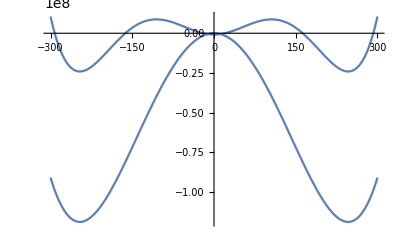

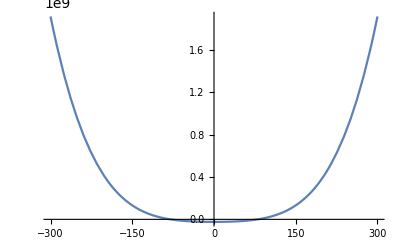

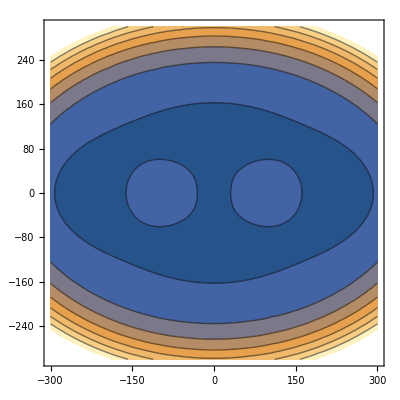

```mathematica
i=1;
T=0;
Hmass=branchlist[[i,1]];
Hchmass=branchlist[[i,2]];
Amass=branchlist[[i,3]];
λ2=branchlist[[i,4]];
λ345=branchlist[[i,5]];
deltamh=deltaslist[[i,1]];
deltamH=deltaslist[[i,2]];
deltaλ1=deltaslist[[i,3]];
Plot[{treepotential[T,h,0],treepotential[T,h,0]+CWV[T,h,0]+Counterterms[T,h,0]}/.replacePar/.replaceVev,{h,-300,300}]
Plot[{treepotential[T,246.22,h]+CWV[T,246.22,h]+Counterterms[T,246.22,h]}/.replacePar/.replaceVev,{h,-300,300}]
ContourPlot[{treepotential[T,h,s]+CWVwithGB[T,h,s]+Counterterms[T,h,s]}/.replacePar/.replaceVev,{h,-300,300},{s,-300,300}]
```

```mathematica
yt
```

0.99366

```mathematica
replacePar/.replaceVev
```

{λ1→0.129487,λ3→8.58549,λ4→-4.29175,λ5→-4.29175,μ2sq→4980.38}

```mathematica
T=1000;
H=0;
v1=500;
{massγsq[T,v1,H],massZsq[T,v1,H],massWsq[T,v1,H]}/.replacePar/.replaceVev
{massHsq[T,v1,H],massHiggssq[T,v1,H]}/.replacePar/.replaceVev
{masschϕsq[T,v1,H],massAsq[T,v1,H],massϕsq[T,v1,H],masschHsq[T,v1,H]}/.replacePar/.replaceVev
```

{252066.,879557.,879232.}

{1.36608×10^6,1.56187×10^6}

{1.49712×10^6,2.43901×10^6,1.49712×10^6,2.43901×10^6}

```mathematica
{masstsq[T,v,0],massbsq[T,v,0],massTausq[T,v,0]}/.replacePar/.replaceVev
```

{29929.,17.4724,3.1684}

```mathematica
T=100;
{massHsq[T,v,0],massHiggssq[T,v,0]}/.replacePar/.replaceVev
```

{18649.5,30426.1}

```mathematica
ytau
```

0.0102238

```mathematica
λ2
```

0.4

```mathematica
CWVwithGB[0,246.22,0]/.replacePar/.replaceVev
```

2.59018×10^7

```mathematica
deriv[masschϕsq[0,a,0],a]/.a->v/.replacePar/.replaceVev
```

63.7645

```mathematica
deriv[massϕsq[0,a,0],a]/.a->v/.replacePar/.replaceVev
```

63.7645

```mathematica
CWV[0,v,0]/.replacePar/.replaceVev
```

2.87487×10^7

```mathematica
NewCWV[0,v,0]/.replacePar/.replaceVev
```

2.87487×10^7

```mathematica
NewCWV[T_,h_,H_]:=1/(64*π^2)*(-12*masstsq[T,h,H]^2 * (Log[masstsq[T,h,H]/Q^2]-3/2)-12*massbsq[T,h,H]^2 * (Log[massbsq[T,h,H]/Q^2]-3/2)-4*massTausq[T,h,H]^2 * (Log[massTausq[T,h,H]/Q^2]-3/2)+2*massWsq[T,h,H]^2*(Log[massWsq[T,h,H]/Q^2]-3/2)+4*massWsq[T,h,H]^2*(Log[massWsq[T,h,H]/Q^2]-1/2)+1*massZsq[T,h,H]^2*(Log[massZsq[T,h,H]/Q^2]-3/2)+2*massZsq[T,h,H]^2*(Log[massZsq[T,h,H]/Q^2]-1/2)+massHiggssq[T,h,H]^2*(Log[massHiggssq[T,h,H]/Q^2]-3/2)+massHsq[T,h,H]^2*(Log[massHsq[T,h,H]/Q^2]-3/2)+massAsq[T,h,H]^2*(Log[massAsq[T,h,H]/Q^2]-3/2)+masschHsq[T,h,H]^2*(Log[masschHsq[T,h,H]/Q^2]-3/2))
```

```mathematica
NewCWVwithGB[T_,h_,H_]:=1/(64*π^2)*(-12*masstsq[T,h,H]^2 * (Log[masstsq[T,h,H]/Q^2]-3/2)-12*massbsq[T,h,H]^2 * (Log[massbsq[T,h,H]/Q^2]-3/2)-4*massTausq[T,h,H]^2 * (Log[massTausq[T,h,H]/Q^2]-3/2)+2*massWsq[T,h,H]^2*(Log[massWsq[T,h,H]/Q^2]-3/2)+4*massWsq[T,h,H]^2*(Log[massWsq[T,h,H]/Q^2]-1/2)+1*massZsq[T,h,H]^2*(Log[massZsq[T,h,H]/Q^2]-3/2)+2*massZsq[T,h,H]^2*(Log[massZsq[T,h,H]/Q^2]-1/2)+massHiggssq[T,h,H]^2*(Log[massHiggssq[T,h,H]/Q^2]-3/2)+massHsq[T,h,H]^2*(Log[massHsq[T,h,H]/Q^2]-3/2)+massAsq[T,h,H]^2*(Log[massAsq[T,h,H]/Q^2]-3/2)+massϕsq[T,h,H]^2*(Log[massϕsq[T,h,H]/Q^2]-3/2)+masschHsq[T,h,H]^2*(Log[masschHsq[T,h,H]/Q^2]-3/2)+masschϕsq[T,h,H]^2*(Log[masschϕsq[T,h,H]/Q^2]-3/2))
```

```mathematica
G[masschϕsq[T,v,0]]/.replacePar/.replaceVev
```

-2.21577×10^-23

```mathematica
1/(64*π^2)*masschϕsq[T,v,0]^2 *(Log[masschϕsq[T,v,0]/Q^2]-3/2)/.replacePar/.replaceVev
```

-2.21577×10^-23